```mathematica
ResourceFunction["MaTeXInstall"][]
<<MaTeX`
```

PacletObject[…]

## Definitions

### Integrand of quantum amplitudes

```mathematica
(*gg[A_,B_]:={{A,B},{Conjugate[B],Conjugate[A]}};
InnerProductMinus[C1_,D1_,A1_,B1_,A2_,B2_,C2_,D2_]:=lp.ConjugateTranspose[gg[C1,D1]].ConjugateTranspose[gg[A1,B1]].PauliMatrix[3].gg[A2,B2].gg[C2,D2].lm;
InnerProductPlus[C1_,D1_,A1_,B1_,A2_,B2_,C2_,D2_]:=lp.ConjugateTranspose[gg[C1,D1]].ConjugateTranspose[gg[A1,B1]].PauliMatrix[3].gg[A2,B2].gg[C2,D2].lp;
IntegrandFactor[C1_,D1_,A1_,B1_,A2_,B2_,C2_,D2_,s_]:=Exp[-s*InnerProductPlus[C1,D1,A1,B1,A2,B2,C2,D2]^2] InnerProductMinus[C1,D1,A1,B1,A2,B2,C2,D2]^(-1+2*I*s)
FullSimplify[InnerProductMinus[C1,D1,A1,B1,A2,B2,C2,D2]];
FullSimplify[InnerProductPlus[C1,D1,A1,B1,A2,B2,C2,D2]];*)
```

### Basic definitions

```mathematica
η={{1,0,0},{0,-1,0},{0,0,-1}};
MinProd[v_,w_]:=v[[1]]*w[[1]]-v[[2]]w[[2]]-v[[3]]w[[3]];
MinNorm[v_]:=v[[1]]^2-v[[2]]^2-v[[3]]^2;
CrossProd[v_,w_]:={v[[2]]w[[3]]-v[[3]]w[[2]],v[[3]]w[[1]]-v[[1]]w[[3]],v[[1]]w[[2]]-v[[2]]w[[1]]};
DihAngSL[vab_,vac_,vbc_]:=ArcTanh[MinProd[vbc,CrossProd[vab,vac]]/MinProd[CrossProd[vac,vbc],CrossProd[vab,vac]]];
DihAngTL[vab_,vac_,vbc_]:=ArcTan[MinProd[vbc,CrossProd[vab,vac]]/MinProd[CrossProd[vac,vbc],CrossProd[vab,vac]]];
lp=1/(√2){1,1};
lm=1/(√2){1,-1};
ζ={PauliMatrix[3],I*PauliMatrix[2],-I*PauliMatrix[1]};
g[α_,u_,β_]:=MatrixExp[(I*α)/2 ζ[[1]]].MatrixExp[(I*u)/2 ζ[[3]]].MatrixExp[(I*β)/2 ζ[[1]]];
h[α_,t_]:=MatrixExp[(I*α)/2 ζ[[1]]].MatrixExp[(I*t)/2 ζ[[2]]];
slv[α_,t_,i_]:=-I*lp.ConjugateTranspose[h[α,t]].PauliMatrix[3].ζ[[i]].h[α,t].lm;
llv[α_,t_,i_]:=lp.ConjugateTranspose[h[α,t]].PauliMatrix[3].ζ[[i]].h[α,t].lp;
(*ϑ[α_,t_]:=lm.ConjugateTranspose[h[α,t]].PauliMatrix[3].h[α,t].lp;*)
TimeRefl[v_]:={-v[[1]],v[[2]],v[[3]]};
GenerateNull[slv_]:={Cosh[ArcSinh[-slv[[1]]]],Cos[ArcTan[slv[[3]],slv[[2]]]]+slv[[1]]Sin[ArcTan[slv[[3]],slv[[2]]]],-Sin[ArcTan[slv[[3]],slv[[2]]]]+slv[[1]]Cos[ArcTan[slv[[3]],slv[[2]]]]};
```

### Reflection at trapezoid 6

```mathematica
frustum[a0_,a1_,b_]:={{0,a0/2,a0/2},{0,-a0/2,a0/2},{0,a0/2,-a0/2},{0,-a0/2,-a0/2},{√(1/2 (a0-a1)^2-b^2),a1/2,a1/2},{√(1/2 (a0-a1)^2-b^2),-a1/2,a1/2},{√(1/2 (a0-a1)^2-b^2),a1/2,-a1/2},{√(1/2 (a0-a1)^2-b^2),-a1/2,-a1/2}}
N6[a0_,a1_,b_]:={-(a0-a1)/(2b),0,-1/b √((a0-a1)^2/2-b^2)};
Plane6[a0_,a1_,b_,x_]:=MinProd[N6[a0,a1,b],x]+(a0 √(1/2 (a0-a1)^2-b^2))/(2 b);
Refl6[a0_,a1_,b_,P_]:=Flatten[(P+2λ*N6[a0,a1,b])/.Solve[Plane6[a0,a1,b,P+λ*N6[a0,a1,b]]==0,λ]]
```

```mathematica
(*Manipulate[Graphics3D[{PointSize[Large],Black,Point[frustum[2,1,b]],Red,Point[Table[Refl6[2,1,b,frustum[2,1,b][[i]]],{i,1,8}]],Opacity[0.3],InfinitePlane[frustum[2,1,b][[{3,4,7}]]],Black,Arrow[{frustum[2,1,b][[1]],frustum[2,1,b][[1]]+λ*N6[2,1,b]}]},Boxed->False],{b,0,√(1/2)},{λ,-10,10}]*)
```

### SequenceLimit

```mathematica
Options[SequenceLimit]={Method->Automatic};

SequenceLimit[l_List,opts:OptionsPattern[]]:=With[{res=sequenceLimit[OptionValue[Method],l]},
res/;!FailureQ[res]&&Head[res]=!=NumericalMath`NSequenceLimit
]

$crossoverLength=10;
$methods={"BrezinskiTheta","Euler","WynnEpsilon","NSequenceLimit",Automatic};

sequenceLimit["NSequenceLimit",l_]:=builtIn[l]

sequenceLimit[{Automatic|"NSequenceLimit"|"Automatic",mopts___},l_]:=builtIn[l,mopts]

sequenceLimit[Automatic|"Automatic",l_]:=If[VectorQ[l,MachineNumberQ]&&Length[l]≥$crossoverLength,builtIn[l],wynnEpsilon[l,1]]

sequenceLimit["BrezinskiTheta",seq_]:=btheta[seq]

sequenceLimit["WynnEpsilon",seq_]:=wynnEpsilon[seq,1]

sequenceLimit[{"WynnEpsilon",mopts__},seq_]:=wynnEpsilon[seq,"Parameter"/.{mopts}/.{"Parameter"->1}]

sequenceLimit["Euler",seq_]:=eulerKnopp[seq,-1]

sequenceLimit[{"Euler",mopts__},seq_]:=eulerKnopp[seq,"EulerRatio"/.{mopts}/.{"EulerRatio"->-1}]

sequenceLimit[x_,_]:=(
ResourceFunction["ResourceFunctionMessage"][SequenceLimit::moptxn,x,Method->x,$methods];
$Failed
)

builtIn[l_,mopts___]:=NumericalMath`NSequenceLimit[l,Method->{"WynnEpsilon",mopts}]

eulerKnopp[seq_?VectorQ,q_?NumericQ]:=Module[{n=Length[seq],ek},
ek[1]=0;
Do[
ek[k+1]=seq[[k]];
Do[
ek[j]+=(ek[j+1]-ek[j])/(1-q),
{j,k,1,-1}],
{k,n}];
ek[1]]

wynnEpsilon[seq_?VectorQ,h_?NumericQ]:=Module[{n=Length[seq],ep,v,w,pw},
Do[
ep[k]=seq[[k]];w=0;
Do[
v=w;w=ep[j];pw=10^-Precision[w];
ep[j]=v If[OddQ[k-j],h,1]+
If[!TrueQ[Abs[ep[j+1]-w]≤pw],
ep[j+1]-w,
pw
]^-1,
{j,k-1,1,-1}],
{k,n}];
ep[Mod[n,2,1]]]

btheta[seq_?VectorQ]:=Module[{n=Length[seq],de,ef,el,tha,thb,u,v,w,ya},
tha[1]=thb[1]=0;
Do[el=Quotient[2k-1,3];
If[OddQ[k],
v=0;u=tha[1];
tha[1]=seq[[k]];
Do[w=v;v=u;
If[ValueQ[tha[j+1]],u=tha[j+1]];
ef=1;
de=tha[j]-thb[j];
If[EvenQ[j],
ef=de(thb[j-1]-w);
de-=thb[j]-v];
tha[j+1]=(ya=w+ef/de),
{j,1,el}];
tha[el+Boole[EvenQ[el]]],
v=0;u=thb[1];
thb[1]=seq[[k]];
Do[w=v;v=u;
If[ValueQ[thb[j+1]],u=thb[j+1]];
ef=1;
de=thb[j]-tha[j];
If[EvenQ[j],
ef=de(tha[j-1]-w);
de-=tha[j]-v];
thb[j+1]=(ya=w+ef/de),
{j,1,el}];
thb[el+Boole[EvenQ[el]]]],
{k,n}];
If[OddQ[n],
tha[el+Boole[EvenQ[el]]],
thb[el+Boole[EvenQ[el]]]]]
```

### Dihedral angles, vartheta and Regge action

Functions of a0,a1 and b are functions of the absolute values. For edges spacelike, this means that b here is √(|(ib)^2|)

```mathematica
Subscript[Vol3, sl][a0_,a1_,b_]:=(a0^2+a0*a1+a1^2)/3 √((a0-a1)^2/2-b^2);
Subscript[Vol3, tl][a0_,a1_,b_]:=(a0^2+a0*a1+a1^2)/3 √((a0-a1)^2/2+b^2);
φSL[a0_,a1_,b_]:=ArcTanh[(2 √(1/2 (a0-a1)^2-b^2))/(a0-a1)];(*Dihedral angle at lower square for spacelike edge. Upper square is -φ. b is absolute value*)
ϑSL[a0_,a1_,b_]:=ArcTanh[(4 b √(1/2 (a0-a1)^2-b^2))/((a0-a1) (-a0+a1))];(*Dihdedral angle at trapezoid for spacelike edge*)
(*Subscript[S, I][a0_,a1_,b_]:=4(a0-a1)φSL[a0,a1,b]+4b*ϑSL[a0,a1,b]; Regge action in Sector I which agrees with asymptotics but bad numerical properties towards lightlike trap.*)
Subscript[ComplexS, I][a0_,a1_,b_]:=-4Abs[a0-a1]Log[Abs[a0-a1]+√(2(a0-a1)^2-4 b^2)]+4Abs[b]*Log[(a0-a1)^2+√(8 b^2((a0-a1)^2-2 b^2))]+(4Abs[b]-2Abs[a0-a1])Log[4 b^2-(a0-a1)^2]+I*Pi/2(4Abs[a0-a1]-4Abs[b]);
Subscript[S, I][a0_,a1_,b_]:=-4Abs[a0-a1]Log[Abs[a0-a1]+√(2(a0-a1)^2-4 b^2)]+4Abs[b]*Log[(a0-a1)^2+√(8 b^2((a0-a1)^2-2 b^2))]+(4Abs[b]-2Abs[a0-a1])Log[4 b^2-(a0-a1)^2];
(*This form of Subscript[S, I] has better prop. at lightlike trap. as it agrees with Subscript[S, null]*)
Subscript[S, null][a0_,a1_,b_]:=4Abs[a0-a1]Log[Abs[a0-a1]]-4b*Log[(a0-a1)^2/2];(*Regge action for null trapezoid from classical computation*)
Subscript[ComplexS, II][a0_,a1_,b_]:=-4(a0-a1)ArcSinh[(a0-a1)/(√((a0-a1)^2-4 b^2))]+4b(I*Pi/2+ArcCosh[(a0-a1)^2/((a0-a1)^2-4 b^2)]);(*Regge action in Sector II from classical computation*)
Subscript[S, II][a0_,a1_,b_]:=-4(a0-a1)ArcSinh[(a0-a1)/(√((a0-a1)^2-4 b^2))]+4b*ArcCosh[(a0-a1)^2/((a0-a1)^2-4 b^2)];
Subscript[S, III][a0_,a1_,b_]:=-4(a0-a1)ArcSinh[(a0-a1)/(√(4 b^2+(a0-a1)^2))]+4b*(Pi/2-ArcCos[(a0-a1)^2/(4 b^2+(a0-a1)^2)]);
Subscript[S, ϕ,sl][a0_,a1_,b_,ϕ0_,ϕ1_,m_]:=(a0+a1)^2/(8 √((a0-a1)^2/2-b^2))(ϕ0-ϕ1)^2-m^2/2*Subscript[Vol3, sl][a0,a1,b]*(ϕ0^2+ϕ1^2)/2;
Subscript[S, ϕ,tl][a0_,a1_,b_,ϕ0_,ϕ1_,m_]:=(a0+a1)^2/(8 √((a0-a1)^2/2+b^2))(ϕ0-ϕ1)^2-m^2/2*Subscript[Vol3, tl][a0,a1,b]*(ϕ0^2+ϕ1^2)/2;
φTL[a0_,a1_,b_]:=1/2 Log[(a0-a1+2 √(2(a0-a1)^2+4 b^2))/(a0-a1-2 √(2(a0-a1)^2+4 b^2))];(*Dihedral angle at lower square for timlike edge. Upper square is -φ*)
ϑTL[a0_,a1_,b_]:=-I/2 Log[((a0-a1)^2+2*I*b*√(2(a0-a1)^2+4 b^2))/((a0-a1)^2-2*I*b*√(2(a0-a1)^2+4 b^2))];(*Dihdedral angle at trapezoid for time edge, CORRECTED MINUS SIGN*)
ϑaSL[a0_,a1_,b_]:=Sqrt[((a0-a1)+Sqrt[2(a0-a1)^2-4 b^2])/((a0-a1)-Sqrt[2(a0-a1)^2-4 b^2])];(*vartheta at lower square for spacelike edge. Upper square is 1/ϑa*)
ϑaTL[a0_,a1_,b_]:=Sqrt[((a0-a1)+Sqrt[2(a0-a1)^2+4 b^2])/((a0-a1)-Sqrt[2(a0-a1)^2+4 b^2])];(*vartheta at lower square for timelike edge. Upper square is 1/ϑa*)
ϑbSL[a0_,a1_,b_]:=Sqrt[((a0-a1)^2-2b*Sqrt[2(a0-a1)^2-4 b^2])/((a0-a1)^2+2b*Sqrt[2(a0-a1)^2-4 b^2])];(*vartheta at trapezoid for spacelike edge*)
```

```mathematica
(*DihAngSL[Subscript[n, 13],Subscript[n, 16],n36SL[a0,a1,b]];
DihAngSL[Subscript[n, 13],Subscript[n, 16],n36TL[a0,a1,b]];
DihAngSL[Subscript[n, 13],n36SL[a0,a1,b],Subscript[n, 16]];
DihAngSL[Subscript[n, 23],Subscript[n, 26],n36SL[a0,a1,b]];
DihAngTL[Subscript[n, 13],n36TL[a0,a1,b],Subscript[n, 16]];
DihAngSL[Subscript[n, 13],n36TL[a0,a1,b],Subscript[n, 16]];
DihAngSL[Subscript[n, 23],Subscript[n, 26],n36TL[a0,a1,b]];*)
```

```mathematica
Series[ArcCos[1/(1+4/x^2)],{x,0,4}]
Series[ArcSinh[1/Sqrt[1+4/x^2]],{x,0,4}]
Series[1/Sqrt[x^2/2+1],{x,0,4}]
Series[√(x^2/2+1),{x,0,4}]
```

π/2-x^2/4+x^4/16+O[x]^5

x/(2 √(1/x^2) x)-1/12 (√(1/x^2) x) x^3+O[x]^5

1-x^2/4+(3 x^4)/32+O[x]^5

(√2 √(1/x^2) x)/x+(√(1/x^2) x x)/(2 √2)-((√(1/x^2) x) x^3)/(16 √2)+O[x]^5

### Edge vectors, the Hessian and its determinant

```mathematica
Subscript[n, 13]={0,0,1};
Subscript[n, 14]={0,-1,0};
Subscript[n, 15]={0,0,-1};
Subscript[n, 16]={0,1,0};
Subscript[n, 23]={0,0,-1};
Subscript[n, 24]={0,1,0};
Subscript[n, 25]={0,0,1};
Subscript[n, 26]={0,-1,0};
n34SL[a0_,a1_,b_]:=1/b{-√((a0-a1)^2/2-b^2),(a0-a1)/2,(a0-a1)/2};
n34TL[a0_,a1_,b_]:=1/b{-√((a0-a1)^2/2+b^2),(a0-a1)/2,(a0-a1)/2};
n45SL[a0_,a1_,b_]:=1/b{-√((a0-a1)^2/2-b^2),-(a0-a1)/2,(a0-a1)/2};
n45TL[a0_,a1_,b_]:=1/b{-√((a0-a1)^2/2+b^2),-(a0-a1)/2,(a0-a1)/2};
n36SL[a0_,a1_,b_]:=1/b{√((a0-a1)^2/2-b^2),-(a0-a1)/2,(a0-a1)/2};
n36TL[a0_,a1_,b_]:=1/b{√((a0-a1)^2/2+b^2),-(a0-a1)/2,(a0-a1)/2};
n56SL[a0_,a1_,b_]:=1/b{-√((a0-a1)^2/2-b^2),-(a0-a1)/2,-(a0-a1)/2};
n56TL[a0_,a1_,b_]:=1/b{-√((a0-a1)^2/2+b^2),-(a0-a1)/2,-(a0-a1)/2};
NormalVectorsSL[a0_,a1_,b_]:={{0,0,Subscript[n, 13],Subscript[n, 14],Subscript[n, 15],Subscript[n, 16]},
{0,0,Subscript[n, 23],Subscript[n, 24],Subscript[n, 25],Subscript[n, 26]},
{Subscript[n, 13],Subscript[n, 23],0,n34SL[a0,a1,b],0,n36SL[a0,a1,b]},
{Subscript[n, 14],Subscript[n, 24],n34SL[a0,a1,b],0,n45SL[a0,a1,b],0},
{Subscript[n, 15],Subscript[n, 25],0,n45SL[a0,a1,b],0,n56SL[a0,a1,b]},
{Subscript[n, 16],Subscript[n, 26],n36SL[a0,a1,b],0,n56SL[a0,a1,b],0}};
NormalVectorsTL[a0_,a1_,b_]:={{0,0,Subscript[n, 13],Subscript[n, 14],Subscript[n, 15],Subscript[n, 16]},
{0,0,Subscript[n, 23],Subscript[n, 24],Subscript[n, 25],Subscript[n, 26]},
{Subscript[n, 13],Subscript[n, 23],0,n34TL[a0,a1,b],0,n36TL[a0,a1,b]},
{Subscript[n, 14],Subscript[n, 24],n34TL[a0,a1,b],0,n45TL[a0,a1,b],0},
{Subscript[n, 15],Subscript[n, 25],0,n45TL[a0,a1,b],0,n56TL[a0,a1,b]},
{Subscript[n, 16],Subscript[n, 26],n36TL[a0,a1,b],0,n56TL[a0,a1,b],0}};
VarThetaSquared={
{0,0,X1,X1,X1,X1},
{0,0,1/X1,1/X1,1/X1,1/X1},
{X1,1/X1,0,X2,0,X2},
{X1,1/X1,X2,0,X2,0},
{X1,1/X1,0,X2,0,X2},
{X1,1/X1,X2,0,X2,0}};
Indexsets={{3,4,5,6},{3,4,5,6},{1,2,4,6},{1,2,3,5},{1,2,4,6},{1,2,3,5}};
IndexsetsSL={{3,4,5,6},{3,4,5,6},{1,2},{1,2},{1,2},{1,2}};
IndexsetsTL={{},{},{4,6},{3,5},{4,6},{3,5}};
LengthsetsSL[a0_,a1_,b_]:={
{0,0,a0,a0,a0,a0},
{0,0,a1,a1,a1,a1},
{a0,a1,0,b,0,b},
{a0,a1,b,0,b,0},
{a0,a1,0,b,0,b},
{a0,a1,b,0,b,0}};
LengthsetsTL[a0_,a1_,b_]:={
{0,0,a0,a0,a0,a0},
{0,0,a1,a1,a1,a1},
{a0,a1,0,-b,0,-b},
{a0,a1,-b,0,-b,0},
{a0,a1,0,-b,0,-b},
{a0,a1,-b,0,-b,0}};
(*SpacelikeHessian[a0_,a1_,b_]:=Table[Table[(I/2)^2*2*I*Sum[LengthsetsSL[a0,a1,b][[A,B]]*(η[[i,j]]+NormalVectorsSL[a0,a1,b][[A,B]][[i]]NormalVectorsSL[a0,a1,b][[A,B]][[j]]-I*GenerateNull[NormalVectorsSL[a0,a1,b][[A,B]]][[i]]*GenerateNull[NormalVectorsSL[a0,a1,b][[A,B]]][[j]]*VarThetaSquared[[A,B]]),{A,Indexsets[[B]]}],{i,1,3},{j,1,3}],{B,1,6}];(*non-unital varthetas, all edges spacelike as well as the faces*)
SpacelikeHessianId[a0_,a1_,b_]:=Table[Table[(I/2)^2*2*I*Sum[LengthsetsSL[a0,a1,b][[A,B]]*(η[[i,j]]+NormalVectorsSL[a0,a1,b][[A,B]][[i]]NormalVectorsSL[a0,a1,b][[A,B]][[j]]-I*GenerateNull[NormalVectorsSL[a0,a1,b][[A,B]]][[i]]*GenerateNull[NormalVectorsSL[a0,a1,b][[A,B]]][[j]]),{A,Indexsets[[B]]}],{i,1,3},{j,1,3}],{B,1,6}];(*Vlaid for Sector I and II*)
(*TimelikeHessian[a0_,a1_,b_]:=Table[Subscript[S, I,alt][10,20,b]Table[(I/2)^2*(2*Sum[LengthsetsTL[a0,a1,b][[A,B]]*(η[[i,j]]-NormalVectorsTL[a0,a1,b][[A,B]][[i]]*NormalVectorsTL[a0,a1,b][[A,B]][[j]]),{A,IndexsetsTL[[B]]}]+2*I*Sum[Lengthsets[a0,a1,b][[A,B]]*(η[[i,j]]+NormalVectorsTL[a0,a1,b][[A,B]][[i]]NormalVectorsTL[a0,a1,b][[A,B]][[j]]-I*GenerateNull[NormalVectorsTL[a0,a1,b][[A,B]]][[i]]*GenerateNull[NormalVectorsTL[a0,a1,b][[A,B]]][[j]]*VarThetaSquared[[A,B]]),{A,IndexsetsSL[[B]]}]),{i,1,3},{j,1,3}],{B,1,6}];    Does not appear in the asymptotics! *)
TimelikeHessianId[a0_,a1_,b_]:=Table[Table[(I/2)^2*(2*Sum[LengthsetsTL[a0,a1,b][[A,B]]*(η[[i,j]]-NormalVectorsTL[a0,a1,b][[A,B]][[i]]*NormalVectorsTL[a0,a1,b][[A,B]][[j]]),{A,IndexsetsTL[[B]]}]+2*I*Sum[LengthsetsSL[a0,a1,b][[A,B]]*(η[[i,j]]+NormalVectorsTL[a0,a1,b][[A,B]][[i]]NormalVectorsTL[a0,a1,b][[A,B]][[j]]-I*GenerateNull[NormalVectorsTL[a0,a1,b][[A,B]]][[i]]*GenerateNull[NormalVectorsTL[a0,a1,b][[A,B]]][[j]]),{A,IndexsetsSL[[B]]}]),{i,1,3},{j,1,3}],{B,1,6}];
DetSL[a0_,a1_,b_]:=(-(4 ⅈ a0^3 a1^3 (1+X1^2)^3)/X1^3*(1/(64 b^3 X1^2)(ⅈ ((a0-a1)^2-4 b^2)+(a0-a1)^2 X2+2 b √(2 (a0-a1)^2-4 b^2) X2) ((a0 √(2 (a0-a1)^2-4 b^2) X1 (ⅈ+X2)-a1 √(2 (a0-a1)^2-4 b^2) X1 (ⅈ+X2)-2 a0 b X1 (X1+X2)+2 a1 b (1+X1 X2))^2-2 (a1^2 X1 (ⅈ+X2)+a0 X1 (b (ⅈ+X1)+a0 (ⅈ+X2))+a1 (b+ⅈ b X1-2 a0 X1 (ⅈ+X2))) (a1^2 X1 (ⅈ+X2)+X1 (-4 ⅈ b^2+2 a0 b (-ⅈ+X1)-2 b √(2 (a0-a1)^2-4 b^2) X2+a0^2 (ⅈ+X2))+2 a1 (b-ⅈ b X1-a0 X1 (ⅈ+X2)))))^2*1/(64 b^3 X1^2)((-4 ⅈ b^2+(a0-a1)^2 (ⅈ+X2)) (a0 X1 (-2 b X1+√(2 (a0-a1)^2-4 b^2) (ⅈ+X2))+a1 (2 b-√(2 (a0-a1)^2-4 b^2) X1 (ⅈ+X2)))^2-2 (a1^2 X1 (ⅈ+X2)+X1 (-4 ⅈ b^2+2 a0 b (-ⅈ+X1)+a0^2 (ⅈ+X2))+2 a1 (b-ⅈ b X1-a0 X1 (ⅈ+X2))) (-2 (a0-a1)^2 b^2 X1 X2^2-(4 ⅈ b^2-(a0-a1)^2 (ⅈ+X2)) (a1^2 X1 (ⅈ+X2)+a0 X1 (b (ⅈ+X1)+a0 (ⅈ+X2))+a1 (b+ⅈ b X1-2 a0 X1 (ⅈ+X2))))))/.{X1->ϑaSL[a0,a1,b]^2}/.{X2->ϑbSL[a0,a1,b]^2};
DetSLalt[a0_,a1_,b_]:=(-(4 ⅈ a0^3 a1^3 (1+X1^2)^3)/X1^3*(1/(64 b^3 X1^2)(ⅈ ((a0-a1)^2-4 b^2)+(a0-a1)^2 X2+2 b √(2 (a0-a1)^2-4 b^2) X2) ((a0 √(2 (a0-a1)^2-4 b^2) X1 (ⅈ+X2)-a1 √(2 (a0-a1)^2-4 b^2) X1 (ⅈ+X2)-2 a0 b X1 (X1+X2)+2 a1 b (1+X1 X2))^2-2 (a1^2 X1 (ⅈ+X2)+a0 X1 (b (ⅈ+X1)+a0 (ⅈ+X2))+a1 (b+ⅈ b X1-2 a0 X1 (ⅈ+X2))) (a1^2 X1 (ⅈ+X2)+X1 (-4 ⅈ b^2+2 a0 b (-ⅈ+X1)-2 b √(2 (a0-a1)^2-4 b^2) X2+a0^2 (ⅈ+X2))+2 a1 (b-ⅈ b X1-a0 X1 (ⅈ+X2)))))^2*1/(64 b^3 X1^2)((-4 ⅈ b^2+(a0-a1)^2 (ⅈ+X2)) (a0 X1 (-2 b X1+√(2 (a0-a1)^2-4 b^2) (ⅈ+X2))+a1 (2 b-√(2 (a0-a1)^2-4 b^2) X1 (ⅈ+X2)))^2-2 (a1^2 X1 (ⅈ+X2)+X1 (-4 ⅈ b^2+2 a0 b (-ⅈ+X1)+a0^2 (ⅈ+X2))+2 a1 (b-ⅈ b X1-a0 X1 (ⅈ+X2))) (-2 (a0-a1)^2 b^2 X1 X2^2-(4 ⅈ b^2-(a0-a1)^2 (ⅈ+X2)) (a1^2 X1 (ⅈ+X2)+a0 X1 (b (ⅈ+X1)+a0 (ⅈ+X2))+a1 (b+ⅈ b X1-2 a0 X1 (ⅈ+X2))))))/.{X1->1/ϑaSL[a0,a1,b]^2}/.{X2->1/ϑbSL[a0,a1,b]^2};
(*DetSLId[a0_,a1_,b_]:=-32 ⅈ a0^3 a1^3*(1/b^3(1/32-ⅈ/32) ((a0-a1)^2+(1-ⅈ) b (-2 ⅈ b+√(2 (a0-a1)^2-4 b^2))) ((a0-a1)^2 ((-2+2 ⅈ) b+√(2 (a0-a1)^2-4 b^2))^2+2 ((a0-a1)^2+(a0+a1) b) (-a0^2-a1^2+2 a0 (a1+ⅈ b)+2 ⅈ a1 b+(2+2 ⅈ) b^2+(1-ⅈ) b √(2 (a0-a1)^2-4 b^2))))^2*(1/b^3(1/32-ⅈ/32) (2 (a0-a1)^2 b^2 (ⅈ (a0-a1)^2+2 (a0+a1) b+(2-2 ⅈ) b^2)+((a0-a1)^2-(2+2 ⅈ) b^2) (2 ((a0-a1)^2+(a0+a1) b) ((a0-a1)^2-2 ⅈ (a0+a1) b-(2+2 ⅈ) b^2)-(a0-a1)^2 ((-1+ⅈ) b+√(2 (a0-a1)^2-4 b^2))^2)))*)(*Is valid for Sector I and II*)
(*DetSLIdII=-32 ⅈ a0^3 a1^3*(-1/b^3(1/32-ⅈ/32) ((a0-a1)^2+(1-ⅈ) b (-2 ⅈ b+√(2 (a0-a1)^2-4 b^2))) ((a0-a1)^2 ((-2+2 ⅈ) b+√(2 (a0-a1)^2-4 b^2))^2+2 ((a0-a1)^2+(a0+a1) b) (-a0^2-a1^2+2 a0 (a1+ⅈ b)+2 ⅈ a1 b+(2+2 ⅈ) b^2+(1-ⅈ) b √(2 (a0-a1)^2-4 b^2))))^2*(1/b^3(1/32-ⅈ/32) (2 (a0-a1)^2 b^2 (ⅈ (a0-a1)^2+2 (a0+a1) b+(2-2 ⅈ) b^2)+((a0-a1)^2-(2+2 ⅈ) b^2) (2 ((a0-a1)^2+(a0+a1) b) ((a0-a1)^2-2 ⅈ (a0+a1) b-(2+2 ⅈ) b^2)-(a0-a1)^2 ((-1+ⅈ) b+√(2 (a0-a1)^2-4 b^2))^2)))*)
DetTLDiagHess[a0_,a1_,b_]:=-32 ⅈ a0^3 a1^3*((-1-(a0-a1)^2/(4 b^2)) b (-(((-2+2 ⅈ) (a0+a1)-(a0-a1)^2/b-4 b) ((a0-a1)^2+(1+ⅈ) (a0+a1) b))/(8 b)-((a0-a1)^2 (-2 b+√(2 (a0-a1)^2+4 b^2))^2)/(16 b^2)))^3;
(*InvSqtDetSLId[a0_,a1_,b_]:=1/Sqrt[DetSLId[a0,a1,b]];(*complex inverse square root of Hessian determinant at 1 in I, already smooth*)*)
InvSqtDetSLI[a0_,a1_,b_]:=1/Sqrt[DetSL[a0,a1,b]];(*complex inverse square root of Hessian determinant at ϑ in I, already smooth*)
InvSqtDetSLIdII[a0_,a1_,b_]:=-1/(Sqrt[-32 ⅈ a0^3 a1^3]Sqrt[(1/b^3(1/32-ⅈ/32) ((a0-a1)^2+(1-ⅈ) b (-2 ⅈ b+√(2 (a0-a1)^2-4 b^2))) ((a0-a1)^2 ((-2+2 ⅈ) b+√(2 (a0-a1)^2-4 b^2))^2+2 ((a0-a1)^2+(a0+a1) b) (-a0^2-a1^2+2 a0 (a1+ⅈ b)+2 ⅈ a1 b+(2+2 ⅈ) b^2+(1-ⅈ) b √(2 (a0-a1)^2-4 b^2))))^2*(1/b^3(1/32-ⅈ/32) (2 (a0-a1)^2 b^2 (ⅈ (a0-a1)^2+2 (a0+a1) b+(2-2 ⅈ) b^2)+((a0-a1)^2-(2+2 ⅈ) b^2) (2 ((a0-a1)^2+(a0+a1) b) ((a0-a1)^2-2 ⅈ (a0+a1) b-(2+2 ⅈ) b^2)-(a0-a1)^2 ((-1+ⅈ) b+√(2 (a0-a1)^2-4 b^2))^2)))])(*smooth complex inverse square root of Hessian in II*)
InvSqtDetTLIdIII[a0_,a1_,b_]:=1/(Sqrt[-32 ⅈ a0^3 a1^3]Sqrt[((-1-(a0-a1)^2/(4 b^2)) b)^3]Sqrt[ (-(((-2+2 ⅈ) (a0+a1)-(a0-a1)^2/b-4 b) ((a0-a1)^2+(1+ⅈ) (a0+a1) b))/(8 b)-((a0-a1)^2 (-2 b+√(2 (a0-a1)^2+4 b^2))^2)/(16 b^2))^3]);(*smooth complex inverse square root of Hessian determinant  in III*)*)
```

Smooth inverse square roots above

### Computing Hessians and their determinants

Spacelike Hessian at ϑ

```mathematica
MatrixForm[Simplify[SpacelikeHessian[a0,a1,b][[1]],a0>0&&a1>0&&(a0-a1)^2/4<b^2<(a0-a1)^2/2&&X1>0&&X2>0]];
MatrixForm[Simplify[SpacelikeHessian[a0,a1,b][[2]],a0>0&&a1>0&&(a0-a1)^2/4<b^2<(a0-a1)^2/2&&X1>0&&X2>0]];
MatrixForm[Simplify[SpacelikeHessian[a0,a1,b][[3]],a0>0&&a1>0&&(a0-a1)^2/4<b^2<(a0-a1)^2/2&&X1>0&&X2>0]];
MatrixForm[Simplify[SpacelikeHessian[a0,a1,b][[4]],a0>0&&a1>0&&(a0-a1)^2/4<b^2<(a0-a1)^2/2&&X1>0&&X2>0]];
MatrixForm[Simplify[SpacelikeHessian[a0,a1,b][[5]],a0>0&&a1>0&&(a0-a1)^2/4<b^2<(a0-a1)^2/2&&X1>0&&X2>0]];
MatrixForm[Simplify[SpacelikeHessian[a0,a1,b][[6]],a0>0&&a1>0&&(a0-a1)^2/4<b^2<(a0-a1)^2/2&&X1>0&&X2>0]];
```

Spacelike Hessian at 1 in Sector I

```mathematica
MatrixForm[Simplify[SpacelikeHessianId[a0,a1,b][[1]],a0>0&&a1>0&&(a0-a1)^2/4<b^2<(a0-a1)^2/2&&X1>0&&X2>0]];
MatrixForm[Simplify[SpacelikeHessianId[a0,a1,b][[2]],a0>0&&a1>0&&(a0-a1)^2/4<b^2<(a0-a1)^2/2&&X1>0&&X2>0]];
MatrixForm[Simplify[SpacelikeHessianId[a0,a1,b][[3]],a0>0&&a1>0&&(a0-a1)^2/4<b^2<(a0-a1)^2/2&&X1>0&&X2>0]];
MatrixForm[Simplify[SpacelikeHessianId[a0,a1,b][[4]],a0>0&&a1>0&&(a0-a1)^2/4<b^2<(a0-a1)^2/2&&X1>0&&X2>0]];
MatrixForm[SIplify[SpacelikeHessianId[a0,a1,b][[5]],a0>0&&a1>0&&(a0-a1)^2/4<b^2<(a0-a1)^2/2&&X1>0&&X2>0]];
MatrixForm[Simplify[SpacelikeHessianId[a0,a1,b][[6]],a0>0&&a1>0&&(a0-a1)^2/4<b^2<(a0-a1)^2/2&&X1>0&&X2>0]];
```

```mathematica
FullSimplify[Det[({{-((1/2+ⅈ/2) (a0^2+a0 (-2 a1+b)+a1 (a1+b)))/b, -((1/4+ⅈ/4) (a0-a1) ((-1+ⅈ) b+√2 √(a0^2-2 a0 a1+a1^2-2 b^2)))/b, 1/2 (-a0+a1)}, {-((1/4+ⅈ/4) (a0-a1) ((-1+ⅈ) b+√2 √(a0^2-2 a0 a1+a1^2-2 b^2)))/b, ((1/4+ⅈ/4) (-a0^2-a1^2+2 a0 (a1+ⅈ b)+2 ⅈ a1 b+(2+2 ⅈ) b^2))/b, 0}, {1/2 (-a0+a1), 0, -((1/4+ⅈ/4) (a0^2-2 a0 a1+a1^2-(2+2 ⅈ) b^2))/b}})],a0>0&&a1>0&&(a0-a1)^2/4<b^2<(a0-a1)^2/2&&X1>0&&X2>0]
```

1/b^3(1/32-ⅈ/32) (2 (a0-a1)^2 b^2 (ⅈ (a0-a1)^2+2 (a0+a1) b+(2-2 ⅈ) b^2)+((a0-a1)^2-(2+2 ⅈ) b^2) (2 ((a0-a1)^2+(a0+a1) b) ((a0-a1)^2-2 ⅈ (a0+a1) b-(2+2 ⅈ) b^2)-(a0-a1)^2 ((-1+ⅈ) b+√(2 (a0-a1)^2-4 b^2))^2))

Spacelike Hessian at 1 in Sector II

```mathematica
MatrixForm[Simplify[SpacelikeHessianId[a0,a1,b][[1]],a0>0&&a1>0&&0<b^2(a0-a1)^2/4&&X1>0&&X2>0]];
MatrixForm[Simplify[SpacelikeHessianId[a0,a1,b][[2]],a0>0&&a1>0&&0<b^2(a0-a1)^2/4&&X1>0&&X2>0]];
MatrixForm[Simplify[SpacelikeHessianId[a0,a1,b][[3]],a0>0&&a1>0&&0<b^2(a0-a1)^2/4&&X1>0&&X2>0]];
MatrixForm[Simplify[SpacelikeHessianId[a0,a1,b][[4]],a0>0&&a1>0&&0<b^2(a0-a1)^2/4&&X1>0&&X2>0]];
MatrixForm[Simplify[SpacelikeHessianId[a0,a1,b][[5]],a0>0&&a1>0&&0<b^2(a0-a1)^2/4&&X1>0&&X2>0]];
MatrixForm[Simplify[SpacelikeHessianId[a0,a1,b][[6]],a0>0&&a1>0&&0<b^2(a0-a1)^2/4&&X1>0&&X2>0]];
```

```mathematica
FullSimplify[Det[({{-((1/2+ⅈ/2) (a0^2+a0 (-2 a1+b)+a1 (a1+b)))/b, -((1/4+ⅈ/4) (a0-a1) ((-1+ⅈ) b+√2 √(a0^2-2 a0 a1+a1^2-2 b^2)))/b, 1/2 (-a0+a1)}, {-((1/4+ⅈ/4) (a0-a1) ((-1+ⅈ) b+√2 √(a0^2-2 a0 a1+a1^2-2 b^2)))/b, ((1/4+ⅈ/4) (-a0^2-a1^2+2 a0 (a1+ⅈ b)+2 ⅈ a1 b+(2+2 ⅈ) b^2))/b, 0}, {1/2 (-a0+a1), 0, -((1/4+ⅈ/4) (a0^2-2 a0 a1+a1^2-(2+2 ⅈ) b^2))/b}})],a0>0&&a1>0&&0<b^2(a0-a1)^2/4&&X1>0&&X2>0]
```

1/b^3(1/32-ⅈ/32) (2 (a0-a1)^2 b^2 (ⅈ (a0-a1)^2+2 (a0+a1) b+(2-2 ⅈ) b^2)+((a0-a1)^2-(2+2 ⅈ) b^2) (2 ((a0-a1)^2+(a0+a1) b) ((a0-a1)^2-2 ⅈ (a0+a1) b-(2+2 ⅈ) b^2)-(a0-a1)^2 ((-1+ⅈ) b+√(2 (a0-a1)^2-4 b^2))^2))

Timelike Hessian at 1 in Sector III

```mathematica
MatrixForm[FullSimplify[TimelikeHessianId[a0,a1,b][[1]],a0>0&&a1>0&&b>0&&X1>0]]
MatrixForm[FullSimplify[TimelikeHessianId[a0,a1,b][[2]],a0>0&&a1>0&&b>0&&X1>0]]
MatrixForm[FullSimplify[TimelikeHessianId[a0,a1,b][[3]],a0>0&&a1>0&&b>0&&X1>0]]
MatrixForm[FullSimplify[TimelikeHessianId[a0,a1,b][[4]],a0>0&&a1>0&&b>0&&X1>0]]
MatrixForm[FullSimplify[TimelikeHessianId[a0,a1,b][[5]],a0>0&&a1>0&&b>0&&X1>0]]
MatrixForm[FullSimplify[TimelikeHessianId[a0,a1,b][[6]],a0>0&&a1>0&&b>0&&X1>0]]
```

Part::partd: Part specification Lengthsets[a0,a1,b]⟦3,1⟧ is longer than depth of object.

Part::partw: Part 4 of Lengthsets[a0,a1,b] does not exist.

Part::partw: Part 5 of Lengthsets[a0,a1,b] does not exist.

Part::partw: Part 6 of Lengthsets[a0,a1,b] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification Lengthsets[a0,a1,b]⟦3,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

((-1/2-ⅈ/2) (Lengthsets[a0,a1,b]⟦3,1⟧+Lengthsets[a0,a1,b]⟦4,1⟧+Lengthsets[a0,a1,b]⟦5,1⟧+Lengthsets[a0,a1,b]⟦6,1⟧) | 1/2 (-Lengthsets[a0,a1,b]⟦3,1⟧+Lengthsets[a0,a1,b]⟦5,1⟧) | 1/2 (-Lengthsets[a0,a1,b]⟦4,1⟧+Lengthsets[a0,a1,b]⟦6,1⟧)
1/2 (-Lengthsets[a0,a1,b]⟦3,1⟧+Lengthsets[a0,a1,b]⟦5,1⟧) | (-1/2+ⅈ/2) (Lengthsets[a0,a1,b]⟦3,1⟧+Lengthsets[a0,a1,b]⟦5,1⟧) | 0
1/2 (-Lengthsets[a0,a1,b]⟦4,1⟧+Lengthsets[a0,a1,b]⟦6,1⟧) | 0 | (-1/2+ⅈ/2) (Lengthsets[a0,a1,b]⟦4,1⟧+Lengthsets[a0,a1,b]⟦6,1⟧))

Part::partd: Part specification Lengthsets[a0,a1,b]⟦3,1⟧ is longer than depth of object.

Part::partw: Part 4 of Lengthsets[a0,a1,b] does not exist.

Part::partw: Part 5 of Lengthsets[a0,a1,b] does not exist.

Part::partw: Part 6 of Lengthsets[a0,a1,b] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification Lengthsets[a0,a1,b]⟦3,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

((-1/2-ⅈ/2) (Lengthsets[a0,a1,b]⟦3,2⟧+Lengthsets[a0,a1,b]⟦4,2⟧+Lengthsets[a0,a1,b]⟦5,2⟧+Lengthsets[a0,a1,b]⟦6,2⟧) | 1/2 (Lengthsets[a0,a1,b]⟦3,2⟧-Lengthsets[a0,a1,b]⟦5,2⟧) | 1/2 (Lengthsets[a0,a1,b]⟦4,2⟧-Lengthsets[a0,a1,b]⟦6,2⟧)
1/2 (Lengthsets[a0,a1,b]⟦3,2⟧-Lengthsets[a0,a1,b]⟦5,2⟧) | (-1/2+ⅈ/2) (Lengthsets[a0,a1,b]⟦3,2⟧+Lengthsets[a0,a1,b]⟦5,2⟧) | 0
1/2 (Lengthsets[a0,a1,b]⟦4,2⟧-Lengthsets[a0,a1,b]⟦6,2⟧) | 0 | (-1/2+ⅈ/2) (Lengthsets[a0,a1,b]⟦4,2⟧+Lengthsets[a0,a1,b]⟦6,2⟧))

Part::partd: Part specification Lengthsets[a0,a1,b]⟦3,1⟧ is longer than depth of object.

Part::partw: Part 4 of Lengthsets[a0,a1,b] does not exist.

Part::partw: Part 5 of Lengthsets[a0,a1,b] does not exist.

Part::partw: Part 6 of Lengthsets[a0,a1,b] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification Lengthsets[a0,a1,b]⟦3,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

(-((a0-a1)^2+(1+ⅈ) b (Lengthsets[a0,a1,b]⟦1,3⟧+Lengthsets[a0,a1,b]⟦2,3⟧))/(2 b) | ((a0-a1) √(2 (a0-a1)^2+4 b^2)-2 b Lengthsets[a0,a1,b]⟦1,3⟧+2 b Lengthsets[a0,a1,b]⟦2,3⟧)/(4 b) | 0
((a0-a1) √(2 (a0-a1)^2+4 b^2)-2 b Lengthsets[a0,a1,b]⟦1,3⟧+2 b Lengthsets[a0,a1,b]⟦2,3⟧)/(4 b) | 1/4 (-(a0-a1)^2/b-4 b-(2-2 ⅈ) (Lengthsets[a0,a1,b]⟦1,3⟧+Lengthsets[a0,a1,b]⟦2,3⟧)) | 0
0 | 0 | (-1-(a0-a1)^2/(4 b^2)) b)

Part::partd: Part specification Lengthsets[a0,a1,b]⟦3,1⟧ is longer than depth of object.

Part::partw: Part 4 of Lengthsets[a0,a1,b] does not exist.

Part::partw: Part 5 of Lengthsets[a0,a1,b] does not exist.

Part::partw: Part 6 of Lengthsets[a0,a1,b] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification Lengthsets[a0,a1,b]⟦3,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

(-((a0-a1)^2+(1+ⅈ) b (Lengthsets[a0,a1,b]⟦1,4⟧+Lengthsets[a0,a1,b]⟦2,4⟧))/(2 b) | 0 | ((a0-a1) √(2 (a0-a1)^2+4 b^2)-2 b Lengthsets[a0,a1,b]⟦1,4⟧+2 b Lengthsets[a0,a1,b]⟦2,4⟧)/(4 b)
0 | -(a0-a1)^2/(4 b)-b | 0
((a0-a1) √(2 (a0-a1)^2+4 b^2)-2 b Lengthsets[a0,a1,b]⟦1,4⟧+2 b Lengthsets[a0,a1,b]⟦2,4⟧)/(4 b) | 0 | 1/4 (-(a0-a1)^2/b-4 b-(2-2 ⅈ) (Lengthsets[a0,a1,b]⟦1,4⟧+Lengthsets[a0,a1,b]⟦2,4⟧)))

Part::partd: Part specification Lengthsets[a0,a1,b]⟦3,1⟧ is longer than depth of object.

Part::partw: Part 4 of Lengthsets[a0,a1,b] does not exist.

Part::partw: Part 5 of Lengthsets[a0,a1,b] does not exist.

Part::partw: Part 6 of Lengthsets[a0,a1,b] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification Lengthsets[a0,a1,b]⟦3,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

(-((a0-a1)^2+(1+ⅈ) b (Lengthsets[a0,a1,b]⟦1,5⟧+Lengthsets[a0,a1,b]⟦2,5⟧))/(2 b) | ((-a0+a1) √(2 (a0-a1)^2+4 b^2)+2 b Lengthsets[a0,a1,b]⟦1,5⟧-2 b Lengthsets[a0,a1,b]⟦2,5⟧)/(4 b) | 0
((-a0+a1) √(2 (a0-a1)^2+4 b^2)+2 b Lengthsets[a0,a1,b]⟦1,5⟧-2 b Lengthsets[a0,a1,b]⟦2,5⟧)/(4 b) | 1/4 (-(a0-a1)^2/b-4 b-(2-2 ⅈ) (Lengthsets[a0,a1,b]⟦1,5⟧+Lengthsets[a0,a1,b]⟦2,5⟧)) | 0
0 | 0 | -(a0-a1)^2/(4 b)-b)

Part::partd: Part specification Lengthsets[a0,a1,b]⟦3,1⟧ is longer than depth of object.

Part::partw: Part 4 of Lengthsets[a0,a1,b] does not exist.

Part::partw: Part 5 of Lengthsets[a0,a1,b] does not exist.

Part::partw: Part 6 of Lengthsets[a0,a1,b] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification Lengthsets[a0,a1,b]⟦3,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

(-((a0-a1)^2+(1+ⅈ) b (Lengthsets[a0,a1,b]⟦1,6⟧+Lengthsets[a0,a1,b]⟦2,6⟧))/(2 b) | 0 | ((-a0+a1) √(2 (a0-a1)^2+4 b^2)+2 b Lengthsets[a0,a1,b]⟦1,6⟧-2 b Lengthsets[a0,a1,b]⟦2,6⟧)/(4 b)
0 | (-1-(a0-a1)^2/(4 b^2)) b | 0
((-a0+a1) √(2 (a0-a1)^2+4 b^2)+2 b Lengthsets[a0,a1,b]⟦1,6⟧-2 b Lengthsets[a0,a1,b]⟦2,6⟧)/(4 b) | 0 | 1/4 (-(a0-a1)^2/b-4 b-(2-2 ⅈ) (Lengthsets[a0,a1,b]⟦1,6⟧+Lengthsets[a0,a1,b]⟦2,6⟧)))

```mathematica
FullSimplify[Det[({{-((a0-a1)^2+(1+ⅈ) (a0+a1) b)/(2 b), ((a0-a1) (-2 b+√(2 (a0-a1)^2+4 b^2)))/(4 b), 0}, {((a0-a1) (-2 b+√(2 (a0-a1)^2+4 b^2)))/(4 b), 1/4 ((-2+2 ⅈ) (a0+a1)-(a0-a1)^2/b-4 b), 0}, {0, 0, (-1-(a0-a1)^2/(4 b^2)) b}})],a1>0&&a0>0&&X1>0&&b>0]
```

(-1-(a0-a1)^2/(4 b^2)) b (-(((-2+2 ⅈ) (a0+a1)-(a0-a1)^2/b-4 b) ((a0-a1)^2+(1+ⅈ) (a0+a1) b))/(8 b)-((a0-a1)^2 (-2 b+√(2 (a0-a1)^2+4 b^2))^2)/(16 b^2))

```mathematica
MatrixForm[FullSimplify[SimpleHessianTL[a0,a1,b][[1]],a0>0&&a1>0&&b>0]];
MatrixForm[FullSimplify[SimpleHessianTL[a0,a1,b][[2]],a0>0&&a1>0&&b>0]];
MatrixForm[FullSimplify[SimpleHessianTL[a0,a1,b][[3]],a0>0&&a1>0&&b>0]];
MatrixForm[FullSimplify[SimpleHessianTL[a0,a1,b][[4]],a0>0&&a1>0&&b>0]];
MatrixForm[FullSimplify[SimpleHessianTL[a0,a1,b][[5]],a0>0&&a1>0&&b>0]];
MatrixForm[FullSimplify[SimpleHessianTL[a0,a1,b][[6]],a0>0&&a1>0&&b>0]];
FullSimplify[Det[SimpleHessianTL[a0,a1,b][[1]]]*Det[SimpleHessianTL[a0,a1,b][[2]]]*Det[SimpleHessianTL[a0,a1,b][[3]]]^3,a0>0&&a1>0&&b>0];
```

Part::partw: Part 4 of SimpleHessianTL[a0,a1,b] does not exist.

Part::partw: Part 5 of SimpleHessianTL[a0,a1,b] does not exist.

Part::partw: Part 6 of SimpleHessianTL[a0,a1,b] does not exist.

### New Hessian

```mathematica
n13Refl[a0_,a1_,b_]:={(2 (-a0+a1) √(2 (a0-a1)^2-4 b^2))/((a0-a1)^2-4 b^2),0,(-3 (a0-a1)^2+4 b^2)/((a0-a1)^2-4 b^2)};
Subscript[n, 14]={0,-1,0};
n15Refl[a0_,a1_,b_]:={(2 (a0-a1) √(2 (a0-a1)^2-4 b^2))/((a0-a1)^2-4 b^2),0,(3 (a0-a1)^2-4 b^2)/((a0-a1)^2-4 b^2)};
Subscript[n, 16]={0,1,0};
n23Refl[a0_,a1_,b_]:={(2 (a0-a1) √(2 (a0-a1)^2-4 b^2))/((a0-a1)^2-4 b^2),0,(3 (a0-a1)^2-4 b^2)/((a0-a1)^2-4 b^2)};
Subscript[n, 24]={0,1,0};
n25Refl[a0_,a1_,b_]:={(2 (-a0+a1) √(2 (a0-a1)^2-4 b^2))/((a0-a1)^2-4 b^2),0,(-3 (a0-a1)^2+4 b^2)/((a0-a1)^2-4 b^2)}
Subscript[n, 26]={0,-1,0};
n34Refl[a0_,a1_,b_]:={((5 (a0-a1)^2-4 b^2) √((a0-a1)^2-2 b^2))/(√2 (-(a0-a1)^2 b+4 b^3)),(a0-a1)/(2 b),(7 (a0-a1)^3+12 (-a0+a1) b^2)/(-2 (a0-a1)^2 b+8 b^3)};
n36Refl[a0_,a1_,b_]:=n36SL[a0,a1,b];
n45Refl[a0_,a1_,b_]:={((5 (a0-a1)^2-4 b^2) √((a0-a1)^2-2 b^2))/(√2 (-(a0-a1)^2 b+4 b^3)),(-a0+a1)/(2 b),(7 (a0-a1)^3+12 (-a0+a1) b^2)/(-2 (a0-a1)^2 b+8 b^3)};
n56Refl[a0_,a1_,b_]:=n56SL[a0,a1,b];

ev={
{0,0,Subscript[n, 13],Subscript[n, 14],Subscript[n, 15],Subscript[n, 16]},
{0,0,Subscript[n, 23],Subscript[n, 24],Subscript[n, 25],Subscript[n, 26]},
{Subscript[n, 13],Subscript[n, 23],0,n34,0,n36},
{Subscript[n, 14],Subscript[n, 24],n34,0,n45,0},
{Subscript[n, 15],Subscript[n, 25],0,n45,0,n56},
{Subscript[n, 16],Subscript[n, 26],n36,0,n56,0}};
(*evRefl={
{0,0,Subscript[n, 13],Subscript[n, 14],Subscript[n, 15],Subscript[n, 16]},
{0,0,Subscript[n, 23],Subscript[n, 24],Subscript[n, 25],Subscript[n, 26]},
{Subscript[n, 13],Subscript[n, 23],0,{sqt,Δa,Δa},0,{-sqt,-Δa,Δa}},
{Subscript[n, 14],Subscript[n, 24],{sqt,Δa,Δa},0,{sqt,-Δa,Δa},0},
{Subscript[n, 15],Subscript[n, 25],0,{sqt,-Δa,Δa},0,{sqt,-Δa,-Δa}},
{Subscript[n, 16],Subscript[n, 26],{-sqt,-Δa,Δa},0,{sqt,-Δa,-Δa},0}}; (* reflected edge vector for reflection at square 1*) *)
evRefl[a0_,a1_,b_]:={
{0,0,n13Refl[a0,a1,b],Subscript[n, 14],n15Refl[a0,a1,b],Subscript[n, 16]},
{0,0,n23Refl[a0,a1,b],Subscript[n, 24],n25Refl[a0,a1,b],Subscript[n, 26]},
{n13Refl[a0,a1,b],n23Refl[a0,a1,b],0,n34Refl[a0,a1,b],0,n36SL[a0,a1,b]},
{Subscript[n, 14],Subscript[n, 24],n34Refl[a0,a1,b],0,n45Refl[a0,a1,b],0},
{n15Refl[a0,a1,b],n25Refl[a0,a1,b],0,n45Refl[a0,a1,b],0,n56SL[a0,a1,b]},
{Subscript[n, 16],Subscript[n, 26],n36SL[a0,a1,b],0,n56SL[a0,a1,b],0}}; (* reflected edge vectors for reflection at trapezoid 6*) 
nv={
{0,0,GenerateNull[Subscript[n, 13]],GenerateNull[Subscript[n, 14]],GenerateNull[Subscript[n, 15]],GenerateNull[Subscript[n, 16]]},
{0,0,GenerateNull[Subscript[n, 23]],GenerateNull[Subscript[n, 24]],GenerateNull[Subscript[n, 25]],GenerateNull[Subscript[n, 26]]},
{GenerateNull[Subscript[n, 13]],GenerateNull[Subscript[n, 23]],0,GenerateNull[n34],0,GenerateNull[n36]},
{GenerateNull[Subscript[n, 14]],GenerateNull[Subscript[n, 24]],GenerateNull[n34],0,GenerateNull[n45],0},
{GenerateNull[Subscript[n, 15]],GenerateNull[Subscript[n, 25]],0,GenerateNull[n45],0,GenerateNull[n56]},
{GenerateNull[Subscript[n, 16]],GenerateNull[Subscript[n, 26]],GenerateNull[n36],0,GenerateNull[n56],0}};
(*nvRefl={
{0,0,GenerateNull[Subscript[n, 13]],GenerateNull[Subscript[n, 14]],GenerateNull[Subscript[n, 15]],GenerateNull[Subscript[n, 16]]},
{0,0,GenerateNull[Subscript[n, 23]],GenerateNull[Subscript[n, 24]],GenerateNull[Subscript[n, 25]],GenerateNull[Subscript[n, 26]]},
{GenerateNull[Subscript[n, 13]],GenerateNull[Subscript[n, 23]],0,GenerateNull[{sqt,Δa,Δa}],0,GenerateNull[{-sqt,-Δa,Δa}]},
{GenerateNull[Subscript[n, 14]],GenerateNull[Subscript[n, 24]],GenerateNull[{sqt,Δa,Δa}],0,GenerateNull[{sqt,-Δa,Δa}],0},
{GenerateNull[Subscript[n, 15]],GenerateNull[Subscript[n, 25]],0,GenerateNull[{sqt,-Δa,Δa}],0,GenerateNull[{sqt,-Δa,-Δa}]},
{GenerateNull[Subscript[n, 16]],GenerateNull[Subscript[n, 26]],GenerateNull[{-sqt,-Δa,Δa}],0,GenerateNull[{sqt,-Δa,-Δa}],0}}; (*reflected null vectors for reflection at square 1*) *)
nvRefl[a0_,a1_,b_]:={
{0,0,GenerateNull[n13Refl[a0,a1,b]],GenerateNull[Subscript[n, 14]],GenerateNull[n15Refl[a0,a1,b]],GenerateNull[Subscript[n, 16]]},
{0,0,GenerateNull[n23Refl[a0,a1,b]],GenerateNull[Subscript[n, 24]],GenerateNull[n25Refl[a0,a1,b]],GenerateNull[Subscript[n, 26]]},
{GenerateNull[n13Refl[a0,a1,b]],GenerateNull[n23Refl[a0,a1,b]],0,GenerateNull[n34Refl[a0,a1,b]],0,GenerateNull[n36SL[a0,a1,b]]},
{GenerateNull[Subscript[n, 14]],GenerateNull[Subscript[n, 24]],GenerateNull[n34Refl[a0,a1,b]],0,GenerateNull[n45Refl[a0,a1,b]],0},
{GenerateNull[n15Refl[a0,a1,b]],GenerateNull[n25Refl[a0,a1,b]],0,GenerateNull[n45Refl[a0,a1,b]],0,GenerateNull[n56SL[a0,a1,b]]},
{GenerateNull[Subscript[n, 16]],GenerateNull[Subscript[n, 26]],GenerateNull[n36Refl[a0,a1,b]],0,GenerateNull[n56SL[a0,a1,b]],0}};  (* reflected null vectors for reflection at trapezoid 6*)
varϑsq={{0,0,X1,X1,X1,X1},
{0,0,1/X1,1/X1,1/X1,1/X1},
{X1,1/X1,0,X2,0,X2},
{X1,1/X1,X2,0,X2,0},
{X1,1/X1,0,X2,0,X2},
{X1,1/X1,X2,0,X2,0}};
HessianTLsimpl[a0_,a1_,b_]:=Module[{H},
H=Table[Table[0,{i,1,3},{j,1,3}],{A,1,6},{B,1,6}];
Do[H[[A,A]][[i,j]]=-1/2 Sum[LengthsetsTL[a0,a1,b][[A,B]]*(η[[i,j]]-ev[[A,B]][[i]]*ev[[A,B]][[j]]),{B,IndexsetsTL[[A]]}]-I/2 Sum[LengthsetsSL[a0,a1,b][[A,B]](η[[i,j]]+ev[[A,B]][[i]]*ev[[A,B]][[j]]),{B,IndexsetsSL[[A]]}],{i,1,3},{j,1,3},{A,1,6}];
Do[H[[A,B]][[i,j]]=1/2 LengthsetsTL[a0,a1,b][[A,B]](η[[i,j]]-ev[[A,B]][[i]]*ev[[A,B]][[j]]-I*Sum[LeviCivitaTensor[3][[i,j,k]]*η[[k,l]]*ev[[A,B]][[l]],{k,1,3},{l,1,3}]),{i,1,3},{j,1,3},{A,1,6},{B,IndexsetsTL[[A]]}];
Do[H[[A,B]][[i,j]]=I/2 LengthsetsSL[a0,a1,b][[A,B]](η[[i,j]]+ev[[A,B]][[i]]*ev[[A,B]][[j]]-I*Sum[LeviCivitaTensor[3][[i,j,k]]*η[[k,l]]*ev[[A,B]][[l]],{k,1,3},{l,1,3}]),{i,1,3},{j,1,3},{A,1,6},{B,IndexsetsSL[[A]]}];
ArrayFlatten[H]
];

HessianTLsimpl[a0_,a1_,b_]:=Module[{H},
H=Table[Table[0,{i,1,3},{j,1,3}],{A,1,6},{B,1,6}];
Do[H[[A,A]][[i,j]]=-1/2 Sum[LengthsetsTL[a0,a1,b][[A,B]]*(η[[i,j]]-ev[[A,B]][[i]]*ev[[A,B]][[j]]),{B,IndexsetsTL[[A]]}]-I/2 Sum[LengthsetsSL[a0,a1,b][[A,B]](η[[i,j]]+ev[[A,B]][[i]]*ev[[A,B]][[j]]),{B,IndexsetsSL[[A]]}],{i,1,3},{j,1,3},{A,1,6}];
Do[H[[A,B]][[i,j]]=1/2 LengthsetsTL[a0,a1,b][[A,B]](η[[i,j]]-ev[[A,B]][[i]]*ev[[A,B]][[j]]-I*Sum[LeviCivitaTensor[3][[i,j,k]]*η[[k,l]]*ev[[A,B]][[l]],{k,1,3},{l,1,3}]),{i,1,3},{j,1,3},{A,1,6},{B,IndexsetsTL[[A]]}];
Do[H[[A,B]][[i,j]]=I/2 LengthsetsSL[a0,a1,b][[A,B]](η[[i,j]]+ev[[A,B]][[i]]*ev[[A,B]][[j]]-I*Sum[LeviCivitaTensor[3][[i,j,k]]*η[[k,l]]*ev[[A,B]][[l]],{k,1,3},{l,1,3}]),{i,1,3},{j,1,3},{A,1,6},{B,IndexsetsSL[[A]]}];
ArrayFlatten[H]
];
HessianTL[a0_,a1_,b_]:=Module[{H},
H=Table[Table[0,{i,1,3},{j,1,3}],{A,1,6},{B,1,6}];
Do[H[[A,A]][[i,j]]=-1/2 Sum[LengthsetsTL[a0,a1,b][[A,B]]*(η[[i,j]]-ev[[A,B]][[i]]*ev[[A,B]][[j]]),{B,IndexsetsTL[[A]]}]-I/2 Sum[LengthsetsSL[a0,a1,b][[A,B]](η[[i,j]]+ev[[A,B]][[i]]*ev[[A,B]][[j]]-I*nv[[A,B]][[i]]*nv[[A,B]][[j]]),{B,IndexsetsSL[[A]]}],{i,1,3},{j,1,3},{A,1,6}];
Do[H[[A,B]][[i,j]]=1/2 LengthsetsTL[a0,a1,b][[A,B]](η[[i,j]]-ev[[A,B]][[i]]*ev[[A,B]][[j]]-I*Sum[LeviCivitaTensor[3][[i,j,k]]*η[[k,l]]*ev[[A,B]][[l]],{k,1,3},{l,1,3}]),{i,1,3},{j,1,3},{A,1,6},{B,IndexsetsTL[[A]]}];
Do[H[[A,B]][[i,j]]=I/2 LengthsetsSL[a0,a1,b][[A,B]](η[[i,j]]+ev[[A,B]][[i]]*ev[[A,B]][[j]]+Sum[LeviCivitaTensor[3][[i,j,k]]*η[[k,l]]*ev[[A,B]][[l]],{k,1,3},{l,1,3}]-I*nv[[A,B]][[i]]*nv[[A,B]][[j]]),{i,1,3},{j,1,3},{A,1,6},{B,IndexsetsSL[[A]]}];
ArrayFlatten[H]
];
HessianTLϵ[a0_,a1_,b_]:=Module[{H},
H=Table[Table[0,{i,1,3},{j,1,3}],{A,1,6},{B,1,6}];
Do[H[[A,A]][[i,j]]=-1/2 Sum[LengthsetsTL[a0,a1,b][[A,B]]*(η[[i,j]]-ev[[A,B]][[i]]*ev[[A,B]][[j]]),{B,IndexsetsTL[[A]]}]-I/2 Sum[LengthsetsSL[a0,a1,b][[A,B]](η[[i,j]]+ev[[A,B]][[i]]*ev[[A,B]][[j]]-I*nv[[A,B]][[i]]*nv[[A,B]][[j]]),{B,IndexsetsSL[[A]]}],{i,1,3},{j,1,3},{A,1,6}];
Do[H[[A,B]][[i,j]]=1/2 LengthsetsTL[a0,a1,b][[A,B]](η[[i,j]]-ev[[A,B]][[i]]*ev[[A,B]][[j]]-ϵsets[[A,B]]I*Sum[LeviCivitaTensor[3][[i,j,k]]*η[[k,l]]*ev[[A,B]][[l]],{k,1,3},{l,1,3}]),{i,1,3},{j,1,3},{A,1,6},{B,IndexsetsTL[[A]]}];
Do[H[[A,B]][[i,j]]=I/2 LengthsetsSL[a0,a1,b][[A,B]](η[[i,j]]+ev[[A,B]][[i]]*ev[[A,B]][[j]]+ϵsets[[A,B]]Sum[LeviCivitaTensor[3][[i,j,k]]*η[[k,l]]*ev[[A,B]][[l]],{k,1,3},{l,1,3}]-I*nv[[A,B]][[i]]*nv[[A,B]][[j]]),{i,1,3},{j,1,3},{A,1,6},{B,IndexsetsSL[[A]]}];
ArrayFlatten[H]
];
DetTL[a0_,a1_,b_]:=1/b^4(1/256+ⅈ/256) a0^3 (a0-a1)^4 a1^3 ((a0-a1)^2+4 b^2)^3 ((2+ⅈ) a0^3-a0 ((2+ⅈ) a1^2-4 ⅈ b^2+(2+2 ⅈ) a1 √(2 (a0-a1)^2+4 b^2))+a0^2 ((-2-ⅈ) a1+(1+ⅈ) (2 b+√(2 (a0-a1)^2+4 b^2)))+a1 ((2+ⅈ) a1^2+4 ⅈ b^2+(1+ⅈ) a1 (2 b+√(2 (a0-a1)^2+4 b^2))));
DetTLϵ[a0_,a1_,b_]:=1/b^4(1/128+ⅈ/128) a0^3 a1^3 ((-8-7 ⅈ) a0^13+a0^12 ((72+57 ⅈ) a1+(16-40 ⅈ) b-(4+7 ⅈ) √(2 (a0-a1)^2+4 b^2))+2 a0^11 ((-144-99 ⅈ) a1^2-(74-178 ⅈ) a1 b+(40-63 ⅈ) b^2+(22+28 ⅈ) a1 √(2 (a0-a1)^2+4 b^2)+(4-20 ⅈ) b √(2 (a0-a1)^2+4 b^2))+a1^3 ((-8-7 ⅈ) a1^10+512 ⅈ b^10+256 a1 b^8 (4 ⅈ b+(2+ⅈ) √(2 (a0-a1)^2+4 b^2))+256 a1^2 b^7 ((4+3 ⅈ) b+(3+2 ⅈ) √(2 (a0-a1)^2+4 b^2))-(8+32 ⅈ) a1^7 b^2 ((4+14 ⅈ) b+(3+2 ⅈ) √(2 (a0-a1)^2+4 b^2))-a1^9 ((-16+40 ⅈ) b+(4+7 ⅈ) √(2 (a0-a1)^2+4 b^2))+2 a1^8 b ((40-63 ⅈ) b+(4-20 ⅈ) √(2 (a0-a1)^2+4 b^2))+128 a1^3 b^6 ((12+6 ⅈ) b+(7+2 ⅈ) √(2 (a0-a1)^2+4 b^2))+(32-32 ⅈ) a1^5 b^4 ((27+21 ⅈ) b+(9+4 ⅈ) √(2 (a0-a1)^2+4 b^2))+64 a1^4 b^5 ((28-ⅈ) b+(12+2 ⅈ) √(2 (a0-a1)^2+4 b^2))+16 a1^6 b^3 ((52-24 ⅈ) b+(13-10 ⅈ) √(2 (a0-a1)^2+4 b^2)))+2 a0^10 ((336+189 ⅈ) a1^3+a1 b ((-288+475 ⅈ) b-(10-138 ⅈ) √(2 (a0-a1)^2+4 b^2))-(4+16 ⅈ) b^2 ((4+14 ⅈ) b+(3+2 ⅈ) √(2 (a0-a1)^2+4 b^2))-a1^2 ((-348+708 ⅈ) b+(104+107 ⅈ) √(2 (a0-a1)^2+4 b^2)))-2 a0^2 a1 ((144+99 ⅈ) a1^10-(256-512 ⅈ) a1^2 b^8-768 ⅈ b^10+256 a1 b^8 ((-2-2 ⅈ) b+√(2 (a0-a1)^2+4 b^2))-64 ⅈ a1^3 b^6 ((-30-12 ⅈ) b+(2+3 ⅈ) √(2 (a0-a1)^2+4 b^2))-(16-16 ⅈ) a1^5 b^4 (262 b+(10+11 ⅈ) √(2 (a0-a1)^2+4 b^2))-32 a1^4 b^5 ((44-97 ⅈ) b+(25+17 ⅈ) √(2 (a0-a1)^2+4 b^2))+4 a1^7 b^2 ((-840+794 ⅈ) b+(25+168 ⅈ) √(2 (a0-a1)^2+4 b^2))+16 ⅈ a1^6 b^3 ((235+225 ⅈ) b+(29+34 ⅈ) √(2 (a0-a1)^2+4 b^2))+a1^8 b ((-928+1529 ⅈ) b+(34+414 ⅈ) √(2 (a0-a1)^2+4 b^2))+a1^9 ((-348+708 ⅈ) b+(104+107 ⅈ) √(2 (a0-a1)^2+4 b^2)))+a0 a1^2 ((72+57 ⅈ) a1^10+1536 ⅈ b^10+(256+256 ⅈ) a1 b^8 ((4+2 ⅈ) b+√(2 (a0-a1)^2+4 b^2))-256 a1^2 b^7 ((-2-9 ⅈ) b+(3+2 ⅈ) √(2 (a0-a1)^2+4 b^2))-(64-64 ⅈ) a1^3 b^6 (26 b+(4+15 ⅈ) √(2 (a0-a1)^2+4 b^2))+4 a1^9 ((-37+89 ⅈ) b+(11+14 ⅈ) √(2 (a0-a1)^2+4 b^2))-64 a1^4 b^5 ((60-45 ⅈ) b+(31+11 ⅈ) √(2 (a0-a1)^2+4 b^2))+16 ⅈ a1^6 b^3 ((174+238 ⅈ) b+(40+51 ⅈ) √(2 (a0-a1)^2+4 b^2))-(16-16 ⅈ) a1^5 b^4 ((258+84 ⅈ) b+(46+27 ⅈ) √(2 (a0-a1)^2+4 b^2))+(4+4 ⅈ) a1^7 b^2 ((-72+550 ⅈ) b+(63+88 ⅈ) √(2 (a0-a1)^2+4 b^2))+2 ⅈ a1^8 b ((475+288 ⅈ) b+(138+10 ⅈ) √(2 (a0-a1)^2+4 b^2)))+a0^9 ((-1000-425 ⅈ) a1^4+2 a1^2 b ((928-1529 ⅈ) b-(34+414 ⅈ) √(2 (a0-a1)^2+4 b^2))+16 b^3 ((52-24 ⅈ) b+(13-10 ⅈ) √(2 (a0-a1)^2+4 b^2))+(4+4 ⅈ) a1 b^2 ((-72+550 ⅈ) b+(63+88 ⅈ) √(2 (a0-a1)^2+4 b^2))+4 a1^3 ((-545+837 ⅈ) b+(143+134 ⅈ) √(2 (a0-a1)^2+4 b^2)))+2 a0^3 ((336+189 ⅈ) a1^10+(256-512 ⅈ) a1^2 b^8+256 ⅈ b^10+(272+224 ⅈ) a1^6 b^3 ((1+17 ⅈ) b+ⅈ √(2 (a0-a1)^2+4 b^2))+(128+128 ⅈ) a1 b^8 ((4+2 ⅈ) b+√(2 (a0-a1)^2+4 b^2))+(64-64 ⅈ) a1^3 b^6 (-22 b+(4+7 ⅈ) √(2 (a0-a1)^2+4 b^2))-32 a1^4 b^5 ((12-53 ⅈ) b+(6+8 ⅈ) √(2 (a0-a1)^2+4 b^2))+(24+8 ⅈ) a1^5 b^4 ((-94+272 ⅈ) b+(20-13 ⅈ) √(2 (a0-a1)^2+4 b^2))+5 a1^8 b ((-344+545 ⅈ) b+(36+140 ⅈ) √(2 (a0-a1)^2+4 b^2))+(8+8 ⅈ) a1^7 b^2 ((16+726 ⅈ) b+(87+12 ⅈ) √(2 (a0-a1)^2+4 b^2))+2 a1^9 ((-545+837 ⅈ) b+(143+134 ⅈ) √(2 (a0-a1)^2+4 b^2)))-4 a0^6 ((96+21 ⅈ) a1^7+a1^5 b ((416-599 ⅈ) b-(78+146 ⅈ) √(2 (a0-a1)^2+4 b^2))+(112-136 ⅈ) a1^3 b^3 ((17-ⅈ) b+√(2 (a0-a1)^2+4 b^2))-32 b^6 ((12+6 ⅈ) b+(7+2 ⅈ) √(2 (a0-a1)^2+4 b^2))-(8-8 ⅈ) a1^2 b^4 (262 b+(10+11 ⅈ) √(2 (a0-a1)^2+4 b^2))+16 a1 b^5 ((60-45 ⅈ) b+(31+11 ⅈ) √(2 (a0-a1)^2+4 b^2))+7 a1^6 ((-332+244 ⅈ) b+(56+59 ⅈ) √(2 (a0-a1)^2+4 b^2))+4 a1^4 b^2 ((-898+932 ⅈ) b+(150+69 ⅈ) √(2 (a0-a1)^2+4 b^2)))+4 a0^7 ((-96-21 ⅈ) a1^6+a1^4 b ((936-1403 ⅈ) b-(148+348 ⅈ) √(2 (a0-a1)^2+4 b^2))+16 b^5 ((28-ⅈ) b+(12+2 ⅈ) √(2 (a0-a1)^2+4 b^2))-8 ⅈ a1^2 b^3 ((235+225 ⅈ) b+(29+34 ⅈ) √(2 (a0-a1)^2+4 b^2))-(4-4 ⅈ) a1 b^4 ((258+84 ⅈ) b+(46+27 ⅈ) √(2 (a0-a1)^2+4 b^2))+(4+4 ⅈ) a1^3 b^2 ((16+726 ⅈ) b+(87+12 ⅈ) √(2 (a0-a1)^2+4 b^2))+2 a1^5 ((-989+817 ⅈ) b+(179+182 ⅈ) √(2 (a0-a1)^2+4 b^2)))+a0^5 ((936+279 ⅈ) a1^8-(32+96 ⅈ) a1^4 b^3 ((34+41 ⅈ) b+√(2 (a0-a1)^2+4 b^2))+256 b^7 ((4+3 ⅈ) b+(3+2 ⅈ) √(2 (a0-a1)^2+4 b^2))-(64-64 ⅈ) a1 b^6 (26 b+(4+15 ⅈ) √(2 (a0-a1)^2+4 b^2))+(48+16 ⅈ) a1^3 b^4 ((-94+272 ⅈ) b+(20-13 ⅈ) √(2 (a0-a1)^2+4 b^2))+64 a1^2 b^5 ((44-97 ⅈ) b+(25+17 ⅈ) √(2 (a0-a1)^2+4 b^2))+4 a1^6 b ((-416+599 ⅈ) b+(78+146 ⅈ) √(2 (a0-a1)^2+4 b^2))+8 a1^7 ((-989+817 ⅈ) b+(179+182 ⅈ) √(2 (a0-a1)^2+4 b^2))+(8+8 ⅈ) a1^5 b^2 ((8+1922 ⅈ) b+(229-136 ⅈ) √(2 (a0-a1)^2+4 b^2)))+a0^8 ((936+279 ⅈ) a1^5+(32-32 ⅈ) b^4 ((27+21 ⅈ) b+(9+4 ⅈ) √(2 (a0-a1)^2+4 b^2))-8 a1^2 b^2 ((-840+794 ⅈ) b+(25+168 ⅈ) √(2 (a0-a1)^2+4 b^2))+10 a1^3 b ((-344+545 ⅈ) b+(36+140 ⅈ) √(2 (a0-a1)^2+4 b^2))+16 ⅈ a1 b^3 ((174+238 ⅈ) b+(40+51 ⅈ) √(2 (a0-a1)^2+4 b^2))-a1^4 ((-4880+5368 ⅈ) b+(1052+1001 ⅈ) √(2 (a0-a1)^2+4 b^2)))-a0^4 ((1000+425 ⅈ) a1^9+(32+96 ⅈ) a1^5 b^3 ((34+41 ⅈ) b+√(2 (a0-a1)^2+4 b^2))-256 b^8 (4 ⅈ b+(2+ⅈ) √(2 (a0-a1)^2+4 b^2))-128 ⅈ a1^2 b^6 ((-30-12 ⅈ) b+(2+3 ⅈ) √(2 (a0-a1)^2+4 b^2))-128 ⅈ a1^4 b^4 ((-90-69 ⅈ) b+(2+17 ⅈ) √(2 (a0-a1)^2+4 b^2))+256 a1 b^7 ((-2-9 ⅈ) b+(3+2 ⅈ) √(2 (a0-a1)^2+4 b^2))+64 a1^3 b^5 ((12-53 ⅈ) b+(6+8 ⅈ) √(2 (a0-a1)^2+4 b^2))+4 a1^7 b ((-936+1403 ⅈ) b+(148+348 ⅈ) √(2 (a0-a1)^2+4 b^2))+16 a1^6 b^2 ((-898+932 ⅈ) b+(150+69 ⅈ) √(2 (a0-a1)^2+4 b^2))+a1^8 ((-4880+5368 ⅈ) b+(1052+1001 ⅈ) √(2 (a0-a1)^2+4 b^2))))
HessianSLId[a0_,a1_,b_]:=Module[{H},
H=Table[Table[0,{i,1,3},{j,1,3}],{A,1,6},{B,1,6}];
Do[H[[A,A]][[i,j]]=-I/2 Sum[LengthsetsSL[a0,a1,b][[A,B]](η[[i,j]]+ev[[A,B]][[i]]*ev[[A,B]][[j]]-I*nv[[A,B]][[i]]*nv[[A,B]][[j]]),{B,Indexsets[[A]]}],{i,1,3},{j,1,3},{A,1,6}];
Do[H[[A,B]][[i,j]]=I/2 LengthsetsSL[a0,a1,b][[A,B]](η[[i,j]]+ev[[A,B]][[i]]*ev[[A,B]][[j]]-I*nv[[A,B]][[i]]*nv[[A,B]][[j]]+Sum[LeviCivitaTensor[3][[i,j,k]]*η[[k,l]]*ev[[A,B]][[l]],{k,1,3},{l,1,3}]),{i,1,3},{j,1,3},{A,1,6},{B,Indexsets[[A]]}];
ArrayFlatten[H]
];
ϵsets=Module[{res},
res=Table[0,{A,1,6},{B,1,6}];
Do[Do[Which[A<B,res[[A,B]]=1,A>B,res[[A,B]]=-1],{A,Indexsets[[B]]}],{B,1,6}];
res
];
HessianSLIdϵ[a0_,a1_,b_]:=Module[{H},
H=Table[Table[0,{i,1,3},{j,1,3}],{A,1,6},{B,1,6}];
Do[H[[A,A]][[i,j]]=-I/2 Sum[LengthsetsSL[a0,a1,b][[A,B]](η[[i,j]]+ev[[A,B]][[i]]*ev[[A,B]][[j]]-I*nv[[A,B]][[i]]*nv[[A,B]][[j]]),{B,Indexsets[[A]]}],{i,1,3},{j,1,3},{A,1,6}];
Do[H[[A,B]][[i,j]]=I/2 LengthsetsSL[a0,a1,b][[A,B]](η[[i,j]]+ev[[A,B]][[i]]*ev[[A,B]][[j]]-I*nv[[A,B]][[i]]*nv[[A,B]][[j]]+ϵsets[[A,B]]Sum[LeviCivitaTensor[3][[i,j,k]]*η[[k,l]]*ev[[A,B]][[l]],{k,1,3},{l,1,3}]),{i,1,3},{j,1,3},{A,1,6},{B,Indexsets[[A]]}];
ArrayFlatten[H]
];
DiagHessianSLId[a0_,a1_,b_]:=Module[{H},
H=Table[Table[0,{i,1,3},{j,1,3}],{A,1,6},{B,1,6}];
Do[H[[A,A]][[i,j]]=-I/2 Sum[LengthsetsSL[a0,a1,b][[A,B]](η[[i,j]]+ev[[A,B]][[i]]*ev[[A,B]][[j]]+I/2 nv[[A,B]][[i]]*nv[[A,B]][[j]]),{B,Indexsets[[A]]}],{i,1,3},{j,1,3},{A,1,6}];
ArrayFlatten[H]
];
HessianSLIdsimpl[a0_,a1_,b_]:=Module[{H},
H=Table[Table[0,{i,1,3},{j,1,3}],{A,1,6},{B,1,6}];
Do[H[[A,A]][[i,j]]=-I/2 Sum[LengthsetsSL[a0,a1,b][[A,B]](η[[i,j]]+ev[[A,B]][[i]]*ev[[A,B]][[j]]+I/2 nv[[A,B]][[i]]*nv[[A,B]][[j]]),{B,Indexsets[[A]]}],{i,1,3},{j,1,3},{A,1,6}];
Do[H[[A,B]][[i,j]]=I/2 LengthsetsSL[a0,a1,b][[A,B]](η[[i,j]]+ev[[A,B]][[i]]*ev[[A,B]][[j]]+I/2 nv[[A,B]][[i]]*nv[[A,B]][[j]]-I*Sum[LeviCivitaTensor[3][[i,j,k]]*η[[k,l]]*ev[[A,B]][[l]],{k,1,3},{l,1,3}]),{i,1,3},{j,1,3},{A,1,6},{B,Indexsets[[A]]}];
ArrayFlatten[H]
];
DetSLId[a0_,a1_,b_]:=-1/b^4(1/64+ⅈ/64) a0^3 (a0-a1)^6 a1^3 ((a0-a1)^2-4 b^2) ((2+ⅈ) a0^5+a0^4 ((-6-3 ⅈ) a1+2 b+(1+ⅈ) √(2 (a0-a1)^2-4 b^2))-2 a0^3 ((-2-ⅈ) a1^2+3 ⅈ b^2+2 a1 (b+(1+ⅈ) √(2 (a0-a1)^2-4 b^2)))-a0 ((6+3 ⅈ) a1^4-6 ⅈ a1^2 b^2+8 b^4+(2-10 ⅈ) a1 b^2 √(2 (a0-a1)^2-4 b^2)+4 a1^3 (b+(1+ⅈ) √(2 (a0-a1)^2-4 b^2)))+a1 ((2+ⅈ) a1^4-6 ⅈ a1^2 b^2-8 b^4-4 a1 b^2 ((1+ⅈ) b+ⅈ √(2 (a0-a1)^2-4 b^2))+a1^3 (2 b+(1+ⅈ) √(2 (a0-a1)^2-4 b^2)))+a0^2 ((4+2 ⅈ) a1^3+6 ⅈ a1 b^2-4 b^2 ((1+ⅈ) b+ⅈ √(2 (a0-a1)^2-4 b^2))+a1^2 (4 b+(6+6 ⅈ) √(2 (a0-a1)^2-4 b^2))));
DetSLIdϵ[a0_,a1_,b_]:=1/b^4(1/32+ⅈ/32) a0^3 a1^3 ((8+7 ⅈ) a0^13+a0^12 ((-72-57 ⅈ) a1+(12+28 ⅈ) b+(4+7 ⅈ) √(2 (a0-a1)^2-4 b^2))+a1^4 ((8+7 ⅈ) a1^9+64 b^8 (2 b-ⅈ √(2 (a0-a1)^2-4 b^2))-8 a1^4 b^4 ((25-11 ⅈ) b+√(2 (a0-a1)^2-4 b^2))-(8+4 ⅈ) a1^5 b^3 ((4+5 ⅈ) b+(2+8 ⅈ) √(2 (a0-a1)^2-4 b^2))+(32+32 ⅈ) a1 b^7 ((1+5 ⅈ) b+3 √(2 (a0-a1)^2-4 b^2))+16 ⅈ a1^2 b^6 (2 b+(3+2 ⅈ) √(2 (a0-a1)^2-4 b^2))+a1^8 ((12+28 ⅈ) b+(4+7 ⅈ) √(2 (a0-a1)^2-4 b^2))-(8-8 ⅈ) a1^3 b^5 ((-4+2 ⅈ) b+(7+6 ⅈ) √(2 (a0-a1)^2-4 b^2))+2 a1^6 b^2 ((30-54 ⅈ) b+(9-8 ⅈ) √(2 (a0-a1)^2-4 b^2))+(2+2 ⅈ) a1^7 b (b+(10+2 ⅈ) √(2 (a0-a1)^2-4 b^2)))+2 a0^11 ((144+99 ⅈ) a1^2+(1+ⅈ) b (b+(10+2 ⅈ) √(2 (a0-a1)^2-4 b^2))-2 a1 ((26+63 ⅈ) b+(11+14 ⅈ) √(2 (a0-a1)^2-4 b^2)))-a0 a1^3 ((72+57 ⅈ) a1^9+(32+96 ⅈ) b^8 (2 ⅈ b+√(2 (a0-a1)^2-4 b^2))+64 ⅈ a1 b^7 ((-2+9 ⅈ) b+(4+ⅈ) √(2 (a0-a1)^2-4 b^2))+(16-16 ⅈ) a1^3 b^5 ((23+36 ⅈ) b+(5-11 ⅈ) √(2 (a0-a1)^2-4 b^2))+4 a1^8 ((26+63 ⅈ) b+(11+14 ⅈ) √(2 (a0-a1)^2-4 b^2))-4 a1^5 b^3 ((126+107 ⅈ) b+(11+58 ⅈ) √(2 (a0-a1)^2-4 b^2))-(8-8 ⅈ) a1^2 b^6 ((-90+16 ⅈ) b+(15+42 ⅈ) √(2 (a0-a1)^2-4 b^2))+4 a1^7 b ((17+13 ⅈ) b+(32+37 ⅈ) √(2 (a0-a1)^2-4 b^2))-(2+2 ⅈ) a1^6 b^2 ((153+319 ⅈ) b+(34+29 ⅈ) √(2 (a0-a1)^2-4 b^2))+(4+4 ⅈ) a1^4 b^4 ((31+287 ⅈ) b+(60-17 ⅈ) √(2 (a0-a1)^2-4 b^2)))+2 a0^10 ((-336-189 ⅈ) a1^3+b^2 ((30-54 ⅈ) b+(9-8 ⅈ) √(2 (a0-a1)^2-4 b^2))-2 a1 b ((17+13 ⅈ) b+(32+37 ⅈ) √(2 (a0-a1)^2-4 b^2))+a1^2 ((180+528 ⅈ) b+(104+107 ⅈ) √(2 (a0-a1)^2-4 b^2)))+2 a0^2 a1^2 ((144+99 ⅈ) a1^9+a1^6 b^2 ((454-1774 ⅈ) b-(229+246 ⅈ) √(2 (a0-a1)^2-4 b^2))+(16-16 ⅈ) a1 b^7 (-2 b+√(2 (a0-a1)^2-4 b^2))-(32+32 ⅈ) b^8 (2 ⅈ b+√(2 (a0-a1)^2-4 b^2))+(8-8 ⅈ) a1^3 b^5 ((39+90 ⅈ) b+(27-10 ⅈ) √(2 (a0-a1)^2-4 b^2))-8 a1^2 b^6 ((-60+70 ⅈ) b+(32+33 ⅈ) √(2 (a0-a1)^2-4 b^2))+a1^8 ((180+528 ⅈ) b+(104+107 ⅈ) √(2 (a0-a1)^2-4 b^2))-2 a1^5 b^3 ((507+355 ⅈ) b+(111+44 ⅈ) √(2 (a0-a1)^2-4 b^2))+2 a1^7 b ((96+86 ⅈ) b+(112+95 ⅈ) √(2 (a0-a1)^2-4 b^2))+(4+4 ⅈ) a1^4 b^4 ((113+389 ⅈ) b+(126-33 ⅈ) √(2 (a0-a1)^2-4 b^2)))+a0^9 ((1000+425 ⅈ) a1^4-(8+4 ⅈ) b^3 ((4+5 ⅈ) b+(2+8 ⅈ) √(2 (a0-a1)^2-4 b^2))+(2+2 ⅈ) a1 b^2 ((153+319 ⅈ) b+(34+29 ⅈ) √(2 (a0-a1)^2-4 b^2))+4 a1^2 b ((96+86 ⅈ) b+(112+95 ⅈ) √(2 (a0-a1)^2-4 b^2))-4 a1^3 ((146+691 ⅈ) b+(143+134 ⅈ) √(2 (a0-a1)^2-4 b^2)))+4 a0^6 ((96+21 ⅈ) a1^7+a1^4 b^2 ((718-2926 ⅈ) b-(770+529 ⅈ) √(2 (a0-a1)^2-4 b^2))+4 ⅈ b^6 (2 b+(3+2 ⅈ) √(2 (a0-a1)^2-4 b^2))+(4+4 ⅈ) a1 b^5 ((-36+23 ⅈ) b+(11+5 ⅈ) √(2 (a0-a1)^2-4 b^2))-(1-ⅈ) a1^5 b ((-17+168 ⅈ) b+(39+73 ⅈ) √(2 (a0-a1)^2-4 b^2))+7 a1^6 ((-44+288 ⅈ) b+(56+59 ⅈ) √(2 (a0-a1)^2-4 b^2))+(2+2 ⅈ) a1^2 b^4 ((113+389 ⅈ) b+(126-33 ⅈ) √(2 (a0-a1)^2-4 b^2))+a1^3 b^3 ((795+563 ⅈ) b+(227-36 ⅈ) √(2 (a0-a1)^2-4 b^2)))-a0^5 ((936+279 ⅈ) a1^8-(32+32 ⅈ) b^7 ((1+5 ⅈ) b+3 √(2 (a0-a1)^2-4 b^2))+(16+16 ⅈ) a1^2 b^5 ((-90+39 ⅈ) b+(10+27 ⅈ) √(2 (a0-a1)^2-4 b^2))-(8-8 ⅈ) a1 b^6 ((-90+16 ⅈ) b+(15+42 ⅈ) √(2 (a0-a1)^2-4 b^2))+(4+4 ⅈ) a1^6 b ((168+17 ⅈ) b+(73-39 ⅈ) √(2 (a0-a1)^2-4 b^2))+4 a1^4 b^3 ((411+301 ⅈ) b+(131-40 ⅈ) √(2 (a0-a1)^2-4 b^2))-(4-4 ⅈ) a1^5 b^2 ((-2077+1227 ⅈ) b+(149+782 ⅈ) √(2 (a0-a1)^2-4 b^2))+8 a1^7 ((-86+903 ⅈ) b+(179+182 ⅈ) √(2 (a0-a1)^2-4 b^2))+(4+4 ⅈ) a1^3 b^4 ((401+1105 ⅈ) b+(452-95 ⅈ) √(2 (a0-a1)^2-4 b^2)))-2 a0^3 a1 ((336+189 ⅈ) a1^9-(16-16 ⅈ) a1 b^7 (-2 b+√(2 (a0-a1)^2-4 b^2))+(16+48 ⅈ) b^8 (2 ⅈ b+√(2 (a0-a1)^2-4 b^2))+(8-8 ⅈ) a1^2 b^6 ((38+8 ⅈ) b+(11-22 ⅈ) √(2 (a0-a1)^2-4 b^2))+2 ⅈ a1^5 b^3 ((-563+795 ⅈ) b+(36+227 ⅈ) √(2 (a0-a1)^2-4 b^2))+(4-4 ⅈ) a1^3 b^5 ((36+106 ⅈ) b+(37-4 ⅈ) √(2 (a0-a1)^2-4 b^2))+(5+5 ⅈ) a1^7 b ((99+2 ⅈ) b+(70-18 ⅈ) √(2 (a0-a1)^2-4 b^2))-8 a1^6 b^2 ((-113+488 ⅈ) b+(103+77 ⅈ) √(2 (a0-a1)^2-4 b^2))+2 a1^8 ((146+691 ⅈ) b+(143+134 ⅈ) √(2 (a0-a1)^2-4 b^2))+(2+2 ⅈ) a1^4 b^4 ((401+1105 ⅈ) b+(452-95 ⅈ) √(2 (a0-a1)^2-4 b^2)))+a0^8 ((-936-279 ⅈ) a1^5+2 a1^2 b^2 ((454-1774 ⅈ) b-(229+246 ⅈ) √(2 (a0-a1)^2-4 b^2))-8 b^4 ((25-11 ⅈ) b+√(2 (a0-a1)^2-4 b^2))+4 a1 b^3 ((126+107 ⅈ) b+(11+58 ⅈ) √(2 (a0-a1)^2-4 b^2))-(10-10 ⅈ) a1^3 b ((-2+99 ⅈ) b+(18+70 ⅈ) √(2 (a0-a1)^2-4 b^2))+a1^4 ((244+5124 ⅈ) b+(1052+1001 ⅈ) √(2 (a0-a1)^2-4 b^2)))+a0^4 ((1000+425 ⅈ) a1^9+64 b^8 (2 b-ⅈ √(2 (a0-a1)^2-4 b^2))+64 a1 b^7 ((9+2 ⅈ) b+(1-4 ⅈ) √(2 (a0-a1)^2-4 b^2))+(8+8 ⅈ) a1^3 b^5 ((-106+36 ⅈ) b+(4+37 ⅈ) √(2 (a0-a1)^2-4 b^2))-16 a1^2 b^6 ((-60+70 ⅈ) b+(32+33 ⅈ) √(2 (a0-a1)^2-4 b^2))+4 ⅈ a1^5 b^3 ((-301+411 ⅈ) b+(40+131 ⅈ) √(2 (a0-a1)^2-4 b^2))+8 a1^7 b ((157+182 ⅈ) b+(124+50 ⅈ) √(2 (a0-a1)^2-4 b^2))+16 a1^4 b^4 ((-179+399 ⅈ) b+(154+107 ⅈ) √(2 (a0-a1)^2-4 b^2))-4 a1^6 b^2 ((-718+2926 ⅈ) b+(770+529 ⅈ) √(2 (a0-a1)^2-4 b^2))+a1^8 ((244+5124 ⅈ) b+(1052+1001 ⅈ) √(2 (a0-a1)^2-4 b^2)))-4 a0^7 ((-96-21 ⅈ) a1^6+(2+2 ⅈ) b^5 ((2+4 ⅈ) b+(6-7 ⅈ) √(2 (a0-a1)^2-4 b^2))-4 a1^3 b^2 ((-113+488 ⅈ) b+(103+77 ⅈ) √(2 (a0-a1)^2-4 b^2))+a1^2 b^3 ((507+355 ⅈ) b+(111+44 ⅈ) √(2 (a0-a1)^2-4 b^2))-2 a1^4 b ((157+182 ⅈ) b+(124+50 ⅈ) √(2 (a0-a1)^2-4 b^2))+2 a1^5 ((-86+903 ⅈ) b+(179+182 ⅈ) √(2 (a0-a1)^2-4 b^2))+a1 ((-256+318 ⅈ) b^5+(77+43 ⅈ) b^4 √(2 (a0-a1)^2-4 b^2))))
HessianSLϑ[a0_,a1_,b_]:=Module[{H},
H=Table[Table[0,{i,1,3},{j,1,3}],{A,1,6},{B,1,6}];
Do[H[[A,A]][[i,j]]=-I/2 Sum[LengthsetsSL[a0,a1,b][[A,B]](η[[i,j]]+evRefl[a0,a1,b][[A,B]][[i]]*evRefl[a0,a1,b][[A,B]][[j]]-I*varϑsq[[A,B]]*nvRefl[a0,a1,b][[A,B]][[i]]*nvRefl[a0,a1,b][[A,B]][[j]]),{B,Indexsets[[A]]}],{i,1,3},{j,1,3},{A,1,6}];
Do[H[[A,B]][[i,j]]=I/2 LengthsetsSL[a0,a1,b][[A,B]](η[[i,j]]+evRefl[a0,a1,b][[A,B]][[i]]*evRefl[a0,a1,b][[A,B]][[j]]-I*varϑsq[[A,B]]*nvRefl[a0,a1,b][[A,B]][[i]]*nvRefl[a0,a1,b][[A,B]][[j]]+Sum[LeviCivitaTensor[3][[i,j,k]]*η[[k,l]]*evRefl[a0,a1,b][[A,B]][[l]],{k,1,3},{l,1,3}]),{i,1,3},{j,1,3},{A,1,6},{B,Indexsets[[A]]}];
ArrayFlatten[H]
];
HessianSLϑϵ[a0_,a1_,b_]:=Module[{H},
H=Table[Table[0,{i,1,3},{j,1,3}],{A,1,6},{B,1,6}];
Do[H[[A,A]][[i,j]]=-I/2 Sum[LengthsetsSL[a0,a1,b][[A,B]](η[[i,j]]+evRefl[a0,a1,b][[A,B]][[i]]*evRefl[a0,a1,b][[A,B]][[j]]-I*varϑsq[[A,B]]*nvRefl[a0,a1,b][[A,B]][[i]]*nvRefl[a0,a1,b][[A,B]][[j]]),{B,Indexsets[[A]]}],{i,1,3},{j,1,3},{A,1,6}];
Do[H[[A,B]][[i,j]]=I/2 LengthsetsSL[a0,a1,b][[A,B]](η[[i,j]]+evRefl[a0,a1,b][[A,B]][[i]]*evRefl[a0,a1,b][[A,B]][[j]]-I*varϑsq[[A,B]]*nvRefl[a0,a1,b][[A,B]][[i]]*nvRefl[a0,a1,b][[A,B]][[j]]+ϵsets[[A,B]]Sum[LeviCivitaTensor[3][[i,j,k]]*η[[k,l]]*evRefl[a0,a1,b][[A,B]][[l]],{k,1,3},{l,1,3}]),{i,1,3},{j,1,3},{A,1,6},{B,Indexsets[[A]]}];
ArrayFlatten[H]
];
InvSqtDetSLϑ1030[b_]:=(1+I)*10^-12.3(√((10-30)^2/2-b^2))^-9(√((10-30)^2/4-b^2))^12;
HessianSLϑcomp[a0_,a1_,b_,A_,B_,i_,j_]:=Module[{H},
H=0;
If[A==B,(H=Simplify[-I/2 Sum[LengthsetsSL[a0,a1,b][[A,F]](η[[i,j]]+evRefl[a0,a1,b][[A,F]][[i]]*evRefl[a0,a1,b][[A,F]][[j]]-I*varϑsq[[A,F]]*nvRefl[a0,a1,b][[A,F]][[i]]*nvRefl[a0,a1,b][[A,F]][[j]]),{F,Indexsets[[A]]}],a0>0&&a1>0&&b>0]),Simplify[H=I/2 LengthsetsSL[a0,a1,b][[A,B]](η[[i,j]]+evRefl[a0,a1,b][[A,B]][[i]]*evRefl[a0,a1,b][[A,B]][[j]]-I*varϑsq[[A,B]]*nvRefl[a0,a1,b][[A,B]][[i]]*nvRefl[a0,a1,b][[A,B]][[j]]+Sum[LeviCivitaTensor[3][[i,j,k]]*η[[k,l]]*evRefl[a0,a1,b][[A,B]][[l]],{k,1,3},{l,1,3}]),a0>0&&a1>0&&b>0]];
H
];
(*DetSLϑ[a0_,a1_,b_]:=Det[({{-(2 a0 (5 a0^4-20 a0^3 a1+5 a1^4-16 a1^2 b^2+16 b^4+2 a0^2 (15 a1^2-8 b^2)-4 a0 (5 a1^3-8 a1 b^2)) (ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2),0,-(2 √2 a0 (a0-a1) (3 a0^2-6 a0 a1+3 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2),0,0,0,(a0 (3 a0^2-6 a0 a1+3 a1^2-4 b^2)^2 (ⅈ+X1))/(2 (a0^2-2 a0 a1+a1^2-4 b^2)^2),-(a0 (3 a0^2-6 a0 a1+3 a1^2-4 b^2) (-ⅈ+X1))/(2 (a0^2-2 a0 a1+a1^2-4 b^2)),(√2 a0 (a0-a1) (3 a0^2-6 a0 a1+3 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2),1/2 a0 (ⅈ+X1),0,1/2 a0 (-ⅈ+X1),(a0 (3 a0^2-6 a0 a1+3 a1^2-4 b^2)^2 (ⅈ+X1))/(2 (a0^2-2 a0 a1+a1^2-4 b^2)^2),(a0 (3 a0^2-6 a0 a1+3 a1^2-4 b^2) (-ⅈ+X1))/(2 (a0^2-2 a0 a1+a1^2-4 b^2)),(√2 a0 (a0-a1) (3 a0^2-6 a0 a1+3 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2),1/2 a0 (ⅈ+X1),0,-1/2 a0 (-ⅈ+X1)},{0,-a0 (-ⅈ+X1),0,0,0,0,-(a0 (3 a0^2-6 a0 a1+3 a1^2-4 b^2) (ⅈ+X1))/(2 (a0^2-2 a0 a1+a1^2-4 b^2)),1/2 a0 (-ⅈ+X1),-(√2 a0 (a0-a1) √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X1))/(a0^2-2 a0 a1+a1^2-4 b^2),0,0,0,(a0 (3 a0^2-6 a0 a1+3 a1^2-4 b^2) (ⅈ+X1))/(2 (a0^2-2 a0 a1+a1^2-4 b^2)),1/2 a0 (-ⅈ+X1),(√2 a0 (a0-a1) √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X1))/(a0^2-2 a0 a1+a1^2-4 b^2),0,0,0},{-(2 √2 a0 (a0-a1) (3 a0^2-6 a0 a1+3 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2),0,(a0 (-16 b^4 (-ⅈ+X1)+8 a1^2 b^2 (ⅈ+3 X1)-a0^4 (7 ⅈ+9 X1)+4 a0^3 a1 (7 ⅈ+9 X1)-a1^4 (7 ⅈ+9 X1)+a0^2 (8 b^2 (ⅈ+3 X1)-6 a1^2 (7 ⅈ+9 X1))+4 a0 (-4 a1 b^2 (ⅈ+3 X1)+a1^3 (7 ⅈ+9 X1))))/((a0^2-2 a0 a1+a1^2-4 b^2)^2),0,0,0,(√2 a0 (a0-a1) (3 a0^2-6 a0 a1+3 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2),-(√2 a0 (a0-a1) √(a0^2-2 a0 a1+a1^2-2 b^2) (-ⅈ+X1))/(a0^2-2 a0 a1+a1^2-4 b^2),(4 a0 (a0-a1)^2 (a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2),1/2 a0 (ⅈ+X1),0,1/2 a0 (-ⅈ+X1),(√2 a0 (a0-a1) (3 a0^2-6 a0 a1+3 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2),(√2 a0 (a0-a1) √(a0^2-2 a0 a1+a1^2-2 b^2) (-ⅈ+X1))/(a0^2-2 a0 a1+a1^2-4 b^2),(4 a0 (a0-a1)^2 (a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2),-1/2 a0 (ⅈ+X1),0,1/2 a0 (-ⅈ+X1)},{0,0,0,-(2 ⅈ a1 (5 a0^4-20 a0^3 a1+5 a1^4-16 a1^2 b^2+16 b^4+2 a0^2 (15 a1^2-8 b^2)-4 a0 (5 a1^3-8 a1 b^2)) (-ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2 X1),0,(2 √2 a1 (-a0+a1) (3 a0^2-6 a0 a1+3 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2) (1+ⅈ X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2 X1),(a1 (3 a0^2-6 a0 a1+3 a1^2-4 b^2)^2 (1+ⅈ X1))/(2 (a0^2-2 a0 a1+a1^2-4 b^2)^2 X1),(a1 (3 a0^2-6 a0 a1+3 a1^2-4 b^2) (1-ⅈ X1))/(2 (a0^2-2 a0 a1+a1^2-4 b^2) X1),-(ⅈ √2 a1 (-a0+a1) (3 a0^2-6 a0 a1+3 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2) (-ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2 X1),(a1+ⅈ a1 X1)/(2 X1),0,(ⅈ a1 (ⅈ+X1))/(2 X1),(a1 (3 a0^2-6 a0 a1+3 a1^2-4 b^2)^2 (1+ⅈ X1))/(2 (a0^2-2 a0 a1+a1^2-4 b^2)^2 X1),(ⅈ a1 (3 a0^2-6 a0 a1+3 a1^2-4 b^2) (ⅈ+X1))/(2 (a0^2-2 a0 a1+a1^2-4 b^2) X1),-(ⅈ √2 a1 (-a0+a1) (3 a0^2-6 a0 a1+3 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2) (-ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2 X1),(a1+ⅈ a1 X1)/(2 X1),0,(a1-ⅈ a1 X1)/(2 X1)},{0,0,0,0,(ⅈ a1 (ⅈ+X1))/X1,0,(a1 (3 a0^2-6 a0 a1+3 a1^2-4 b^2) (1+ⅈ X1))/(2 (a0^2-2 a0 a1+a1^2-4 b^2) X1),(a1-ⅈ a1 X1)/(2 X1),-(ⅈ √2 a1 (-a0+a1) √(a0^2-2 a0 a1+a1^2-2 b^2) (-ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2) X1),0,0,0,-(ⅈ a1 (3 a0^2-6 a0 a1+3 a1^2-4 b^2) (-ⅈ+X1))/(2 (a0^2-2 a0 a1+a1^2-4 b^2) X1),(a1-ⅈ a1 X1)/(2 X1),(√2 a1 (-a0+a1) √(a0^2-2 a0 a1+a1^2-2 b^2) (1+ⅈ X1))/((a0^2-2 a0 a1+a1^2-4 b^2) X1),0,0,0},{0,0,0,(2 √2 a1 (-a0+a1) (3 a0^2-6 a0 a1+3 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2) (1+ⅈ X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2 X1),0,(a1 (a0^2 (8 b^2 (3+ⅈ X1)+a1^2 (-54-42 ⅈ X1))+8 a1^2 b^2 (3+ⅈ X1)+a0^4 (-9-7 ⅈ X1)+a1^4 (-9-7 ⅈ X1)+4 a0^3 a1 (9+7 ⅈ X1)+16 ⅈ b^4 (ⅈ+X1)+4 a0 (a1^3 (9+7 ⅈ X1)-4 ⅈ a1 b^2 (-3 ⅈ+X1))))/((a0^2-2 a0 a1+a1^2-4 b^2)^2 X1),-(ⅈ √2 a1 (-a0+a1) (3 a0^2-6 a0 a1+3 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2) (-ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2 X1),(ⅈ √2 a1 (-a0+a1) √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2) X1),(4 (a0-a1)^2 a1 (a0^2-2 a0 a1+a1^2-2 b^2) (1+ⅈ X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2 X1),-(a1+ⅈ a1 X1)/(2 X1),0,(a1-ⅈ a1 X1)/(2 X1),-(ⅈ √2 a1 (-a0+a1) (3 a0^2-6 a0 a1+3 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2) (-ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2 X1),(√2 a1 (-a0+a1) √(a0^2-2 a0 a1+a1^2-2 b^2) (1-ⅈ X1))/((a0^2-2 a0 a1+a1^2-4 b^2) X1),(4 (a0-a1)^2 a1 (a0^2-2 a0 a1+a1^2-2 b^2) (1+ⅈ X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2 X1),(a1+ⅈ a1 X1)/(2 X1),0,(a1-ⅈ a1 X1)/(2 X1)},{(a0 (3 a0^2-6 a0 a1+3 a1^2-4 b^2)^2 (ⅈ+X1))/(2 (a0^2-2 a0 a1+a1^2-4 b^2)^2),-(a0 (3 a0^2-6 a0 a1+3 a1^2-4 b^2) (-ⅈ+X1))/(2 (a0^2-2 a0 a1+a1^2-4 b^2)),(√2 a0 (a0-a1) (3 a0^2-6 a0 a1+3 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2),1/2 a1 (ⅈ+((3 a0^2-6 a0 a1+3 a1^2-4 b^2)^2)/((a0^2-2 a0 a1+a1^2-4 b^2)^2 X1)),(a1 (a0^2 (3+ⅈ X1)+a1^2 (3+ⅈ X1)-4 ⅈ b^2 (-ⅈ+X1)-2 ⅈ a0 a1 (-3 ⅈ+X1)))/(2 (a0^2-2 a0 a1+a1^2-4 b^2) X1),(√2 (a0-a1) a1 (3 a0^2-6 a0 a1+3 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2))/((a0^2-2 a0 a1+a1^2-4 b^2)^2 X1),-1/2 ⅈ (a0+a1+2 b+(4 a0 (a0-a1)^2 (2 (a0-a1)^2-4 b^2))/(((a0-a1)^2-4 b^2)^2)+(1/2 (a0-a1)^2-b^2)/b+(b (5 (a0-a1)^2-4 b^2)^2 ((a0-a1)^2-2 b^2))/(2 ((a0-a1)^2 b-4 b^3)^2)-(ⅈ a1 (3 a0^2-6 a0 a1+3 a1^2-4 b^2)^2)/((a0^2-2 a0 a1+a1^2-4 b^2)^2 X1)-(ⅈ a0 (3 a0^2-6 a0 a1+3 a1^2-4 b^2)^2 X1)/((a0^2-2 a0 a1+a1^2-4 b^2)^2)-(ⅈ (a0-a1)^2 X2)/(2 b)-ⅈ b (1+((5 (a0-a1)^2-4 b^2)^2 ((a0-a1)^2-2 b^2))/(2 ((a0-a1)^2 b-4 b^3)^2)) X2),-((-3 a0^2+6 a0 a1-3 a1^2+4 b^2) (a0 X1 (√2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2)+2 b (X1+X2))-a1 (√2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2)+2 b (1+X1 X2))))/(4 b (a0^2-2 a0 a1+a1^2-4 b^2) X1),-((a0-a1) (3 a0^2-6 a0 a1+3 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2) (3 a1^2 X1 (ⅈ+X2)+X1 (2 a0 b (ⅈ+X1)+3 a0^2 (ⅈ+X2)-4 b^2 (ⅈ+X2))+2 a1 (b-3 a0 X1 (ⅈ+X2))))/(√2 b (a0^2-2 a0 a1+a1^2-4 b^2)^2 X1),((a0-a1)^2 (25 a0^4-100 a0^3 a1+25 a1^4-88 a1^2 b^2+80 b^4+2 a0^2 (75 a1^2-44 b^2)-4 a0 (25 a1^3-44 a1 b^2)) (ⅈ+X2))/(4 b (a0^2-2 a0 a1+a1^2-4 b^2)^2),-1/(8 b (a0^2-2 a0 a1+a1^2-4 b^2))(a0-a1) (-4 b^2 (6 b (-ⅈ+X2)+√2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))+a0^2 (14 b (-ⅈ+X2)+5 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))-2 a0 a1 (14 b (-ⅈ+X2)+5 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))+a1^2 (14 b (-ⅈ+X2)+5 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))),1/8 (2 ⅈ (a0-a1)+(ⅈ √2 (a0-a1) (7 a0^2-14 a0 a1+7 a1^2-12 b^2) (5 a0^2-10 a0 a1+5 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2))/(b (a0^2-2 a0 a1+a1^2-4 b^2)^2)+2 (-a0+a1) X2+(√2 (a0-a1) (7 a0^2-14 a0 a1+7 a1^2-12 b^2) (5 a0^2-10 a0 a1+5 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2) X2)/(b (a0^2-2 a0 a1+a1^2-4 b^2)^2)),0,0,0,((a0-a1)^2 (ⅈ+X2))/(4 b),-((a0-a1) (-2 b (-ⅈ+X2)+√2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2)))/(8 b),((a0-a1) (2 b (-ⅈ+X2)+√2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2)))/(8 b)},{-(a0 (3 a0^2-6 a0 a1+3 a1^2-4 b^2) (ⅈ+X1))/(2 (a0^2-2 a0 a1+a1^2-4 b^2)),1/2 a0 (-ⅈ+X1),-(√2 a0 (a0-a1) √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X1))/(a0^2-2 a0 a1+a1^2-4 b^2),(a1 (a0^2 (3-ⅈ X1)+a1^2 (3-ⅈ X1)+4 ⅈ b^2 (ⅈ+X1)+2 ⅈ a0 a1 (3 ⅈ+X1)))/(2 (a0^2-2 a0 a1+a1^2-4 b^2) X1),(a1-ⅈ a1 X1)/(2 X1),((a0-a1) a1 √(2 (a0-a1)^2-4 b^2))/(((a0-a1)^2-4 b^2) X1),-((-3 a0^2+6 a0 a1-3 a1^2+4 b^2) (a0 X1 (√2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2)+2 b (X1+X2))-a1 (√2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2)+2 b (1+X1 X2))))/(4 b (a0^2-2 a0 a1+a1^2-4 b^2) X1),-1/8 ⅈ (-4 ⅈ a0 (-ⅈ+X1)-(4 a1 (ⅈ+X1))/X1+b (-4+(a0-a1)^2/b^2-(ⅈ (-4 b^2 (3 √2 b+√(a0^2-2 a0 a1+a1^2-2 b^2))+a0^2 (7 √2 b+5 √(a0^2-2 a0 a1+a1^2-2 b^2))-2 a0 a1 (7 √2 b+5 √(a0^2-2 a0 a1+a1^2-2 b^2))+a1^2 (7 √2 b+5 √(a0^2-2 a0 a1+a1^2-2 b^2)))^2 X2)/(b^2 (25 a0^4-100 a0^3 a1+25 a1^4-88 a1^2 b^2+80 b^4+2 a0^2 (75 a1^2-44 b^2)-4 a0 (25 a1^3-44 a1 b^2))))+(-4 b^2+a0^2 (1-ⅈ X2)+a1^2 (1-ⅈ X2)+2 ⅈ √2 b √(a0^2-2 a0 a1+a1^2-2 b^2) X2+2 ⅈ a0 a1 (ⅈ+X2))/b),(ⅈ (a0-a1)^2)/(8 b)-(ⅈ (a0-a1) (7 (a0-a1)^3+12 (-a0+a1) b^2))/(4 (-2 (a0-a1)^2 b+8 b^3))-((a0-a1) a1 √(2 (a0-a1)^2-4 b^2))/(((a0-a1)^2-4 b^2) X1)-(a0 (-a0+a1) √(2 (a0-a1)^2-4 b^2) X1)/((a0-a1)^2-4 b^2)+((a0^2-2 a0 a1+a1^2-4 b^2) X2)/(8 b)-(b^3 (a0^2-2 a0 a1+a1^2-4 b^2)^2 ((-a0+a1)/b+((a0-a1) (7 a0^2-14 a0 a1+7 a1^2-12 b^2) (5 a0^2-10 a0 a1+5 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2))/(√2 b^2 (a0^2-2 a0 a1+a1^2-4 b^2)^2)) ((√2 (a0-a1) (5 (a0-a1)^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2))/(b (-(a0-a1)^2 b+4 b^3))+(4 (7 (a0-a1)^3+12 (-a0+a1) b^2))/(-2 (a0-a1)^2 b+8 b^3)) X2)/(8 (a0-a1)^2 (25 a0^4-100 a0^3 a1+25 a1^4-88 a1^2 b^2+80 b^4+2 a0^2 (75 a1^2-44 b^2)-4 a0 (25 a1^3-44 a1 b^2))),-((a0-a1) (-4 b^2 (6 b+√2 √(a0^2-2 a0 a1+a1^2-2 b^2))+a0^2 (14 b+5 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))-2 a0 a1 (14 b+5 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))+a1^2 (14 b+5 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))) (ⅈ+X2))/(8 b (a0^2-2 a0 a1+a1^2-4 b^2)),1/8 ⅈ b (-4+(a0-a1)^2/b^2-(ⅈ (-4 b^2 (3 √2 b+√(a0^2-2 a0 a1+a1^2-2 b^2))+a0^2 (7 √2 b+5 √(a0^2-2 a0 a1+a1^2-2 b^2))-2 a0 a1 (7 √2 b+5 √(a0^2-2 a0 a1+a1^2-2 b^2))+a1^2 (7 √2 b+5 √(a0^2-2 a0 a1+a1^2-2 b^2)))^2 X2)/(b^2 (25 a0^4-100 a0^3 a1+25 a1^4-88 a1^2 b^2+80 b^4+2 a0^2 (75 a1^2-44 b^2)-4 a0 (25 a1^3-44 a1 b^2)))),-(ⅈ (a0-a1) (7 (a0-a1)^3+12 (-a0+a1) b^2))/(4 (2 (a0-a1)^2 b-8 b^3))-(ⅈ b (5 (a0-a1)^2-4 b^2) √((a0-a1)^2-2 b^2))/(2 √2 ((a0-a1)^2 b-4 b^3))-((-2 (a0-a1) b^2 (a0^2-2 a0 a1+a1^2-4 b^2)^2+√2 b (5 (a0-a1)^2-4 b^2) √((a0-a1)^2-2 b^2) (7 (a0-a1)^3+12 (-a0+a1) b^2)) (√2 (a0-a1) (5 (a0-a1)^2-4 b^2) √((a0-a1)^2-2 b^2) (2 (a0-a1)^2 b-8 b^3)+4 b (7 (a0-a1)^3+12 (-a0+a1) b^2) ((a0-a1)^2 b-4 b^3)) X2)/(64 b^5 (a0^2-2 a0 a1+a1^2-4 b^2)^4 ((a0-a1)^2/(4 b^2)+((7 (a0-a1)^3+12 (-a0+a1) b^2)^2)/((2 (a0-a1)^2 b-8 b^3)^2))),0,0,0,((a0-a1) (2 b-√2 √(a0^2-2 a0 a1+a1^2-2 b^2)) (ⅈ+X2))/(8 b),(-4 ⅈ b^2-2 √2 b √(a0^2-2 a0 a1+a1^2-2 b^2) X2+a0^2 (ⅈ+X2)-2 a0 a1 (ⅈ+X2)+a1^2 (ⅈ+X2))/(8 b),-(-2 ⅈ √2 b √(a0^2-2 a0 a1+a1^2-2 b^2)-4 b^2 X2+a0^2 (ⅈ+X2)-2 a0 a1 (ⅈ+X2)+a1^2 (ⅈ+X2))/(8 b)},{(√2 a0 (a0-a1) (3 a0^2-6 a0 a1+3 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2),-(√2 a0 (a0-a1) √(a0^2-2 a0 a1+a1^2-2 b^2) (-ⅈ+X1))/(a0^2-2 a0 a1+a1^2-4 b^2),(4 a0 (a0-a1)^2 (a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2),(√2 (a0-a1) a1 (3 a0^2-6 a0 a1+3 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2))/((a0^2-2 a0 a1+a1^2-4 b^2)^2 X1),((a0-a1) a1 √(2 (a0-a1)^2-4 b^2))/(((a0-a1)^2-4 b^2) X1),(2 (a0-a1)^2 a1 (2 (a0-a1)^2-4 b^2))/(((a0-a1)^2-4 b^2)^2 X1),-((a0-a1) (3 a0^2-6 a0 a1+3 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2) (3 a1^2 X1 (ⅈ+X2)+X1 (2 a0 b (ⅈ+X1)+3 a0^2 (ⅈ+X2)-4 b^2 (ⅈ+X2))+2 a1 (b-3 a0 X1 (ⅈ+X2))))/(√2 b (a0^2-2 a0 a1+a1^2-4 b^2)^2 X1),(ⅈ (a0-a1)^2)/(8 b)-(ⅈ (a0-a1) (7 (a0-a1)^3+12 (-a0+a1) b^2))/(4 (-2 (a0-a1)^2 b+8 b^3))-((a0-a1) a1 √(2 (a0-a1)^2-4 b^2))/(((a0-a1)^2-4 b^2) X1)-(a0 (-a0+a1) √(2 (a0-a1)^2-4 b^2) X1)/((a0-a1)^2-4 b^2)+((a0^2-2 a0 a1+a1^2-4 b^2) X2)/(8 b)-(b^3 (a0^2-2 a0 a1+a1^2-4 b^2)^2 ((-a0+a1)/b+((a0-a1) (7 a0^2-14 a0 a1+7 a1^2-12 b^2) (5 a0^2-10 a0 a1+5 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2))/(√2 b^2 (a0^2-2 a0 a1+a1^2-4 b^2)^2)) ((√2 (a0-a1) (5 (a0-a1)^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2))/(b (-(a0-a1)^2 b+4 b^3))+(4 (7 (a0-a1)^3+12 (-a0+a1) b^2))/(-2 (a0-a1)^2 b+8 b^3)) X2)/(8 (a0-a1)^2 (25 a0^4-100 a0^3 a1+25 a1^4-88 a1^2 b^2+80 b^4+2 a0^2 (75 a1^2-44 b^2)-4 a0 (25 a1^3-44 a1 b^2))),-1/2 ⅈ ((8 a0 (a0-a1)^2 (a0^2-2 a0 a1+a1^2-2 b^2) (1-ⅈ X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2)-(4 ⅈ (a0-a1)^2 a1 (2 (a0-a1)^2-4 b^2))/(((a0-a1)^2-4 b^2)^2 X1)+b (-1+((7 (a0-a1)^3+12 (-a0+a1) b^2)^2)/((2 (a0-a1)^2 b-8 b^3)^2)-(ⅈ b^2 (a0^2-2 a0 a1+a1^2-4 b^2)^2 ((-a0+a1)/b+((a0-a1) (7 a0^2-14 a0 a1+7 a1^2-12 b^2) (5 a0^2-10 a0 a1+5 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2))/(√2 b^2 (a0^2-2 a0 a1+a1^2-4 b^2)^2))^2 X2)/(2 (a0-a1)^2 (25 a0^4-100 a0^3 a1+25 a1^4-88 a1^2 b^2+80 b^4+2 a0^2 (75 a1^2-44 b^2)-4 a0 (25 a1^3-44 a1 b^2))))+(a0^2 (1-ⅈ X2)+a1^2 (1-ⅈ X2)+2 ⅈ a0 a1 (ⅈ+X2)-2 b (2 b+ⅈ √2 √(a0^2-2 a0 a1+a1^2-2 b^2) X2))/(4 b)),1/(8 b (a0^2-2 a0 a1+a1^2-4 b^2)^2)(a0-a1) (a0^3 a1 (8 b-140 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))+8 a1^2 b^2 (2 b-11 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))+16 b^4 (-2 b+3 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))+a0^4 (-2 b+35 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))+a1^4 (-2 b+35 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))-4 a0 a1 (8 b^3-44 √2 b^2 √(a0^2-2 a0 a1+a1^2-2 b^2)+a1^2 (-2 b+35 √2 √(a0^2-2 a0 a1+a1^2-2 b^2)))+2 a0^2 (8 b^3-44 √2 b^2 √(a0^2-2 a0 a1+a1^2-2 b^2)+3 a1^2 (-2 b+35 √2 √(a0^2-2 a0 a1+a1^2-2 b^2)))) (ⅈ+X2),-(ⅈ (a0-a1) (7 (a0-a1)^3+12 (-a0+a1) b^2))/(4 (2 (a0-a1)^2 b-8 b^3))+(ⅈ b (5 (a0-a1)^2-4 b^2) √((a0-a1)^2-2 b^2))/(2 √2 ((a0-a1)^2 b-4 b^3))-((-2 (a0-a1) b^2 (a0^2-2 a0 a1+a1^2-4 b^2)^2+√2 b (5 (a0-a1)^2-4 b^2) √((a0-a1)^2-2 b^2) (7 (a0-a1)^3+12 (-a0+a1) b^2)) (√2 (a0-a1) (5 (a0-a1)^2-4 b^2) √((a0-a1)^2-2 b^2) (2 (a0-a1)^2 b-8 b^3)+4 b (7 (a0-a1)^3+12 (-a0+a1) b^2) ((a0-a1)^2 b-4 b^3)) X2)/(64 b^5 (a0^2-2 a0 a1+a1^2-4 b^2)^4 ((a0-a1)^2/(4 b^2)+((7 (a0-a1)^3+12 (-a0+a1) b^2)^2)/((2 (a0-a1)^2 b-8 b^3)^2))),1/2 ⅈ b (-1+((7 (a0-a1)^3+12 (-a0+a1) b^2)^2)/((2 (a0-a1)^2 b-8 b^3)^2)-(ⅈ b^2 (a0^2-2 a0 a1+a1^2-4 b^2)^2 ((-a0+a1)/b+((a0-a1) (7 a0^2-14 a0 a1+7 a1^2-12 b^2) (5 a0^2-10 a0 a1+5 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2))/(√2 b^2 (a0^2-2 a0 a1+a1^2-4 b^2)^2))^2 X2)/(2 (a0-a1)^2 (25 a0^4-100 a0^3 a1+25 a1^4-88 a1^2 b^2+80 b^4+2 a0^2 (75 a1^2-44 b^2)-4 a0 (25 a1^3-44 a1 b^2)))),0,0,0,((a0-a1) (2 b+√2 √(a0^2-2 a0 a1+a1^2-2 b^2)) (ⅈ+X2))/(8 b),-(a0^2 (ⅈ+X2)-2 a0 a1 (ⅈ+X2)+a1^2 (ⅈ+X2)+2 ⅈ b (√2 √(a0^2-2 a0 a1+a1^2-2 b^2)+2 ⅈ b X2))/(8 b),(a0^2 (ⅈ+X2)-2 a0 a1 (ⅈ+X2)+a1^2 (ⅈ+X2)+2 b (-2 ⅈ b+√2 √(a0^2-2 a0 a1+a1^2-2 b^2) X2))/(8 b)},{1/2 a0 (ⅈ+X1),0,1/2 a0 (-ⅈ+X1),(a1+ⅈ a1 X1)/(2 X1),0,(ⅈ a1 (ⅈ+X1))/(2 X1),((a0-a1)^2 (25 a0^4-100 a0^3 a1+25 a1^4-88 a1^2 b^2+80 b^4+2 a0^2 (75 a1^2-44 b^2)-4 a0 (25 a1^3-44 a1 b^2)) (ⅈ+X2))/(4 b (a0^2-2 a0 a1+a1^2-4 b^2)^2),-1/(8 b (a0^2-2 a0 a1+a1^2-4 b^2))(a0-a1) (-4 b^2 (6 b (-ⅈ+X2)+√2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))+a0^2 (14 b (-ⅈ+X2)+5 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))-2 a0 a1 (14 b (-ⅈ+X2)+5 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))+a1^2 (14 b (-ⅈ+X2)+5 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))),1/8 (2 ⅈ (a0-a1)+(ⅈ √2 (a0-a1) (7 a0^2-14 a0 a1+7 a1^2-12 b^2) (5 a0^2-10 a0 a1+5 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2))/(b (a0^2-2 a0 a1+a1^2-4 b^2)^2)+2 (-a0+a1) X2+(√2 (a0-a1) (7 a0^2-14 a0 a1+7 a1^2-12 b^2) (5 a0^2-10 a0 a1+5 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2) X2)/(b (a0^2-2 a0 a1+a1^2-4 b^2)^2)),-1/2 ⅈ (a0+2 b+(b (5 (a0-a1)^2-4 b^2)^2 ((a0-a1)^2-2 b^2))/(((a0-a1)^2 b-4 b^3)^2)-ⅈ a0 X1+(a1 (-ⅈ+X1))/X1-2 ⅈ b (1+((5 (a0-a1)^2-4 b^2)^2 ((a0-a1)^2-2 b^2))/(2 ((a0-a1)^2 b-4 b^3)^2)) X2),((a0-a1) (7 a0^2-14 a0 a1+7 a1^2-12 b^2) X2)/(2 (a0^2-2 a0 a1+a1^2-4 b^2)),1/(4 b (a0^2-2 a0 a1+a1^2-4 b^2)^2 X1)(-a0^5 X1 (2 b X1+35 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))+16 a1 b^4 (2 b+3 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2))-8 a1^3 b^2 (2 b+11 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2))+a1^5 (2 b+35 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2))+a0^4 a1 (b (2+8 X1^2)+175 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2))-a0 (16 b^4 X1 (2 b X1+3 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))-8 a1^2 b^2 (2 b (2+X1^2)+33 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2))+a1^4 (2 b (4+X1^2)+175 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2)))+2 a0^2 (-4 a1 b^2 (b (2+4 X1^2)+33 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2))+a1^3 (b (6+4 X1^2)+175 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2)))-2 a0^3 (-4 b^2 X1 (2 b X1+11 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))+a1^2 (b (4+6 X1^2)+175 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2)))),((a0-a1)^2 (25 a0^4-100 a0^3 a1+25 a1^4-88 a1^2 b^2+80 b^4+2 a0^2 (75 a1^2-44 b^2)-4 a0 (25 a1^3-44 a1 b^2)) (ⅈ+X2))/(4 b (a0^2-2 a0 a1+a1^2-4 b^2)^2),1/(8 b (a0^2-2 a0 a1+a1^2-4 b^2))(a0-a1) (-4 b^2 (-6 b (-ⅈ+X2)+√2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))+a0^2 (-14 b (-ⅈ+X2)+5 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))-2 a0 a1 (-14 b (-ⅈ+X2)+5 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))+a1^2 (-14 b (-ⅈ+X2)+5 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))),1/8 (2 ⅈ (-a0+a1)+(ⅈ √2 (a0-a1) (7 a0^2-14 a0 a1+7 a1^2-12 b^2) (5 a0^2-10 a0 a1+5 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2))/(b (a0^2-2 a0 a1+a1^2-4 b^2)^2)+((a0-a1) (2 b+(√2 (7 a0^2-14 a0 a1+7 a1^2-12 b^2) (5 a0^2-10 a0 a1+5 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2))/((a0^2-2 a0 a1+a1^2-4 b^2)^2)) X2)/b),0,0,0},{0,0,0,0,0,0,-((a0-a1) (-4 b^2 (6 b+√2 √(a0^2-2 a0 a1+a1^2-2 b^2))+a0^2 (14 b+5 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))-2 a0 a1 (14 b+5 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))+a1^2 (14 b+5 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))) (ⅈ+X2))/(8 b (a0^2-2 a0 a1+a1^2-4 b^2)),1/8 ⅈ b (-4+(a0-a1)^2/b^2-(ⅈ (-4 b^2 (3 √2 b+√(a0^2-2 a0 a1+a1^2-2 b^2))+a0^2 (7 √2 b+5 √(a0^2-2 a0 a1+a1^2-2 b^2))-2 a0 a1 (7 √2 b+5 √(a0^2-2 a0 a1+a1^2-2 b^2))+a1^2 (7 √2 b+5 √(a0^2-2 a0 a1+a1^2-2 b^2)))^2 X2)/(b^2 (25 a0^4-100 a0^3 a1+25 a1^4-88 a1^2 b^2+80 b^4+2 a0^2 (75 a1^2-44 b^2)-4 a0 (25 a1^3-44 a1 b^2)))),-(ⅈ (a0-a1) (7 (a0-a1)^3+12 (-a0+a1) b^2))/(4 (2 (a0-a1)^2 b-8 b^3))-(ⅈ b (5 (a0-a1)^2-4 b^2) √((a0-a1)^2-2 b^2))/(2 √2 ((a0-a1)^2 b-4 b^3))-((-2 (a0-a1) b^2 (a0^2-2 a0 a1+a1^2-4 b^2)^2+√2 b (5 (a0-a1)^2-4 b^2) √((a0-a1)^2-2 b^2) (7 (a0-a1)^3+12 (-a0+a1) b^2)) (√2 (a0-a1) (5 (a0-a1)^2-4 b^2) √((a0-a1)^2-2 b^2) (2 (a0-a1)^2 b-8 b^3)+4 b (7 (a0-a1)^3+12 (-a0+a1) b^2) ((a0-a1)^2 b-4 b^3)) X2)/(64 b^5 (a0^2-2 a0 a1+a1^2-4 b^2)^4 ((a0-a1)^2/(4 b^2)+((7 (a0-a1)^3+12 (-a0+a1) b^2)^2)/((2 (a0-a1)^2 b-8 b^3)^2))),((a0-a1) (7 a0^2-14 a0 a1+7 a1^2-12 b^2) X2)/(2 (a0^2-2 a0 a1+a1^2-4 b^2)),(64 b^6 (5 ⅈ-4 X2)+4 a1^4 b^2 (47 ⅈ-2 X2)-25 a0^6 (ⅈ+X2)+150 a0^5 a1 (ⅈ+X2)-25 a1^6 (ⅈ+X2)+48 a1^2 b^4 (-9 ⅈ+5 X2)-a0^4 (375 a1^2 (ⅈ+X2)+4 b^2 (-47 ⅈ+2 X2))+4 a0^3 (125 a1^3 (ⅈ+X2)+4 a1 b^2 (-47 ⅈ+2 X2))-3 a0^2 (16 b^4 (9 ⅈ-5 X2)+125 a1^4 (ⅈ+X2)+8 a1^2 b^2 (-47 ⅈ+2 X2))+2 a0 (48 a1 b^4 (9 ⅈ-5 X2)+75 a1^5 (ⅈ+X2)+8 a1^3 b^2 (-47 ⅈ+2 X2)))/(4 b (25 a0^4-100 a0^3 a1+25 a1^4-88 a1^2 b^2+80 b^4+2 a0^2 (75 a1^2-44 b^2)-4 a0 (25 a1^3-44 a1 b^2))),(4 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) (15 a0^6-90 a0^5 a1+15 a1^6-62 a1^4 b^2+80 a1^2 b^4-32 b^6+a0^4 (225 a1^2-62 b^2)-4 a0^3 (75 a1^3-62 a1 b^2)+a0^2 (225 a1^4-372 a1^2 b^2+80 b^4)-2 a0 (45 a1^5-124 a1^3 b^2+80 a1 b^4)) X2)/((a0^2-2 a0 a1+a1^2-4 b^2) (25 a0^4-100 a0^3 a1+25 a1^4-88 a1^2 b^2+80 b^4+2 a0^2 (75 a1^2-44 b^2)-4 a0 (25 a1^3-44 a1 b^2))),-((a0-a1) (a0^2 (14 b-5 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))+a1^2 (14 b-5 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))+4 b^2 (-6 b+√2 √(a0^2-2 a0 a1+a1^2-2 b^2))+2 a0 a1 (-14 b+5 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))) (ⅈ+X2))/(8 b (a0^2-2 a0 a1+a1^2-4 b^2)),1/8 ⅈ b (-4+(a0-a1)^2/b^2-(ⅈ (4 b^2 (3 √2 b-√(a0^2-2 a0 a1+a1^2-2 b^2))+a0^2 (-7 √2 b+5 √(a0^2-2 a0 a1+a1^2-2 b^2))-2 a0 a1 (-7 √2 b+5 √(a0^2-2 a0 a1+a1^2-2 b^2))+a1^2 (-7 √2 b+5 √(a0^2-2 a0 a1+a1^2-2 b^2)))^2 X2)/(b^2 (25 a0^4-100 a0^3 a1+25 a1^4-88 a1^2 b^2+80 b^4+2 a0^2 (75 a1^2-44 b^2)-4 a0 (25 a1^3-44 a1 b^2)))),(ⅈ (a0-a1) (7 (a0-a1)^3+12 (-a0+a1) b^2))/(4 (2 (a0-a1)^2 b-8 b^3))-(ⅈ b (5 (a0-a1)^2-4 b^2) √((a0-a1)^2-2 b^2))/(2 √2 ((a0-a1)^2 b-4 b^3))+((2 (a0-a1) b^2 (a0^2-2 a0 a1+a1^2-4 b^2)^2+√2 b (5 (a0-a1)^2-4 b^2) √((a0-a1)^2-2 b^2) (7 (a0-a1)^3+12 (-a0+a1) b^2)) (√2 (a0-a1) (5 (a0-a1)^2-4 b^2) √((a0-a1)^2-2 b^2) (2 (a0-a1)^2 b-8 b^3)-4 b (7 (a0-a1)^3+12 (-a0+a1) b^2) ((a0-a1)^2 b-4 b^3)) X2)/(64 b^5 (a0^2-2 a0 a1+a1^2-4 b^2)^4 ((a0-a1)^2/(4 b^2)+((7 (a0-a1)^3+12 (-a0+a1) b^2)^2)/((2 (a0-a1)^2 b-8 b^3)^2))),0,0,0},{1/2 a0 (ⅈ+X1),0,1/2 a0 (-ⅈ+X1),-(a1+ⅈ a1 X1)/(2 X1),0,(a1-ⅈ a1 X1)/(2 X1),1/(8 b (a0^2-2 a0 a1+a1^2-4 b^2)^2)(a0-a1) (a0^3 a1 (8 b-140 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))+8 a1^2 b^2 (2 b-11 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))+16 b^4 (-2 b+3 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))+a0^4 (-2 b+35 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))+a1^4 (-2 b+35 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))-4 a0 a1 (8 b^3-44 √2 b^2 √(a0^2-2 a0 a1+a1^2-2 b^2)+a1^2 (-2 b+35 √2 √(a0^2-2 a0 a1+a1^2-2 b^2)))+2 a0^2 (8 b^3-44 √2 b^2 √(a0^2-2 a0 a1+a1^2-2 b^2)+3 a1^2 (-2 b+35 √2 √(a0^2-2 a0 a1+a1^2-2 b^2)))) (ⅈ+X2),-(ⅈ (a0-a1) (7 (a0-a1)^3+12 (-a0+a1) b^2))/(4 (2 (a0-a1)^2 b-8 b^3))+(ⅈ b (5 (a0-a1)^2-4 b^2) √((a0-a1)^2-2 b^2))/(2 √2 ((a0-a1)^2 b-4 b^3))-((-2 (a0-a1) b^2 (a0^2-2 a0 a1+a1^2-4 b^2)^2+√2 b (5 (a0-a1)^2-4 b^2) √((a0-a1)^2-2 b^2) (7 (a0-a1)^3+12 (-a0+a1) b^2)) (√2 (a0-a1) (5 (a0-a1)^2-4 b^2) √((a0-a1)^2-2 b^2) (2 (a0-a1)^2 b-8 b^3)+4 b (7 (a0-a1)^3+12 (-a0+a1) b^2) ((a0-a1)^2 b-4 b^3)) X2)/(64 b^5 (a0^2-2 a0 a1+a1^2-4 b^2)^4 ((a0-a1)^2/(4 b^2)+((7 (a0-a1)^3+12 (-a0+a1) b^2)^2)/((2 (a0-a1)^2 b-8 b^3)^2))),1/2 ⅈ b (-1+((7 (a0-a1)^3+12 (-a0+a1) b^2)^2)/((2 (a0-a1)^2 b-8 b^3)^2)-(ⅈ b^2 (a0^2-2 a0 a1+a1^2-4 b^2)^2 ((-a0+a1)/b+((a0-a1) (7 a0^2-14 a0 a1+7 a1^2-12 b^2) (5 a0^2-10 a0 a1+5 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2))/(√2 b^2 (a0^2-2 a0 a1+a1^2-4 b^2)^2))^2 X2)/(2 (a0-a1)^2 (25 a0^4-100 a0^3 a1+25 a1^4-88 a1^2 b^2+80 b^4+2 a0^2 (75 a1^2-44 b^2)-4 a0 (25 a1^3-44 a1 b^2)))),1/(4 b (a0^2-2 a0 a1+a1^2-4 b^2)^2 X1)(-a0^5 X1 (2 b X1+35 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))+16 a1 b^4 (2 b+3 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2))-8 a1^3 b^2 (2 b+11 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2))+a1^5 (2 b+35 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2))+a0^4 a1 (b (2+8 X1^2)+175 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2))-a0 (16 b^4 X1 (2 b X1+3 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))-8 a1^2 b^2 (2 b (2+X1^2)+33 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2))+a1^4 (2 b (4+X1^2)+175 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2)))+2 a0^2 (-4 a1 b^2 (b (2+4 X1^2)+33 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2))+a1^3 (b (6+4 X1^2)+175 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2)))-2 a0^3 (-4 b^2 X1 (2 b X1+11 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))+a1^2 (b (4+6 X1^2)+175 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2)))),(4 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) (15 a0^6-90 a0^5 a1+15 a1^6-62 a1^4 b^2+80 a1^2 b^4-32 b^6+a0^4 (225 a1^2-62 b^2)-4 a0^3 (75 a1^3-62 a1 b^2)+a0^2 (225 a1^4-372 a1^2 b^2+80 b^4)-2 a0 (45 a1^5-124 a1^3 b^2+80 a1 b^4)) X2)/((a0^2-2 a0 a1+a1^2-4 b^2) (25 a0^4-100 a0^3 a1+25 a1^4-88 a1^2 b^2+80 b^4+2 a0^2 (75 a1^2-44 b^2)-4 a0 (25 a1^3-44 a1 b^2))),-1/2 ⅈ (a0 (-1-ⅈ X1)-(a1 (ⅈ+X1))/X1+b (-1+((7 (a0-a1)^3+12 (-a0+a1) b^2)^2)/((2 (a0-a1)^2 b-8 b^3)^2)-(ⅈ (a0^2-2 a0 a1+a1^2-4 b^2)^2 (2 b+(√2 (7 a0^2-14 a0 a1+7 a1^2-12 b^2) (5 a0^2-10 a0 a1+5 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2))/((a0^2-2 a0 a1+a1^2-4 b^2)^2))^2 X2)/(8 b^2 (25 a0^4-100 a0^3 a1+25 a1^4-88 a1^2 b^2+80 b^4+2 a0^2 (75 a1^2-44 b^2)-4 a0 (25 a1^3-44 a1 b^2))))+b (-1+((7 (a0-a1)^3+12 (-a0+a1) b^2)^2)/((2 (a0-a1)^2 b-8 b^3)^2)-(ⅈ b^2 (a0^2-2 a0 a1+a1^2-4 b^2)^2 ((-a0+a1)/b+((a0-a1) (7 a0^2-14 a0 a1+7 a1^2-12 b^2) (5 a0^2-10 a0 a1+5 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2))/(√2 b^2 (a0^2-2 a0 a1+a1^2-4 b^2)^2))^2 X2)/(2 (a0-a1)^2 (25 a0^4-100 a0^3 a1+25 a1^4-88 a1^2 b^2+80 b^4+2 a0^2 (75 a1^2-44 b^2)-4 a0 (25 a1^3-44 a1 b^2))))),1/(8 b (a0^2-2 a0 a1+a1^2-4 b^2)^2)(a0-a1) (16 b^4 (2 b+3 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))-8 a0^2 b^2 (2 b+11 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))+16 a0 a1 b^2 (2 b+11 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))-8 a1^2 b^2 (2 b+11 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))+a0^4 (2 b+35 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))-4 a0^3 a1 (2 b+35 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))+6 a0^2 a1^2 (2 b+35 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))-4 a0 a1^3 (2 b+35 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))+a1^4 (2 b+35 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))) (ⅈ+X2),(ⅈ (a0-a1) (7 (a0-a1)^3+12 (-a0+a1) b^2))/(4 (2 (a0-a1)^2 b-8 b^3))+(ⅈ b (5 (a0-a1)^2-4 b^2) √((a0-a1)^2-2 b^2))/(2 √2 ((a0-a1)^2 b-4 b^3))+((2 (a0-a1) b^2 (a0^2-2 a0 a1+a1^2-4 b^2)^2+√2 b (5 (a0-a1)^2-4 b^2) √((a0-a1)^2-2 b^2) (7 (a0-a1)^3+12 (-a0+a1) b^2)) (√2 (a0-a1) (5 (a0-a1)^2-4 b^2) √((a0-a1)^2-2 b^2) (2 (a0-a1)^2 b-8 b^3)-4 b (7 (a0-a1)^3+12 (-a0+a1) b^2) ((a0-a1)^2 b-4 b^3)) X2)/(64 b^5 (a0^2-2 a0 a1+a1^2-4 b^2)^4 ((a0-a1)^2/(4 b^2)+((7 (a0-a1)^3+12 (-a0+a1) b^2)^2)/((2 (a0-a1)^2 b-8 b^3)^2))),1/2 ⅈ b (-1+((7 (a0-a1)^3+12 (-a0+a1) b^2)^2)/((2 (a0-a1)^2 b-8 b^3)^2)-(ⅈ (a0^2-2 a0 a1+a1^2-4 b^2)^2 (2 b+(√2 (7 a0^2-14 a0 a1+7 a1^2-12 b^2) (5 a0^2-10 a0 a1+5 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2))/((a0^2-2 a0 a1+a1^2-4 b^2)^2))^2 X2)/(8 b^2 (25 a0^4-100 a0^3 a1+25 a1^4-88 a1^2 b^2+80 b^4+2 a0^2 (75 a1^2-44 b^2)-4 a0 (25 a1^3-44 a1 b^2)))),0,0,0},{(a0 (3 a0^2-6 a0 a1+3 a1^2-4 b^2)^2 (ⅈ+X1))/(2 (a0^2-2 a0 a1+a1^2-4 b^2)^2),(a0 (3 a0^2-6 a0 a1+3 a1^2-4 b^2) (-ⅈ+X1))/(2 (a0^2-2 a0 a1+a1^2-4 b^2)),(√2 a0 (a0-a1) (3 a0^2-6 a0 a1+3 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2),(a1 (3 a0^2-6 a0 a1+3 a1^2-4 b^2)^2 (1+ⅈ X1))/(2 (a0^2-2 a0 a1+a1^2-4 b^2)^2 X1),(ⅈ a1 (3 a0^2-6 a0 a1+3 a1^2-4 b^2) (ⅈ+X1))/(2 (a0^2-2 a0 a1+a1^2-4 b^2) X1),-(ⅈ √2 a1 (-a0+a1) (3 a0^2-6 a0 a1+3 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2) (-ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2 X1),0,0,0,((a0-a1)^2 (25 a0^4-100 a0^3 a1+25 a1^4-88 a1^2 b^2+80 b^4+2 a0^2 (75 a1^2-44 b^2)-4 a0 (25 a1^3-44 a1 b^2)) (ⅈ+X2))/(4 b (a0^2-2 a0 a1+a1^2-4 b^2)^2),1/(8 b (a0^2-2 a0 a1+a1^2-4 b^2))(a0-a1) (-4 b^2 (-6 b (-ⅈ+X2)+√2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))+a0^2 (-14 b (-ⅈ+X2)+5 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))-2 a0 a1 (-14 b (-ⅈ+X2)+5 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))+a1^2 (-14 b (-ⅈ+X2)+5 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))),1/8 (2 ⅈ (-a0+a1)+(ⅈ √2 (a0-a1) (7 a0^2-14 a0 a1+7 a1^2-12 b^2) (5 a0^2-10 a0 a1+5 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2))/(b (a0^2-2 a0 a1+a1^2-4 b^2)^2)+((a0-a1) (2 b+(√2 (7 a0^2-14 a0 a1+7 a1^2-12 b^2) (5 a0^2-10 a0 a1+5 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2))/((a0^2-2 a0 a1+a1^2-4 b^2)^2)) X2)/b),-1/2 ⅈ (a0+a1+2 b+(4 a0 (a0-a1)^2 (2 (a0-a1)^2-4 b^2))/(((a0-a1)^2-4 b^2)^2)+(4 (a0-a1)^2 a1 (2 (a0-a1)^2-4 b^2))/(((a0-a1)^2-4 b^2)^2)+(1/2 (a0-a1)^2-b^2)/b+(b (5 (a0-a1)^2-4 b^2)^2 ((a0-a1)^2-2 b^2))/(2 ((a0-a1)^2 b-4 b^3)^2)-(ⅈ a1 (3 a0^2-6 a0 a1+3 a1^2-4 b^2)^2)/((a0^2-2 a0 a1+a1^2-4 b^2)^2 X1)-(ⅈ a0 (3 a0^2-6 a0 a1+3 a1^2-4 b^2)^2 X1)/((a0^2-2 a0 a1+a1^2-4 b^2)^2)-(ⅈ (a0-a1)^2 X2)/(2 b)-ⅈ b (1+((5 (a0-a1)^2-4 b^2)^2 ((a0-a1)^2-2 b^2))/(2 ((a0-a1)^2 b-4 b^3)^2)) X2),-1/(4 b (a0^2-2 a0 a1+a1^2-4 b^2) X1)(a0^3 X1 (b (6 X1-8 X2)+3 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))-3 a0^2 a1 (3 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2)+b (2+4 X1^2-8 X1 X2))+4 a1 b^2 (√2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2)+b (2-4 X1 X2))+a1^3 (-3 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2)+b (-6+8 X1 X2))+a0 (-4 b^2 X1 (2 b (X1-2 X2)+√2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))+3 a1^2 (3 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2)+2 b (2+X1^2-4 X1 X2)))),-1/(2 √2 b (a0^2-2 a0 a1+a1^2-4 b^2)^2 X1)(a0-a1) (12 a1^3 b √(a0^2-2 a0 a1+a1^2-2 b^2) (1+ⅈ X1)-16 ⅈ a1 b^3 √(a0^2-2 a0 a1+a1^2-2 b^2) (-ⅈ+X1)+16 b^4 X1 (√2 b X2+2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))-8 a1^2 b^2 X1 (√2 b X2+6 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))+a0^4 X1 (√2 b X2+18 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))+a1^4 X1 (√2 b X2+18 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))-4 a0^3 X1 (-3 b √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X1)+√2 a1 b X2+18 a1 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))+2 a0^2 (-6 a1 b √(a0^2-2 a0 a1+a1^2-2 b^2) (-1+ⅈ X1+2 X1^2)-4 b^2 X1 (√2 b X2+6 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))+3 a1^2 X1 (√2 b X2+18 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2)))-4 a0 (4 b^3 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X1)-3 a1^2 b √(a0^2-2 a0 a1+a1^2-2 b^2) (-2-ⅈ X1+X1^2)-4 a1 b^2 X1 (√2 b X2+6 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))+a1^3 X1 (√2 b X2+18 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2)))),((a0-a1)^2 (ⅈ+X2))/(4 b),((a0-a1) (-2 b (-ⅈ+X2)+√2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2)))/(8 b),((a0-a1) (2 b (-ⅈ+X2)+√2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2)))/(8 b)},{(a0 (3 a0^2-6 a0 a1+3 a1^2-4 b^2) (ⅈ+X1))/(2 (a0^2-2 a0 a1+a1^2-4 b^2)),1/2 a0 (-ⅈ+X1),(√2 a0 (a0-a1) √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X1))/(a0^2-2 a0 a1+a1^2-4 b^2),-(ⅈ a1 (3 a0^2-6 a0 a1+3 a1^2-4 b^2) (-ⅈ+X1))/(2 (a0^2-2 a0 a1+a1^2-4 b^2) X1),(a1-ⅈ a1 X1)/(2 X1),(√2 a1 (-a0+a1) √(a0^2-2 a0 a1+a1^2-2 b^2) (1+ⅈ X1))/((a0^2-2 a0 a1+a1^2-4 b^2) X1),0,0,0,-((a0-a1) (a0^2 (14 b-5 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))+a1^2 (14 b-5 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))+4 b^2 (-6 b+√2 √(a0^2-2 a0 a1+a1^2-2 b^2))+2 a0 a1 (-14 b+5 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))) (ⅈ+X2))/(8 b (a0^2-2 a0 a1+a1^2-4 b^2)),1/8 ⅈ b (-4+(a0-a1)^2/b^2-(ⅈ (4 b^2 (3 √2 b-√(a0^2-2 a0 a1+a1^2-2 b^2))+a0^2 (-7 √2 b+5 √(a0^2-2 a0 a1+a1^2-2 b^2))-2 a0 a1 (-7 √2 b+5 √(a0^2-2 a0 a1+a1^2-2 b^2))+a1^2 (-7 √2 b+5 √(a0^2-2 a0 a1+a1^2-2 b^2)))^2 X2)/(b^2 (25 a0^4-100 a0^3 a1+25 a1^4-88 a1^2 b^2+80 b^4+2 a0^2 (75 a1^2-44 b^2)-4 a0 (25 a1^3-44 a1 b^2)))),(ⅈ (a0-a1) (7 (a0-a1)^3+12 (-a0+a1) b^2))/(4 (2 (a0-a1)^2 b-8 b^3))-(ⅈ b (5 (a0-a1)^2-4 b^2) √((a0-a1)^2-2 b^2))/(2 √2 ((a0-a1)^2 b-4 b^3))+((2 (a0-a1) b^2 (a0^2-2 a0 a1+a1^2-4 b^2)^2+√2 b (5 (a0-a1)^2-4 b^2) √((a0-a1)^2-2 b^2) (7 (a0-a1)^3+12 (-a0+a1) b^2)) (√2 (a0-a1) (5 (a0-a1)^2-4 b^2) √((a0-a1)^2-2 b^2) (2 (a0-a1)^2 b-8 b^3)-4 b (7 (a0-a1)^3+12 (-a0+a1) b^2) ((a0-a1)^2 b-4 b^3)) X2)/(64 b^5 (a0^2-2 a0 a1+a1^2-4 b^2)^4 ((a0-a1)^2/(4 b^2)+((7 (a0-a1)^3+12 (-a0+a1) b^2)^2)/((2 (a0-a1)^2 b-8 b^3)^2))),-1/(4 b (a0^2-2 a0 a1+a1^2-4 b^2) X1)(a0^3 X1 (b (6 X1-8 X2)+3 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))-3 a0^2 a1 (3 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2)+b (2+4 X1^2-8 X1 X2))+4 a1 b^2 (√2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2)+b (2-4 X1 X2))+a1^3 (-3 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2)+b (-6+8 X1 X2))+a0 (-4 b^2 X1 (2 b (X1-2 X2)+√2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))+3 a1^2 (3 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2)+2 b (2+X1^2-4 X1 X2)))),-1/8 ⅈ (-4 ⅈ a0 (-ⅈ+X1)-(4 a1 (ⅈ+X1))/X1+b (-4+(a0-a1)^2/b^2-(ⅈ (4 b^2 (3 √2 b-√(a0^2-2 a0 a1+a1^2-2 b^2))+a0^2 (-7 √2 b+5 √(a0^2-2 a0 a1+a1^2-2 b^2))-2 a0 a1 (-7 √2 b+5 √(a0^2-2 a0 a1+a1^2-2 b^2))+a1^2 (-7 √2 b+5 √(a0^2-2 a0 a1+a1^2-2 b^2)))^2 X2)/(b^2 (25 a0^4-100 a0^3 a1+25 a1^4-88 a1^2 b^2+80 b^4+2 a0^2 (75 a1^2-44 b^2)-4 a0 (25 a1^3-44 a1 b^2))))+(-4 b^2+a0^2 (1-ⅈ X2)+a1^2 (1-ⅈ X2)+2 ⅈ √2 b √(a0^2-2 a0 a1+a1^2-2 b^2) X2+2 ⅈ a0 a1 (ⅈ+X2))/b),-(ⅈ (a0-a1)^2)/(8 b)-(ⅈ (-a0+a1) (7 (a0-a1)^3+12 (-a0+a1) b^2))/(4 (-2 (a0-a1)^2 b+8 b^3))-(a1 (-a0+a1) √(2 (a0-a1)^2-4 b^2))/(((a0-a1)^2-4 b^2) X1)-(a0 (a0-a1) √(2 (a0-a1)^2-4 b^2) X1)/((a0-a1)^2-4 b^2)-((a0^2-2 a0 a1+a1^2-4 b^2) X2)/(8 b)-(b (a0^2-2 a0 a1+a1^2-4 b^2)^2 (2 b+(√2 (7 a0^2-14 a0 a1+7 a1^2-12 b^2) (5 a0^2-10 a0 a1+5 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2))/((a0^2-2 a0 a1+a1^2-4 b^2)^2)) ((√2 (-a0+a1) (5 (a0-a1)^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2))/(b (-(a0-a1)^2 b+4 b^3))+(4 (7 (a0-a1)^3+12 (-a0+a1) b^2))/(-2 (a0-a1)^2 b+8 b^3)) X2)/(16 (a0-a1) (25 a0^4-100 a0^3 a1+25 a1^4-88 a1^2 b^2+80 b^4+2 a0^2 (75 a1^2-44 b^2)-4 a0 (25 a1^3-44 a1 b^2))),((a0-a1) (-2 b+√2 √(a0^2-2 a0 a1+a1^2-2 b^2)) (ⅈ+X2))/(8 b),(-4 ⅈ b^2-2 √2 b √(a0^2-2 a0 a1+a1^2-2 b^2) X2+a0^2 (ⅈ+X2)-2 a0 a1 (ⅈ+X2)+a1^2 (ⅈ+X2))/(8 b),(-2 ⅈ √2 b √(a0^2-2 a0 a1+a1^2-2 b^2)-4 b^2 X2+a0^2 (ⅈ+X2)-2 a0 a1 (ⅈ+X2)+a1^2 (ⅈ+X2))/(8 b)},{(√2 a0 (a0-a1) (3 a0^2-6 a0 a1+3 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2),(√2 a0 (a0-a1) √(a0^2-2 a0 a1+a1^2-2 b^2) (-ⅈ+X1))/(a0^2-2 a0 a1+a1^2-4 b^2),(4 a0 (a0-a1)^2 (a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2),-(ⅈ √2 a1 (-a0+a1) (3 a0^2-6 a0 a1+3 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2) (-ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2 X1),(√2 a1 (-a0+a1) √(a0^2-2 a0 a1+a1^2-2 b^2) (1-ⅈ X1))/((a0^2-2 a0 a1+a1^2-4 b^2) X1),(4 (a0-a1)^2 a1 (a0^2-2 a0 a1+a1^2-2 b^2) (1+ⅈ X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2 X1),0,0,0,1/(8 b (a0^2-2 a0 a1+a1^2-4 b^2)^2)(a0-a1) (16 b^4 (2 b+3 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))-8 a0^2 b^2 (2 b+11 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))+16 a0 a1 b^2 (2 b+11 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))-8 a1^2 b^2 (2 b+11 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))+a0^4 (2 b+35 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))-4 a0^3 a1 (2 b+35 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))+6 a0^2 a1^2 (2 b+35 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))-4 a0 a1^3 (2 b+35 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))+a1^4 (2 b+35 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))) (ⅈ+X2),(ⅈ (a0-a1) (7 (a0-a1)^3+12 (-a0+a1) b^2))/(4 (2 (a0-a1)^2 b-8 b^3))+(ⅈ b (5 (a0-a1)^2-4 b^2) √((a0-a1)^2-2 b^2))/(2 √2 ((a0-a1)^2 b-4 b^3))+((2 (a0-a1) b^2 (a0^2-2 a0 a1+a1^2-4 b^2)^2+√2 b (5 (a0-a1)^2-4 b^2) √((a0-a1)^2-2 b^2) (7 (a0-a1)^3+12 (-a0+a1) b^2)) (√2 (a0-a1) (5 (a0-a1)^2-4 b^2) √((a0-a1)^2-2 b^2) (2 (a0-a1)^2 b-8 b^3)-4 b (7 (a0-a1)^3+12 (-a0+a1) b^2) ((a0-a1)^2 b-4 b^3)) X2)/(64 b^5 (a0^2-2 a0 a1+a1^2-4 b^2)^4 ((a0-a1)^2/(4 b^2)+((7 (a0-a1)^3+12 (-a0+a1) b^2)^2)/((2 (a0-a1)^2 b-8 b^3)^2))),1/2 ⅈ b (-1+((7 (a0-a1)^3+12 (-a0+a1) b^2)^2)/((2 (a0-a1)^2 b-8 b^3)^2)-(ⅈ (a0^2-2 a0 a1+a1^2-4 b^2)^2 (2 b+(√2 (7 a0^2-14 a0 a1+7 a1^2-12 b^2) (5 a0^2-10 a0 a1+5 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2))/((a0^2-2 a0 a1+a1^2-4 b^2)^2))^2 X2)/(8 b^2 (25 a0^4-100 a0^3 a1+25 a1^4-88 a1^2 b^2+80 b^4+2 a0^2 (75 a1^2-44 b^2)-4 a0 (25 a1^3-44 a1 b^2)))),-1/(2 √2 b (a0^2-2 a0 a1+a1^2-4 b^2)^2 X1)(a0-a1) (12 a1^3 b √(a0^2-2 a0 a1+a1^2-2 b^2) (1+ⅈ X1)-16 ⅈ a1 b^3 √(a0^2-2 a0 a1+a1^2-2 b^2) (-ⅈ+X1)+16 b^4 X1 (√2 b X2+2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))-8 a1^2 b^2 X1 (√2 b X2+6 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))+a0^4 X1 (√2 b X2+18 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))+a1^4 X1 (√2 b X2+18 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))-4 a0^3 X1 (-3 b √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X1)+√2 a1 b X2+18 a1 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))+2 a0^2 (-6 a1 b √(a0^2-2 a0 a1+a1^2-2 b^2) (-1+ⅈ X1+2 X1^2)-4 b^2 X1 (√2 b X2+6 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))+3 a1^2 X1 (√2 b X2+18 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2)))-4 a0 (4 b^3 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X1)-3 a1^2 b √(a0^2-2 a0 a1+a1^2-2 b^2) (-2-ⅈ X1+X1^2)-4 a1 b^2 X1 (√2 b X2+6 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))+a1^3 X1 (√2 b X2+18 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2)))),-(ⅈ (a0-a1)^2)/(8 b)-(ⅈ (-a0+a1) (7 (a0-a1)^3+12 (-a0+a1) b^2))/(4 (-2 (a0-a1)^2 b+8 b^3))-(a1 (-a0+a1) √(2 (a0-a1)^2-4 b^2))/(((a0-a1)^2-4 b^2) X1)-(a0 (a0-a1) √(2 (a0-a1)^2-4 b^2) X1)/((a0-a1)^2-4 b^2)-((a0^2-2 a0 a1+a1^2-4 b^2) X2)/(8 b)-(b (a0^2-2 a0 a1+a1^2-4 b^2)^2 (2 b+(√2 (7 a0^2-14 a0 a1+7 a1^2-12 b^2) (5 a0^2-10 a0 a1+5 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2))/((a0^2-2 a0 a1+a1^2-4 b^2)^2)) ((√2 (-a0+a1) (5 (a0-a1)^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2))/(b (-(a0-a1)^2 b+4 b^3))+(4 (7 (a0-a1)^3+12 (-a0+a1) b^2))/(-2 (a0-a1)^2 b+8 b^3)) X2)/(16 (a0-a1) (25 a0^4-100 a0^3 a1+25 a1^4-88 a1^2 b^2+80 b^4+2 a0^2 (75 a1^2-44 b^2)-4 a0 (25 a1^3-44 a1 b^2))),-1/2 ⅈ ((8 a0 (a0-a1)^2 (a0^2-2 a0 a1+a1^2-2 b^2) (1-ⅈ X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2)+(8 (a0-a1)^2 a1 (a0^2-2 a0 a1+a1^2-2 b^2) (-ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2 X1)+b (-1+((7 (a0-a1)^3+12 (-a0+a1) b^2)^2)/((2 (a0-a1)^2 b-8 b^3)^2)-(ⅈ (a0^2-2 a0 a1+a1^2-4 b^2)^2 (2 b+(√2 (7 a0^2-14 a0 a1+7 a1^2-12 b^2) (5 a0^2-10 a0 a1+5 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2))/((a0^2-2 a0 a1+a1^2-4 b^2)^2))^2 X2)/(8 b^2 (25 a0^4-100 a0^3 a1+25 a1^4-88 a1^2 b^2+80 b^4+2 a0^2 (75 a1^2-44 b^2)-4 a0 (25 a1^3-44 a1 b^2))))+(a0^2 (1-ⅈ X2)+a1^2 (1-ⅈ X2)+2 ⅈ a0 a1 (ⅈ+X2)-2 b (2 b+ⅈ √2 √(a0^2-2 a0 a1+a1^2-2 b^2) X2))/(4 b)),((a0-a1) (2 b+√2 √(a0^2-2 a0 a1+a1^2-2 b^2)) (ⅈ+X2))/(8 b),(a0^2 (ⅈ+X2)-2 a0 a1 (ⅈ+X2)+a1^2 (ⅈ+X2)+2 ⅈ b (√2 √(a0^2-2 a0 a1+a1^2-2 b^2)+2 ⅈ b X2))/(8 b),(a0^2 (ⅈ+X2)-2 a0 a1 (ⅈ+X2)+a1^2 (ⅈ+X2)+2 b (-2 ⅈ b+√2 √(a0^2-2 a0 a1+a1^2-2 b^2) X2))/(8 b)},{1/2 a0 (ⅈ+X1),0,-1/2 a0 (-ⅈ+X1),(a1+ⅈ a1 X1)/(2 X1),0,(a1-ⅈ a1 X1)/(2 X1),((a0-a1)^2 (ⅈ+X2))/(4 b),-((a0-a1) (-2 b (-ⅈ+X2)+√2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2)))/(8 b),((a0-a1) (2 b (-ⅈ+X2)+√2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2)))/(8 b),0,0,0,((a0-a1)^2 (ⅈ+X2))/(4 b),((a0-a1) (-2 b (-ⅈ+X2)+√2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2)))/(8 b),((a0-a1) (2 b (-ⅈ+X2)+√2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2)))/(8 b),-(a1^2 X1 (ⅈ+X2)+a0 X1 (b (ⅈ+X1)+a0 (ⅈ+X2))+a1 (b+ⅈ b X1-2 a0 X1 (ⅈ+X2)))/(2 b X1),0,(2 a0 b X1 (X1-X2)-√2 a0 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2)+√2 a1 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2)+2 a1 b (-1+X1 X2))/(4 b X1)},{0,0,0,0,0,0,((a0-a1) (2 b-√2 √(a0^2-2 a0 a1+a1^2-2 b^2)) (ⅈ+X2))/(8 b),(-4 ⅈ b^2-2 √2 b √(a0^2-2 a0 a1+a1^2-2 b^2) X2+a0^2 (ⅈ+X2)-2 a0 a1 (ⅈ+X2)+a1^2 (ⅈ+X2))/(8 b),-(-2 ⅈ √2 b √(a0^2-2 a0 a1+a1^2-2 b^2)-4 b^2 X2+a0^2 (ⅈ+X2)-2 a0 a1 (ⅈ+X2)+a1^2 (ⅈ+X2))/(8 b),0,0,0,((a0-a1) (-2 b+√2 √(a0^2-2 a0 a1+a1^2-2 b^2)) (ⅈ+X2))/(8 b),(-4 ⅈ b^2-2 √2 b √(a0^2-2 a0 a1+a1^2-2 b^2) X2+a0^2 (ⅈ+X2)-2 a0 a1 (ⅈ+X2)+a1^2 (ⅈ+X2))/(8 b),(-2 ⅈ √2 b √(a0^2-2 a0 a1+a1^2-2 b^2)-4 b^2 X2+a0^2 (ⅈ+X2)-2 a0 a1 (ⅈ+X2)+a1^2 (ⅈ+X2))/(8 b),0,-(a0^2 (ⅈ+X2)-2 a0 a1 (ⅈ+X2)+a1^2 (ⅈ+X2)-2 b (2 ⅈ b+√2 √(a0^2-2 a0 a1+a1^2-2 b^2) X2))/(4 b),0},{-1/2 a0 (ⅈ+X1),0,1/2 a0 (-ⅈ+X1),(a1+ⅈ a1 X1)/(2 X1),0,(a1-ⅈ a1 X1)/(2 X1),((a0-a1) (2 b+√2 √(a0^2-2 a0 a1+a1^2-2 b^2)) (ⅈ+X2))/(8 b),-(a0^2 (ⅈ+X2)-2 a0 a1 (ⅈ+X2)+a1^2 (ⅈ+X2)+2 ⅈ b (√2 √(a0^2-2 a0 a1+a1^2-2 b^2)+2 ⅈ b X2))/(8 b),(a0^2 (ⅈ+X2)-2 a0 a1 (ⅈ+X2)+a1^2 (ⅈ+X2)+2 b (-2 ⅈ b+√2 √(a0^2-2 a0 a1+a1^2-2 b^2) X2))/(8 b),0,0,0,((a0-a1) (2 b+√2 √(a0^2-2 a0 a1+a1^2-2 b^2)) (ⅈ+X2))/(8 b),(a0^2 (ⅈ+X2)-2 a0 a1 (ⅈ+X2)+a1^2 (ⅈ+X2)+2 ⅈ b (√2 √(a0^2-2 a0 a1+a1^2-2 b^2)+2 ⅈ b X2))/(8 b),(a0^2 (ⅈ+X2)-2 a0 a1 (ⅈ+X2)+a1^2 (ⅈ+X2)+2 b (-2 ⅈ b+√2 √(a0^2-2 a0 a1+a1^2-2 b^2) X2))/(8 b),(2 a0 b X1 (X1-X2)-√2 a0 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2)+√2 a1 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2)+2 a1 b (-1+X1 X2))/(4 b X1),0,-(a1^2 X1 (ⅈ+X2)+2 a1 (b-ⅈ b X1-a0 X1 (ⅈ+X2))+X1 (2 a0 b (-ⅈ+X1)+a0^2 (ⅈ+X2)+2 b (-2 ⅈ b+√2 √(a0^2-2 a0 a1+a1^2-2 b^2) X2)))/(4 b X1)}})/.{X1->1/ϑaSL[a0,a1,b]^2,X2->1/ϑbSL[a0,a1,b]^2}];*)
DetSLϑϵ[a0_,a1_,b_]:=Det[SetPrecision[({{-(2 a0 (5 a0^4-20 a0^3 a1+5 a1^4-16 a1^2 b^2+16 b^4+2 a0^2 (15 a1^2-8 b^2)-4 a0 (5 a1^3-8 a1 b^2)) (ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2),0,-(2 √2 a0 (a0-a1) (3 a0^2-6 a0 a1+3 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2),0,0,0,(a0 (3 a0^2-6 a0 a1+3 a1^2-4 b^2)^2 (ⅈ+X1))/(2 (a0^2-2 a0 a1+a1^2-4 b^2)^2),-(a0 (3 a0^2-6 a0 a1+3 a1^2-4 b^2) (-ⅈ+X1))/(2 (a0^2-2 a0 a1+a1^2-4 b^2)),(√2 a0 (a0-a1) (3 a0^2-6 a0 a1+3 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2),1/2 a0 (ⅈ+X1),0,1/2 a0 (-ⅈ+X1),(a0 (3 a0^2-6 a0 a1+3 a1^2-4 b^2)^2 (ⅈ+X1))/(2 (a0^2-2 a0 a1+a1^2-4 b^2)^2),(a0 (3 a0^2-6 a0 a1+3 a1^2-4 b^2) (-ⅈ+X1))/(2 (a0^2-2 a0 a1+a1^2-4 b^2)),(√2 a0 (a0-a1) (3 a0^2-6 a0 a1+3 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2)},{0,-a0 (-ⅈ+X1),0,0,0,0,-(a0 (3 a0^2-6 a0 a1+3 a1^2-4 b^2) (ⅈ+X1))/(2 (a0^2-2 a0 a1+a1^2-4 b^2)),1/2 a0 (-ⅈ+X1),-(√2 a0 (a0-a1) √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X1))/(a0^2-2 a0 a1+a1^2-4 b^2),0,0,0,(a0 (3 a0^2-6 a0 a1+3 a1^2-4 b^2) (ⅈ+X1))/(2 (a0^2-2 a0 a1+a1^2-4 b^2)),1/2 a0 (-ⅈ+X1),(√2 a0 (a0-a1) √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X1))/(a0^2-2 a0 a1+a1^2-4 b^2)},{-(2 √2 a0 (a0-a1) (3 a0^2-6 a0 a1+3 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2),0,1/((a0^2-2 a0 a1+a1^2-4 b^2)^2)a0 (-16 b^4 (-ⅈ+X1)+8 a1^2 b^2 (ⅈ+3 X1)-a0^4 (7 ⅈ+9 X1)+4 a0^3 a1 (7 ⅈ+9 X1)-a1^4 (7 ⅈ+9 X1)+a0^2 (8 b^2 (ⅈ+3 X1)-6 a1^2 (7 ⅈ+9 X1))+4 a0 (-4 a1 b^2 (ⅈ+3 X1)+a1^3 (7 ⅈ+9 X1))),0,0,0,(√2 a0 (a0-a1) (3 a0^2-6 a0 a1+3 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2),-(√2 a0 (a0-a1) √(a0^2-2 a0 a1+a1^2-2 b^2) (-ⅈ+X1))/(a0^2-2 a0 a1+a1^2-4 b^2),(4 a0 (a0-a1)^2 (a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2),1/2 a0 (ⅈ+X1),0,1/2 a0 (-ⅈ+X1),(√2 a0 (a0-a1) (3 a0^2-6 a0 a1+3 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2),(√2 a0 (a0-a1) √(a0^2-2 a0 a1+a1^2-2 b^2) (-ⅈ+X1))/(a0^2-2 a0 a1+a1^2-4 b^2),(4 a0 (a0-a1)^2 (a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2)},{0,0,0,-(2 ⅈ a1 (5 a0^4-20 a0^3 a1+5 a1^4-16 a1^2 b^2+16 b^4+2 a0^2 (15 a1^2-8 b^2)-4 a0 (5 a1^3-8 a1 b^2)) (-ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2 X1),0,(2 √2 a1 (-a0+a1) (3 a0^2-6 a0 a1+3 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2) (1+ⅈ X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2 X1),(a1 (3 a0^2-6 a0 a1+3 a1^2-4 b^2)^2 (1+ⅈ X1))/(2 (a0^2-2 a0 a1+a1^2-4 b^2)^2 X1),(a1 (3 a0^2-6 a0 a1+3 a1^2-4 b^2) (1-ⅈ X1))/(2 (a0^2-2 a0 a1+a1^2-4 b^2) X1),-(ⅈ √2 a1 (-a0+a1) (3 a0^2-6 a0 a1+3 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2) (-ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2 X1),(a1+ⅈ a1 X1)/(2 X1),0,(ⅈ a1 (ⅈ+X1))/(2 X1),(a1 (3 a0^2-6 a0 a1+3 a1^2-4 b^2)^2 (1+ⅈ X1))/(2 (a0^2-2 a0 a1+a1^2-4 b^2)^2 X1),(ⅈ a1 (3 a0^2-6 a0 a1+3 a1^2-4 b^2) (ⅈ+X1))/(2 (a0^2-2 a0 a1+a1^2-4 b^2) X1),-(ⅈ √2 a1 (-a0+a1) (3 a0^2-6 a0 a1+3 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2) (-ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2 X1)},{0,0,0,0,(ⅈ a1 (ⅈ+X1))/X1,0,(a1 (3 a0^2-6 a0 a1+3 a1^2-4 b^2) (1+ⅈ X1))/(2 (a0^2-2 a0 a1+a1^2-4 b^2) X1),(a1-ⅈ a1 X1)/(2 X1),-(ⅈ √2 a1 (-a0+a1) √(a0^2-2 a0 a1+a1^2-2 b^2) (-ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2) X1),0,0,0,-(ⅈ a1 (3 a0^2-6 a0 a1+3 a1^2-4 b^2) (-ⅈ+X1))/(2 (a0^2-2 a0 a1+a1^2-4 b^2) X1),(a1-ⅈ a1 X1)/(2 X1),(√2 a1 (-a0+a1) √(a0^2-2 a0 a1+a1^2-2 b^2) (1+ⅈ X1))/((a0^2-2 a0 a1+a1^2-4 b^2) X1)},{0,0,0,(2 √2 a1 (-a0+a1) (3 a0^2-6 a0 a1+3 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2) (1+ⅈ X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2 X1),0,1/((a0^2-2 a0 a1+a1^2-4 b^2)^2 X1)a1 (a0^2 (8 b^2 (3+ⅈ X1)+a1^2 (-54-42 ⅈ X1))+8 a1^2 b^2 (3+ⅈ X1)+a0^4 (-9-7 ⅈ X1)+a1^4 (-9-7 ⅈ X1)+4 a0^3 a1 (9+7 ⅈ X1)+16 ⅈ b^4 (ⅈ+X1)+4 a0 (a1^3 (9+7 ⅈ X1)-4 ⅈ a1 b^2 (-3 ⅈ+X1))),-(ⅈ √2 a1 (-a0+a1) (3 a0^2-6 a0 a1+3 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2) (-ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2 X1),(ⅈ √2 a1 (-a0+a1) √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2) X1),(4 (a0-a1)^2 a1 (a0^2-2 a0 a1+a1^2-2 b^2) (1+ⅈ X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2 X1),-(a1+ⅈ a1 X1)/(2 X1),0,(a1-ⅈ a1 X1)/(2 X1),-(ⅈ √2 a1 (-a0+a1) (3 a0^2-6 a0 a1+3 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2) (-ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2 X1),(√2 a1 (-a0+a1) √(a0^2-2 a0 a1+a1^2-2 b^2) (1-ⅈ X1))/((a0^2-2 a0 a1+a1^2-4 b^2) X1),(4 (a0-a1)^2 a1 (a0^2-2 a0 a1+a1^2-2 b^2) (1+ⅈ X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2 X1)},{(a0 (3 a0^2-6 a0 a1+3 a1^2-4 b^2)^2 (ⅈ+X1))/(2 (a0^2-2 a0 a1+a1^2-4 b^2)^2),-(a0 (3 a0^2-6 a0 a1+3 a1^2-4 b^2) (ⅈ+X1))/(2 (a0^2-2 a0 a1+a1^2-4 b^2)),(√2 a0 (a0-a1) (3 a0^2-6 a0 a1+3 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2),(a1 (3 a0^2-6 a0 a1+3 a1^2-4 b^2)^2 (1+ⅈ X1))/(2 (a0^2-2 a0 a1+a1^2-4 b^2)^2 X1),(a1 (3 a0^2-6 a0 a1+3 a1^2-4 b^2) (1+ⅈ X1))/(2 (a0^2-2 a0 a1+a1^2-4 b^2) X1),-(ⅈ √2 a1 (-a0+a1) (3 a0^2-6 a0 a1+3 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2) (-ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2 X1),-1/2 ⅈ (a0+a1+2 b+(4 a0 (a0-a1)^2 (2 (a0-a1)^2-4 b^2))/(((a0-a1)^2-4 b^2)^2)+(4 (a0-a1)^2 a1 (2 (a0-a1)^2-4 b^2))/(((a0-a1)^2-4 b^2)^2)+(1/2 (a0-a1)^2-b^2)/b+(b (5 (a0-a1)^2-4 b^2)^2 ((a0-a1)^2-2 b^2))/(2 ((a0-a1)^2 b-4 b^3)^2)-(ⅈ a1 (3 a0^2-6 a0 a1+3 a1^2-4 b^2)^2)/((a0^2-2 a0 a1+a1^2-4 b^2)^2 X1)-(ⅈ a0 (3 a0^2-6 a0 a1+3 a1^2-4 b^2)^2 X1)/((a0^2-2 a0 a1+a1^2-4 b^2)^2)-(ⅈ (a0-a1)^2 X2)/(2 b)-ⅈ b (1+((5 (a0-a1)^2-4 b^2)^2 ((a0-a1)^2-2 b^2))/(2 ((a0-a1)^2 b-4 b^3)^2)) X2),-((-3 a0^2+6 a0 a1-3 a1^2+4 b^2) (a0 X1 (√2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2)+2 b (X1+X2))-a1 (√2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2)+2 b (1+X1 X2))))/(4 b (a0^2-2 a0 a1+a1^2-4 b^2) X1),-((a0-a1) (3 a0^2-6 a0 a1+3 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2) (3 a1^2 X1 (ⅈ+X2)+X1 (2 a0 b (ⅈ+X1)+3 a0^2 (ⅈ+X2)-4 b^2 (ⅈ+X2))+2 a1 (b+ⅈ b X1-3 a0 X1 (ⅈ+X2))))/(√2 b (a0^2-2 a0 a1+a1^2-4 b^2)^2 X1),((a0-a1)^2 (25 a0^4-100 a0^3 a1+25 a1^4-88 a1^2 b^2+80 b^4+2 a0^2 (75 a1^2-44 b^2)-4 a0 (25 a1^3-44 a1 b^2)) (ⅈ+X2))/(4 b (a0^2-2 a0 a1+a1^2-4 b^2)^2),-1/(8 b (a0^2-2 a0 a1+a1^2-4 b^2))(a0-a1) (-4 b^2 (6 b (-ⅈ+X2)+√2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))+a0^2 (14 b (-ⅈ+X2)+5 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))-2 a0 a1 (14 b (-ⅈ+X2)+5 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))+a1^2 (14 b (-ⅈ+X2)+5 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))),1/8 (2 ⅈ (a0-a1)+(ⅈ √2 (a0-a1) (7 a0^2-14 a0 a1+7 a1^2-12 b^2) (5 a0^2-10 a0 a1+5 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2))/(b (a0^2-2 a0 a1+a1^2-4 b^2)^2)+2 (-a0+a1) X2+(√2 (a0-a1) (7 a0^2-14 a0 a1+7 a1^2-12 b^2) (5 a0^2-10 a0 a1+5 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2) X2)/(b (a0^2-2 a0 a1+a1^2-4 b^2)^2)),0,0,0},{-(a0 (3 a0^2-6 a0 a1+3 a1^2-4 b^2) (-ⅈ+X1))/(2 (a0^2-2 a0 a1+a1^2-4 b^2)),1/2 a0 (-ⅈ+X1),-(√2 a0 (a0-a1) √(a0^2-2 a0 a1+a1^2-2 b^2) (-ⅈ+X1))/(a0^2-2 a0 a1+a1^2-4 b^2),(a1 (3 a0^2-6 a0 a1+3 a1^2-4 b^2) (1-ⅈ X1))/(2 (a0^2-2 a0 a1+a1^2-4 b^2) X1),(a1-ⅈ a1 X1)/(2 X1),(ⅈ √2 a1 (-a0+a1) √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2) X1),-((-3 a0^2+6 a0 a1-3 a1^2+4 b^2) (a0 X1 (√2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2)+2 b (X1+X2))-a1 (√2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2)+2 b (1+X1 X2))))/(4 b (a0^2-2 a0 a1+a1^2-4 b^2) X1),-1/8 ⅈ (-4 ⅈ a0 (-ⅈ+X1)-(4 a1 (ⅈ+X1))/X1+b (-4+(a0-a1)^2/b^2-(ⅈ (-4 b^2 (3 √2 b+√(a0^2-2 a0 a1+a1^2-2 b^2))+a0^2 (7 √2 b+5 √(a0^2-2 a0 a1+a1^2-2 b^2))-2 a0 a1 (7 √2 b+5 √(a0^2-2 a0 a1+a1^2-2 b^2))+a1^2 (7 √2 b+5 √(a0^2-2 a0 a1+a1^2-2 b^2)))^2 X2)/(b^2 (25 a0^4-100 a0^3 a1+25 a1^4-88 a1^2 b^2+80 b^4+2 a0^2 (75 a1^2-44 b^2)-4 a0 (25 a1^3-44 a1 b^2))))+(-4 b^2+a0^2 (1-ⅈ X2)+a1^2 (1-ⅈ X2)+2 ⅈ √2 b √(a0^2-2 a0 a1+a1^2-2 b^2) X2+2 ⅈ a0 a1 (ⅈ+X2))/b),(ⅈ (a0-a1)^2)/(8 b)-(ⅈ (a0-a1) (7 (a0-a1)^3+12 (-a0+a1) b^2))/(4 (-2 (a0-a1)^2 b+8 b^3))-((a0-a1) a1 √(2 (a0-a1)^2-4 b^2))/(((a0-a1)^2-4 b^2) X1)-(a0 (-a0+a1) √(2 (a0-a1)^2-4 b^2) X1)/((a0-a1)^2-4 b^2)+((a0^2-2 a0 a1+a1^2-4 b^2) X2)/(8 b)-(b^3 (a0^2-2 a0 a1+a1^2-4 b^2)^2 ((-a0+a1)/b+((a0-a1) (7 a0^2-14 a0 a1+7 a1^2-12 b^2) (5 a0^2-10 a0 a1+5 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2))/(√2 b^2 (a0^2-2 a0 a1+a1^2-4 b^2)^2)) ((√2 (a0-a1) (5 (a0-a1)^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2))/(b (-(a0-a1)^2 b+4 b^3))+(4 (7 (a0-a1)^3+12 (-a0+a1) b^2))/(-2 (a0-a1)^2 b+8 b^3)) X2)/(8 (a0-a1)^2 (25 a0^4-100 a0^3 a1+25 a1^4-88 a1^2 b^2+80 b^4+2 a0^2 (75 a1^2-44 b^2)-4 a0 (25 a1^3-44 a1 b^2))),-1/(8 b (a0^2-2 a0 a1+a1^2-4 b^2))(a0-a1) (-4 b^2 (6 b+√2 √(a0^2-2 a0 a1+a1^2-2 b^2))+a0^2 (14 b+5 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))-2 a0 a1 (14 b+5 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))+a1^2 (14 b+5 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))) (ⅈ+X2),1/8 ⅈ b (-4+(a0-a1)^2/b^2-(ⅈ (-4 b^2 (3 √2 b+√(a0^2-2 a0 a1+a1^2-2 b^2))+a0^2 (7 √2 b+5 √(a0^2-2 a0 a1+a1^2-2 b^2))-2 a0 a1 (7 √2 b+5 √(a0^2-2 a0 a1+a1^2-2 b^2))+a1^2 (7 √2 b+5 √(a0^2-2 a0 a1+a1^2-2 b^2)))^2 X2)/(b^2 (25 a0^4-100 a0^3 a1+25 a1^4-88 a1^2 b^2+80 b^4+2 a0^2 (75 a1^2-44 b^2)-4 a0 (25 a1^3-44 a1 b^2)))),-(ⅈ (a0-a1) (7 (a0-a1)^3+12 (-a0+a1) b^2))/(4 (2 (a0-a1)^2 b-8 b^3))-(ⅈ b (5 (a0-a1)^2-4 b^2) √((a0-a1)^2-2 b^2))/(2 √2 ((a0-a1)^2 b-4 b^3))-((-2 (a0-a1) b^2 (a0^2-2 a0 a1+a1^2-4 b^2)^2+√2 b (5 (a0-a1)^2-4 b^2) √((a0-a1)^2-2 b^2) (7 (a0-a1)^3+12 (-a0+a1) b^2)) (√2 (a0-a1) (5 (a0-a1)^2-4 b^2) √((a0-a1)^2-2 b^2) (2 (a0-a1)^2 b-8 b^3)+4 b (7 (a0-a1)^3+12 (-a0+a1) b^2) ((a0-a1)^2 b-4 b^3)) X2)/(64 b^5 (a0^2-2 a0 a1+a1^2-4 b^2)^4 ((a0-a1)^2/(4 b^2)+((7 (a0-a1)^3+12 (-a0+a1) b^2)^2)/((2 (a0-a1)^2 b-8 b^3)^2))),0,0,0},{(√2 a0 (a0-a1) (3 a0^2-6 a0 a1+3 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2),-(√2 a0 (a0-a1) √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X1))/(a0^2-2 a0 a1+a1^2-4 b^2),(4 a0 (a0-a1)^2 (a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2),-(ⅈ √2 a1 (-a0+a1) (3 a0^2-6 a0 a1+3 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2) (-ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2 X1),-(ⅈ √2 a1 (-a0+a1) √(a0^2-2 a0 a1+a1^2-2 b^2) (-ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2) X1),(4 (a0-a1)^2 a1 (a0^2-2 a0 a1+a1^2-2 b^2) (1+ⅈ X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2 X1),-((a0-a1) (3 a0^2-6 a0 a1+3 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2) (3 a1^2 X1 (ⅈ+X2)+X1 (2 a0 b (ⅈ+X1)+3 a0^2 (ⅈ+X2)-4 b^2 (ⅈ+X2))+2 a1 (b+ⅈ b X1-3 a0 X1 (ⅈ+X2))))/(√2 b (a0^2-2 a0 a1+a1^2-4 b^2)^2 X1),(ⅈ (a0-a1)^2)/(8 b)-(ⅈ (a0-a1) (7 (a0-a1)^3+12 (-a0+a1) b^2))/(4 (-2 (a0-a1)^2 b+8 b^3))-((a0-a1) a1 √(2 (a0-a1)^2-4 b^2))/(((a0-a1)^2-4 b^2) X1)-(a0 (-a0+a1) √(2 (a0-a1)^2-4 b^2) X1)/((a0-a1)^2-4 b^2)+((a0^2-2 a0 a1+a1^2-4 b^2) X2)/(8 b)-(b^3 (a0^2-2 a0 a1+a1^2-4 b^2)^2 ((-a0+a1)/b+((a0-a1) (7 a0^2-14 a0 a1+7 a1^2-12 b^2) (5 a0^2-10 a0 a1+5 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2))/(√2 b^2 (a0^2-2 a0 a1+a1^2-4 b^2)^2)) ((√2 (a0-a1) (5 (a0-a1)^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2))/(b (-(a0-a1)^2 b+4 b^3))+(4 (7 (a0-a1)^3+12 (-a0+a1) b^2))/(-2 (a0-a1)^2 b+8 b^3)) X2)/(8 (a0-a1)^2 (25 a0^4-100 a0^3 a1+25 a1^4-88 a1^2 b^2+80 b^4+2 a0^2 (75 a1^2-44 b^2)-4 a0 (25 a1^3-44 a1 b^2))),-1/2 ⅈ ((8 a0 (a0-a1)^2 (a0^2-2 a0 a1+a1^2-2 b^2) (1-ⅈ X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2)+(8 (a0-a1)^2 a1 (a0^2-2 a0 a1+a1^2-2 b^2) (-ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2 X1)+b (-1+((7 (a0-a1)^3+12 (-a0+a1) b^2)^2)/((2 (a0-a1)^2 b-8 b^3)^2)-(ⅈ b^2 (a0^2-2 a0 a1+a1^2-4 b^2)^2 ((-a0+a1)/b+((a0-a1) (7 a0^2-14 a0 a1+7 a1^2-12 b^2) (5 a0^2-10 a0 a1+5 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2))/(√2 b^2 (a0^2-2 a0 a1+a1^2-4 b^2)^2))^2 X2)/(2 (a0-a1)^2 (25 a0^4-100 a0^3 a1+25 a1^4-88 a1^2 b^2+80 b^4+2 a0^2 (75 a1^2-44 b^2)-4 a0 (25 a1^3-44 a1 b^2))))+(a0^2 (1-ⅈ X2)+a1^2 (1-ⅈ X2)+2 ⅈ a0 a1 (ⅈ+X2)-2 b (2 b+ⅈ √2 √(a0^2-2 a0 a1+a1^2-2 b^2) X2))/(4 b)),1/(8 b (a0^2-2 a0 a1+a1^2-4 b^2)^2)(a0-a1) (a0^3 a1 (8 b-140 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))+8 a1^2 b^2 (2 b-11 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))+16 b^4 (-2 b+3 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))+a0^4 (-2 b+35 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))+a1^4 (-2 b+35 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))-4 a0 a1 (8 b^3-44 √2 b^2 √(a0^2-2 a0 a1+a1^2-2 b^2)+a1^2 (-2 b+35 √2 √(a0^2-2 a0 a1+a1^2-2 b^2)))+2 a0^2 (8 b^3-44 √2 b^2 √(a0^2-2 a0 a1+a1^2-2 b^2)+3 a1^2 (-2 b+35 √2 √(a0^2-2 a0 a1+a1^2-2 b^2)))) (ⅈ+X2),-(ⅈ (a0-a1) (7 (a0-a1)^3+12 (-a0+a1) b^2))/(4 (2 (a0-a1)^2 b-8 b^3))+(ⅈ b (5 (a0-a1)^2-4 b^2) √((a0-a1)^2-2 b^2))/(2 √2 ((a0-a1)^2 b-4 b^3))-((-2 (a0-a1) b^2 (a0^2-2 a0 a1+a1^2-4 b^2)^2+√2 b (5 (a0-a1)^2-4 b^2) √((a0-a1)^2-2 b^2) (7 (a0-a1)^3+12 (-a0+a1) b^2)) (√2 (a0-a1) (5 (a0-a1)^2-4 b^2) √((a0-a1)^2-2 b^2) (2 (a0-a1)^2 b-8 b^3)+4 b (7 (a0-a1)^3+12 (-a0+a1) b^2) ((a0-a1)^2 b-4 b^3)) X2)/(64 b^5 (a0^2-2 a0 a1+a1^2-4 b^2)^4 ((a0-a1)^2/(4 b^2)+((7 (a0-a1)^3+12 (-a0+a1) b^2)^2)/((2 (a0-a1)^2 b-8 b^3)^2))),1/2 ⅈ b (-1+((7 (a0-a1)^3+12 (-a0+a1) b^2)^2)/((2 (a0-a1)^2 b-8 b^3)^2)-(ⅈ b^2 (a0^2-2 a0 a1+a1^2-4 b^2)^2 ((-a0+a1)/b+((a0-a1) (7 a0^2-14 a0 a1+7 a1^2-12 b^2) (5 a0^2-10 a0 a1+5 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2))/(√2 b^2 (a0^2-2 a0 a1+a1^2-4 b^2)^2))^2 X2)/(2 (a0-a1)^2 (25 a0^4-100 a0^3 a1+25 a1^4-88 a1^2 b^2+80 b^4+2 a0^2 (75 a1^2-44 b^2)-4 a0 (25 a1^3-44 a1 b^2)))),0,0,0},{1/2 a0 (ⅈ+X1),0,1/2 a0 (ⅈ+X1),(a1+ⅈ a1 X1)/(2 X1),0,-(a1+ⅈ a1 X1)/(2 X1),((a0-a1)^2 (25 a0^4-100 a0^3 a1+25 a1^4-88 a1^2 b^2+80 b^4+2 a0^2 (75 a1^2-44 b^2)-4 a0 (25 a1^3-44 a1 b^2)) (ⅈ+X2))/(4 b (a0^2-2 a0 a1+a1^2-4 b^2)^2),-1/(8 b (a0^2-2 a0 a1+a1^2-4 b^2))(a0-a1) (-4 b^2 (6 b+√2 √(a0^2-2 a0 a1+a1^2-2 b^2))+a0^2 (14 b+5 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))-2 a0 a1 (14 b+5 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))+a1^2 (14 b+5 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))) (ⅈ+X2),1/(8 b (a0^2-2 a0 a1+a1^2-4 b^2)^2)(a0-a1) (a0^3 a1 (8 b-140 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))+8 a1^2 b^2 (2 b-11 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))+16 b^4 (-2 b+3 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))+a0^4 (-2 b+35 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))+a1^4 (-2 b+35 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))-4 a0 a1 (8 b^3-44 √2 b^2 √(a0^2-2 a0 a1+a1^2-2 b^2)+a1^2 (-2 b+35 √2 √(a0^2-2 a0 a1+a1^2-2 b^2)))+2 a0^2 (8 b^3-44 √2 b^2 √(a0^2-2 a0 a1+a1^2-2 b^2)+3 a1^2 (-2 b+35 √2 √(a0^2-2 a0 a1+a1^2-2 b^2)))) (ⅈ+X2),-1/2 ⅈ (a0+2 b+(b (5 (a0-a1)^2-4 b^2)^2 ((a0-a1)^2-2 b^2))/(((a0-a1)^2 b-4 b^3)^2)-ⅈ a0 X1+(a1 (-ⅈ+X1))/X1-2 ⅈ b (1+((5 (a0-a1)^2-4 b^2)^2 ((a0-a1)^2-2 b^2))/(2 ((a0-a1)^2 b-4 b^3)^2)) X2),((a0-a1) (7 a0^2-14 a0 a1+7 a1^2-12 b^2) X2)/(2 (a0^2-2 a0 a1+a1^2-4 b^2)),1/(4 b (a0^2-2 a0 a1+a1^2-4 b^2)^2 X1)(-a0^5 X1 (2 b X1+35 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))+16 a1 b^4 (2 b+3 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2))-8 a1^3 b^2 (2 b+11 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2))+a1^5 (2 b+35 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2))+a0^4 a1 (b (2+8 X1^2)+175 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2))-a0 (16 b^4 X1 (2 b X1+3 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))-8 a1^2 b^2 (2 b (2+X1^2)+33 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2))+a1^4 (2 b (4+X1^2)+175 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2)))+2 a0^2 (-4 a1 b^2 (b (2+4 X1^2)+33 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2))+a1^3 (b (6+4 X1^2)+175 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2)))-2 a0^3 (-4 b^2 X1 (2 b X1+11 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))+a1^2 (b (4+6 X1^2)+175 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2)))),((a0-a1)^2 (25 a0^4-100 a0^3 a1+25 a1^4-88 a1^2 b^2+80 b^4+2 a0^2 (75 a1^2-44 b^2)-4 a0 (25 a1^3-44 a1 b^2)) (ⅈ+X2))/(4 b (a0^2-2 a0 a1+a1^2-4 b^2)^2),1/(8 b (a0^2-2 a0 a1+a1^2-4 b^2))(a0-a1) (-4 b^2 (-6 b (-ⅈ+X2)+√2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))+a0^2 (-14 b (-ⅈ+X2)+5 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))-2 a0 a1 (-14 b (-ⅈ+X2)+5 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))+a1^2 (-14 b (-ⅈ+X2)+5 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))),1/8 (2 ⅈ (-a0+a1)+(ⅈ √2 (a0-a1) (7 a0^2-14 a0 a1+7 a1^2-12 b^2) (5 a0^2-10 a0 a1+5 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2))/(b (a0^2-2 a0 a1+a1^2-4 b^2)^2)+((a0-a1) (2 b+(√2 (7 a0^2-14 a0 a1+7 a1^2-12 b^2) (5 a0^2-10 a0 a1+5 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2))/((a0^2-2 a0 a1+a1^2-4 b^2)^2)) X2)/b)},{0,0,0,0,0,0,-1/(8 b (a0^2-2 a0 a1+a1^2-4 b^2))(a0-a1) (-4 b^2 (6 b (-ⅈ+X2)+√2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))+a0^2 (14 b (-ⅈ+X2)+5 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))-2 a0 a1 (14 b (-ⅈ+X2)+5 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))+a1^2 (14 b (-ⅈ+X2)+5 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))),1/8 ⅈ b (-4+(a0-a1)^2/b^2-(ⅈ (-4 b^2 (3 √2 b+√(a0^2-2 a0 a1+a1^2-2 b^2))+a0^2 (7 √2 b+5 √(a0^2-2 a0 a1+a1^2-2 b^2))-2 a0 a1 (7 √2 b+5 √(a0^2-2 a0 a1+a1^2-2 b^2))+a1^2 (7 √2 b+5 √(a0^2-2 a0 a1+a1^2-2 b^2)))^2 X2)/(b^2 (25 a0^4-100 a0^3 a1+25 a1^4-88 a1^2 b^2+80 b^4+2 a0^2 (75 a1^2-44 b^2)-4 a0 (25 a1^3-44 a1 b^2)))),-(ⅈ (a0-a1) (7 (a0-a1)^3+12 (-a0+a1) b^2))/(4 (2 (a0-a1)^2 b-8 b^3))+(ⅈ b (5 (a0-a1)^2-4 b^2) √((a0-a1)^2-2 b^2))/(2 √2 ((a0-a1)^2 b-4 b^3))-((-2 (a0-a1) b^2 (a0^2-2 a0 a1+a1^2-4 b^2)^2+√2 b (5 (a0-a1)^2-4 b^2) √((a0-a1)^2-2 b^2) (7 (a0-a1)^3+12 (-a0+a1) b^2)) (√2 (a0-a1) (5 (a0-a1)^2-4 b^2) √((a0-a1)^2-2 b^2) (2 (a0-a1)^2 b-8 b^3)+4 b (7 (a0-a1)^3+12 (-a0+a1) b^2) ((a0-a1)^2 b-4 b^3)) X2)/(64 b^5 (a0^2-2 a0 a1+a1^2-4 b^2)^4 ((a0-a1)^2/(4 b^2)+((7 (a0-a1)^3+12 (-a0+a1) b^2)^2)/((2 (a0-a1)^2 b-8 b^3)^2))),((a0-a1) (7 a0^2-14 a0 a1+7 a1^2-12 b^2) X2)/(2 (a0^2-2 a0 a1+a1^2-4 b^2)),(64 b^6 (5 ⅈ-4 X2)+4 a1^4 b^2 (47 ⅈ-2 X2)-25 a0^6 (ⅈ+X2)+150 a0^5 a1 (ⅈ+X2)-25 a1^6 (ⅈ+X2)+48 a1^2 b^4 (-9 ⅈ+5 X2)-a0^4 (375 a1^2 (ⅈ+X2)+4 b^2 (-47 ⅈ+2 X2))+4 a0^3 (125 a1^3 (ⅈ+X2)+4 a1 b^2 (-47 ⅈ+2 X2))-3 a0^2 (16 b^4 (9 ⅈ-5 X2)+125 a1^4 (ⅈ+X2)+8 a1^2 b^2 (-47 ⅈ+2 X2))+2 a0 (48 a1 b^4 (9 ⅈ-5 X2)+75 a1^5 (ⅈ+X2)+8 a1^3 b^2 (-47 ⅈ+2 X2)))/(4 b (25 a0^4-100 a0^3 a1+25 a1^4-88 a1^2 b^2+80 b^4+2 a0^2 (75 a1^2-44 b^2)-4 a0 (25 a1^3-44 a1 b^2))),(4 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) (15 a0^6-90 a0^5 a1+15 a1^6-62 a1^4 b^2+80 a1^2 b^4-32 b^6+a0^4 (225 a1^2-62 b^2)-4 a0^3 (75 a1^3-62 a1 b^2)+a0^2 (225 a1^4-372 a1^2 b^2+80 b^4)-2 a0 (45 a1^5-124 a1^3 b^2+80 a1 b^4)) X2)/((a0^2-2 a0 a1+a1^2-4 b^2) (25 a0^4-100 a0^3 a1+25 a1^4-88 a1^2 b^2+80 b^4+2 a0^2 (75 a1^2-44 b^2)-4 a0 (25 a1^3-44 a1 b^2))),-1/(8 b (a0^2-2 a0 a1+a1^2-4 b^2))(a0-a1) (a0^2 (14 b-5 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))+a1^2 (14 b-5 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))+4 b^2 (-6 b+√2 √(a0^2-2 a0 a1+a1^2-2 b^2))+2 a0 a1 (-14 b+5 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))) (ⅈ+X2),1/8 ⅈ b (-4+(a0-a1)^2/b^2-(ⅈ (4 b^2 (3 √2 b-√(a0^2-2 a0 a1+a1^2-2 b^2))+a0^2 (-7 √2 b+5 √(a0^2-2 a0 a1+a1^2-2 b^2))-2 a0 a1 (-7 √2 b+5 √(a0^2-2 a0 a1+a1^2-2 b^2))+a1^2 (-7 √2 b+5 √(a0^2-2 a0 a1+a1^2-2 b^2)))^2 X2)/(b^2 (25 a0^4-100 a0^3 a1+25 a1^4-88 a1^2 b^2+80 b^4+2 a0^2 (75 a1^2-44 b^2)-4 a0 (25 a1^3-44 a1 b^2)))),(ⅈ (a0-a1) (7 (a0-a1)^3+12 (-a0+a1) b^2))/(4 (2 (a0-a1)^2 b-8 b^3))-(ⅈ b (5 (a0-a1)^2-4 b^2) √((a0-a1)^2-2 b^2))/(2 √2 ((a0-a1)^2 b-4 b^3))+((2 (a0-a1) b^2 (a0^2-2 a0 a1+a1^2-4 b^2)^2+√2 b (5 (a0-a1)^2-4 b^2) √((a0-a1)^2-2 b^2) (7 (a0-a1)^3+12 (-a0+a1) b^2)) (√2 (a0-a1) (5 (a0-a1)^2-4 b^2) √((a0-a1)^2-2 b^2) (2 (a0-a1)^2 b-8 b^3)-4 b (7 (a0-a1)^3+12 (-a0+a1) b^2) ((a0-a1)^2 b-4 b^3)) X2)/(64 b^5 (a0^2-2 a0 a1+a1^2-4 b^2)^4 ((a0-a1)^2/(4 b^2)+((7 (a0-a1)^3+12 (-a0+a1) b^2)^2)/((2 (a0-a1)^2 b-8 b^3)^2)))},{1/2 a0 (-ⅈ+X1),0,1/2 a0 (-ⅈ+X1),(ⅈ a1 (ⅈ+X1))/(2 X1),0,(a1-ⅈ a1 X1)/(2 X1),1/8 (2 ⅈ (a0-a1)+(ⅈ √2 (a0-a1) (7 a0^2-14 a0 a1+7 a1^2-12 b^2) (5 a0^2-10 a0 a1+5 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2))/(b (a0^2-2 a0 a1+a1^2-4 b^2)^2)+2 (-a0+a1) X2+(√2 (a0-a1) (7 a0^2-14 a0 a1+7 a1^2-12 b^2) (5 a0^2-10 a0 a1+5 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2) X2)/(b (a0^2-2 a0 a1+a1^2-4 b^2)^2)),-(ⅈ (a0-a1) (7 (a0-a1)^3+12 (-a0+a1) b^2))/(4 (2 (a0-a1)^2 b-8 b^3))-(ⅈ b (5 (a0-a1)^2-4 b^2) √((a0-a1)^2-2 b^2))/(2 √2 ((a0-a1)^2 b-4 b^3))-((-2 (a0-a1) b^2 (a0^2-2 a0 a1+a1^2-4 b^2)^2+√2 b (5 (a0-a1)^2-4 b^2) √((a0-a1)^2-2 b^2) (7 (a0-a1)^3+12 (-a0+a1) b^2)) (√2 (a0-a1) (5 (a0-a1)^2-4 b^2) √((a0-a1)^2-2 b^2) (2 (a0-a1)^2 b-8 b^3)+4 b (7 (a0-a1)^3+12 (-a0+a1) b^2) ((a0-a1)^2 b-4 b^3)) X2)/(64 b^5 (a0^2-2 a0 a1+a1^2-4 b^2)^4 ((a0-a1)^2/(4 b^2)+((7 (a0-a1)^3+12 (-a0+a1) b^2)^2)/((2 (a0-a1)^2 b-8 b^3)^2))),1/2 ⅈ b (-1+((7 (a0-a1)^3+12 (-a0+a1) b^2)^2)/((2 (a0-a1)^2 b-8 b^3)^2)-(ⅈ b^2 (a0^2-2 a0 a1+a1^2-4 b^2)^2 ((-a0+a1)/b+((a0-a1) (7 a0^2-14 a0 a1+7 a1^2-12 b^2) (5 a0^2-10 a0 a1+5 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2))/(√2 b^2 (a0^2-2 a0 a1+a1^2-4 b^2)^2))^2 X2)/(2 (a0-a1)^2 (25 a0^4-100 a0^3 a1+25 a1^4-88 a1^2 b^2+80 b^4+2 a0^2 (75 a1^2-44 b^2)-4 a0 (25 a1^3-44 a1 b^2)))),1/(4 b (a0^2-2 a0 a1+a1^2-4 b^2)^2 X1)(-a0^5 X1 (2 b X1+35 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))+16 a1 b^4 (2 b+3 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2))-8 a1^3 b^2 (2 b+11 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2))+a1^5 (2 b+35 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2))+a0^4 a1 (b (2+8 X1^2)+175 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2))-a0 (16 b^4 X1 (2 b X1+3 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))-8 a1^2 b^2 (2 b (2+X1^2)+33 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2))+a1^4 (2 b (4+X1^2)+175 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2)))+2 a0^2 (-4 a1 b^2 (b (2+4 X1^2)+33 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2))+a1^3 (b (6+4 X1^2)+175 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2)))-2 a0^3 (-4 b^2 X1 (2 b X1+11 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))+a1^2 (b (4+6 X1^2)+175 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2)))),(4 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) (15 a0^6-90 a0^5 a1+15 a1^6-62 a1^4 b^2+80 a1^2 b^4-32 b^6+a0^4 (225 a1^2-62 b^2)-4 a0^3 (75 a1^3-62 a1 b^2)+a0^2 (225 a1^4-372 a1^2 b^2+80 b^4)-2 a0 (45 a1^5-124 a1^3 b^2+80 a1 b^4)) X2)/((a0^2-2 a0 a1+a1^2-4 b^2) (25 a0^4-100 a0^3 a1+25 a1^4-88 a1^2 b^2+80 b^4+2 a0^2 (75 a1^2-44 b^2)-4 a0 (25 a1^3-44 a1 b^2))),-1/2 ⅈ (a0 (-1-ⅈ X1)-(a1 (ⅈ+X1))/X1+b (-1+((7 (a0-a1)^3+12 (-a0+a1) b^2)^2)/((2 (a0-a1)^2 b-8 b^3)^2)-(ⅈ (a0^2-2 a0 a1+a1^2-4 b^2)^2 (2 b+(√2 (7 a0^2-14 a0 a1+7 a1^2-12 b^2) (5 a0^2-10 a0 a1+5 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2))/((a0^2-2 a0 a1+a1^2-4 b^2)^2))^2 X2)/(8 b^2 (25 a0^4-100 a0^3 a1+25 a1^4-88 a1^2 b^2+80 b^4+2 a0^2 (75 a1^2-44 b^2)-4 a0 (25 a1^3-44 a1 b^2))))+b (-1+((7 (a0-a1)^3+12 (-a0+a1) b^2)^2)/((2 (a0-a1)^2 b-8 b^3)^2)-(ⅈ b^2 (a0^2-2 a0 a1+a1^2-4 b^2)^2 ((-a0+a1)/b+((a0-a1) (7 a0^2-14 a0 a1+7 a1^2-12 b^2) (5 a0^2-10 a0 a1+5 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2))/(√2 b^2 (a0^2-2 a0 a1+a1^2-4 b^2)^2))^2 X2)/(2 (a0-a1)^2 (25 a0^4-100 a0^3 a1+25 a1^4-88 a1^2 b^2+80 b^4+2 a0^2 (75 a1^2-44 b^2)-4 a0 (25 a1^3-44 a1 b^2))))),1/(8 b (a0^2-2 a0 a1+a1^2-4 b^2)^2)(a0-a1) (16 b^4 (2 b+3 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))-8 a0^2 b^2 (2 b+11 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))+16 a0 a1 b^2 (2 b+11 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))-8 a1^2 b^2 (2 b+11 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))+a0^4 (2 b+35 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))-4 a0^3 a1 (2 b+35 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))+6 a0^2 a1^2 (2 b+35 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))-4 a0 a1^3 (2 b+35 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))+a1^4 (2 b+35 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))) (ⅈ+X2),(ⅈ (a0-a1) (7 (a0-a1)^3+12 (-a0+a1) b^2))/(4 (2 (a0-a1)^2 b-8 b^3))+(ⅈ b (5 (a0-a1)^2-4 b^2) √((a0-a1)^2-2 b^2))/(2 √2 ((a0-a1)^2 b-4 b^3))+((2 (a0-a1) b^2 (a0^2-2 a0 a1+a1^2-4 b^2)^2+√2 b (5 (a0-a1)^2-4 b^2) √((a0-a1)^2-2 b^2) (7 (a0-a1)^3+12 (-a0+a1) b^2)) (√2 (a0-a1) (5 (a0-a1)^2-4 b^2) √((a0-a1)^2-2 b^2) (2 (a0-a1)^2 b-8 b^3)-4 b (7 (a0-a1)^3+12 (-a0+a1) b^2) ((a0-a1)^2 b-4 b^3)) X2)/(64 b^5 (a0^2-2 a0 a1+a1^2-4 b^2)^4 ((a0-a1)^2/(4 b^2)+((7 (a0-a1)^3+12 (-a0+a1) b^2)^2)/((2 (a0-a1)^2 b-8 b^3)^2))),1/2 ⅈ b (-1+((7 (a0-a1)^3+12 (-a0+a1) b^2)^2)/((2 (a0-a1)^2 b-8 b^3)^2)-(ⅈ (a0^2-2 a0 a1+a1^2-4 b^2)^2 (2 b+(√2 (7 a0^2-14 a0 a1+7 a1^2-12 b^2) (5 a0^2-10 a0 a1+5 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2))/((a0^2-2 a0 a1+a1^2-4 b^2)^2))^2 X2)/(8 b^2 (25 a0^4-100 a0^3 a1+25 a1^4-88 a1^2 b^2+80 b^4+2 a0^2 (75 a1^2-44 b^2)-4 a0 (25 a1^3-44 a1 b^2))))},{(a0 (3 a0^2-6 a0 a1+3 a1^2-4 b^2)^2 (ⅈ+X1))/(2 (a0^2-2 a0 a1+a1^2-4 b^2)^2),(a0 (3 a0^2-6 a0 a1+3 a1^2-4 b^2) (ⅈ+X1))/(2 (a0^2-2 a0 a1+a1^2-4 b^2)),(√2 a0 (a0-a1) (3 a0^2-6 a0 a1+3 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2),(a1 (3 a0^2-6 a0 a1+3 a1^2-4 b^2)^2 (1+ⅈ X1))/(2 (a0^2-2 a0 a1+a1^2-4 b^2)^2 X1),-(ⅈ a1 (3 a0^2-6 a0 a1+3 a1^2-4 b^2) (-ⅈ+X1))/(2 (a0^2-2 a0 a1+a1^2-4 b^2) X1),-(ⅈ √2 a1 (-a0+a1) (3 a0^2-6 a0 a1+3 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2) (-ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2 X1),0,0,0,((a0-a1)^2 (25 a0^4-100 a0^3 a1+25 a1^4-88 a1^2 b^2+80 b^4+2 a0^2 (75 a1^2-44 b^2)-4 a0 (25 a1^3-44 a1 b^2)) (ⅈ+X2))/(4 b (a0^2-2 a0 a1+a1^2-4 b^2)^2),-1/(8 b (a0^2-2 a0 a1+a1^2-4 b^2))(a0-a1) (a0^2 (14 b-5 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))+a1^2 (14 b-5 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))+4 b^2 (-6 b+√2 √(a0^2-2 a0 a1+a1^2-2 b^2))+2 a0 a1 (-14 b+5 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))) (ⅈ+X2),1/(8 b (a0^2-2 a0 a1+a1^2-4 b^2)^2)(a0-a1) (16 b^4 (2 b+3 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))-8 a0^2 b^2 (2 b+11 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))+16 a0 a1 b^2 (2 b+11 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))-8 a1^2 b^2 (2 b+11 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))+a0^4 (2 b+35 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))-4 a0^3 a1 (2 b+35 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))+6 a0^2 a1^2 (2 b+35 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))-4 a0 a1^3 (2 b+35 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))+a1^4 (2 b+35 √2 √(a0^2-2 a0 a1+a1^2-2 b^2))) (ⅈ+X2),-1/2 ⅈ (a0+a1+2 b+(4 a0 (a0-a1)^2 (2 (a0-a1)^2-4 b^2))/(((a0-a1)^2-4 b^2)^2)+(4 (a0-a1)^2 a1 (2 (a0-a1)^2-4 b^2))/(((a0-a1)^2-4 b^2)^2)+(1/2 (a0-a1)^2-b^2)/b+(b (5 (a0-a1)^2-4 b^2)^2 ((a0-a1)^2-2 b^2))/(2 ((a0-a1)^2 b-4 b^3)^2)-(ⅈ a1 (3 a0^2-6 a0 a1+3 a1^2-4 b^2)^2)/((a0^2-2 a0 a1+a1^2-4 b^2)^2 X1)-(ⅈ a0 (3 a0^2-6 a0 a1+3 a1^2-4 b^2)^2 X1)/((a0^2-2 a0 a1+a1^2-4 b^2)^2)-(ⅈ (a0-a1)^2 X2)/(2 b)-ⅈ b (1+((5 (a0-a1)^2-4 b^2)^2 ((a0-a1)^2-2 b^2))/(2 ((a0-a1)^2 b-4 b^3)^2)) X2),-1/(4 b (a0^2-2 a0 a1+a1^2-4 b^2) X1)(a0^3 X1 (b (6 X1-8 X2)+3 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))-3 a0^2 a1 (3 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2)+b (2+4 X1^2-8 X1 X2))+4 a1 b^2 (√2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2)+b (2-4 X1 X2))+a1^3 (-3 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2)+b (-6+8 X1 X2))+a0 (-4 b^2 X1 (2 b (X1-2 X2)+√2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))+3 a1^2 (3 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2)+2 b (2+X1^2-4 X1 X2)))),-1/(2 √2 b (a0^2-2 a0 a1+a1^2-4 b^2)^2 X1)(a0-a1) (12 a1^3 b √(a0^2-2 a0 a1+a1^2-2 b^2) (1+ⅈ X1)-16 ⅈ a1 b^3 √(a0^2-2 a0 a1+a1^2-2 b^2) (-ⅈ+X1)+16 b^4 X1 (√2 b X2+2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))-8 a1^2 b^2 X1 (√2 b X2+6 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))+a0^4 X1 (√2 b X2+18 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))+a1^4 X1 (√2 b X2+18 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))-4 a0^3 X1 (-3 b √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X1)+√2 a1 b X2+18 a1 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))+2 a0^2 (-6 a1 b √(a0^2-2 a0 a1+a1^2-2 b^2) (-1+ⅈ X1+2 X1^2)-4 b^2 X1 (√2 b X2+6 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))+3 a1^2 X1 (√2 b X2+18 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2)))-4 a0 (4 b^3 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X1)-3 a1^2 b √(a0^2-2 a0 a1+a1^2-2 b^2) (-2-ⅈ X1+X1^2)-4 a1 b^2 X1 (√2 b X2+6 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))+a1^3 X1 (√2 b X2+18 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))))},{(a0 (3 a0^2-6 a0 a1+3 a1^2-4 b^2) (-ⅈ+X1))/(2 (a0^2-2 a0 a1+a1^2-4 b^2)),1/2 a0 (-ⅈ+X1),(√2 a0 (a0-a1) √(a0^2-2 a0 a1+a1^2-2 b^2) (-ⅈ+X1))/(a0^2-2 a0 a1+a1^2-4 b^2),(ⅈ a1 (3 a0^2-6 a0 a1+3 a1^2-4 b^2) (ⅈ+X1))/(2 (a0^2-2 a0 a1+a1^2-4 b^2) X1),(a1-ⅈ a1 X1)/(2 X1),(√2 a1 (-a0+a1) √(a0^2-2 a0 a1+a1^2-2 b^2) (1-ⅈ X1))/((a0^2-2 a0 a1+a1^2-4 b^2) X1),0,0,0,1/(8 b (a0^2-2 a0 a1+a1^2-4 b^2))(a0-a1) (-4 b^2 (-6 b (-ⅈ+X2)+√2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))+a0^2 (-14 b (-ⅈ+X2)+5 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))-2 a0 a1 (-14 b (-ⅈ+X2)+5 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))+a1^2 (-14 b (-ⅈ+X2)+5 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))),1/8 ⅈ b (-4+(a0-a1)^2/b^2-(ⅈ (4 b^2 (3 √2 b-√(a0^2-2 a0 a1+a1^2-2 b^2))+a0^2 (-7 √2 b+5 √(a0^2-2 a0 a1+a1^2-2 b^2))-2 a0 a1 (-7 √2 b+5 √(a0^2-2 a0 a1+a1^2-2 b^2))+a1^2 (-7 √2 b+5 √(a0^2-2 a0 a1+a1^2-2 b^2)))^2 X2)/(b^2 (25 a0^4-100 a0^3 a1+25 a1^4-88 a1^2 b^2+80 b^4+2 a0^2 (75 a1^2-44 b^2)-4 a0 (25 a1^3-44 a1 b^2)))),(ⅈ (a0-a1) (7 (a0-a1)^3+12 (-a0+a1) b^2))/(4 (2 (a0-a1)^2 b-8 b^3))+(ⅈ b (5 (a0-a1)^2-4 b^2) √((a0-a1)^2-2 b^2))/(2 √2 ((a0-a1)^2 b-4 b^3))+((2 (a0-a1) b^2 (a0^2-2 a0 a1+a1^2-4 b^2)^2+√2 b (5 (a0-a1)^2-4 b^2) √((a0-a1)^2-2 b^2) (7 (a0-a1)^3+12 (-a0+a1) b^2)) (√2 (a0-a1) (5 (a0-a1)^2-4 b^2) √((a0-a1)^2-2 b^2) (2 (a0-a1)^2 b-8 b^3)-4 b (7 (a0-a1)^3+12 (-a0+a1) b^2) ((a0-a1)^2 b-4 b^3)) X2)/(64 b^5 (a0^2-2 a0 a1+a1^2-4 b^2)^4 ((a0-a1)^2/(4 b^2)+((7 (a0-a1)^3+12 (-a0+a1) b^2)^2)/((2 (a0-a1)^2 b-8 b^3)^2))),-1/(4 b (a0^2-2 a0 a1+a1^2-4 b^2) X1)(a0^3 X1 (b (6 X1-8 X2)+3 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))-3 a0^2 a1 (3 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2)+b (2+4 X1^2-8 X1 X2))+4 a1 b^2 (√2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2)+b (2-4 X1 X2))+a1^3 (-3 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2)+b (-6+8 X1 X2))+a0 (-4 b^2 X1 (2 b (X1-2 X2)+√2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))+3 a1^2 (3 √2 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X2)+2 b (2+X1^2-4 X1 X2)))),-1/8 ⅈ (-4 ⅈ a0 (-ⅈ+X1)-(4 a1 (ⅈ+X1))/X1+b (-4+(a0-a1)^2/b^2-(ⅈ (4 b^2 (3 √2 b-√(a0^2-2 a0 a1+a1^2-2 b^2))+a0^2 (-7 √2 b+5 √(a0^2-2 a0 a1+a1^2-2 b^2))-2 a0 a1 (-7 √2 b+5 √(a0^2-2 a0 a1+a1^2-2 b^2))+a1^2 (-7 √2 b+5 √(a0^2-2 a0 a1+a1^2-2 b^2)))^2 X2)/(b^2 (25 a0^4-100 a0^3 a1+25 a1^4-88 a1^2 b^2+80 b^4+2 a0^2 (75 a1^2-44 b^2)-4 a0 (25 a1^3-44 a1 b^2))))+(-4 b^2+a0^2 (1-ⅈ X2)+a1^2 (1-ⅈ X2)+2 ⅈ √2 b √(a0^2-2 a0 a1+a1^2-2 b^2) X2+2 ⅈ a0 a1 (ⅈ+X2))/b),-(ⅈ (a0-a1)^2)/(8 b)-(ⅈ (-a0+a1) (7 (a0-a1)^3+12 (-a0+a1) b^2))/(4 (-2 (a0-a1)^2 b+8 b^3))-(a1 (-a0+a1) √(2 (a0-a1)^2-4 b^2))/(((a0-a1)^2-4 b^2) X1)-(a0 (a0-a1) √(2 (a0-a1)^2-4 b^2) X1)/((a0-a1)^2-4 b^2)-((a0^2-2 a0 a1+a1^2-4 b^2) X2)/(8 b)-(b (a0^2-2 a0 a1+a1^2-4 b^2)^2 (2 b+(√2 (7 a0^2-14 a0 a1+7 a1^2-12 b^2) (5 a0^2-10 a0 a1+5 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2))/((a0^2-2 a0 a1+a1^2-4 b^2)^2)) ((√2 (-a0+a1) (5 (a0-a1)^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2))/(b (-(a0-a1)^2 b+4 b^3))+(4 (7 (a0-a1)^3+12 (-a0+a1) b^2))/(-2 (a0-a1)^2 b+8 b^3)) X2)/(16 (a0-a1) (25 a0^4-100 a0^3 a1+25 a1^4-88 a1^2 b^2+80 b^4+2 a0^2 (75 a1^2-44 b^2)-4 a0 (25 a1^3-44 a1 b^2)))},{(√2 a0 (a0-a1) (3 a0^2-6 a0 a1+3 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2),(√2 a0 (a0-a1) √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X1))/(a0^2-2 a0 a1+a1^2-4 b^2),(4 a0 (a0-a1)^2 (a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2),-(ⅈ √2 a1 (-a0+a1) (3 a0^2-6 a0 a1+3 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2) (-ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2 X1),(√2 a1 (-a0+a1) √(a0^2-2 a0 a1+a1^2-2 b^2) (1+ⅈ X1))/((a0^2-2 a0 a1+a1^2-4 b^2) X1),(4 (a0-a1)^2 a1 (a0^2-2 a0 a1+a1^2-2 b^2) (1+ⅈ X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2 X1),0,0,0,1/8 (2 ⅈ (-a0+a1)+(ⅈ √2 (a0-a1) (7 a0^2-14 a0 a1+7 a1^2-12 b^2) (5 a0^2-10 a0 a1+5 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2))/(b (a0^2-2 a0 a1+a1^2-4 b^2)^2)+((a0-a1) (2 b+(√2 (7 a0^2-14 a0 a1+7 a1^2-12 b^2) (5 a0^2-10 a0 a1+5 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2))/((a0^2-2 a0 a1+a1^2-4 b^2)^2)) X2)/b),(ⅈ (a0-a1) (7 (a0-a1)^3+12 (-a0+a1) b^2))/(4 (2 (a0-a1)^2 b-8 b^3))-(ⅈ b (5 (a0-a1)^2-4 b^2) √((a0-a1)^2-2 b^2))/(2 √2 ((a0-a1)^2 b-4 b^3))+((2 (a0-a1) b^2 (a0^2-2 a0 a1+a1^2-4 b^2)^2+√2 b (5 (a0-a1)^2-4 b^2) √((a0-a1)^2-2 b^2) (7 (a0-a1)^3+12 (-a0+a1) b^2)) (√2 (a0-a1) (5 (a0-a1)^2-4 b^2) √((a0-a1)^2-2 b^2) (2 (a0-a1)^2 b-8 b^3)-4 b (7 (a0-a1)^3+12 (-a0+a1) b^2) ((a0-a1)^2 b-4 b^3)) X2)/(64 b^5 (a0^2-2 a0 a1+a1^2-4 b^2)^4 ((a0-a1)^2/(4 b^2)+((7 (a0-a1)^3+12 (-a0+a1) b^2)^2)/((2 (a0-a1)^2 b-8 b^3)^2))),1/2 ⅈ b (-1+((7 (a0-a1)^3+12 (-a0+a1) b^2)^2)/((2 (a0-a1)^2 b-8 b^3)^2)-(ⅈ (a0^2-2 a0 a1+a1^2-4 b^2)^2 (2 b+(√2 (7 a0^2-14 a0 a1+7 a1^2-12 b^2) (5 a0^2-10 a0 a1+5 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2))/((a0^2-2 a0 a1+a1^2-4 b^2)^2))^2 X2)/(8 b^2 (25 a0^4-100 a0^3 a1+25 a1^4-88 a1^2 b^2+80 b^4+2 a0^2 (75 a1^2-44 b^2)-4 a0 (25 a1^3-44 a1 b^2)))),-1/(2 √2 b (a0^2-2 a0 a1+a1^2-4 b^2)^2 X1)(a0-a1) (12 a1^3 b √(a0^2-2 a0 a1+a1^2-2 b^2) (1+ⅈ X1)-16 ⅈ a1 b^3 √(a0^2-2 a0 a1+a1^2-2 b^2) (-ⅈ+X1)+16 b^4 X1 (√2 b X2+2 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))-8 a1^2 b^2 X1 (√2 b X2+6 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))+a0^4 X1 (√2 b X2+18 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))+a1^4 X1 (√2 b X2+18 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))-4 a0^3 X1 (-3 b √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X1)+√2 a1 b X2+18 a1 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))+2 a0^2 (-6 a1 b √(a0^2-2 a0 a1+a1^2-2 b^2) (-1+ⅈ X1+2 X1^2)-4 b^2 X1 (√2 b X2+6 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))+3 a1^2 X1 (√2 b X2+18 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2)))-4 a0 (4 b^3 √(a0^2-2 a0 a1+a1^2-2 b^2) X1 (ⅈ+X1)-3 a1^2 b √(a0^2-2 a0 a1+a1^2-2 b^2) (-2-ⅈ X1+X1^2)-4 a1 b^2 X1 (√2 b X2+6 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2))+a1^3 X1 (√2 b X2+18 √(a0^2-2 a0 a1+a1^2-2 b^2) (ⅈ+X2)))),-(ⅈ (a0-a1)^2)/(8 b)-(ⅈ (-a0+a1) (7 (a0-a1)^3+12 (-a0+a1) b^2))/(4 (-2 (a0-a1)^2 b+8 b^3))-(a1 (-a0+a1) √(2 (a0-a1)^2-4 b^2))/(((a0-a1)^2-4 b^2) X1)-(a0 (a0-a1) √(2 (a0-a1)^2-4 b^2) X1)/((a0-a1)^2-4 b^2)-((a0^2-2 a0 a1+a1^2-4 b^2) X2)/(8 b)-(b (a0^2-2 a0 a1+a1^2-4 b^2)^2 (2 b+(√2 (7 a0^2-14 a0 a1+7 a1^2-12 b^2) (5 a0^2-10 a0 a1+5 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2))/((a0^2-2 a0 a1+a1^2-4 b^2)^2)) ((√2 (-a0+a1) (5 (a0-a1)^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2))/(b (-(a0-a1)^2 b+4 b^3))+(4 (7 (a0-a1)^3+12 (-a0+a1) b^2))/(-2 (a0-a1)^2 b+8 b^3)) X2)/(16 (a0-a1) (25 a0^4-100 a0^3 a1+25 a1^4-88 a1^2 b^2+80 b^4+2 a0^2 (75 a1^2-44 b^2)-4 a0 (25 a1^3-44 a1 b^2))),-1/2 ⅈ ((8 a0 (a0-a1)^2 (a0^2-2 a0 a1+a1^2-2 b^2) (1-ⅈ X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2)+(8 (a0-a1)^2 a1 (a0^2-2 a0 a1+a1^2-2 b^2) (-ⅈ+X1))/((a0^2-2 a0 a1+a1^2-4 b^2)^2 X1)+b (-1+((7 (a0-a1)^3+12 (-a0+a1) b^2)^2)/((2 (a0-a1)^2 b-8 b^3)^2)-(ⅈ (a0^2-2 a0 a1+a1^2-4 b^2)^2 (2 b+(√2 (7 a0^2-14 a0 a1+7 a1^2-12 b^2) (5 a0^2-10 a0 a1+5 a1^2-4 b^2) √(a0^2-2 a0 a1+a1^2-2 b^2))/((a0^2-2 a0 a1+a1^2-4 b^2)^2))^2 X2)/(8 b^2 (25 a0^4-100 a0^3 a1+25 a1^4-88 a1^2 b^2+80 b^4+2 a0^2 (75 a1^2-44 b^2)-4 a0 (25 a1^3-44 a1 b^2))))+(a0^2 (1-ⅈ X2)+a1^2 (1-ⅈ X2)+2 ⅈ a0 a1 (ⅈ+X2)-2 b (2 b+ⅈ √2 √(a0^2-2 a0 a1+a1^2-2 b^2) X2))/(4 b))}}/.{X1->1/ϑaSL[a0,a1,b]^2,X2->1/ϑbSL[a0,a1,b]^2}),7]];
```

Part::partd: Part specification n34⟦1⟧ is longer than depth of object.

Part::partd: Part specification n34⟦3⟧ is longer than depth of object.

Part::partd: Part specification n34⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Expression for timelike Hessian

```mathematica
(*Simplify[(HessianTLϵ[a0,a1,b]/.{n34->n34TL[a0,a1,b],n36->n36TL[a0,a1,b],n45->n45TL[a0,a1,b],n56->n56TL[a0,a1,b]})[[1;;15,1;;15]],a0>0&&a1>0&&b>0]//MatrixForm*)
(*FullSimplify[Det[Simplify[(HessianTL[a0,a1,b]/.{n34->n34TL[a0,a1,b],n36->n36TL[a0,a1,b],n45->n45TL[a0,a1,b],n56->n56TL[a0,a1,b]})[[1;;15,1;;15]],a0>0&&a1>0&&b>0]],a0>0&&a1>0&&b>0]*)
(*FullSimplify[Det[(HessianTLϵ[a0,a1,b]/.{n34->n34TL[a0,a1,b],n36->n36TL[a0,a1,b],n45->n45TL[a0,a1,b],n56->n56TL[a0,a1,b]})[[1;;15,1;;15]]],a0>0&&a1>0&&b>0]*)
```

Part::partd: Part specification n34⟦1⟧ is longer than depth of object.

Part::partd: Part specification n36⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Expression for spacelike Hessian at identity

```mathematica
(*FullSimplify[(HessianSLId[a0,a1,b]/.{n34->n34SL[a0,a1,b],n36->n36SL[a0,a1,b],n45->n45SL[a0,a1,b],n56->n56SL[a0,a1,b]})[[1;;15,1;;15]],a0>0&&a1>0&&b>0]//MatrixForm
(*FullSimplify[Det[Simplify[(HessianSLId[a0,a1,b]/.{n34->n34SL[a0,a1,b],n36->n36SL[a0,a1,b],n45->n45SL[a0,a1,b],n56->n56SL[a0,a1,b]})[[1;;15,1;;15]],a0>0&&a1>0&&b>0]],a0>0&&a1>0&&b>0]*)
FullSimplify[(HessianSLId[a0,a1,b]/.{n34->n34SL[a0,a1,b],n36->n36SL[a0,a1,b],n45->n45SL[a0,a1,b],n56->n56SL[a0,a1,b]})[[1;;15,1;;15]],a0>0&&a1>0&&b>0&&b^2==(a0-a1)^2/4]//MatrixForm*)
(*FullSimplify[(HessianSLIdϵ[a0,a1,b]/.{n34->n34SL[a0,a1,b],n36->n36SL[a0,a1,b],n45->n45SL[a0,a1,b],n56->n56SL[a0,a1,b]})[[1;;15,1;;15]],a0>0&&a1>0&&b>0]//MatrixForm*)
(*FullSimplify[Det[Simplify[(HessianSLIdϵ[a0,a1,b]/.{n34->n34SL[a0,a1,b],n36->n36SL[a0,a1,b],n45->n45SL[a0,a1,b],n56->n56SL[a0,a1,b]})[[1;;15,1;;15]],a0>0&&a1>0&&b>0]],a0>0&&a1>0&&b>0]*)
```

```mathematica
(*FullSimplify[(HessianSLId[a0,a1,b]/.{n34->n34SL[a0,a1,b],n36->n36SL[a0,a1,b],n45->n45SL[a0,a1,b],n56->n56SL[a0,a1,b]})[[10;;12,13;;15]],a0>0&&a1>0&&b>0]//MatrixForm
FullSimplify[(HessianSLId[a0,a1,b]/.{n34->n34SL[a0,a1,b],n36->n36SL[a0,a1,b],n45->n45SL[a0,a1,b],n56->n56SL[a0,a1,b]})[[10;;12,13;;15]],a0>0&&a1>0&&b>0&&b^2==(a0-a1)^2/4]//MatrixForm
FullSimplify[(HessianSLId[a0,a1,b]/.{n34->n34SL[a0,a1,b],n36->n36SL[a0,a1,b],n45->n45SL[a0,a1,b],n56->n56SL[a0,a1,b]})[[7;;9,10;;12]],a0>0&&a1>0&&b>0]//MatrixForm
FullSimplify[(HessianSLId[a0,a1,b]/.{n34->n34SL[a0,a1,b],n36->n36SL[a0,a1,b],n45->n45SL[a0,a1,b],n56->n56SL[a0,a1,b]})[[7;;9,10;;12]],a0>0&&a1>0&&b>0&&b^2==(a0-a1)^2/4]//MatrixForm
n45SL[a0,a1,b]
Simplify[GenerateNull[n45SL[a0,a1,b]],b^2==(a0-a1)^2/4&&b>0&&a1>0&&a0>0]*)
```

```mathematica
(*Det[Simplify[HessianSLId[a0,a1,b]/.{n34->n34SL[a0,a1,b],n36->n36SL[a0,a1,b],n45->n45SL[a0,a1,b],n56->n56SL[a0,a1,b],m34->GenerateNull[n34SL[a0,a1,b]],m36->GenerateNull[n36SL[a0,a1,b]],m45->GenerateNull[n45SL[a0,a1,b]],m56->GenerateNull[n56SL[a0,a1,b]]},a0>0&&a1>0&&b>0]]*)
```

Expression for spacelike Hessian at ϑ

```mathematica
(*Simplify[HessianSLϑϵ[a0, a1, b],a0>0&&a1>0&&b>0&&X1>0&&X2>0]//MatrixForm*)
(*Simplify[HessianSLϑϵ[a0,a1,b][[1;;15,1;;15]](*/.{n34->n34SL[a0,a1,b],n36->n36SL[a0,a1,b],n45->n45SL[a0,a1,b],n56->nSLRefl[a0,a1,b]}*),a0>0&&a1>0&&b>0&&X1>0&&X2>0]//MatrixForm*)
(*hesssymb=Simplify[HessianSLϑϵ[a0,a1,b](*/.{n34->n34SL[a0,a1,b],n36->n36SL[a0,a1,b],n45->n45SL[a0,a1,b],n56->nSLRefl[a0,a1,b]}*),a0>0&&a1>0&&b>0&&X1>0&&X2>0]
hess=HessianSLϑϵ[10,30,11.3]/.{X1->1/ϑaSL[10,30,11.3]^2,X2->1/ϑbSL[10,30,11.3]^2};
Table[hess[[i,j]]-hess[[j,i]],{i,1,18},{j,1,18}];*)
```

```mathematica
hesssymb[[4,7]]
```

(a1 (3 a0^2-6 a0 a1+3 a1^2-4 b^2)^2 (1+ⅈ X1))/(2 (a0^2-2 a0 a1+a1^2-4 b^2)^2 X1)

```mathematica
hesssymb[[7,4]]
```

1/2 a1 (ⅈ+((3 a0^2-6 a0 a1+3 a1^2-4 b^2)^2)/((a0^2-2 a0 a1+a1^2-4 b^2)^2 X1))

```mathematica
SparseArray[Table[hess[[i,j]]-hess[[j,i]],{i,1,18},{j,1,18}]]["NonzeroPositions"]
```

{{4,7},{4,8},{4,9},{5,7},{5,9},{6,7},{6,8},{6,9},{7,4},{7,5},{7,6},{8,4},{8,6},{9,4},{9,5},{9,6}}

```mathematica
hess[[8,5]]
```

1.21312-15. ⅈ

```mathematica
hess[[4,7]]
hess[[7,4]]
```

46.9764+580.853 ⅈ

46.9764+15. ⅈ

```mathematica
hessstruct=SymmetricMatrix[hesssymb[[1;;15,1;;15]],TargetStructure->"Structured"]
```

SymmetricMatrix[…]

```mathematica
Det[hessstruct]
```

$Aborted

Attempt to use formulas of block matrix determinants

```mathematica
(*A=Simplify[HessianSLϑ[a0,a1,b](*/.{n34->n34SL[a0,a1,b],n36->n36SL[a0,a1,b],n45->n45SL[a0,a1,b],n56->nSLRefl[a0,a1,b]}*),a0>0&&a1>0&&b>0&&X1>0&&X2>0][[1;;6,1;;6]];
InvA=Simplify[Inverse[A],a0>0&&a1>0&&b>0];
B=Simplify[HessianSLϑ[a0,a1,b](*/.{n34->n34SL[a0,a1,b],n36->n36SL[a0,a1,b],n45->n45SL[a0,a1,b],n56->nSLRefl[a0,a1,b]}*),a0>0&&a1>0&&b>0&&X1>0&&X2>0][[1;;6,7;;15]];
R=Simplify[HessianSLϑ[a0,a1,b](*/.{n34->n34SL[a0,a1,b],n36->n36SL[a0,a1,b],n45->n45SL[a0,a1,b],n56->nSLRefl[a0,a1,b]}*),a0>0&&a1>0&&b>0&&X1>0&&X2>0][[7;;15,7;;15]];
Γ=Simplify[Transpose[B].InvA.B,a0>0&&a1>0&&b>0];
Δ=Simplify[R-Γ,a0>0&&a1>0&&b>0];*)
```

### Plots of new Hessian

Timelike Hessian determinant in III

```mathematica
Manipulate[Plot[Re[1/Sqrt[DetTLϵ[a0,a1,b]]],{b,1/2,20},PlotRange->All],{a0,1,10},{a1,1,10}]
```

Comparison of diagonal Hessian (dashed) and proper Hessian (black, solid)

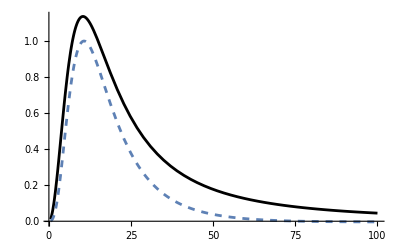

```mathematica
Show[Plot[Re[1/Sqrt[DetTL[10,30,b]]]/(FindMaximum[Re[1/Sqrt[DetTL[10,30,x]]],{x,15}][[1]]),{b,1/2,100},PlotRange->All,PlotStyle->Black],Plot[Re[InvSqtDetTLIdIII[10,30,b]]/(FindMaximum[Re[InvSqtDetTLIdIII[10,30,x]],{x,11}][[1]]),{b,1/2,100},PlotRange->All,PlotStyle->Dashed]]
```

Spacelike Hessian determinant at the identity in I and II

```mathematica
Manipulate[Plot[Re[1/Sqrt[DetSLIdϵ[a0,a1,-b]]],{b,-√((a0-a1)^2/2),0},Epilog->InfiniteLine[{-√((a0-a1)^2/4),0},{0,1}],PlotRange->All],{a0,1,10},{a1,1,30}]
```

Spacelike Hessian determinant for ϑ ≠ 1  in Sector III

```mathematica
InvSqtDet=Table[{0.01*b,1/Sqrt[DetSLϑϵ[10,30,-0.01b+0.01]]},{b,-1414,-1000}];
```

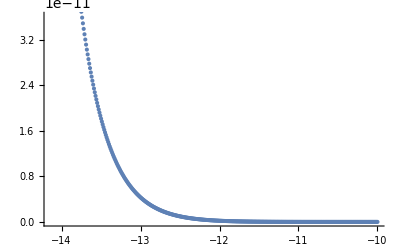

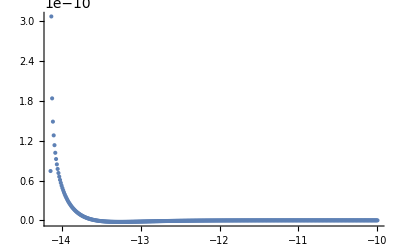

```mathematica
ListPlot[Re[InvSqtDet]]
ListPlot[Table[{InvSqtDet[[i,1]],Im[InvSqtDet[[i,2]]]},{i,1,Length[InvSqtDet]}],PlotRange->All]
```

All Hessian determinants side by side

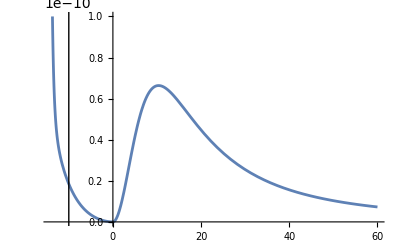

```mathematica
Plot[Piecewise[{{Re[1/Sqrt[DetSLIdϵ[10,30,-b]]]+Re[1/Sqrt[DetSLϑϵ[10,30,-b]]],-√((10-30)^2/2)<b<-√((10-30)^2/4)},{Re[1/Sqrt[DetSLIdϵ[10,30,-b]]],-√((10-30)^2/4)<b<0},{Re[1/Sqrt[DetTL[10,30,b]]],b>0}}],{b,-√((10-30)^2/2),60},Epilog->InfiniteLine[{-√((10-30)^2/4),0},{0,1}],PlotRange->{{-√((10-30)^2/2),60},{0,1*10^-10}}]
```

### Continuum measure

```mathematica
μcontSL[a0_,a1_,b_]:=-1/2 √(3Pi*I(a0+a1))b/(((a0-a1)^2/2-b^2)^(3/4));
μcontTL[a0_,a1_,b_]:=1/2 √(3Pi*I(a0+a1))b/(((a0-a1)^2/2+b^2)^(3/4));
```

Continuum measure in I and II

```mathematica
Manipulate[Plot[{-10^-5 Re[μcontSL[a0,a1,-b]],Re[1/Sqrt[DetSLIdϵ[a0,a1,-b]]]},{b,-√((a0-a1)^2/2),0},Epilog->InfiniteLine[{-√((a0-a1)^2/4),0},{0,1}]],{a0,1,10},{a1,1,10}]
```

Continuum measure in III

```mathematica
Manipulate[Plot[{10^-5 Re[μcontTL[a0,a1,b]],Re[1/Sqrt[DetTL[a0,a1,b]]]},{b,0,50},PlotRange->All],{a0,1,10},{a1,1,10}]
```

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

### Approximating the measure

```mathematica
bsI=Range[10.010381513778155,14.14213562373095,0.010381291733549736];
InvSqtDetRe1030=Table[{b,Re[1/Sqrt[DetSLϑϵ[10,30,b]]]},{b,bsI}];
InvSqtDetIm1030=Table[{b,Im[1/Sqrt[DetSLϑϵ[10,30,b]]]},{b,bsI}];
InvSqtDetReInt1030=Interpolation[InvSqtDetRe1030];
InvSqtDetImInt1030=Interpolation[InvSqtDetIm1030];
Av1030SLId[b_,ϕ0_,ϕ1_,m_]:=Subscript[A, f,sl][b]*(Exp[I*(Subscript[S, I][10,30,b]+Subscript[S, ϕ,sl][10,30,b,ϕ0,ϕ1,m])]/(√DetSLIdϵ[10,30,b]));
Av1030SLϑ[b_,ϕ0_,ϕ1_,m_]:=Subscript[A, f,sl][b]*(InvSqtDetReInt1030[b]+I*InvSqtDetImInt1030[b])*ϑbSL[10,30,b]^4*Exp[-I*(Subscript[S, I][10,30,b]+Subscript[S, ϕ,sl][10,30,b,ϕ0,ϕ1,m])];
```

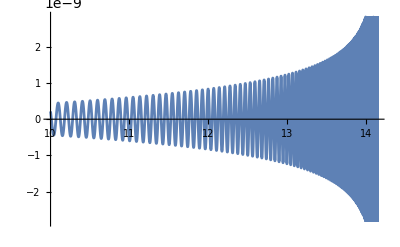

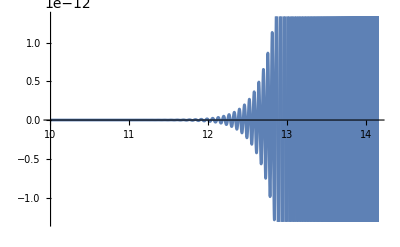

```mathematica
Plot[Re[Av1030SLId[b,2,4,0.05]],{b,10.010381513778155,14.14213562373095},PlotPoints->200]
Plot[Re[Av1030SLϑ[b,2,4,0.05]],{b,10.010381513778155,14.14213562373095},PlotPoints->200]
```

```mathematica
NIntegrate[Av1030SLId[b,2,4,0.05],{b,10.010381513778155,14.14213562373095},Method->"LocalAdaptive"]
```

-8.21256×10^-12+4.05236×10^-12 ⅈ

```mathematica
NIntegrate[Av1030SLϑ[b,2,4,0.05],{b,10.010381513778155,14.14213562373095},Method->"LocalAdaptive"]
```

-1.99034×10^-13-8.5538×10^-13 ⅈ

Measures for varying length l_1

```mathematica
bsIvaryingl1=Table[Array[N[#]&,400,{√((4n)^2/4),√((4n)^2/2)}][[2;;399]],{n,0,20}];
```

```mathematica
InvSqtDetRe10l1=Table[Table[{b,Re[1/Sqrt[DetSLϑϵ[10,10+4(i-1),b]]]},{b,bsIvaryingl1[[i]]}],{i,2,21}];
InvSqtDetIm10l1=Table[Table[{b,Im[1/Sqrt[DetSLϑϵ[10,10+4(i-1),b]]]},{b,bsIvaryingl1[[i]]}],{i,2,21}];
InvSqtDetReInt10l1=Table[Interpolation[InvSqtDetRe10l1[[i]]],{i,1,20}];
InvSqtDetImInt10l1=Table[Interpolation[InvSqtDetIm10l1[[i]]],{i,1,20}];
```

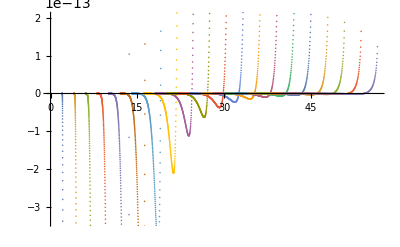

```mathematica
ListPlot[InvSqtDetIm10l1]
```

```mathematica
InvSqtDetReInt10l1[[1]][2.5]
```

1.0508×10^-9

```mathematica
Av10l1SLId[b_,ϕ0_,ϕ1_,m_,n_]:=Subscript[A, f,sl][b]*(Exp[I*(Subscript[S, I][10,10+4n,b]+Subscript[S, ϕ,sl][10,10+4n,b,ϕ0,ϕ1,m])]/(√DetSLIdϵ[10,10+4n,b]));
Av10l1SLϑ[b_,ϕ0_,ϕ1_,m_,n_]:=Subscript[A, f,sl][b]*(InvSqtDetReInt10l1[[n]][b]+I*InvSqtDetImInt10l1[[n]][b])*ϑbSL[10,10+4n,b]^4*Exp[-I*(Subscript[S, I][10,10+4n,b]+Subscript[S, ϕ,sl][10,10+4n,b,ϕ0,ϕ1,m])];
```

## Plots of Hessian, Regge action and dressed amplitude

### Plots for the Hessian

Hessian for ϑ=1 (blue) and ϑ≠1 (black) in Sector I

```mathematica
Manipulate[Plot[Re[InvSqtDetSLI[a0,a1,b]],{b,√((a0-a1)^2/4),√((a0-a1)^2/2)}],{a0,1,100},{a1,1,100}]
```

```mathematica
Manipulate[Show[{Plot[Re[1/Sqrt[DetSL[a0,a1,b]]],{b,√((a0-a1)^2/4),√((a0-a1)^2/2)},PlotStyle->Black],Plot[Re[1/Sqrt[DetSLId[a0,a1,b]]],{b,√((a0-a1)^2/4),√((a0-a1)^2/2)},PlotStyle->Blue]},PlotRange->{{√((a0-a1)^2/4),√((a0-a1)^2/2)},Automatic}],{a0,1,100},{a1,1,100}]
Manipulate[Show[{Plot[Im[1/Sqrt[DetSL[a0,a1,b]]],{b,√((a0-a1)^2/4),√((a0-a1)^2/2)},PlotStyle->Black],Plot[Im[1/Sqrt[DetSLId[a0,a1,b]]],{b,√((a0-a1)^2/4),√((a0-a1)^2/2)},PlotStyle->Blue]},PlotRange->{{√((a0-a1)^2/4),√((a0-a1)^2/2)},Automatic}],{a0,1,100},{a1,1,100}]
```

Visualization that measure tends to zero for lightlike trapezoid

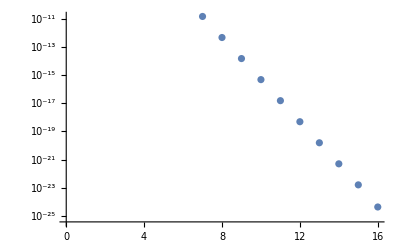

```mathematica
ListLogPlot[Table[N[InvSqtDetSLI[1,2,√((1-2)^2/4)+10^-n]],{n,0,15}]]
```

If the vartheta is added:

```mathematica
Series[ϑbSL[1,2,b]^4,{b,1/2,5}]
Series[InvSqtDetSLI[1,2,b],{b,1/2,5}]
```

16 (b-1/2)^4+64 (b-1/2)^5+O[b-1/2]^6

(b-1/2)^(3/2)/(32 √2 √(ⅈ/(-1+2 b)^3) (-1+2 b)^(3/2))+((33/64+ⅈ/16) (b-1/2)^(5/2))/(√2 √(ⅈ/(-1+2 b)^3) (-1+2 b)^(3/2))+((1115/256+(133 ⅈ)/64) (b-1/2)^(7/2))/(√2 √(ⅈ/(-1+2 b)^3) (-1+2 b)^(3/2))+((10937/512+(3863 ⅈ)/128) (b-1/2)^(9/2))/(√2 √(ⅈ/(-1+2 b)^3) (-1+2 b)^(3/2))+O[b-1/2]^(11/2)

The measure times vartheta diverges as x^(-5/2) for x → 0, where at x = 0, the trapezoid is lightlike.

```mathematica
Manipulate[Plot[Re[1/ϑbSL[a0,a1,b]^4],{b,√((a0-a1)^2/4),√((a0-a1)^2/2)}],{a0,1,10},{a1,1,10}]
```

```mathematica
=1 in Sector
```

ϑ actually leads to a polynomial divergence that cannot be cured with the polynomial decay of the inverse determinant

What happens if we change the definition of vartheta from ϑ = e^φ to ϑ = e^-φ?

```mathematica
Manipulate[Plot[Re[ϑbSL[a0,a1,b]^4/Sqrt[DetSLalt[a0,a1,b]]],{b,√((a0-a1)^2/4),√((a0-a1)^2/2)},PlotStyle->Black,PlotRange->{{√((a0-a1)^2/4),√((a0-a1)^2/2)},All}],{a0,1,100},{a1,1,100}]
```

```mathematica
Series[DetSLalt[1,2,b],{b,1/2,3}]
```

-(3/1024-(3 ⅈ)/1024)/(b-1/2)^16+(7/64-(3 ⅈ)/64)/(b-1/2)^15-(1695/1024+(81 ⅈ)/1024)/(b-1/2)^14+(6601/512+(4071 ⅈ)/512)/(b-1/2)^13-(12155/256+(23161 ⅈ)/256)/(b-1/2)^12-(4629/128-(17229 ⅈ)/32)/(b-1/2)^11+(345817/256-(486659 ⅈ)/256)/(b-1/2)^10-(248475/32-(115301 ⅈ)/32)/(b-1/2)^9+(13962341/512+(74091 ⅈ)/512)/(b-1/2)^8-(2337735/32+(405699 ⅈ)/16)/(b-1/2)^7+(90777041/512+(56160831 ⅈ)/512)/(b-1/2)^6-(112213979/256+(95676661 ⅈ)/256)/(b-1/2)^5+(281232771/256+(309782965 ⅈ)/256)/(b-1/2)^4-(21192427/8+(236991789 ⅈ)/64)/(b-1/2)^3+(1546283635/256+(2741505337 ⅈ)/256)/(b-1/2)^2-(1691497765/128+(3838549267 ⅈ)/128)/(b-1/2)+(28805900255/1024+(84001637473 ⅈ)/1024)-(1843138451/32+218804374 ⅈ) (b-1/2)+(113295020315/1024+(585715992629 ⅈ)/1024) (b-1/2)^2-(99323448181/512+(753962551835 ⅈ)/512) (b-1/2)^3+O[b-1/2]^4

```mathematica
Series[InvSqtDetSLI[1,2,b],{b,1/2,4}]
```

(b-1/2)^(3/2)/(32 √2 √(ⅈ/(-1+2 b)^3) (-1+2 b)^(3/2))+((33/64+ⅈ/16) (b-1/2)^(5/2))/(√2 √(ⅈ/(-1+2 b)^3) (-1+2 b)^(3/2))+((1115/256+(133 ⅈ)/64) (b-1/2)^(7/2))/(√2 √(ⅈ/(-1+2 b)^3) (-1+2 b)^(3/2))+O[b-1/2]^(9/2)

```mathematica
Series[1/Sqrt[DetSLalt[1,2,b]],{b,1/2,9}]
```

(32 (b-1/2)^8)/(√3 √(-(1-ⅈ)/(-1+2 b)^16) (-1+2 b)^8)+((1280/3+(512 ⅈ)/3) (b-1/2)^9)/(√3 √(-(1-ⅈ)/(-1+2 b)^16) (-1+2 b)^8)+O[b-1/2]^10

Hessian for ϑ=1 in Sector II

```mathematica
Manipulate[Plot[{Re[1/DetSLId[a0,a1,b]],Im[1/DetSLId[a0,a1,b]]},{b,0,√((a0-a1)^2/4)},PlotStyle->{Blue,Orange},PlotRange->{{0,√((a0-a1)^2/4)},Automatic}],{a0,1,10},{a1,1,10}]
Manipulate[Plot[{Re[1/Sqrt[DetSLId[a0,a1,b]]],Re[InvSqtDetSLIdII[a0,a1,b]]},{b,0,√((a0-a1)^2/4)},PlotStyle->{Black,{Red,Dashed}},PlotRange->{{0,√((a0-a1)^2/4)},Automatic}],{a0,1,10},{a1,1,10}]
Manipulate[Plot[{Im[1/Sqrt[DetSLId[a0,a1,b]]],Im[InvSqtDetSLIdII[a0,a1,b]]},{b,0,√((a0-a1)^2/4)},PlotStyle->{Black,{Red,Dashed}},PlotRange->{{0,√((a0-a1)^2/4)},Automatic}],{a0,1,10},{a1,1,10}]
```

Plot::plld: Endpoints for b in {b,0,0} must have distinct machine-precision numerical values.

Hessian for ϑ=1 in Sector III

```mathematica
Manipulate[Plot[{Re[1/DetTLId[a0,a1,b]],Im[1/DetTLId[a0,a1,b]]},{b,0,10},PlotStyle->{Blue,Orange},PlotRange->{{0,10},Automatic}],{a0,1,10},{a1,1,10}]
Manipulate[Plot[{Re[1/Sqrt[DetTLId[a0,a1,b]]],Re[1/(Sqrt[-32 ⅈ a0^3 a1^3]Sqrt[((-1-(a0-a1)^2/(4 b^2)) b)^3]Sqrt[ (-(((-2+2 ⅈ) (a0+a1)-(a0-a1)^2/b-4 b) ((a0-a1)^2+(1+ⅈ) (a0+a1) b))/(8 b)-((a0-a1)^2 (-2 b+√(2 (a0-a1)^2+4 b^2))^2)/(16 b^2))^3])]},{b,0,10},PlotStyle->{Black,{Red,Dashed}},PlotRange->{{0,10},Automatic}],{a0,1,10},{a1,1,10}]
Manipulate[Plot[{Im[1/Sqrt[DetTLId[a0,a1,b]]],Im[1/(Sqrt[-32 ⅈ a0^3 a1^3]Sqrt[((-1-(a0-a1)^2/(4 b^2)) b )^3]Sqrt[(-(((-2+2 ⅈ) (a0+a1)-(a0-a1)^2/b-4 b) ((a0-a1)^2+(1+ⅈ) (a0+a1) b))/(8 b)-((a0-a1)^2 (-2 b+√(2 (a0-a1)^2+4 b^2))^2)/(16 b^2))^3])]},{b,0,10},PlotStyle->{Black,{Red,Dashed}},PlotRange->{{0,10},Automatic}],{a0,1,10},{a1,1,10}]
```

Putting I and II side by side

```mathematica
Manipulate[Show[{Plot[Re[1/Sqrt[DetSLId[a0,a1,b]]],{b,√((a0-a1)^2/4),√((a0-a1)^2/2)},PlotStyle->Blue],Plot[Re[InvSqtDetSLIdII[a0,a1,b]],{b,0,√((a0-a1)^2/4)},PlotStyle->Black]},PlotRange->{{0,√((a0-a1)^2/2)},All}],{a0,1,10},{a1,1,10}]
Manipulate[Show[{Plot[Im[1/Sqrt[DetSLId[a0,a1,b]]],{b,√((a0-a1)^2/4),√((a0-a1)^2/2)},PlotStyle->Blue],Plot[Im[InvSqtDetSLIdII[a0,a1,b]],{b,0,√((a0-a1)^2/4)},PlotStyle->Black]},PlotRange->{{0,√((a0-a1)^2/2)},All}],{a0,1,10},{a1,1,10}]
```

### Plots of the Regge action

Sector I

```mathematica
Manipulate[Plot[Piecewise[{{Subscript[S, I][a0,a1,-b],-√((a0-a1)^2/2)<b<-√((a0-a1)^2/4)},{Subscript[S, II][a0,a1,-b],-√((a0-a1)^2/4)<b<0},{Subscript[S, null][a0,a1,b],b==√((a0-a1)^2/4)}}],{b,-√((a0-a1)^2/2),0}],{a0,0,200},{a1,0,200}]
```

```mathematica
Manipulate[Show[{Plot[Subscript[S, I][a0,a1,b],{b,√((a0-a1)^2/4),√((a0-a1)^2/2)}],Plot[Subscript[S, II][a0,a1,b],{b,0,√((a0-a1)^2/4)}]},PlotRange->{{0,√((a0-a1)^2/2)},All}],{a0,0,200},{a1,0,200}]
```

Sector II

```mathematica
Manipulate[Plot[Subscript[S, II][a0,a1,b],{b,0,√((a0-a1)^2/4)},PlotRange->All],{a0,0,200},{a1,0,200}]
```

Plot::plld: Endpoints for b in {b,0,0} must have distinct machine-precision numerical values.

Sector III

```mathematica
Manipulate[ListPlot[Table[Subscript[S, III][a0,a1,b],{b,1/2,100}],PlotRange->All],{a0,0,200},{a1,0,200}]
```

Sector III with matter

```mathematica
Manipulate[ListPlot[Table[Subscript[S, III][a0,a1,b]+Subscript[S, ϕ,tl][a0,a1,b,3,5,0.1],{b,1/2,20}],PlotRange->All],{a0,0,20},{a1,0,30}]
```

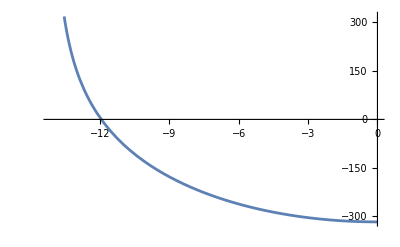

```mathematica
Plot[Subscript[S, ϕ,sl][10,30,-b,2,5,0.1],{b,-√((10-30)^2/2),0}]
```

```mathematica
Subscript[S, ϕ,sl][10,30,11,2,5,0.1]
```

-76.7216

### Integrand of effective path integral

```mathematica
Subscript[A, f,tl][k_]:=2k-1;
Subscript[A, f,sl][s_]:=-EulerGamma/Pi s*Tanh[Pi*s];
(*Subscript[A, v,I][a0_,a1_,b_]:=Subscript[A, f,sl][a0]*Subscript[A, f,sl][a1]*Subscript[A, f,sl][b]*(InvSqtDetSLId[a0,a1,b]*Exp[-I*Subscript[S, I,alt][a0,a1,b]]+(InvSqtDetSLI[a0,a1,b]*Exp[I*Subscript[S, I,alt][a0,a1,b]])/ϑbSL[a0,a1,b]^4); wrong sign of dih. angles here*)
Subscript[A, v,I][a0_,a1_,b_]:=Subscript[A, f,sl][b]*(Exp[I*Subscript[S, I][a0,a1,b]]/(√DetSLIdϵ[a0,a1,b])+(ϑbSL[a0,a1,b]^4*Exp[-I*Subscript[S, I][a0,a1,b]])/(√DetSLϑ[a0,a1,b]));
Subscript[A, v,I,simpl][b_,ϕ0_,ϕ1_,m_]:=(Subscript[A, f,sl][10])^4*(Subscript[A, f,sl][30])^4*(Subscript[A, f,sl][b])^4*(Exp[I*(Subscript[S, I][10,30,b]+Subscript[S, ϕ,sl][10,30,b,ϕ0,ϕ1,m])]/(√DetSLIdϵ[10,30,b])+InvSqtDetSLϑ1030[b]*ϑbSL[10,30,b]^4*Exp[-I*(Subscript[S, I][10,30,b]+Subscript[S, ϕ,sl][10,30,b,ϕ0,ϕ1,m])]);
(*This dressed vertex amplitude for Sector I is with ϑ = e^-φ where ϑ is vartheta and φ is any dihedral angle*)
Subscript[A, v,II][a0_,a1_,b_]:=Subscript[A, f,sl][b]*Exp[I*Subscript[S, II][a0,a1,b]]/(√DetSLIdϵ[a0,a1,b]);
Subscript[A, v,III][a0_,a1_,b_]:=Subscript[A, f,tl][b]*Exp[I*Subscript[S, III][a0,a1,b]]/(√DetTLϵ[a0,a1,b]);
PartSumListAvIII[a0_,a1_,M_]:=Accumulate[Table[Subscript[A, v,III][a0,a1,b/2],{b,1,2M}]]
PartSumListAvIIItReg1[a0_,a1_,M_]:=Accumulate[Table[1/M^3 Subscript[A, v,III][a0,a1,b/2],{b,1,2M}]]
PartSumListAvIIIReg2[a0_,a1_,M_]:=Accumulate[Table[1/M^3 Subscript[A, v,III][a0,a1,b/2]*Exp[-b/(2M)]*Cos[b/(2M)],{b,1,2M}]]
PartSumListIII[a0_,a1_,ϕ0_,ϕ1_,M_]:=Accumulate[Table[Subscript[A, v,III][a0,a1,b/2]*Exp[-Subscript[S, ϕ,tl][a0,a1,b/2,ϕ0,ϕ1]],{b,1,2M}]]
PartSumListIIIReg1[a0_,a1_,ϕ0_,ϕ1_,M_]:=Accumulate[Table[1/M^3 Subscript[A, v,III][a0,a1,b/2]*Exp[-Subscript[S, ϕ,tl][a0,a1,b/2,ϕ0,ϕ1]],{b,1,2M}]]
PartSumListIIIReg2[a0_,a1_,ϕ0_,ϕ1_,M_]:=Accumulate[Table[1/M^3 Exp[-b/(2M)]Cos[b/(2M)]Subscript[A, v,III][a0,a1,b/2]*Exp[-Subscript[S, ϕ,tl][a0,a1,b/2,ϕ0,ϕ1]],{b,1,2M}]]
PartSumListIIIb[a0_,a1_,ϕ0_,ϕ1_,M_]:=Accumulate[Table[b/2*Subscript[A, v,III][a0,a1,b/2]*Exp[-Subscript[S, ϕ,tl][a0,a1,b/2,ϕ0,ϕ1]],{b,1,2M}]]
PartSumListIIIbReg1[a0_,a1_,ϕ0_,ϕ1_,M_]:=Accumulate[Table[1/M^3 b/2*Subscript[A, v,III][a0,a1,b/2]*Exp[-Subscript[S, ϕ,tl][a0,a1,b/2,ϕ0,ϕ1]],{b,1,2M}]]
PartSumListIIIbReg2[a0_,a1_,ϕ0_,ϕ1_,M_]:=Accumulate[Table[1/M^3 Exp[-b/(2M)]Cos[b/(2M)] b/2 Subscript[A, v,III][a0,a1,b/2]*Exp[-Subscript[S, ϕ,tl][a0,a1,b/2,ϕ0,ϕ1]],{b,1,2M}]]
```

```mathematica
Plot[Re[Subscript[A, v,I][10,30,-b]],{b,-√((10-30)^2/2),-√((10-30)^2/4)}]
Manipulate[Plot[Re[Subscript[A, v,II][a0,a1,-b]],{b,-√((a0-a1)^2/4),0}],{a0,1,100},{a1,1,100}]
Manipulate[Show[{ListPlot[Table[{b/2,Re[Subscript[A, v,III][a0,a1,b/2]]},{b,1,100}],PlotStyle->Red],Plot[Re[Subscript[A, v,III][a0,a1,b]],{b,1/2,50}]}],{a0,1,100},{a1,1,100}]
```

-Graphics-

Plot::plld: Endpoints for b in {b,0,0} must have distinct machine-precision numerical values.

Plot::plld: Endpoints for b in {b, 0, 0}
     must have distinct machine-precision numerical values.

Plot::plld: Endpoints for b in {b,0,0} must have distinct machine-precision numerical values.

Plot::plld: Endpoints for b in {b, 0, 0}
     must have distinct machine-precision numerical values.

Plot::plld: Endpoints for b in {b,0,0} must have distinct machine-precision numerical values.

```mathematica
Manipulate[Show[{ListPlot[Table[Re[Subscript[A, v,III][a0,a1,b/2]*Exp[-I*Subscript[S, ϕ,tl][a0,a1,b/2,0,dϕ]]],{b,1,50}],PlotStyle->Red],Plot[Re[Subscript[A, v,III][a0,a1,b/2]*Exp[-I*Subscript[S, ϕ,tl][a0,a1,b/2,0,dϕ]]],{b,1,50}]}],{a0,1,100},{a1,1,100},{dϕ,0,10}]
```

```mathematica
Simplify[Series[Subscript[A, f,sl][a0]*Subscript[A, f,sl][a1]*Subscript[A, f,tl][b]*InvSqtDetTLIdIII[a0,a1,b],{b,Infinity,2}],b>0]
```

-(ⅈ a0 a1 EulerGamma^2 Tanh[a0 π] Tanh[a1 π])/(√2 √(-ⅈ a0^3 a1^3) √((-1+ⅈ) (a0+a1)^3) π^2 b^2)+O[1/b]^3

Dressed measure falls off as 1/b^2

```mathematica
Manipulate[Plot[Piecewise[{{Re[1/Sqrt[DetSLId[a0,a1,-b]]],-√((a0-a1)^2/4)<b<0},{Re[1/Sqrt[DetSLId[a0,a1,-b]]]+Re[1/Sqrt[Detϑsimpl[a0,a1,-b]]],-√((a0-a1)^2/2)<b<-√((a0-a1)^2/4)}}],{b,-√((a0-a1)^2/2),0},Epilog->InfiniteLine[{{-√((a0-a1)^2/4),0},{1,1}}]],{a0,1,10},{a1,1,10}]
```

```mathematica
Manipulate[Plot[Piecewise[{{Re[Subscript[A, v,I][a0,a1,-b]],-√((a0-a1)^2/2)<b<-√((a0-a1)^2/4)},{Re[Subscript[A, v,II][a0,a1,-b]],-√((a0-a1)^2/4)<b<0},{Re[Subscript[A, v,III][a0,a1,b]],b>0}}],{b,-√((a0-a1)^2/2),100},PlotRange->{{-√((a0-a1)^2/2),100},{-10^-8,10^-8}},Epilog->InfiniteLine[{{-√((a0-a1)^2/4),0},{-1,1}}]],{a0,1,100},{a1,1,100}]
```

```mathematica
Manipulate[Plot[Piecewise[{{Re[Subscript[A, v,I,alt][a0,a1,-b]*Exp[-I Subscript[S, ϕ,sl][a0,a1,b,0,1.7]]],-√((a0-a1)^2/2)<b<-√((a0-a1)^2/4)},{Re[Subscript[A, v,II][a0,a1,-b]*Exp[-I Subscript[S, ϕ,sl][a0,a1,b,0,1.7]]],-√((a0-a1)^2/4)<b<0},{Re[Subscript[A, v,III][a0,a1,b]*Exp[-I Subscript[S, ϕ,tl][a0,a1,b,0,1.7]]*Exp[-I*Λ*b]],b>0}}],{b,-√((a0-a1)^2/2),200},PlotRange->{{-√((a0-a1)^2/2),200},{-2*10^-9,2*10^-9}},Epilog->InfiniteLine[{{-√((a0-a1)^2/4),0},{-1,1}}]],{a0,1,100},{a1,1,100},{Λ,0,1}]
```

```mathematica
ZI=NIntegrate[Subscript[A, v,I,alt][10,30,b]*Exp[-I*Subscript[S, ϕ,sl][10,30,b,0,1.7]],{b,√((10-30)^2/2),√((10-30)^2/4)},Method->"LocalAdaptive"]
ZII=NIntegrate[Subscript[A, v,II][10,30,b]*Exp[-I*Subscript[S, ϕ,sl][10,30,b,0,1.7]],{b,√((10-30)^2/4),0},Method->"LocalAdaptive"]
ZIII=Sum[Subscript[A, v,III][10,30,b/2]*Exp[-I*Subscript[S, ϕ,tl][10,30,b/2,0,1.7]],{b,1,10000}]
```

1.17685×10^-13-4.54926×10^-12 ⅈ

5.43804×10^-12-4.33981×10^-12 ⅈ

-3.52081×10^-8+5.66125×10^-8 ⅈ

```mathematica
ZIII=Sum[Subscript[A, v,III][10,30,b/2]*Exp[-I*Subscript[S, ϕ,tl][10,30,b/2,0,1.7]],{b,1,10000}]
```

-3.52081×10^-8+5.66125×10^-8 ⅈ

```mathematica
ZbI=NIntegrate[b*Subscript[A, v,I,alt][10,30,b]*Exp[-I*Subscript[S, ϕ,sl][10,30,b,0,1.7]],{b,√((10-30)^2/2),√((10-30)^2/4)},Method->"LocalAdaptive"]
ZbII=NIntegrate[b*Subscript[A, v,II][10,30,b]*Exp[-I*Subscript[S, ϕ,sl][10,30,b,0,1.7]],{b,√((10-30)^2/4),0},Method->"LocalAdaptive"]
```

1.04011×10^-12-4.54891×10^-11 ⅈ

5.96258×10^-11-4.60865×10^-11 ⅈ

```mathematica
ZbIII=Sum[b/2 Subscript[A, v,III][10,30,b/2]*Exp[-I*Subscript[S, ϕ,tl][10,30,b/2,0,1.7]],{b,1,10000}]
```

-0.000020821-0.0000193952 ⅈ

```mathematica
(ZbI+ZbII+ZbIII)/(ZI+ZII+ZIII)
```

-82.1247+418.912 ⅈ

```mathematica
ZbIII/ZIII
```

-82.11+418.846 ⅈ

## Attempts to compute Z with freezing oscillations

### Identifying saddle points

```mathematica
Manipulate[ListPlot[Table[-Subscript[S, III][a0,a1,b/2]-Subscript[S, ϕ,tl][a0,a1,b/2,0,dϕ,0],{b,1,50}],PlotRange->All],{a0,1,50},{a1,1,50},{dϕ,0,1}]
Manipulate[Show[{ListPlot[Table[Re[Subscript[A, v,III][a0,a1,b/2]*Exp[-I*Subscript[S, ϕ,tl][a0,a1,b/2,0,dϕ,0]]],{b,1,200}],PlotStyle->Red],Plot[Re[Subscript[A, v,III][a0,a1,b/2]*Exp[-I*Subscript[S, ϕ,tl][a0,a1,b/2,0,dϕ,0]]],{b,1,200}]}],{a0,1,50},{a1,1,50},{dϕ,0,1}]
```

```mathematica
FindRoot[(4*(Pi/2-ArcCos[(a0-a1)^2/(4 b^2+(a0-a1)^2)])+D[Subscript[S, ϕ,tl][a0,a1,b,0,dϕ],b]/.{a0->30,a1->50,dϕ->0.85})==0,{b,25}]
```

{b→20.7964}

```mathematica
Table[NSum[(Exp[-b/(2M*50)]Cos[b/(2M*50)]Subscript[A, v,III][a0,a1,b/2]*Exp[-I*Subscript[S, ϕ,tl][a0,a1,b/2,0,dϕ]]/.{a0->30,a1->40,dϕ->0.7}),{b,1,Infinity},NSumTerms->200],{M,10,15}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in b near {b} = {4.81039×10^7}. NIntegrate obtained -6.4988×10^-9-1.29652×10^-9 ⅈ and 1.67673×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in b near {b} = {4.81039×10^7}. NIntegrate obtained -7.8962×10^-9-2.10824×10^-9 ⅈ and 2.6656×10^-14 for the integral and error estimates.

{-3.87609×10^-9+4.24413×10^-9 ⅈ,ComplexInfinity,-4.30502×10^-9+4.008×10^-9 ⅈ,-4.53129×10^-9+3.94585×10^-9 ⅈ,ComplexInfinity,-5.32096×10^-9+3.7639×10^-9 ⅈ}

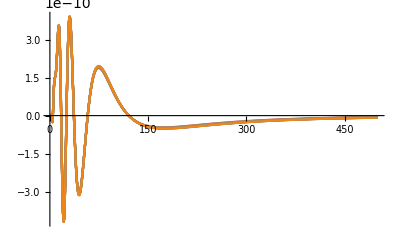

```mathematica
Show[Table[Plot[Re[(Exp[-b/(2M*50)]Cos[b/(2M*50)]Subscript[A, v,III][a0,a1,b/2]*Exp[-I*Subscript[S, ϕ,tl][a0,a1,b/2,0,dϕ]]/.{a0->30,a1->40,dϕ->0.7})],{b,1,500},PlotStyle->ColorData[97,M+1],PlotRange->All],{M,10,20}],PlotLegends->Automatic]
```

```mathematica
Msums=Table[Sum[(Exp[-b/(2M*50)]Cos[b/(2M*50)]Subscript[A, v,III][a0,a1,b/2]*Exp[-I*Subscript[S, ϕ,tl][a0,a1,b/2,0,dϕ]]/.{a0->30,a1->50,dϕ->0.85}),{b,1,1000}],{M,1,30}]
```

{2.60358×10^-9+2.93703×10^-9 ⅈ,2.01763×10^-9+5.72367×10^-9 ⅈ,8.13228×10^-10+6.73695×10^-9 ⅈ,-2.16438×10^-10+7.0876×10^-9 ⅈ,-1.03242×10^-9+7.18255×10^-9 ⅈ,-1.67523×10^-9+7.17704×10^-9 ⅈ,-2.18703×10^-9+7.13297×10^-9 ⅈ,-2.60066×10^-9+7.07596×10^-9 ⅈ,-2.94012×10^-9+7.01685×10^-9 ⅈ,-3.22273×10^-9+6.96011×10^-9 ⅈ,-3.46112×10^-9+6.90747×10^-9 ⅈ,-3.66457×10^-9+6.85938×10^-9 ⅈ,-3.84001×10^-9+6.81575×10^-9 ⅈ,-3.99272×10^-9+6.77625×10^-9 ⅈ,-4.12675×10^-9+6.74049×10^-9 ⅈ,-4.24527×10^-9+6.70808×10^-9 ⅈ,-4.35077×10^-9+6.67862×10^-9 ⅈ,-4.44525×10^-9+6.65179×10^-9 ⅈ,-4.53033×10^-9+6.62729×10^-9 ⅈ,-4.60733×10^-9+6.60483×10^-9 ⅈ,-4.67733×10^-9+6.58421×10^-9 ⅈ,-4.74123×10^-9+6.5652×10^-9 ⅈ,-4.7998×10^-9+6.54765×10^-9 ⅈ,-4.85366×10^-9+6.5314×10^-9 ⅈ,-4.90335×10^-9+6.51631×10^-9 ⅈ,-4.94934×10^-9+6.50226×10^-9 ⅈ,-4.99203×10^-9+6.48917×10^-9 ⅈ,-5.03175×10^-9+6.47693×10^-9 ⅈ,-5.0688×10^-9+6.46547×10^-9 ⅈ,-5.10344×10^-9+6.45472×10^-9 ⅈ}

```mathematica
Msumsb=Table[Sum[((b/2)Exp[-b/(2M*50)]Cos[b/(2M*50)]Subscript[A, v,III][a0,a1,b/2]*Exp[-I*Subscript[S, ϕ,tl][a0,a1,b/2,0,dϕ]]/.{a0->30,a1->50,dϕ->0.85}),{b,1,1000}],{M,1,30}]
```

{8.79928×10^-8+9.66137×10^-8 ⅈ,-8.86143×10^-9+2.48271×10^-7 ⅈ,-1.69082×10^-7+2.86273×10^-7 ⅈ,-3.28394×10^-7+2.58582×10^-7 ⅈ,-4.69516×10^-7+2.05351×10^-7 ⅈ,-5.88965×10^-7+1.47005×10^-7 ⅈ,-6.88681×10^-7+9.16128×10^-8 ⅈ,-7.7194×10^-7+4.17312×10^-8 ⅈ,-8.41881×10^-7-2.27643×10^-9 ⅈ,-9.01128×10^-7-4.08413×10^-8 ⅈ,-9.51767×10^-7-7.46247×10^-8 ⅈ,-9.95431×10^-7-1.04299×10^-7 ⅈ,-1.0334×10^-6-1.30474×10^-7 ⅈ,-1.06666×10^-6-1.5367×10^-7 ⅈ,-1.09602×10^-6-1.74329×10^-7 ⅈ,-1.12209×10^-6-1.92818×10^-7 ⅈ,-1.14539×10^-6-2.09443×10^-7 ⅈ,-1.16633×10^-6-2.24459×10^-7 ⅈ,-1.18524×10^-6-2.38079×10^-7 ⅈ,-1.20239×10^-6-2.50483×10^-7 ⅈ,-1.21801×10^-6-2.6182×10^-7 ⅈ,-1.2323×10^-6-2.72219×10^-7 ⅈ,-1.24542×10^-6-2.81789×10^-7 ⅈ,-1.2575×10^-6-2.90622×10^-7 ⅈ,-1.26866×10^-6-2.98798×10^-7 ⅈ,-1.279×10^-6-3.06387×10^-7 ⅈ,-1.28861×10^-6-3.13449×10^-7 ⅈ,-1.29755×10^-6-3.20035×10^-7 ⅈ,-1.30591×10^-6-3.26192×10^-7 ⅈ,-1.31372×10^-6-3.31959×10^-7 ⅈ}

```mathematica
SequenceLimit[Msumsb]/SequenceLimit[Msums]
```

78.7011+157.443 ⅈ

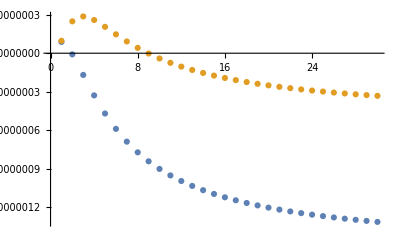

```mathematica
ListPlot[{Re[Msumsb],Im[Msumsb]}]
```

```mathematica
limitsZ=Table[SequenceLimit[PartSumListIIIReg1[30,40,0,0.7,1000+1000*n]],{n,0,5}]
limitsZb=Table[SequenceLimit[PartSumListIIIbReg1[30,40,0,0.7,1000+1000*n]],{n,0,5}]
```

{1.17622×10^-19-4.80783×10^-18 ⅈ,1.19512×10^-20-6.24266×10^-19 ⅈ,2.3394×10^-21-1.87459×10^-19 ⅈ,1.65078×10^-21-7.78721×10^-20 ⅈ,6.8791×10^-22-4.02188×10^-20 ⅈ,3.54165×10^-22-2.33961×10^-20 ⅈ}

{-1.60517×10^-15-3.94774×10^-15 ⅈ,-2.49192×10^-16-7.80175×10^-16 ⅈ,1.0159×10^-17-2.32801×10^-16 ⅈ,-2.55202×10^-17-8.95563×10^-17 ⅈ,-1.28882×10^-17-4.71119×10^-17 ⅈ,-8.02932×10^-18-2.88365×10^-17 ⅈ}

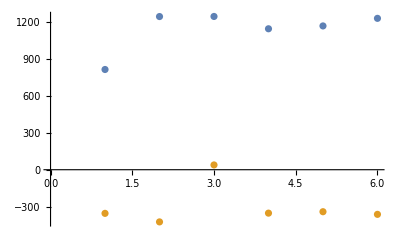

```mathematica
ListPlot[{Re[Table[limitsZb[[i]]/limitsZ[[i]],{i,1,6}]],Im[Table[limitsZb[[i]]/limitsZ[[i]],{i,1,6}]]}]
```

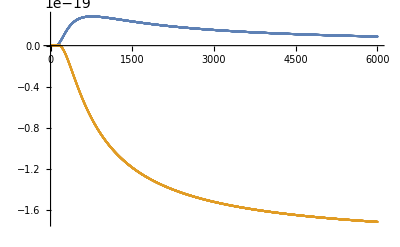

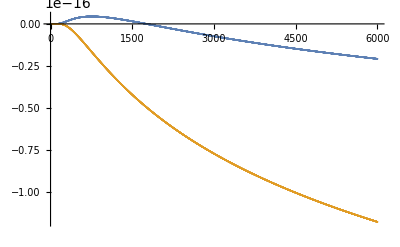

```mathematica
ListPlot[{Re[PartSumListIIIReg1[30,40,0,0.7,3000]],Im[PartSumListIIIReg1[30,40,0,0.7,3000]]}]
ListPlot[{Re[PartSumListIIIbReg1[30,40,0,0.7,3000]],Im[PartSumListIIIbReg1[30,40,0,0.7,3000]]}]
```

### Partition sum and expectation value for a_0=10,a_1=20,ϕ_0=3,ϕ_1=5 in Sector III

```mathematica
Manipulate[ListPlot[Table[(-Subscript[S, III][a0,a1,b]-Subscript[S, ϕ,tl][a0,a1,b,0,dϕ])/.{a0->10,a1->30},{b,1/2,100}],PlotRange->All],{dϕ,0,10}]
```

```mathematica
4*(Pi/2-ArcCos[(a0-a1)^2/(4 b^2+(a0-a1)^2)])+D[Subscript[S, ϕ,tl][a0,a1,b,0,1.7],b]/.{a0->10,a1->30}
FindRoot[-(577.9999999999999 b)/((200+b^2)^(3/2))+4 (π/2-ArcCos[400/(400+4 b^2)])==0,{b,20}]
```

-(578. b)/((200+b^2)^(3/2))+4 (π/2-ArcCos[400/(400+4 b^2)])

{b→20.7964}

Comparing Z for different regulators

```mathematica
PartZ=N[PartSumListIII[10,20,1,2,300]];
PartZReg1=N[PartSumListIIIReg1[10,20,1,2,300]];
PartZReg2=N[PartSumListIIIReg2[10,20,1,2,300]];
```

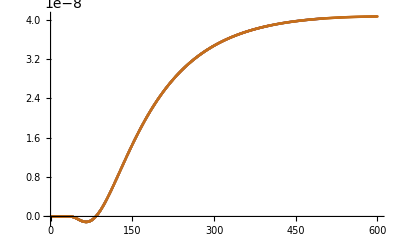

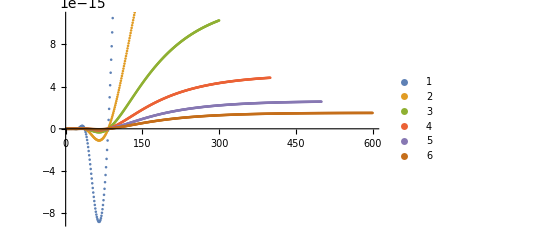

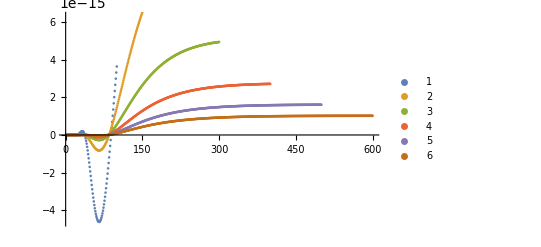

```mathematica
ListPlot[Table[N[Re[PartSumListIII[10,20,1,2,50+50n]]],{n,0,5}]]
ListPlot[Table[N[Re[PartSumListIIIReg1[10,20,1,2,50+50n]]],{n,0,5}],PlotLegends->Automatic]
ListPlot[Table[N[Re[PartSumListIIIReg2[10,20,1,2,50+50n]]],{n,0,5}],PlotLegends->Automatic]
```

Getting limit values of M → ∞

```mathematica
Z=SequenceLimit[PartZ]
ZReg1=SequenceLimit[PartZReg1]
ZReg2=SequenceLimit[PartZReg2]
```

3.31756×10^-8-7.54712×10^-8 ⅈ

1.22401×10^-15-2.79789×10^-15 ⅈ

1.01258×10^-15-7.6698×10^-16 ⅈ

Getting the expectation value of b

```mathematica
PartExpb=N[PartSumListIIIb[10,20,1,2,300]];
PartExpbReg1=N[PartSumListIIIbReg1[10,20,1,2,300]];
PartExpbReg2=N[PartSumListIIIbReg2[10,20,1,2,300]];
```

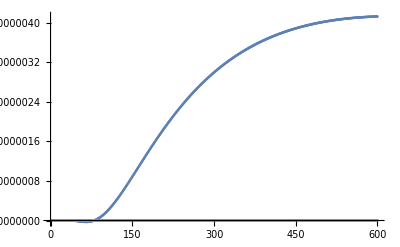

```mathematica
ListPlot[{Re[PartExpb],Re[PartExpbReg1],Re[PartExpbReg2]}]
```

```mathematica
ExpbI=SequenceLimit[PartExpb]
ExpbIReg1=SequenceLimit[PartExpbReg1]
ExpbIReg2=SequenceLimit[PartExpbReg2]
```

-1.7814×10^-6-0.0000312571 ⅈ

-6.4403×10^-14-1.13793×10^-12 ⅈ

9.33024×10^-14-1.47301×10^-13 ⅈ

```mathematica
ExpbI/Z
ExpbIReg1/ZReg1
```

338.395-172.355 ⅈ

332.924-168.665 ⅈ

### Partition sum and expectation value for a_0=10,a_1=20,ϕ_0=3,ϕ_1=5 including Sector I and II

```mathematica
(*NIntegrate[Subscript[A, v,II][10,20,b]*Exp[-I*Subscript[S, ϕ,sl][10,20,b,1,2]],{b,0,5},Exclusions->(b==5),Method->"AdaptiveQuasiMonteCarlo"]
NIntegrate[b^2*Subscript[A, v,II][10,20,b]*Exp[-I*Subscript[S, ϕ,sl][10,20,b,1,2]],{b,0,5},Exclusions->(b==5),Method->"AdaptiveQuasiMonteCarlo"]*)
NIntegrate[Subscript[A, v,I,alt][10,20,b]*Exp[-I*Subscript[S, ϕ,sl][10,20,b,1,3]],{b,5,10/(√2)},Exclusions->{b==10/(√2)},Method->"LocalAdaptive"]
(*NIntegrate[b^2*Subscript[A, v,I][10,20,b]*Exp[-I*Subscript[S, ϕ,sl][10,20,b,1,2]],{b,5,10/(√2)},Exclusions->(b==5),Method->"AdaptiveQuasiMonteCarlo",MinRecursion->20,MaxRecursion->500]*)
```

-2.30281×10^-11-1.71437×10^-10 ⅈ

```mathematica
(-3.3414150643675096*^-9-5.273216877892166*^-10 ⅈ+9.314213482194513*^39+2.164076237576497*^37 ⅈ+-1.7813952468589908*^-6-0.000031257065076168984 ⅈ)/(3.3175591967997243*^-8-7.547117889642238*^-8 ⅈ+-1.3106876484265184*^-10-3.0107014695590344*^-11 ⅈ+3.7256853928777185*^38+8.656304950284823*^35 ⅈ)
```

25.+1.40672×10^-13 ⅈ

-Graphics3D-

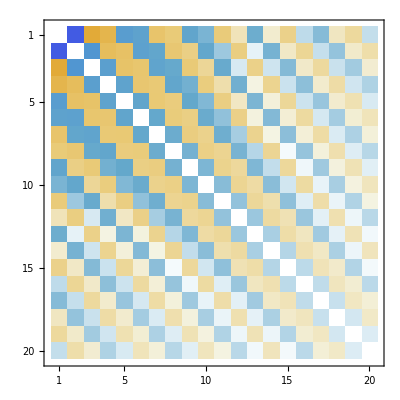

```mathematica
MatrixPlot[%226]
```

Evaluating the timelike partition sum

```mathematica
ResourceFunction["SequenceLimit"][PartSumList[1,2,100],Method->"Wynn]
```

Join::heads: Heads List and If at positions 1 and 3 are expected to be the same.

$Failed[]

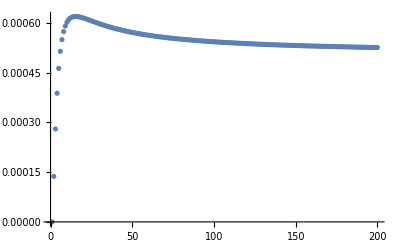

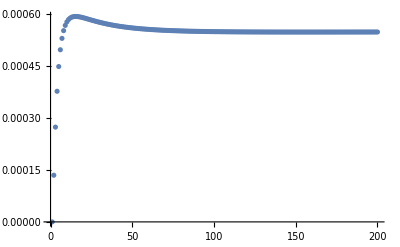

```mathematica
ListPlot[Re[PartSumList[1,2,100]]]
ListPlot[Re[PartSumListReg[1,2,100]]]
```

```mathematica
SequenceLimit[N[Re[PartSumList[1,2,300]]]]
SequenceLimit[N[Re[PartSumListReg[1,2,300]]]]
```

0.000507816

0.000533483

NumericalMath`NSequenceLimit::seqlim: The general form of the sequence could not be determined, and the result may be incorrect.

General::stop: Further output of NumericalMath`NSequenceLimit::seqlim will be suppressed during this calculation.

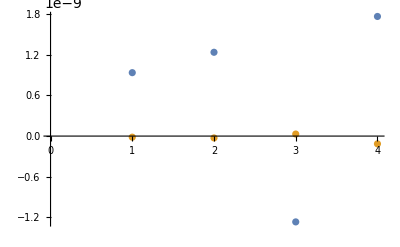

```mathematica
ListPlot[{Table[SequenceLimit[N[Re[PartSumList[10,50,100+50*n]]]],{n,0,3}],Table[SequenceLimit[N[Re[PartSumListReg[10,50,100+50*n]]]],{n,0,3}]}]
```

```mathematica
SequenceLimit[N[Re[PartSumList[1,2,200]]]]
SequenceLimit[N[Re[PartSumListReg[1,2,200]]],Method->"WynnEpsilon"]
```

0.000508771

0.000539656

```mathematica
Subscript[S, ϕ][10,20,201,3,5]
```

S_ϕ[10,20,201,3,5]

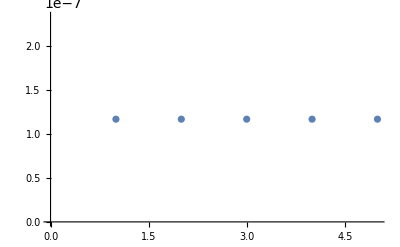

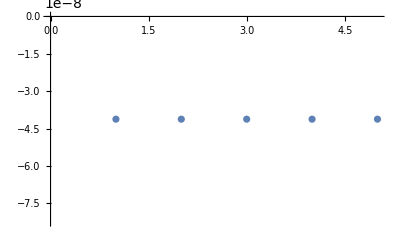

```mathematica
ListPlot[Table[Re[NSum[Subscript[A, v,III][10,20,b/2],{b,1,Infinity},NSumTerms->(100+50*n)]],{n,0,4}]]
ListPlot[Table[Re[NSum[Subscript[A, v,III][10,20,b/2]*Exp[-I*Subscript[S, ϕ,tl][10,20,b/2,3,5]],{b,1,Infinity},NSumTerms->(100+50*n)]],{n,0,4}]]
```

```mathematica
Im[NSum[Subscript[A, v,III][10,20,b/2]*Exp[-I*Subscript[S, ϕ,tl][10,20,b/2,5,3]],{b,1,Infinity},NSumTerms->150]]
```

2.15413×10^-8

```mathematica
4*(Pi/2-ArcCos[(a0-a1)^2/(4 b^2+(a0-a1)^2)])+D[Subscript[S, ϕ,tl][a0,a1,b,3,5],b]/.{a0->10,a1->20};
FindRoot[-(450 b)/((50+b^2)^(3/2))+4 (π/2-ArcCos[100/(100+4 b^2)])==0,{b,5}]
```

{b→3.26302}

```mathematica
NLimit[PartSumList[1,2,M],M->Infinity]
```

Table::iterb: Iterator {b,1,2 M} does not have appropriate bounds.

Table::iterb: Iterator {b+A_(v,III)[1,2,b/2],1+((-1)^(1/4) (-1+b) ⅇ^(-ⅈ (2 b Plus[«2»]-4 ArcSinh[«1»])) EulerGamma^2 Tanh[π] «1»)/(2 √2 √((-1+Times[«2»])^3 b^3) √((-1/4 Plus[«3»] Power[«2»] Plus[«2»]-1/4 Power[«2»] Power[«2»])^3) π^2),2 M+((-1)^(1/4) (-1+b) ⅇ^(-ⅈ (2 b Plus[«2»]-4 ArcSinh[«1»])) EulerGamma^2 Tanh[π] «1»)/(2 √2 √((-1+Times[«2»])^3 b^3) √((-1/4 Plus[«3»] Power[«2»] Plus[«2»]-1/4 Power[«2»] Power[«2»])^3) π^2)} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Table::write: Tag Plus in b+A_(v,III)[1,2,b/2] is Protected.

Table::write: Tag Plus in b+A_(v,III)[1.,2.,b 0.5] is Protected.

General::stop: Further output of Table::write will be suppressed during this calculation.

NLimit::notnum: The expression Table[A_(v,III)[1.,2.,b 0.5],{b+A_(v,III)[1.,2.,b 0.5],1.+((0.00840797+0.00840797 ⅈ) 2.71828^((0.-1. ⅈ) (Times[«3»]+Times[«2»])) (-1.+b))/(√(Plus[«2»]^3 b^3) √((Times[«4»]+Times[«3»])^3)),2.+((0.00840797+0.00840797 ⅈ) 2.71828^((0.-1. ⅈ) (Times[«3»]+Times[«2»])) (-1.+b))/(√(Plus[«2»]^3 b^3) √((Times[«4»]+Times[«3»])^3))}] is not numerical at the point M == 1..

NLimit[Table[A_(v,III)[1,2,b/2],{b+A_(v,III)[1,2,b/2],1+((-1)^(1/4) (-1+b) ⅇ^(-ⅈ (2 b (π/2-ArcCos[1/(1+b^2)])-4 ArcSinh[1/(√(1+b^2))])) EulerGamma^2 Tanh[π] Tanh[2 π])/(2 √2 √((-1-1/b^2)^3 b^3) √((-(((-6+6 ⅈ)-2/b-2 b) (1+(3/2+(3 ⅈ)/2) b))/(4 b)-((-b+√(2+b^2))^2)/(4 b^2))^3) π^2),2 M+((-1)^(1/4) (-1+b) ⅇ^(-ⅈ (2 b (π/2-ArcCos[1/(1+b^2)])-4 ArcSinh[1/(√(1+b^2))])) EulerGamma^2 Tanh[π] Tanh[2 π])/(2 √2 √((-1-1/b^2)^3 b^3) √((-(((-6+6 ⅈ)-2/b-2 b) (1+(3/2+(3 ⅈ)/2) b))/(4 b)-((-b+√(2+b^2))^2)/(4 b^2))^3) π^2)}],M→∞]

```mathematica
ResourceFunction["SequenceLimit"][]
```

Join::heads: Heads List and If at positions 1 and 3 are expected to be the same.

$Failed[]

```mathematica
ResourceSearch["SequenceLimit"]
```

Join::heads: Heads List and If at positions 1 and 3 are expected to be the same.

ResourceSearch::invloc: The specified search location … is invalid, Use a list containing PersistenceLocation objects or URL objects for resource systems.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

Indeterminate

```mathematica
ResourceFunction["SequenceLimit"][Accumulate[Table[(-1)^n/n,{n,1,10}]]]
```

Join::heads: Heads List and If at positions 1 and 3 are expected to be the same.

$Failed[Accumulate[Table[(-1)^n/n,{n,1,10}]]]

```mathematica
NSum[Subscript[A, v,III][1,2,b/2],{b,1,Infinity}]
PartSumList[1,2,100]
ResourceFunction["SequenceLimit"][PartSumList[1,2,100],Method->"WynnEpsilon"]
```

0.000506053-0.00144881 ⅈ

{0,-((-1)^(3/4) ⅇ^(-ⅈ (4 (π/2-ArcCos[1/5])-4 ArcSinh[1/(√5)])) EulerGamma^2 Tanh[π] Tanh[2 π])/(5 √5 ((31/4+(9 ⅈ)/8)-1/16 (-2+√6)^2)^(3/2) π^2),-((-1)^(3/4) ⅇ^(-ⅈ (4 (π/2-ArcCos[1/5])-4 ArcSinh[1/(√5)])) EulerGamma^2 Tanh[π] Tanh[2 π])/(5 √5 ((31/4+(9 ⅈ)/8)-1/16 (-2+√6)^2)^(3/2) π^2)-(3 (-1)^(3/4) √(3/5) ⅇ^(-ⅈ (6 (π/2-ArcCos[1/10])-4 ArcSinh[1/(√10)])) EulerGamma^2 Tanh[π] Tanh[2 π])/(20 ((145/18+2 ⅈ)-1/36 (-3+√11)^2)^(3/2) π^2),-((-1)^(3/4) ⅇ^(-ⅈ (4 (π/2-ArcCos[1/5])-4 ArcSinh[1/(√5)])) EulerGamma^2 Tanh[π] Tanh[2 π])/(5 √5 ((31/4+(9 ⅈ)/8)-1/16 (-2+√6)^2)^(3/2) π^2)-(3 (-1)^(3/4) √(3/5) ⅇ^(-ⅈ (1)) EulerGamma^2 Tanh[π] Tanh[2 π])/(20 ((145/18+2 ⅈ)-1/36 1^2)^(3/2) π^2)-(6 (-1)^(3/4) √(2/17) ⅇ^(-ⅈ (8 (π/2-1)-4 1)) EulerGamma^2 Tanh[π] Tanh[2 π])/(17 ((275/32+(45 ⅈ)/16)-1/64 (1)^2)^(3/2) π^2),192,1,1,1,1}
 |  |  |  |

Join::heads: Heads List and If at positions 1 and 3 are expected to be the same.

$Failed[PartSumList[1,2,100],Method→WynnEpsilon]

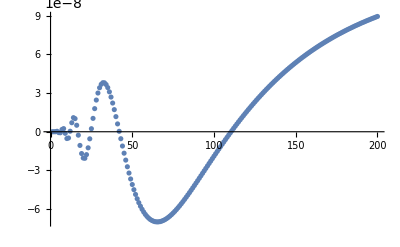

```mathematica
ListPlot[Re[PartSumList[10,20,100]]]
```

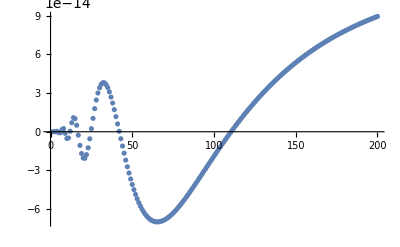

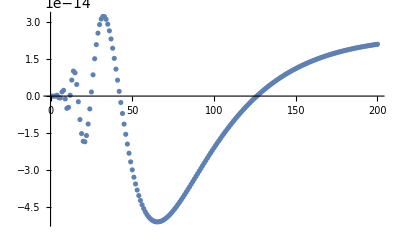

```mathematica
ListPlot[Re[PartSumListReg1[10,20,100]]]
ListPlot[Re[PartSumListReg2[10,20,100]]]
```

```mathematica
ListPlot[Table[N[Re[PartSumList[10,20,50+50n]]],{n,0,5}]]
seq2=N[Re[PartSumListReg1[10,20,300]]];
seq3=N[Re[PartSumListReg2[10,20,300]]];
SequenceLimit[seq1]
SequenceLimit[seq2]
SequenceLimit[seq3]
```

1.21707×10^-7

1.21535×10^-13

2.51364×10^-14

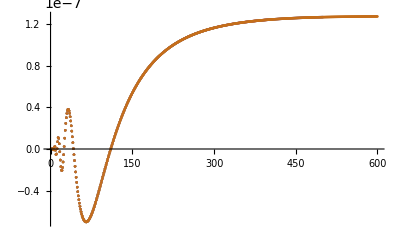

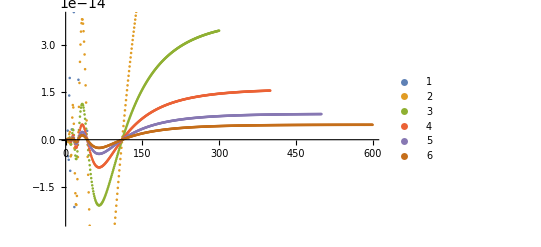

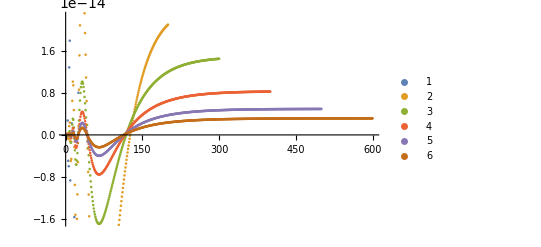

```mathematica
ListPlot[Table[N[Re[PartSumList[10,20,50+50n]]],{n,0,5}]]
ListPlot[Table[N[Re[PartSumListReg1[10,20,50+50n]]],{n,0,5}],PlotLegends->Automatic]
ListPlot[Table[N[Re[PartSumListReg2[10,20,50+50n]]],{n,0,5}],PlotLegends->Automatic]
```

```mathematica
seq2=N[Re[PartSumListReg1[10,20,300]]];
seq3=N[Re[PartSumListReg2[10,20,300]]];
SequenceLimit[seq2]
SequenceLimit[seq3]
```

4.70848×10^-15

3.15226×10^-15

```mathematica
seq3
```

{0.,-2.6233×10^-17,7.05069×10^-18,3.498×10^-16,-6.36132×10^-16,-7.68852×10^-16,1.67582×10^-15,2.3404×10^-15,-1.15569×10^-15,-4.97622×10^-15,-4.58314×10^-15,3.39613×10^-16,6.49277×10^-15,1.01594×10^-14,9.46241×10^-15,4.73056×10^-15,-2.30415×10^-15,-9.53867×10^-15,-1.52357×10^-14,-1.83502×10^-14,-1.8542×10^-14,-1.60207×10^-14,-1.13387×10^-14,-5.20268×10^-15,1.66771×10^-15,8.63×10^-15,1.51652×10^-14,2.08922×10^-14,2.5562×10^-14,2.90407×10^-14,3.12875×10^-14,3.23323×10^-14,3.22551×10^-14,3.11687×10^-14,2.92043×10^-14,2.65007×10^-14,2.31962×10^-14,1.9423×10^-14,1.53037×10^-14,1.0949×10^-14,6.45675×10^-15,1.9116×10^-15,-2.61434×10^-15,-7.06098×10^-15,-1.13792×10^-14,-1.55297×10^-14,-1.94821×10^-14,-2.32137×10^-14,-2.67082×10^-14,-2.99553×10^-14,-3.29491×10^-14,-3.5688×10^-14,-3.81734×10^-14,-4.04095×10^-14,-4.24026×10^-14,-4.41605×10^-14,-4.56924×10^-14,-4.70083×10^-14,-4.81187×10^-14,-4.90348×10^-14,-4.97677×10^-14,-5.03288×10^-14,-5.0729×10^-14,-5.09795×10^-14,-5.10907×10^-14,-5.10732×10^-14,-5.09368×10^-14,-5.06911×10^-14,-5.03451×10^-14,-4.99075×10^-14,-4.93865×10^-14,-4.87897×10^-14,-4.81246×10^-14,-4.73979×10^-14,-4.66161×10^-14,-4.5785×10^-14,-4.49104×10^-14,-4.39975×10^-14,-4.3051×10^-14,-4.20755×10^-14,-4.10751×10^-14,-4.00538×10^-14,-3.9015×10^-14,-3.79621×10^-14,-3.68981×10^-14,-3.58257×10^-14,-3.47476×10^-14,-3.3666×10^-14,-3.25831×10^-14,-3.15008×10^-14,-3.04209×10^-14,-2.9345×10^-14,-2.82746×10^-14,-2.7211×10^-14,-2.61553×10^-14,-2.51087×10^-14,-2.40721×10^-14,-2.30464×10^-14,-2.20323×10^-14,-2.10304×10^-14,-2.00414×10^-14,-1.90658×10^-14,-1.8104×10^-14,-1.71564×10^-14,-1.62234×10^-14,-1.53051×10^-14,-1.44018×10^-14,-1.35136×10^-14,-1.26408×10^-14,-1.17834×10^-14,-1.09414×10^-14,-1.01148×10^-14,-9.30378×10^-15,-8.50816×10^-15,-7.72792×10^-15,-6.96299×10^-15,-6.21327×10^-15,-5.47866×10^-15,-4.75903×10^-15,-4.05423×10^-15,-3.36412×10^-15,-2.68854×10^-15,-2.0273×10^-15,-1.38023×10^-15,-7.47136×10^-16,-1.27825×10^-16,4.77904×10^-16,1.07026×10^-15,1.64945×10^-15,2.21568×10^-15,2.76918×10^-15,3.31015×10^-15,3.83882×10^-15,4.3554×10^-15,4.86012×10^-15,5.3532×10^-15,5.83485×10^-15,6.30529×10^-15,6.76474×10^-15,7.21341×10^-15,7.65152×10^-15,8.07929×10^-15,8.49692×10^-15,8.90462×10^-15,9.30259×10^-15,9.69105×10^-15,1.00702×10^-14,1.04402×10^-14,1.08013×10^-14,1.11537×10^-14,1.14975×10^-14,1.1833×10^-14,1.21603×10^-14,1.24796×10^-14,1.27911×10^-14,1.30949×10^-14,1.33913×10^-14,1.36804×10^-14,1.39624×10^-14,1.42374×10^-14,1.45056×10^-14,1.47671×10^-14,1.50222×10^-14,1.52709×10^-14,1.55133×10^-14,1.57498×10^-14,1.59803×10^-14,1.6205×10^-14,1.64241×10^-14,1.66376×10^-14,1.68458×10^-14,1.70488×10^-14,1.72466×10^-14,1.74393×10^-14,1.76272×10^-14,1.78104×10^-14,1.79888×10^-14,1.81627×10^-14,1.83322×10^-14,1.84973×10^-14,1.86582×10^-14,1.8815×10^-14,1.89677×10^-14,1.91165×10^-14,1.92615×10^-14,1.94027×10^-14,1.95402×10^-14,1.96742×10^-14,1.98047×10^-14,1.99318×10^-14,2.00556×10^-14,2.01761×10^-14,2.02935×10^-14,2.04078×10^-14,2.05191×10^-14,2.06275×10^-14,2.0733×10^-14,2.08357×10^-14,2.09357×10^-14,2.1033×10^-14}

1.27807×10^-7

```mathematica
NSum[Re[Subscript[A, v,III][10,20,b/2]],{b,1,Infinity},Method->"WynnEpsilon",NSumTerms->1200,AccuracyGoal->10,PrecisionGoal->10]
```

NumericalMath`NSequenceLimit::seqlim: The general form of the sequence could not be determined, and the result may be incorrect.

1.19713×10^-7

### Partition sum with non-equidistant spectrum

```mathematica
Manipulate[Plot[Re[Subscript[A, v,III][a0,a1,1/2+Exp[b]]*Exp[-I*Subscript[S, ϕ,tl][a0,a1,1/2+Exp[b],0,dϕ]]],{b,-5,20},PlotRange->All],{a0,1,10},{a1,1,30},{dϕ,0,10}]
```

```mathematica
Table[Sum[N[Re[Subscript[A, v,III][a0,a1,1/2+(200M)/b]*Exp[-I*Subscript[S, ϕ,tl][a0,a1,1/2+(200M)/b,0,dϕ]]]]/.{a0->10,a1->20,dϕ->2},{b,1,2*200M}],{M,1,10}]
```

{1.24007×10^-7,2.48035×10^-7,3.72061×10^-7,4.96086×10^-7,6.20111×10^-7,7.44136×10^-7,8.68162×10^-7,9.92187×10^-7,1.11621×10^-6,1.24024×10^-6}

Saddle point at -3 on the x-axis below

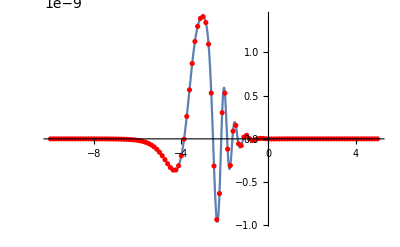

```mathematica
Show[Plot[N[Re[Subscript[A, v,III][a0,a1,1/2+Exp[-b]]*Exp[-I*Subscript[S, ϕ,tl][a0,a1,1/2+Exp[-b],0,dϕ]]]]/.{a0->10,a1->30,dϕ->1.7},{b,-10,5},PlotRange->All],ListPlot[Table[{b/8,N[Re[Subscript[A, v,III][a0,a1,1/2+Exp[-b/8]]*Exp[-I*Subscript[S, ϕ,tl][a0,a1,1/2+Exp[-b/8],0,dϕ]]]]/.{a0->10,a1->30,dϕ->1.7}},{b,-80,40}],PlotRange->All,PlotStyle->Red]]
```

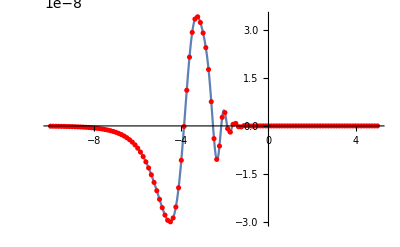

```mathematica
Show[Plot[N[(1/2+Exp[-b])Re[Subscript[A, v,III][a0,a1,1/2+Exp[-b]]*Exp[-I*Subscript[S, ϕ,tl][a0,a1,1/2+Exp[-b],0,dϕ]]]]/.{a0->10,a1->30,dϕ->1.7},{b,-10,5},PlotRange->All],ListPlot[Table[{b/8,N[(1/2+Exp[-b/8])Re[Subscript[A, v,III][a0,a1,1/2+Exp[-b/8]]*Exp[-I*Subscript[S, ϕ,tl][a0,a1,1/2+Exp[-b/8],0,dϕ]]]]/.{a0->10,a1->30,dϕ->1.7}},{b,-80,40}],PlotRange->All,PlotStyle->Red]]
```

```mathematica
Z=Sum[N[Subscript[A, v,III][a0,a1,1/2+Exp[-b/8]]*Exp[-I*Subscript[S, ϕ,tl][a0,a1,1/2+Exp[-b/8],0,dϕ]]]/.{a0->10,a1->30,dϕ->1.7},{b,-80,40}]
Zb=Sum[N[(1/2+Exp[-b/8])*Subscript[A, v,III][a0,a1,1/2+Exp[-b/8]]*Exp[-I*Subscript[S, ϕ,tl][a0,a1,1/2+Exp[-b/8],0,dϕ]]]/.{a0->10,a1->30,dϕ->1.7},{b,-80,40}]
```

5.64384×10^-9+9.81354×10^-9 ⅈ

-1.40298×10^-7+2.26092×10^-7 ⅈ

```mathematica
Zb/Z
```

11.1342+20.6997 ⅈ

```mathematica
1/2+Exp[-19.383500026494147/(-4)]
```

127.715

Saddle point at -0.75 on the x-axis below

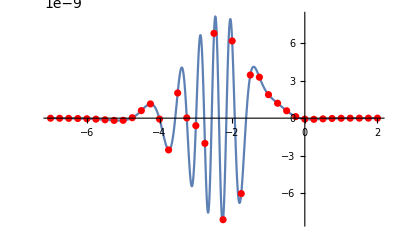

```mathematica
Show[Plot[N[Re[Subscript[A, v,III][a0,a1,1/2+Exp[-b]]*Exp[-I*Subscript[S, ϕ,tl][a0,a1,1/2+Exp[-b],0,dϕ]]]]/.{a0->10,a1->20,dϕ->2},{b,-7,2},PlotRange->All],ListPlot[Table[{b/4,N[Re[Subscript[A, v,III][a0,a1,1/2+Exp[-b/4]]*Exp[-I*Subscript[S, ϕ,tl][a0,a1,1/2+Exp[-b/4],0,dϕ]]]]/.{a0->10,a1->20,dϕ->2}},{b,-28,8}],PlotRange->All,PlotStyle->Red]]
```

```mathematica
Table[Sum[N[Re[Subscript[A, v,III][a0,a1,1/2+Exp[-b/4]]*Exp[-I*Subscript[S, ϕ,tl][a0,a1,1/2+Exp[-b/4],0,dϕ]]]]/.{a0->10,a1->20,dϕ->2},{b,-40,n}],{n,5,30}]
```

{6.99066×10^-9,6.99202×10^-9,6.99388×10^-9,6.9956×10^-9,6.997×10^-9,6.99809×10^-9,6.99893×10^-9,6.99956×10^-9,7.00005×10^-9,7.00041×10^-9,7.00069×10^-9,7.00091×10^-9,7.00107×10^-9,7.0012×10^-9,7.0013×10^-9,7.00137×10^-9,7.00143×10^-9,7.00148×10^-9,7.00151×10^-9,7.00154×10^-9,7.00156×10^-9,7.00158×10^-9,7.00159×10^-9,7.0016×10^-9,7.00161×10^-9,7.00162×10^-9}

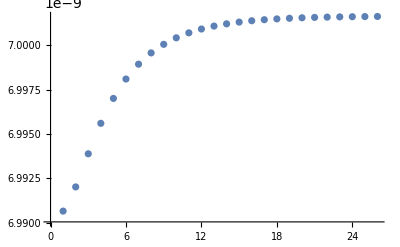

```mathematica
ListPlot[%166]
```

```mathematica
Table[Sum[N[Re[Subscript[A, v,III][a0,a1,1/2+Exp[-b/4]]*Exp[-I*Subscript[S, ϕ,tl][a0,a1,1/2+Exp[-b/4],0,dϕ]]]]/.{a0->10,a1->20,dϕ->2},{b,n,30}],{n,-40,-20}]
```

{7.00162×10^-9,7.00162×10^-9,7.00163×10^-9,7.00165×10^-9,7.00169×10^-9,7.00174×10^-9,7.00183×10^-9,7.00199×10^-9,7.00226×10^-9,7.00272×10^-9,7.00353×10^-9,7.00494×10^-9,7.00744×10^-9,7.01189×10^-9,7.01991×10^-9,7.03439×10^-9,7.06046×10^-9,7.10675×10^-9,7.18632×10^-9,7.31419×10^-9,7.49252×10^-9}

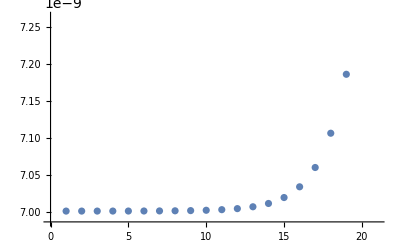

```mathematica
ListPlot[%169]
```

We find satisfactory convergence for a lower cutoff n=-30 and upper cutoff n=30

Expectation value of b

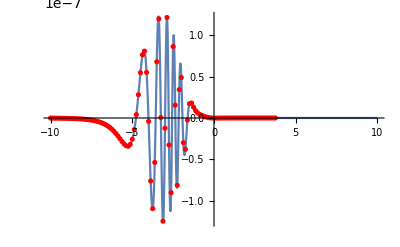

```mathematica
Show[Plot[N[Re[(1/2+Exp[-b])Subscript[A, v,III][a0,a1,1/2+Exp[-b]]*Exp[-I*Subscript[S, ϕ,tl][a0,a1,1/2+Exp[-b],0,dϕ]]]]/.{a0->10,a1->20,dϕ->2},{b,-10,10},PlotRange->All],ListPlot[Table[{b/8,N[Re[(1/2+Exp[-b/8])Subscript[A, v,III][a0,a1,1/2+Exp[-b/8]]*Exp[-I*Subscript[S, ϕ,tl][a0,a1,1/2+Exp[-b/8],0,dϕ]]]]/.{a0->10,a1->20,dϕ->2}},{b,-80,30}],PlotRange->All,PlotStyle->Red]]
```

```mathematica
Z=Sum[N[Re[Subscript[A, v,III][a0,a1,1/2+Exp[-b/8]]*Exp[-I*Subscript[S, ϕ,tl][a0,a1,1/2+Exp[-b/8],0,dϕ]]]]/.{a0->10,a1->30,dϕ->1.7},{b,-80,80}]
Zb=Sum[N[(1/2+Exp[-b/8])Re[Subscript[A, v,III][a0,a1,1/2+Exp[-b/8]]*Exp[-I*Subscript[S, ϕ,tl][a0,a1,1/2+Exp[-b/8],0,dϕ]]]]/.{a0->10,a1->20,dϕ->2},{b,-80,80}]
```

## Introducing a mass

### Mass dependence of strut length solution

```mathematica
Manipulate[Plot[(Subscript[S, III][a0,a1,b]+Subscript[S, ϕ,tl][a0,a1,b,ϕ1,ϕ1+2,10^logm]/.{a0->10,a1->30}),{b,1/2,50}],{ϕ1,0,5},{logm,-5,5}]
```

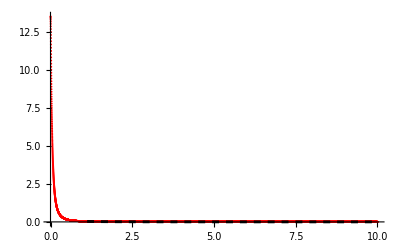

```mathematica
bsolsmass=Table[{10^-3*n,b/.FindRoot[(4*(Pi/2-ArcCos[(a0-a1)^2/(4 b^2+(a0-a1)^2)])+D[Subscript[S, ϕ,tl][a0,a1,b,2,4,10^-3*n],b]/.{a0->10,a1->30})==0,{b,14}]},{n,1,10^4}];
Show[{ListPlot[bsolsmass,PlotStyle->Red],Plot[a*x^-2/.{a->0.04},{x,10^-3,10},PlotStyle->{Black,Dashed}]}]
```

The relation of classical struts and the mass is b ~ 1/m^2. The proportionality factor depends on the ϕ’s and on the a’s

```mathematica
FindRoot[(4*(Pi/2-ArcCos[(a0-a1)^2/(4 b^2+(a0-a1)^2)])+D[Subscript[S, ϕ,tl][a0,a1,b,2,4,0],b]/.{a0->10,a1->30})==0,{b,1}]
```

{b→13.5358}

### Mass-dependent expectation value in Sector III with a_0= 10, a_1 = 30, ϕ_0 = 2, ϕ_1= 4

```mathematica
bsolsmass[[50]]
```

{1/20,5.8332}

```mathematica
Manipulate[Plot[b/2 Re[Subscript[A, v,III][a0,a1,b/2]*Exp[I*Subscript[S, ϕ,tl][a0,a1,b/2,2,4,10^-3*n]]]/.{a0->10,a1->30},{b,1,400}],{n,0.11,10^4}]
```

3.66884×10^-8+1.43853×10^-8 ⅈ

3.66884×10^-8+1.43853×10^-8 ⅈ

2.2208×10^-7+6.4764×10^-8 ⅈ

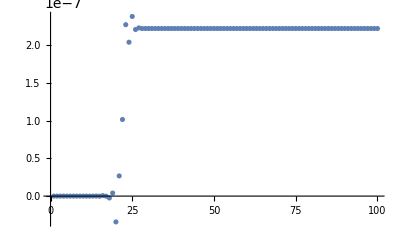

NumericalMath`NSequenceLimit::seqlim: The general form of the sequence could not be determined, and the result may be incorrect.

2.2208×10^-7+6.4764×10^-8 ⅈ

```mathematica
SequenceLimit[Accumulate[Table[N[(Subscript[A, v,III][a0,a1,b/2]*Exp[I*Subscript[S, ϕ,tl][a0,a1,b/2,2,4,10^-3*n]]/.{a0->10,a1->30,n->50})],{b,1,100}]],Method->"WynnEpsilon"]
NSum[(Subscript[A, v,III][a0,a1,b/2]*Exp[I*Subscript[S, ϕ,tl][a0,a1,b/2,2,4,10^-3*n]]/.{a0->10,a1->30,n->50}),{b,1,Infinity}]
SequenceLimit[Accumulate[Table[N[(b/2*Subscript[A, v,III][a0,a1,b/2]*Exp[I*Subscript[S, ϕ,tl][a0,a1,b/2,2,4,10^-3*n]]/.{a0->10,a1->30,n->50})],{b,1,100}]],Method->"WynnEpsilon"]
ListPlot[Table[Re[SequenceLimit[Accumulate[Table[N[(b/2*Subscript[A, v,III][a0,a1,b/2]*Exp[I*Subscript[S, ϕ,tl][a0,a1,b/2,2,4,10^-3*n]]/.{a0->10,a1->30,n->50})],{b,1,M}]],Method->"WynnEpsilon"]],{M,1,100}]]
NSum[(b/2*Subscript[A, v,III][a0,a1,b/2]*Exp[I*Subscript[S, ϕ,tl][a0,a1,b/2,2,4,10^-3*n]]/.{a0->10,a1->30,n->50}),{b,1,Infinity}]
```

The expectation value from the timelike path integral yields a value close to the classical one, b = 5.8332! The relative error is 0.1%

```mathematica
ZmassIII=Table[SequenceLimit[Accumulate[Table[N[(Subscript[A, v,III][a0,a1,b/2]*Exp[I*Subscript[S, ϕ,tl][a0,a1,b/2,2,4,10*10^-3*n]]/.{a0->10,a1->30})],{b,1,100}]],Method->"WynnEpsilon"],{n,1,10}]
ZbmassIII=Table[SequenceLimit[Accumulate[Table[N[(b/2*Subscript[A, v,III][a0,a1,b/2]*Exp[I*Subscript[S, ϕ,tl][a0,a1,b/2,2,4,10*10^-3*n]]/.{a0->10,a1->30})],{b,1,100}]],Method->"WynnEpsilon"],{n,1,10}]
```

{-2.92867×10^-8-1.81712×10^-8 ⅈ,-8.9695×10^-10-2.21002×10^-8 ⅈ,7.98391×10^-9-1.11123×10^-8 ⅈ,8.37996×10^-9-8.06047×10^-10 ⅈ,2.09476×10^-9+4.72644×10^-9 ⅈ,-3.05963×10^-9+8.49106×10^-10 ⅈ,6.62576×10^-10-1.83855×10^-9 ⅈ,-3.61316×10^-8+2.25983×10^-8 ⅈ,-1.09256×10^-8-1.79132×10^-8 ⅈ,-1.08987×10^-8+5.31377×10^-9 ⅈ}

{-3.72345×10^-7-1.81566×10^-7 ⅈ,-2.70015×10^-8-2.20486×10^-7 ⅈ,5.89747×10^-8-9.68626×10^-8 ⅈ,5.71122×10^-8-1.01178×10^-8 ⅈ,1.44602×10^-8+2.6179×10^-8 ⅈ,-1.45116×10^-8+5.6383×10^-9 ⅈ,1.87389×10^-9-7.98071×10^-9 ⅈ,-9.69915×10^-7+5.89133×10^-7 ⅈ,-1.57138×10^-7-2.45529×10^-7 ⅈ,-1.1395×10^-7+5.40439×10^-8 ⅈ}

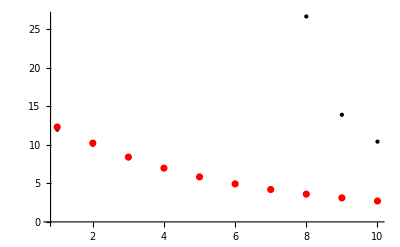

```mathematica
bexpvalsmassIII=Table[ZbmassIII[[i]]/ZmassIII[[i]],{i,1,10}];
ListPlot[{Re[bexpvalsmassIII[[1;;10]]],Table[bsolsmass[[10n,2]],{n,1,10}]},PlotRange->All,PlotStyle->{{Black,PointSize[Large],Opacity[1]},{Red}}]
```

Good agreement for small masses. Larger masses seem to require a refined spectrum

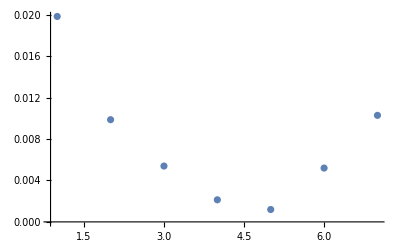

```mathematica
ListPlot[Table[(Abs[Re[bexpvalsmass[[i]]]-bsolsmass[[10*i,2]]])/bsolsmass[[10*i,2]],{i,1,7}],PlotRange->All]
```

Relative error small in the region where mass is not too small and too large

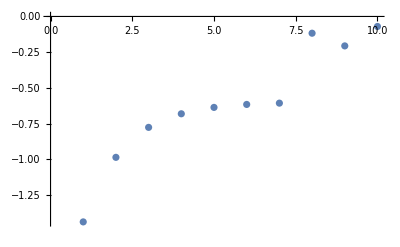

```mathematica
ListPlot[Im[bexpvalsmass]]
```

Imaginary part seems to converge to a certain value for larger masses

```mathematica
NSum[(b/2*Subscript[A, v,III][a0,a1,b/2]*Exp[I*Subscript[S, ϕ,tl][a0,a1,b/2,2,4,10^-3*n]]/.{a0->10,a1->30,n->0.1}),{b,1,Infinity},NSumTerms->100,Method->"WynnEpsilon"]/NSum[(Subscript[A, v,III][a0,a1,b/2]*Exp[I*Subscript[S, ϕ,tl][a0,a1,b/2,2,4,10^-3*n]]/.{a0->10,a1->30,n->0.1}),{b,1,Infinity},NSumTerms->100,Method->"WynnEpsilon"]
FindRoot[(4*(Pi/2-ArcCos[(a0-a1)^2/(4 b^2+(a0-a1)^2)])+D[Subscript[S, ϕ,tl][a0,a1,b,2,4,10^-3*n],b]/.{a0->10,a1->30,n->0.1})==0,{b,14}]
```

NumericalMath`NSequenceLimit::seqlim: The general form of the sequence could not be determined, and the result may be incorrect.

13.0709-1.91662 ⅈ

```mathematica
{b->13.53569069238456}
```

```mathematica
(13.53569069238456-13.070885579830666)/13.53569069238456
```

0.0343392

```mathematica
NSum[(b/2*Subscript[A, v,III][a0,a1,b/2]*Exp[I*Subscript[S, ϕ,tl][a0,a1,b/2,2,4,10^-3*n]]/.{a0->10,a1->30,n->0.01}),{b,1,Infinity},NSumTerms->100,Method->"WynnEpsilon"]/NSum[(Subscript[A, v,III][a0,a1,b/2]*Exp[I*Subscript[S, ϕ,tl][a0,a1,b/2,2,4,10^-3*n]]/.{a0->10,a1->30,n->0.01}),{b,1,Infinity},NSumTerms->100,Method->"WynnEpsilon"]
FindRoot[(4*(Pi/2-ArcCos[(a0-a1)^2/(4 b^2+(a0-a1)^2)])+D[Subscript[S, ϕ,tl][a0,a1,b,2,4,10^-3*n],b]/.{a0->10,a1->30,n->0.01})==0,{b,14}]
```

NumericalMath`NSequenceLimit::seqlim: The general form of the sequence could not be determined, and the result may be incorrect.

13.0707-1.91769 ⅈ

{b→13.5358}

```mathematica
(13.535842066846781-13.070695511810023)/13.535842066846781
```

0.0343641

The expectation value converges in the limit m → 0 to a value that is close the classical value. Therefore, we have the situation where lim_(m→0^+) b(m)≠b(m=0). The relative error of classical value and expectation value is still small with ~3%.

### Refining the spectrum

For the given boundary data, the expectation value deviates from classical value for masses m = 0.08. We suspect this to arise from a spectrum that is too coarse to capture the saddle point

```mathematica
ZmassRef=Table[NSum[(Subscript[A, v,III][a0,a1,b/20]*Exp[I*Subscript[S, ϕ,tl][a0,a1,b/20,2,4,10^-3*(10*n)]]/.{a0->10,a1->30}),{b,1,Infinity},NSumTerms->100,Method->"WynnEpsilon"],{n,8,20}]
ZbmassRef=Table[NSum[(b/20 Subscript[A, v,III][a0,a1,b/20]*Exp[I*Subscript[S, ϕ,tl][a0,a1,b/20,2,4,10^-3*(10*n)]]/.{a0->10,a1->30}),{b,1,Infinity},NSumTerms->100,Method->"WynnEpsilon"],{n,8,20}]
```

NumericalMath`NSequenceLimit::seqlim: The general form of the sequence could not be determined, and the result may be incorrect.

General::stop: Further output of NumericalMath`NSequenceLimit::seqlim will be suppressed during this calculation.

{2.14176×10^-9+1.21111×10^-9 ⅈ,-1.28249×10^-9-4.89154×10^-10 ⅈ,6.46215×10^-10+4.28916×10^-10 ⅈ,-1.84396×10^-10-4.05128×10^-10 ⅈ,-1.09669×10^-10+2.35729×10^-10 ⅈ,1.54777×10^-10+9.0674×10^-13 ⅈ,-1.5603×10^-11-9.26902×10^-11 ⅈ,-5.79517×10^-11+5.82232×10^-12 ⅈ,-7.0037×10^-12+3.61494×10^-11 ⅈ,1.82189×10^-11+1.52218×10^-11 ⅈ,1.5386×10^-11-2.58721×10^-12 ⅈ,7.02116×10^-12-7.73148×10^-12 ⅈ,1.82657×10^-12-6.87749×10^-12 ⅈ}

NumericalMath`NSequenceLimit::seqlim: The general form of the sequence could not be determined, and the result may be incorrect.

General::stop: Further output of NumericalMath`NSequenceLimit::seqlim will be suppressed during this calculation.

{8.57086×10^-9+3.14348×10^-9 ⅈ,-4.38442×10^-9-7.89069×10^-10 ⅈ,2.06872×10^-9+8.14409×10^-10 ⅈ,-7.00409×10^-10-8.96476×10^-10 ⅈ,-1.0377×10^-10+5.88798×10^-10 ⅈ,3.10453×10^-10-8.8973×10^-11 ⅈ,-8.1895×10^-11-1.59526×10^-10 ⅈ,-9.3054×10^-11+4.25002×10^-11 ⅈ,9.29474×10^-12+5.91871×10^-11 ⅈ,3.40154×10^-11+1.17309×10^-11 ⅈ,1.89245×10^-11-1.14771×10^-11 ⅈ,4.72587×10^-12-1.31004×10^-11 ⅈ,-1.26572×10^-12-8.86326×10^-12 ⅈ}

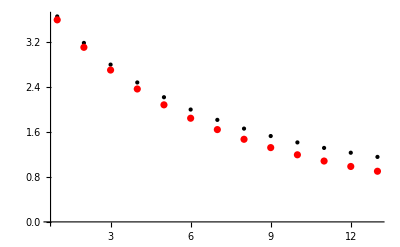

```mathematica
bexpvalsmassRef=Table[ZbmassRef[[i]]/ZmassRef[[i]],{i,1,13}];
ListPlot[{Re[bexpvalsmassRef[[1;;13]]],Table[bsolsmass[[10n,2]],{n,8,20}]},PlotRange->All,PlotStyle->{{Black,PointSize[Large],Opacity[1]},{Red}}]
```

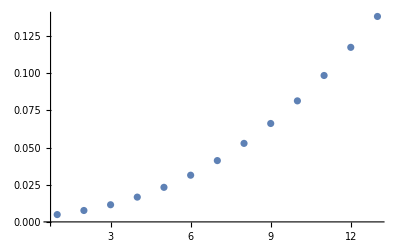

```mathematica
ListPlot[Table[(Abs[Re[bexpvalsmassRef[[i]]]-bsolsmass[[10*(7+i),2]]])/bsolsmass[[10*i,2]],{i,1,13}],PlotRange->All]
```

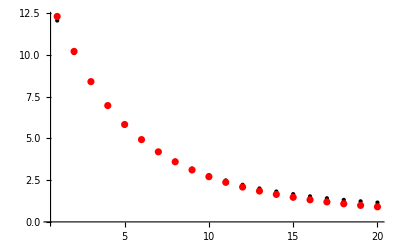

```mathematica
Join[bexpvalsmass[[1;;7]],bexpvalsmassRef];
ListPlot[{Re[Join[bexpvalsmass[[1;;7]],bexpvalsmassRef]],Table[bsolsmass[[10n,2]],{n,1,20}]},PlotRange->All,PlotStyle->{{Black,PointSize[Large],Opacity[1]},{Red}}]
```

Combined results of unrefined and refined (for n  > 8)

### Saddle points in I and II

```mathematica
Manipulate[Plot[Subscript[S, III][a0,a1,b]+Subscript[S, ϕ,tl][a0,a1,b,2,4,10^logm]/.{a0->10,a1->30},{b,1/2,20}],{logm,-5,5}]
```

```mathematica
Manipulate[Plot[Piecewise[{{Subscript[S, I][a0,a1,b]+Subscript[S, ϕ,sl][a0,a1,b,2,4,10^logm]/.{a0->10,a1->30},√((10-30)^2/4)<b<√((10-30)^2/2)},{Subscript[S, II][a0,a1,b]+Subscript[S, ϕ,sl][a0,a1,b,2,4,10^logm]/.{a0->10,a1->30},0<b<√((10-30)^2/4)}}],{b,0,√((10-30)^2/2)},Epilog->InfiniteLine[{{√((10-30)^2/4),0},{-1,1}}]],{logm,-5,5}]
```

```mathematica
Manipulate[Plot[Subscript[S, I][a0,a1,-b]+Subscript[S, ϕ,sl][a0,a1,-b,2,4,10^logm]/.{a0->10,a1->30},{b,-√((10-30)^2/2),-√((10-30)^2/4)}],{logm,-5,3}]
```

### Including Sectors I and II

```mathematica
Manipulate[Plot[Re[Piecewise[{{Subscript[A, v,I,simpl][-b,2,4,10^-2*n],-√((10-30)^2/2)<b<-√((10-30)^2/4)},{Subscript[A, v,II][10,30,-b]*Exp[I*Subscript[S, ϕ,sl][10,30,-b,2,4,10^-2*n]],-√((10-30)^2/4)<b<0}}]],{b,-√((10-30)^2/2),0},Epilog->InfiniteLine[{{-√((10-30)^2/4),0},{-1,1}}]],{n,1,10}]
```

There is a new problem arising: the kinetic term of the scalar field diverges as the Euclidean configurations are approached. Let’s first consider Sector II:

```mathematica
NIntegrate[Subscript[A, v,II][10,30,-b]*Exp[I*Subscript[S, ϕ,sl][10,30,-b,2,4,10^-3(10*3)]],{b,-√((10-30)^2/4),0}]
```

-5.66486×10^-12+1.13059×10^-11 ⅈ

```mathematica
ZmassII=Table[NIntegrate[Subscript[A, v,II][10,30,-b]*Exp[I*Subscript[S, ϕ,sl][10,30,-b,2,4,10^-3(10*n)]],{b,-√((10-30)^2/4),0}],{n,1,10}];
ZbmassII=Table[NIntegrate[(-b)Subscript[A, v,II][10,30,-b]*Exp[I*Subscript[S, ϕ,sl][10,30,-b,2,4,10^-3(10*n)]],{b,-√((10-30)^2/4),0}],{n,1,10}];
(*bexpvalsmassIIandIII=Table[(ZbmassII+Zbmass)[[i]]/(Zmass+ZmassII)[[i]],{i,1,10}];*)
```

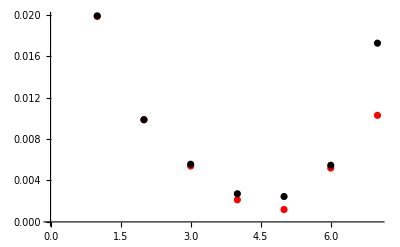

```mathematica
Show[{ListPlot[Table[(Abs[Re[bexpvalsmass[[i]]]-bsolsmass[[10*i,2]]])/bsolsmass[[10*i,2]],{i,1,7}],PlotStyle->Red],ListPlot[Table[(Abs[Re[bexpvalsmassIIandIII[[i]]]-bsolsmass[[10*i,2]]])/bsolsmass[[10*i,2]],{i,1,7}],PlotStyle->Black]}]
```

The deviations are a signature of a saddle point that can be present in Sector II for certain mass values

```mathematica
Table[Abs[Re[bexpvalsmassIIandIII[[i]]-bexpvalsmass[[i]]]]/Re[bexpvalsmassIIandIII[[i]]],{i,1,10}]
```

{0.000180788,0.000116428,0.000589358,0.00685827,0.0153922,0.00957185,0.0293785,0.0000895943,0.0000836529,0.0000547322}

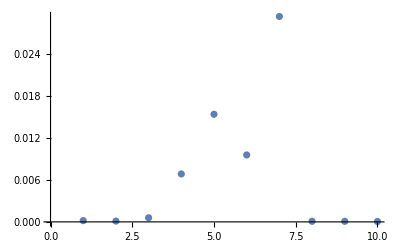

```mathematica
ListPlot[{0.0001807880513017232,0.00011642762278823651,0.0005893580782644416,0.0068582671006395274,0.015392178091081543,0.009571850124941524,0.02937846923738023,0.00008959434590725006,0.00008365292390453275,0.0000547322267917954}]
```

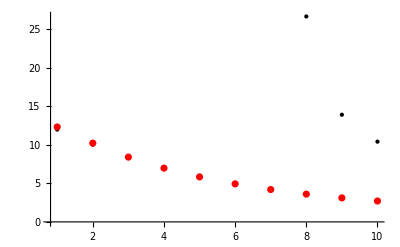

```mathematica
bexpvalsmassIIandIII=Table[(ZbmassII+ZbmassIII)[[i]]/(ZmassIII+ZmassII)[[i]],{i,1,10}];
ListPlot[{Re[bexpvalsmassIIandIII[[1;;10]]],Table[bsolsmass[[10n,2]],{n,1,10}]},PlotRange->All,PlotStyle->{{Black,PointSize[Large],Opacity[1]},{Red}}]
```

```mathematica
bexpvalsmassIIandIII
bexpvalsmass
```

{12.1034-1.345 ⅈ,10.1594-0.906399 ⅈ,8.39854-0.698033 ⅈ,6.98524-0.601033 ⅈ,5.86386-0.553381 ⅈ,4.96683-0.52863 ⅈ,4.24303-0.517223 ⅈ,26.5292+0.0218457 ⅈ,14.0269-0.143814 ⅈ,10.6023+0.0423733 ⅈ}

{12.1035-1.345 ⅈ,10.1594-0.906398 ⅈ,8.39855-0.698053 ⅈ,6.98527-0.601089 ⅈ,5.86374-0.553297 ⅈ,4.96659-0.528719 ⅈ,4.24302-0.516765 ⅈ,26.5292+0.0218137 ⅈ,14.0269-0.14383 ⅈ,10.6023+0.0423692 ⅈ}

```mathematica
NIntegrate[Subscript[A, v,I,simpl][-b,2,4,10^-3(10*5)],{b,-√((10-30)^2/2),-√((10-30)^2/4)},Exclusions->{b==-√((10-30)^2/2)},Method->"QuasiMonteCarlo"]
```

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained -8.22856×10^7-1.5974×10^8 ⅈ and 1.74603×10^8 for the integral and error estimates.

-8.22856×10^7-1.5974×10^8 ⅈ

```mathematica
ZmassI=Table[NIntegrate[Subscript[A, v,I,simpl][-b,2,4,10^-3(10*n)],{b,-√((10-30)^2/2),-√((10-30)^2/4)},Exclusions->{b==-√((10-30)^2/2)},Method->"LocalAdaptive"],{n,1,10}];
ZbmassI=Table[NIntegrate[(-b)Subscript[A, v,I,simpl][-b,2,4,10^-3(10*n)],{b,-√((10-30)^2/2),-√((10-30)^2/4)},Exclusions->{b==-√((10-30)^2/2)},Method->"LocalAdaptive"],{n,1,10}];(*ZmassII=Table[NIntegrate[Subscript[A, v,II][10,30,-b]*Exp[I*Subscript[S, ϕ,sl][10,30,-b,2,4,10^-3(10*n)]],{b,-√((10-30)^2/4),0},Method->"LocalAdaptive"],{n,1,10}];
ZbmassII=Table[NIntegrate[(-b)Subscript[A, v,II][10,30,-b]*Exp[I*Subscript[S, ϕ,sl][10,30,-b,2,4,10^-3(10*n)]],{b,-√((10-30)^2/4),0},Method->"LocalAdaptive"],{n,1,10}];*)
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in b near {b} = {-14.1421356237309504954561254915878895065770447542119992732898547}. NIntegrate obtained -4.96693×10^55-4.41529×10^55 ⅈ and 6.67031×10^55 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in b near {b} = {-14.1421}. NIntegrate obtained -626742.-120215. ⅈ and 0.520017 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in b near {b} = {-14.1421}. NIntegrate obtained -1.78054×10^6-362180. ⅈ and 1.08885 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

$Aborted

$Aborted

```mathematica
NIntegrate[Subscript[A, v,I][10,30,-b]*Exp[I*Subscript[S, ϕ,sl][10,30,-b,2,4,10^-3(10*5)]],{b,-√((10-30)^2/2),-√((10-30)^2/4)},Exclusions->{b==-√((10-30)^2/2)},Method->"LocalAdaptive"]
```

$Aborted

```mathematica
ZI={-2.0401409555394965*10^-12+9.689298945794866*10^-13 I,-1.0040659688041546*10^-12+1.90360629465268310^-12 I,-2.000088199785839*10^-12-4.773637265420149*10^-13 I}
ZbI={-2.1262819370133024*10^-11+9.689298945794866*10^-13 I,-1.101275514806401*10^-11+1.903606294652683*10^-12 I,-2.0353345058091616*10^-11-4.773637265420149*10^-13 I}
```

{-2.04014×10^-12+9.6893×10^-13 ⅈ,-1.00407×10^-12+0.000441646 ⅈ,-2.00009×10^-12-4.77364×10^-13 ⅈ}

{-2.12628×10^-11+9.6893×10^-13 ⅈ,-1.10128×10^-11+1.90361×10^-12 ⅈ,-2.03533×10^-11-4.77364×10^-13 ⅈ}

```mathematica
Zbtot=ZbI+ZbmassII[[4;;6]]+ZbmassIII[[4;;6]]
Ztot=ZI+ZmassII[[4;;6]]+ZmassIII[[4;;6]]
bexpvalsmasstot=Table[Zbtot[[i]]/Ztot[[i]],{i,1,3}]
```

{5.71921×10^-8-1.01718×10^-8 ⅈ,1.44933×10^-8+2.6083×10^-8 ⅈ,-1.44321×10^-8+5.65599×10^-9 ⅈ}

{8.38814×10^-9-8.1132×10^-10 ⅈ,2.09769×10^-9+0.000441651 ⅈ,-3.05119×10^-9+8.50506×10^-10 ⅈ}

{6.87121-0.548037 ⅈ,0.0000590581-0.0000328159 ⅈ,4.86843-0.496646 ⅈ}

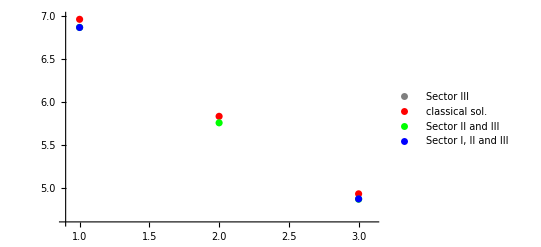

```mathematica
ListPlot[{Re[bexpvalsmassIII[[4;;6]]],Table[bsolsmass[[10n,2]],{n,4,6}],Re[bexpvalsmassIIandIII[[4;;6]]],Re[bexpvalsmasstot[[1;;3]]]},PlotRange->{{0.9,3.1},{4.6,7}},PlotStyle->{{Black,PointSize[Large],Opacity[0.5]},{Red},{Green},{Blue}},PlotLegends->{"Sector III","classical sol.","Sector II and III", "Sector I, II and III"}]
```

### Strut expectation value for varying a_1

```mathematica
Manipulate[Plot[Re[Subscript[A, v,III][a0,10+n,b/2]*Exp[I*Subscript[S, ϕ,tl][a0,10+n,b/2,2,4,0.05]]]/.{a0->10},{b,1,200},PlotRange->All],{n,0,20}]
```

```mathematica
ZIII=Table[SequenceLimit[Accumulate[Table[N[(Subscript[A, v,III][a0,21+0.1n,b/2]*Exp[I*Subscript[S, ϕ,tl][a0,21+0.1n,b/2,2,4,0.05]]/.{a0->10})],{b,1,50}]],Method->"WynnEpsilon"],{n,0,20}];
ZbIII=Table[SequenceLimit[Accumulate[Table[N[(b/2*Subscript[A, v,III][a0,21+0.1n,b/2]*Exp[I*Subscript[S, ϕ,tl][a0,21+0.1n,b/2,2,4,0.05]]/.{a0->10})],{b,1,50}]],Method->"WynnEpsilon"],{n,0,20}];
```

```mathematica
bsolsa=Table[{(21+0.01n),b/.FindRoot[(4*(Pi/2-ArcCos[(a0-a1)^2/(4 b^2+(a0-a1)^2)])+D[Subscript[S, ϕ,tl][a0,a1,b,2,4,0.05],b]/.{a0->10,a1->(21+0.01n)})==0,{b,8.2}]},{n,0,200}];
```

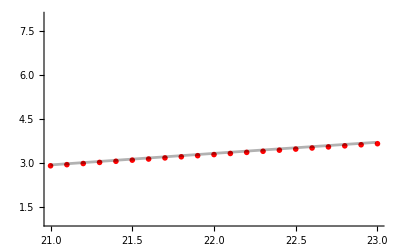

```mathematica
Show[{ListPlot[Re[Table[{21+0.1(i-1),ZbIII[[i]]/ZIII[[i]]},{i,1,21}]],PlotStyle->{Red,PointSize[0.01]}],ListPlot[bsolsa[[1;;200]],PlotStyle->{Black,Opacity[0.3]},Joined->True]},PlotRange->{{21,23},{1,8}}]
```

```mathematica
bsolsa[[1]]
ZbIII[[1]]/ZIII[[1]]
```

{60.,8.25258}

8.21581-0.459959 ⅈ

## Effective spin foam computation

### Effective spin foam integrand

```mathematica
Subscript[AmplESF, I][a0_,a1_,b_,ϕ0_,ϕ1_,m_]:=μcontSL[a0,a1,b]*Exp[I*(Subscript[ComplexS, I][a0,a1,b]+Subscript[S, ϕ,sl][a0,a1,b,ϕ0,ϕ1,m])];
Subscript[AmplESF, II][a0_,a1_,b_,ϕ0_,ϕ1_,m_]:=μcontSL[a0,a1,b]*Exp[I*(Subscript[ComplexS, II][a0,a1,b]+Subscript[S, ϕ,sl][a0,a1,b,ϕ0,ϕ1,m])];
Subscript[AmplESF, III][a0_,a1_,b_,ϕ0_,ϕ1_,m_]:=μcontTL[a0,a1,b]*Exp[I*(Subscript[S, III][a0,a1,b]+Subscript[S, ϕ,tl][a0,a1,b,ϕ0,ϕ1,m])];
```

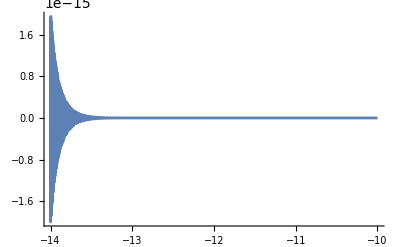

```mathematica
Plot[Re[Subscript[AmplESF, I][10,30,-b,2,4,0.05]],{b,-14,-10},PlotPoints->1000,PlotRange->All]
```

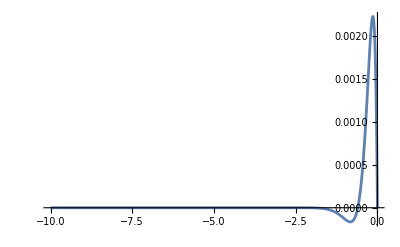

```mathematica
Plot[Re[Subscript[AmplESF, II][10,30,-b,2,4,0.05]],{b,-10,0},PlotPoints->1000,PlotRange->All]
```

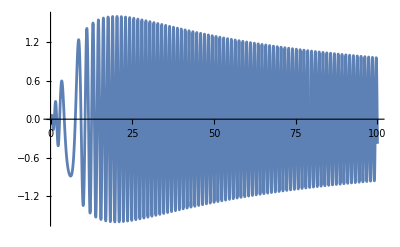

```mathematica
Plot[Re[Subscript[AmplESF, III][10,30,b,2,4,0.05]],{b,0,100},PlotPoints->1000,PlotRange->All]
```

### Strut expectation value in III

For varying edge length:

```mathematica
ZIIIESF=Table[SequenceLimit[Accumulate[Table[N[(Subscript[AmplESF, III][a0,10+4n,b/2,2,4,0.05]/.{a0->10})],{b,1,60}]],Method->"WynnEpsilon"],{n,0,20}];
ZbIIIESF=Table[SequenceLimit[Accumulate[Table[N[(b/2 Subscript[AmplESF, III][a0,10+4n,b/2,2,4,0.05]/.{a0->10})],{b,1,60}]],Method->"WynnEpsilon"],{n,0,20}];
ZbsqIIIESF=Table[SequenceLimit[Accumulate[Table[N[((b/2)^2 Subscript[AmplESF, III][a0,10+4n,b/2,2,4,0.05]/.{a0->10})],{b,1,60}]],Method->"WynnEpsilon"],{n,0,20}];
bsolsaESF=Table[{(10+0.4n),b/.FindRoot[(4*(Pi/2-ArcCos[(a0-a1)^2/(4 b^2+(a0-a1)^2)])+D[Subscript[S, ϕ,tl][a0,a1,b,2,4,0.05],b]/.{a0->10,a1->(10+0.4n)})==0,{b,0.1}]},{n,0,200}];
```

Works very well and super fast!

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

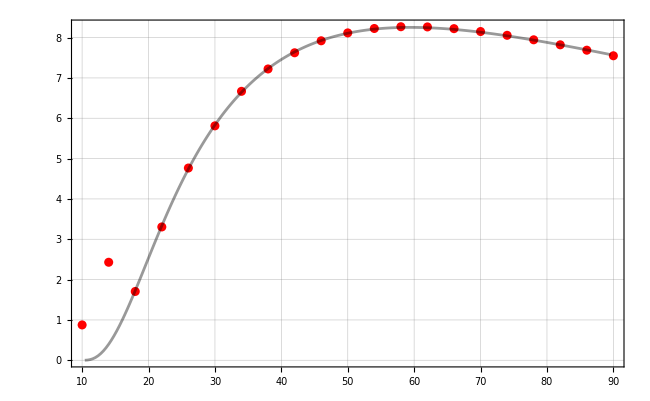

```mathematica
Show[{ListPlot[Re[Table[{10+4(i-1),ZbIIIESF[[i]]/ZIIIESF[[i]]},{i,1,21}]],PlotStyle->{Red,PointSize[0.01]},PlotRange->All],ListPlot[bsolsaESF[[2;;200]],PlotStyle->{Black,Opacity[0.4]},PlotRange->All,Joined->True]},Frame->True,GridLines->{Table[10i,{i,1,9}],Table[i,{i,0,8}]},FrameLabel->{{Style[MaTeX["\mathfrak{Re}\{<m>_{\mathrm{III}}\}", Magnification->2.5],FontSize->16],"-"},{Style[MaTeX["l_1",Magnification->2.5],FontSize->16],"+"}},ImageSize->650,ImagePadding->{{90,0},{70,1}},FrameTicksStyle->Directive[FontSize->16],PlotRange->All]
```

For  varying  mass:

```mathematica
ZIIImESF=Table[SequenceLimit[Accumulate[Table[N[(Subscript[AmplESF, III][a0,a1,b/2,2,4,10^-3(1+4n)]/.{a0->10,a1->30})],{b,1,60}]],Method->"WynnEpsilon"],{n,0,20}];
ZbIIImESF=Table[SequenceLimit[Accumulate[Table[N[(b/2 Subscript[AmplESF, III][a0,a1,b/2,2,4,10^-3(1+4n)]/.{a0->10,a1->30})],{b,1,60}]],Method->"WynnEpsilon"],{n,0,20}];
ZbsqIIImESF=Table[SequenceLimit[Accumulate[Table[N[((b/2)^2 Subscript[AmplESF, III][a0,a1,b/2,2,4,10^-3(1+4n)]/.{a0->10,a1->30})],{b,1,60}]],Method->"WynnEpsilon"],{n,0,20}];
bsolsm=Table[{10^-4(10+4n),b/.FindRoot[(4*(Pi/2-ArcCos[(a0-a1)^2/(4 b^2+(a0-a1)^2)])+D[Subscript[S, ϕ,tl][a0,a1,b,2,4,10^-4(10+4n)],b]/.{a0->10,a1->30})==0,{b,13.1}]},{n,0,200}];
```

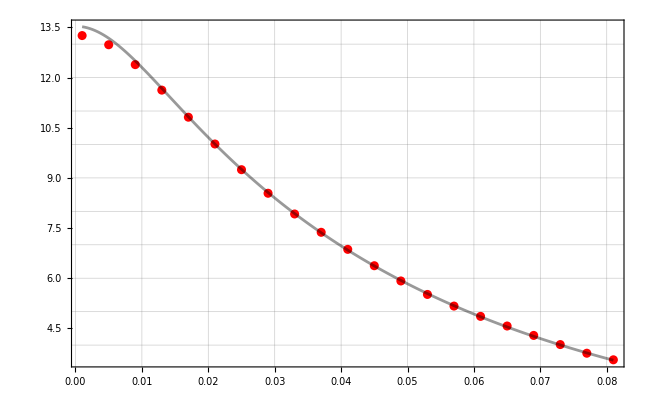

```mathematica
Show[{ListPlot[Re[Table[{10^-3*(1+4(i-1)),ZbIIImESF[[i]]/ZIIImESF[[i]]},{i,1,21}]],PlotStyle->{Red,PointSize[0.01]},PlotRange->All],ListPlot[bsolsm[[1;;201]],PlotStyle->{Black,Opacity[0.4]},PlotRange->All,Joined->True]},Frame->True,GridLines->{Table[0.01i,{i,0,8}],Table[i,{i,0,14}]},FrameLabel->{{Style[MaTeX["\mathfrak{Re}\{<m>_{\mathrm{III}}\}", Magnification->2.5],FontSize->16],""},{Style[MaTeX["\mu",Magnification->2.5],FontSize->16],""}},ImageSize->650,ImagePadding->{{90,0},{70,1}},FrameTicksStyle->Directive[FontSize->16],PlotRange->All]
```

Same here: super fast and less numerical struggle. Is it the complicated Hessian?

### Including I and II

```mathematica
ZESFI=Table[NIntegrate[Subscript[AmplESF, I][10,30,-b,2,4,0.005n],{b,-√((10-30)^2/2),-√((10-30)^2/4)},Exclusions->{b==-√((10-30)^2/2)},Method->"LocalAdaptive"],{n,1,10}];
ZbESFI=Table[NIntegrate[b*Subscript[AmplESF, I][10,30,-b,2,4,0.005n],{b,-√((10-30)^2/2),-√((10-30)^2/4)},Exclusions->{b==-√((10-30)^2/2)},Method->"LocalAdaptive"],{n,1,10}];
```

Numerical integration for the b^2 expectation value is complicated in Mathematica. We therefore perform the computation in Julia and import the results hereafter:

```mathematica
ZImESFpre=Import["/ssd/ri47hud/Projects/3d Cosmology/codes/data/ZIm_ESF.csv"];
ZbsqImESFpre=Import["/ssd/ri47hud/Projects/3d Cosmology/codes/data/ZbsqIm_ESF.csv"];
ZImESF=Table[ZImESFpre[[2]][[i]]+I*ZImESFpre[[3]][[i]],{i,1,21}];
ZbsqImESF=Table[ZbsqImESFpre[[2]][[i]]+I*ZbsqImESFpre[[3]][[i]],{i,1,21}];
```

```mathematica
ZIImESF=Table[NIntegrate[Subscript[AmplESF, II][10,30,b,2,4,10^-3(1+4n)],{b,0,√((10-30)^2/4)},Method->"LocalAdaptive"],{n,0,20}];
ZbsqIImESF=Table[NIntegrate[-b^2 Subscript[AmplESF, II][10,30,b,2,4,10^-3(1+4n)],{b,0,√((10-30)^2/4)},Method->"LocalAdaptive"],{n,0,20}];
```

## Including bulk slices

### Continuum solutions

Friedmann equations in the gauge N = 1

```mathematica
comovingsols=Table[NDSolve[{ϕ''[t]+3 a'[t]/a[t] ϕ'[t]+(0.01n)^2 ϕ[t]==0,(a'[t]/a[t])^2==1/2((ϕ'[t])^2+(0.01n)^2 ϕ[t]^2),a[0]==2,ϕ[0]==2,ϕ[100]==4},{a,ϕ},{t,0,100}],{n,1,10}];
```

Power::infy: Infinite expression 1/(√0.) encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/(√0.) encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/(√0.) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NDSolve::berr: The scaled boundary value residual error of 1.42881×10^9 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

NDSolve::berr: The scaled boundary value residual error of 2.01724×10^7 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

NDSolve::berr: The scaled boundary value residual error of 2.93508×10^7 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

General::stop: Further output of NDSolve::berr will be suppressed during this calculation.

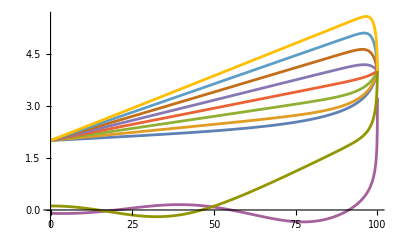

```mathematica
Plot[Evaluate[Table[ϕ[t]/.comovingsols[[n,1]],{n,1,10}]],{t,0,100}]
```

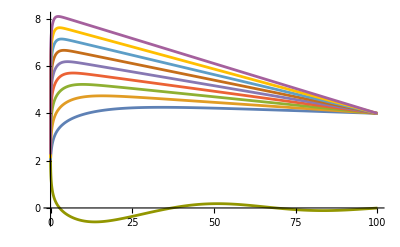

```mathematica
Plot[Evaluate[Table[ϕ[t]/.comovingsols[[n,2]],{n,1,10}]],{t,0,100}]
```

Monotonicity of the scalar field depends on the branch and on the relation between m and ϕ_0-ϕ_2. Here, the evolution is monotonic for m < 0.06 in the first branch and at a lower mass for the second branch.

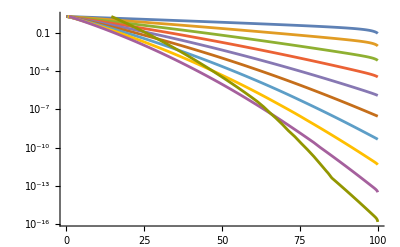

```mathematica
LogPlot[Evaluate[Table[a[t]/.comovingsols[[n,1]],{n,1,10}]],{t,0,100},PlotRange->{{0,100},{0,2}}]
```

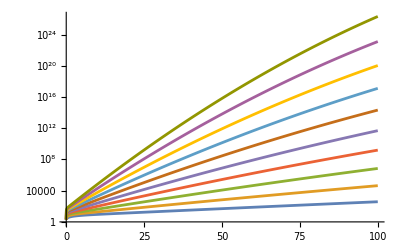

```mathematica
LogPlot[Evaluate[Table[a[t]/.comovingsols[[n,2]],{n,1,10}]],{t,0,100}]
```

Second branch is the expanding branch while first branch is contracting

Friedman equations in harmonic gauge N = a^3

```mathematica
harmonicsols=NDSolve[{ϕ''[t]+(0.01n)^2 a[t]^6 ϕ[t]==0,(a'[t]/a[t])^2==1/2((ϕ'[t])^2+(0.01n)^2 ϕ[t]^2),a[0]==2,ϕ[0]==2,ϕ[100]==4},{a,ϕ},{t,0,100}]
```

Power::infy: Infinite expression 1/(√0.) encountered.

Infinity::indet: Indeterminate expression 0. n^2 ComplexInfinity encountered.

Power::infy: Infinite expression 1/(√0.) encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

NDSolve[{0.0001 n^2 a[t]^6 ϕ[t]+ϕ''[t]==0,a'[t]^2/a[t]^2==1/2 (0.0001 n^2 ϕ[t]^2+ϕ'[t]^2),a[0]==2,ϕ[0]==2,ϕ[100]==4},{a,ϕ},{t,0,100}]

### Finding discrete classical solutions

```mathematica
w[a0_,a1_,b_]:=(a0+a1)^2/(8 √((a0-a1)^2/2+b^2));
M[a0_,a1_,b_,m_]:=m^2/4*Subscript[Vol3, tl][a0,a1,b]
ϕsol[a0_,a1_,a2_,b0_,b1_,ϕ0_,ϕ2_,m_]:=(ϕ0*w[a0,a1,b0]+ϕ2*w[a1,a2,b1])/(w[a0,a1,b0]+w[a1,a2,b1]-M[a0,a1,b0,m]-M[a1,a2,b1,m]);
Subscript[S, tot][a0_,a1_,a2_,b0_,b1_,ϕ0_,ϕ1_,ϕ2_,m_]:=Subscript[S, III][a0,a1,b0]+Subscript[S, III][a1,a2,b1]+Subscript[S, ϕ,tl][a0,a1,b0,ϕ0,ϕ1,m]+Subscript[S, ϕ,tl][a1,a2,b1,ϕ1,ϕ2,m](*careful: do not form variation since the solution of ϕ1 has been injected*)
dStotda1[a0_,a1_,a2_,b0_,b1_,ϕ0_,ϕ2_,m_]:=(4 ArcSinh[(a0-a1)/(√((a0-a1)^2+4 b0^2))]-4 ArcSinh[(a1-a2)/(√((a1-a2)^2+4 b1^2))]+1/(12 √2)((3 (a0-a1) (a0+a1)^2 (ϕ0-ϕ1)^2)/(((a0-a1)^2+2 b0^2)^(3/2))+(6 (a0+a1) (ϕ0-ϕ1)^2)/(√((a0-a1)^2+2 b0^2))+((a0^3-a1^3) m^2 (ϕ0^2+ϕ1^2))/(√((a0-a1)^2+2 b0^2))-(a0+2 a1) √((a0-a1)^2+2 b0^2) m^2 (ϕ0^2+ϕ1^2)-(3 (a1-a2) (a1+a2)^2 (ϕ1-ϕ2)^2)/(((a1-a2)^2+2 b1^2)^(3/2))+(6 (a1+a2) (ϕ1-ϕ2)^2)/(√((a1-a2)^2+2 b1^2))-((a1^3-a2^3) m^2 (ϕ1^2+ϕ2^2))/(√((a1-a2)^2+2 b1^2))-(2 a1+a2) √((a1-a2)^2+2 b1^2) m^2 (ϕ1^2+ϕ2^2)))/.{ϕ1->ϕsol[a0,a1,a2,b0,b1,ϕ0,ϕ2,m]};
dStotdb0[a0_,a1_,a2_,b0_,b1_,ϕ0_,ϕ2_,m_]:=(4 (π/2-ArcCos[(a0-a1)^2/((a0-a1)^2+4 b0^2)])-(b0 (3 (a0+a1)^2 (ϕ0-ϕ1)^2+(a0^2+a0 a1+a1^2) ((a0-a1)^2+2 b0^2) m^2 (ϕ0^2+ϕ1^2)))/(24 (1/2 (a0-a1)^2+b0^2)^(3/2)))/.{ϕ1->ϕsol[a0,a1,a2,b0,b1,ϕ0,ϕ2,m]};dStotdb1[a0_,a1_,a2_,b0_,b1_,ϕ0_,ϕ2_,m_]:=(4 (π/2-ArcCos[(a1-a2)^2/((a1-a2)^2+4 b1^2)])-(b1 (3 (a1+a2)^2 (ϕ1-ϕ2)^2+(a1^2+a1 a2+a2^2) ((a1-a2)^2+2 b1^2) m^2 (ϕ1^2+ϕ2^2)))/(24 (1/2 (a1-a2)^2+b1^2)^(3/2)))/.{ϕ1->ϕsol[a0,a1,a2,b0,b1,ϕ0,ϕ2,m]};
```

```mathematica
FindRoot[{dStotda1[a0,a1,a2,b0,b1,2,ϕ2,m]==0,dStotdb0[a0,a1,a2,b0,b1,2,ϕ2,m]==0,dStotdb1[a0,a1,a2,b0,b1,2,ϕ2,m]==0}/.{a0->10,a2->30,ϕ2->4.0,m->10^-2},{{a1,17},{b0,7},{b1,8}}, WorkingPrecision->20]
```

FindRoot::precw: The precision of the argument function (…) is less than WorkingPrecision (20.).

{a1→17.268230899854599393,b0→3.9415073911523056687,b1→11.015937763259090151}

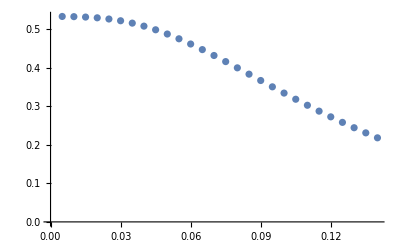

```mathematica
ListPlot[Table[{0.005*n,b0/.slicesols[[n]]},{n,1,28}]]
```

```mathematica
slicesols[[10]]
```

{a1→24.7505,b0→0.487377,b1→0.637503}

```mathematica
dStotda1[10,a1,30,b0,b1,2,4,0.05]/.{a1->17.83449274790728,b0->2.200985837137776,b1->3.0415927095835102}
```

-4.88498×10^-15

```mathematica
Manipulate[Plot[dStotdb1[10,a1,30,b0,b1,2,4,0.05],{b1,1,20}],{a1,1,30},{b0,0,20}]
```

```mathematica
b1sols=Table[b1/.FindRoot[dStotdb1[10,0.2*i,30,20+0.1*j,b1,2,4,0.05]==0,{b1,6/((4+0.1j)(10+0.4i))}],{i,1,100},{j,1,100}];
```

```mathematica
ListPlot3D[Table[dStotdb0[10,0.2*i,30,20+0.1*j,b1sols[[i,j]],2,4,0.05]^2+dStotda1[10,0.2*i,30,20+0.1*j,b1sols[[i,j]],2,4,0.05]^2,{j,1,100},{i,1,100}],AxesLabel->{"b0","a1"}]
```

-Graphics3D-

```mathematica
minposb0=Join[Table[{j,PositionSmallest[Table[Abs[dStotdb0[10,10+0.2*i,30,0.1*j,b1sols[[i,j]],2,4,0.05]],{i,1,50}],1][[1]][[1]]},{j,1,60}]]
minposa1=Join[Table[{j,PositionSmallest[Table[Abs[dStotda1[10,10+0.2*i,30,0.1*j,b1sols[[i,j]],2,4,0.05]],{i,1,50}],1][[1]][[1]]},{j,1,60}]]
```

{{1,3},{2,6},{3,9},{4,11},{5,13},{6,15},{7,17},{8,18},{9,20},{10,22},{11,23},{12,25},{13,26},{14,28},{15,29},{16,31},{17,32},{18,34},{19,35},{20,36},{21,38},{22,39},{23,41},{24,42},{25,43},{26,45},{27,46},{28,47},{29,49},{30,49},{31,50},{32,50},{33,50},{34,50},{35,50},{36,50},{37,50},{38,50},{39,50},{40,50},{41,50},{42,50},{43,50},{44,50},{45,50},{46,50},{47,50},{48,50},{49,50},{50,50},{51,50},{52,50},{53,50},{54,50},{55,50},{56,50},{57,50},{58,50},{59,50},{60,50}}

{{1,40},{2,40},{3,40},{4,40},{5,40},{6,39},{7,39},{8,39},{9,38},{10,38},{11,38},{12,37},{13,37},{14,7},{15,35},{16,34},{17,34},{18,33},{19,31},{20,30},{21,28},{22,25},{23,22},{24,23},{25,24},{26,24},{27,25},{28,26},{29,26},{30,27},{31,28},{32,28},{33,29},{34,30},{35,30},{36,31},{37,31},{38,32},{39,33},{40,33},{41,34},{42,34},{43,35},{44,35},{45,36},{46,36},{47,37},{48,37},{49,38},{50,38},{51,39},{52,39},{53,40},{54,40},{55,41},{56,41},{57,42},{58,42},{59,43},{60,43}}

```mathematica
Intersection[minposb0,minposb0]
```

{{1,3},{2,6},{3,9},{4,11},{5,13},{6,15},{7,17},{8,18},{9,20},{10,22},{11,23},{12,25},{13,26},{14,28},{15,29},{16,31},{17,32},{18,34},{19,35},{20,36},{21,38},{22,39},{23,41},{24,42},{25,43},{26,45},{27,46},{28,47},{29,49},{30,49},{31,50},{32,50},{33,50},{34,50},{35,50},{36,50},{37,50},{38,50},{39,50},{40,50},{41,50},{42,50},{43,50},{44,50},{45,50},{46,50},{47,50},{48,50},{49,50},{50,50},{51,50},{52,50},{53,50},{54,50},{55,50},{56,50},{57,50},{58,50},{59,50},{60,50}}

```mathematica
ListPointPlot3D[Table[dStotda1[10,10+0.2*i,30,0.1*j,b1sols[[i,j]],2,4,0.05],{j,1,100},{i,1,100}]]
```

-Graphics3D-

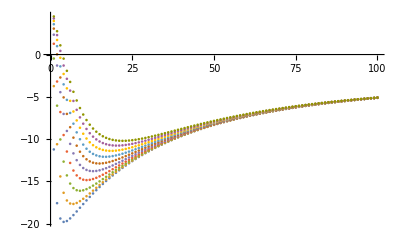

```mathematica
ListPlot[Table[Table[dStotdb0[10,10+0.2*i,30,0.1*j,b1sols[[i,j]],2,4,0.05],{j,1,100}],{i,1,10}]]
```

```mathematica
minpos=Flatten[Table[PositionSmallest[Table[Abs[dStotdb0[10,10+0.2*i,30,0.1*j,b1sols[[i,j]],2,4,0.05]],{j,1,100}]],{i,2,90}]]
```

{1,1,1,2,2,2,3,3,4,4,5,5,6,6,7,7,8,8,9,10,10,11,11,12,13,13,14,15,15,16,17,18,18,19,20,20,21,22,23,23,24,25,26,26,27,28,28,29,30,31,31,32,33,33,34,35,36,36,37,38,38,39,40,40,41,42,42,43,43,44,45,45,46,46,47,47,48,49,49,50,50,51,51,52,52,53,53,54,54}

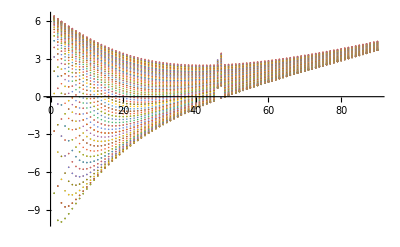

```mathematica
ListPlot[Table[Table[dStotda1[10,10+0.2*i,30,0.1*j,b1sols[[i,j]],2,4,0.05],{i,1,90}],{j,minpos}]]
```

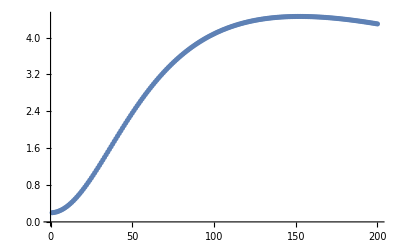

```mathematica
ListPlot[Table[Table[dStotda1[10,0.1*b0,30,0.1*a1,b1sols[[b0,a1]],2,4,0.05],{a1,1,200}],{b0,200,200}]]
```

### Single bulk slice

```mathematica
w[a0_,a1_,b_]:=(a0+a1)^2/(8 √((a0-a1)^2/2+b^2));
M[a0_,a1_,b_,m_]:=m^2/4*Subscript[Vol3, tl][a0,a1,b]
ϕsol[a0_,a1_,a2_,b0_,b1_,ϕ0_,ϕ2_,m_]:=(ϕ0*w[a0,a1,b0]+ϕ2*w[a1,a2,b1])/(w[a0,a1,b0]+w[a1,a2,b1]-M[a0,a1,b0,m]-M[a1,a2,b1,m]);
ϕintegral[a0_,a1_,a2_,b0_,b1_,ϕ0_,ϕ2_,m_]:=√((I*Pi)/(w[a0,a1,b0]+w[a1,a2,b1]-M[a0,a1,b0,m]-M[a1,a2,b1,m]))Exp[I*((ϕ0-ϕ2)^2*(w[a0,a1,b0]*w[a1,a2,b1])/(w[a0,a1,b0]+w[a1,a2,b1]-M[a0,a1,b0,m]-M[a1,a2,b1,m])-ϕ0^2(M[a0,a1,b0,m]+(w[a0,a1,b0](M[a0,a1,b0,m]+M[a1,a2,b1,m]))/(w[a0,a1,b0]+w[a1,a2,b1]-M[a0,a1,b0,m]-M[a1,a2,b1,m]))-ϕ2^2(M[a1,a2,b1,m]+(w[a1,a2,b1](M[a0,a1,b0,m]+M[a1,a2,b1,m]))/(w[a0,a1,b0]+w[a1,a2,b1]-M[a0,a1,b0,m]-M[a1,a2,b1,m])))];
Av1slice[a0_,a1_,a2_,b0_,b1_,ϕ0_,ϕ2_,m_]:=Subscript[A, f,sl][a1]*Subscript[A, v,III][a0,a1,b0]*Subscript[A, v,III][a1,a2,b1]*ϕintegral[a0,a1,a2,b0,b1,ϕ0,ϕ2,m]
```

```mathematica
Manipulate[Plot[Re[Subscript[A, v,III][10,a1,b0]*Subscript[A, v,III][a1,30,b1]*ϕintegral[10,a1,30,b0,b1,2,4,0.005]],{a1,0,40},PlotPoints->1000,PlotRange->All],{b0,1,20},{b1,1,20}]
```

```mathematica
Series[(w[a0,a1,b0]*w[a1,a2,b1])/(w[a0,a1,b0]+w[a1,a2,b1]-M[a0,a1,b0,m]-M[a1,a2,b1,m])/.{a0->10,a2->30,b0->7,b1->9,m->0.05},{a1,Infinity,4}]
Series[M[a0,a1,b0,m]/.{a0->10,a2->30,b0->7,b1->9,m->0.05},{a1,Infinity,4}]
```

-106.066/a1-12727.9/a1^2-817239./a1^3-(4.8137×10^7)/a1^4+O[1/a1]^5

0.000147314 a1^3+0.00721838 a1-0.00294628+1.98866/a1+14.5811/a1^2+48.3668/a1^3-674.702/a1^4+O[1/a1]^5

Mass term scales as a1^3 in the limit of large a1. There is the question whether saddle point approximation techniques can still be applied.

```mathematica
res=Table[NIntegrate[Subscript[A, v,III][10,a1,b0/2]*Subscript[A, v,III][a1,30,b1/2]*ϕintegral[10,a1,30,b0/2,b1/2,2,4,0.05],{a1,0,Infinity},Method->"LocalAdaptive"],{b0,1,20},{b1,1,20}]
```

{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,3.50225×10^-19-6.27763×10^-19 ⅈ,1.05899×10^-18+2.01782×10^-18 ⅈ,-7.16919×10^-18-2.77284×10^-18 ⅈ,1.30905×10^-17-7.81227×10^-18 ⅈ,4.5241×10^-18+2.52194×10^-17 ⅈ,-3.99253×10^-17+2.33726×10^-18 ⅈ,-9.29838×10^-18-5.79844×10^-17 ⅈ,7.21673×10^-17-3.7002×10^-17 ⅈ,8.75468×10^-17+5.70204×10^-17 ⅈ,1.42794×10^-17+1.23414×10^-16 ⅈ,-1.40031×10^-16+1.58928×10^-16 ⅈ,-1.20651×10^-16+1.97297×10^-16 ⅈ,-3.35567×10^-17+2.46141×10^-16 ⅈ,1.28586×10^-16+2.45573×10^-16 ⅈ,3.03778×10^-16+1.04704×10^-16 ⅈ,3.22791×10^-16-1.85503×10^-16 ⅈ,4.46433×10^-17-4.08834×10^-16 ⅈ,-3.48494×10^-16-2.65932×10^-16 ⅈ,-4.02194×10^-16+2.26661×10^-16 ⅈ},{0.,-9.19425×10^-19-7.39626×10^-19 ⅈ,7.09762×10^-18+5.77992×10^-18 ⅈ,-1.58187×10^-17-4.29812×10^-19 ⅈ,1.0758×10^-17-2.64449×10^-17 ⅈ,3.94793×10^-17+3.28092×10^-17 ⅈ,-6.32213×10^-17+5.27343×10^-17 ⅈ,1.3126×10^-16+6.53994×10^-17 ⅈ,6.44122×10^-17+2.11513×10^-16 ⅈ,-8.74581×10^-17+2.79096×10^-16 ⅈ,-1.52281×10^-16+2.29254×10^-16 ⅈ,-1.76513×10^-16+2.22562×10^-16 ⅈ,-1.09522×10^-16+2.28365×10^-16 ⅈ,5.14256×10^-17+2.14975×10^-16 ⅈ,2.57326×10^-16+8.9225×10^-17 ⅈ,3.45472×10^-16-2.15338×10^-16 ⅈ,8.78694×10^-17-5.38549×10^-16 ⅈ,-3.42038×10^-16-3.83111×10^-16 ⅈ,-4.90852×10^-16+1.52024×10^-16 ⅈ,1.44842×10^-17+5.48988×10^-16 ⅈ},{0.,-4.69896×10^-18-3.29134×10^-20 ⅈ,3.05999×10^-18-8.73154×10^-18 ⅈ,1.55778×10^-17+3.96103×10^-17 ⅈ,-7.88585×10^-17-2.8454×10^-17 ⅈ,8.46323×10^-17-1.0196×10^-16 ⅈ,-3.04356×10^-17+3.68255×10^-17 ⅈ,-3.08299×10^-17+2.5736×10^-17 ⅈ,-4.83874×10^-17+7.62927×10^-17 ⅈ,-1.51536×10^-16+1.4037×10^-16 ⅈ,-2.80798×10^-16+1.61367×10^-16 ⅈ,-4.05612×10^-16+1.80654×10^-16 ⅈ,-4.36917×10^-16+2.35×10^-16 ⅈ,-3.20032×10^-16+3.11389×10^-16 ⅈ,2.11901×10^-16+2.87231×10^-16 ⅈ,3.98588×10^-16+9.53503×10^-18 ⅈ,2.29258×10^-16-3.75085×10^-16 ⅈ,-2.81871×10^-16-3.88435×10^-16 ⅈ,-4.8778×10^-16+1.77995×10^-16 ⅈ,1.01089×10^-16+5.47236×10^-16 ⅈ},{0.,3.799×10^-18+1.34434×10^-19 ⅈ,-2.32609×10^-17-1.61237×10^-17 ⅈ,3.73205×10^-17-1.88308×10^-18 ⅈ,-1.97502×10^-18+7.14462×10^-17 ⅈ,2.14351×10^-17-1.41078×10^-17 ⅈ,3.19896×10^-17-3.28415×10^-17 ⅈ,4.68828×10^-17-8.60007×10^-17 ⅈ,1.2141×10^-16-1.04352×10^-16 ⅈ,1.61425×10^-16-7.00816×10^-17 ⅈ,1.84918×10^-17-1.3181×10^-16 ⅈ,-8.51121×10^-17-1.74737×10^-16 ⅈ,-1.69181×10^-16-1.85537×10^-16 ⅈ,-2.91107×10^-16-1.01699×10^-17 ⅈ,-2.03514×10^-16+2.62473×10^-16 ⅈ,1.5156×10^-16+3.39653×10^-16 ⅈ,4.12817×10^-16-2.33378×10^-17 ⅈ,8.47987×10^-17-4.44393×10^-16 ⅈ,-4.66642×10^-16-1.54724×10^-16 ⅈ,-1.81655×10^-16+4.97741×10^-16 ⅈ},{0.,6.14155×10^-18-4.39781×10^-18 ⅈ,1.6875×10^-17-1.93608×10^-18 ⅈ,-7.13447×10^-17-2.72026×10^-18 ⅈ,9.66668×10^-17-6.98222×10^-17 ⅈ,2.5218×10^-18-1.56929×10^-17 ⅈ,2.45858×10^-17-5.73876×10^-18 ⅈ,-4.47427×10^-17-1.00703×10^-17 ⅈ,-1.02397×10^-16+2.15795×10^-18 ⅈ,-9.76894×10^-17+6.58961×10^-17 ⅈ,-4.39925×10^-17+1.43381×10^-16 ⅈ,8.75635×10^-17+1.62484×10^-16 ⅈ,2.18144×10^-16+3.47425×10^-17 ⅈ,1.63161×10^-16-1.99444×10^-16 ⅈ,-1.35519×10^-16-2.63254×10^-16 ⅈ,-3.30191×10^-16+6.38968×10^-17 ⅈ,5.92275×10^-18+3.73912×10^-16 ⅈ,4.1342×10^-16+2.02142×10^-17 ⅈ,7.85362×10^-18-4.52139×10^-16 ⅈ,-4.85786×10^-16+5.45872×10^-17 ⅈ},{0.,5.29764×10^-18+1.0061×10^-17 ⅈ,1.84743×10^-17-2.91634×10^-17 ⅈ,1.1327×10^-17-3.72227×10^-18 ⅈ,-5.46966×10^-17+8.4739×10^-17 ⅈ,-2.89103×10^-17-9.66137×10^-18 ⅈ,1.93338×10^-17-3.87684×10^-17 ⅈ,2.35646×10^-17+2.13371×10^-18 ⅈ,1.49201×10^-17+1.01989×10^-16 ⅈ,1.49234×10^-16+8.44003×10^-17 ⅈ,1.81491×10^-16-1.80607×10^-18 ⅈ,-3.35584×10^-17-1.49146×10^-16 ⅈ,-1.86577×10^-16-2.13476×10^-17 ⅈ,-7.84152×10^-17+2.09505×10^-16 ⅈ,2.25356×10^-16+1.26954×10^-16 ⅈ,1.62314×10^-16-2.48372×10^-16 ⅈ,-2.86484×10^-16-1.70763×10^-16 ⅈ,-1.49707×10^-16+3.40507×10^-16 ⅈ,3.99449×10^-16+8.0164×10^-17 ⅈ,-4.69712×10^-17-4.40618×10^-16 ⅈ},{0.,9.70255×10^-18+6.86056×10^-18 ⅈ,2.93908×10^-17+2.94576×10^-17 ⅈ,-7.17398×10^-17-1.07711×10^-16 ⅈ,1.83123×10^-16+4.56257×10^-17 ⅈ,7.91627×10^-17-5.86926×10^-17 ⅈ,-6.12273×10^-17-2.08094×10^-17 ⅈ,-3.1497×10^-17-7.99461×10^-17 ⅈ,1.00879×10^-16-4.23548×10^-17 ⅈ,1.36352×10^-16-6.0848×10^-17 ⅈ,-1.56147×10^-17-4.16227×10^-17 ⅈ,-6.27368×10^-17+1.08607×10^-16 ⅈ,1.36831×10^-16+7.87852×10^-17 ⅈ,8.72119×10^-17-1.711×10^-16 ⅈ,-2.10608×10^-16-7.88068×10^-17 ⅈ,-4.89157×10^-17+2.54832×10^-16 ⅈ,2.9476×10^-16-2.14061×10^-17 ⅈ,-1.27805×10^-16-3.05708×10^-16 ⅈ,-2.53199×10^-16+2.62803×10^-16 ⅈ,3.83579×10^-16+1.11107×10^-16 ⅈ},{0.,-1.3059×10^-18+1.58886×10^-17 ⅈ,5.95967×10^-17-4.06602×10^-18 ⅈ,1.84845×10^-18-6.8585×10^-17 ⅈ,1.25205×10^-16-1.05468×10^-17 ⅈ,6.38289×10^-17+2.13218×10^-16 ⅈ,-1.32536×10^-16+1.8439×10^-16 ⅈ,-1.25961×10^-16+8.46841×10^-17 ⅈ,3.56563×10^-17-1.32926×10^-18 ⅈ,-3.63582×10^-17-4.14349×10^-17 ⅈ,-8.21925×10^-17-8.56176×10^-17 ⅈ,4.31713×10^-17-7.37623×10^-17 ⅈ,-4.43385×10^-17-1.27222×10^-16 ⅈ,-1.28863×10^-16+1.04459×10^-16 ⅈ,1.70225×10^-16+9.62256×10^-17 ⅈ,2.53609×10^-17-2.26771×10^-16 ⅈ,-2.43205×10^-16+9.51632×10^-17 ⅈ,2.31768×10^-16+1.83853×10^-16 ⅈ,2.40882×10^-17-3.26958×10^-16 ⅈ,-2.99087×10^-16+2.01737×10^-16 ⅈ},{0.,1.06106×10^-17+1.83368×10^-17 ⅈ,3.7632×10^-17+2.21027×10^-17 ⅈ,-2.79089×10^-17-1.36544×10^-16 ⅈ,1.31687×10^-16+1.84623×10^-16 ⅈ,-1.02873×10^-16-1.64926×10^-16 ⅈ,1.83951×10^-16-2.69712×10^-16 ⅈ,1.20305×10^-16+7.82272×10^-17 ⅈ,1.90995×10^-17-2.63441×10^-17 ⅈ,-4.5237×10^-17+1.96233×10^-17 ⅈ,6.52868×10^-17+2.27059×10^-17 ⅈ,-3.32872×10^-17-8.59439×10^-17 ⅈ,-6.27002×10^-17+1.00031×10^-16 ⅈ,1.44654×10^-16-9.19185×10^-18 ⅈ,-1.0727×10^-16-1.33415×10^-16 ⅈ,-4.25828×10^-16+4.58106×10^-16 ⅈ,2.09553×10^-16-9.77319×10^-17 ⅈ,-2.43763×10^-16-1.02542×10^-16 ⅈ,1.11415×10^-16+2.74278×10^-16 ⅈ,1.08041×10^-16-3.08019×10^-16 ⅈ},{0.,9.54436×10^-18+1.66403×10^-17 ⅈ,8.15589×10^-17-9.13532×10^-18 ⅈ,-4.16638×10^-17-4.04245×10^-17 ⅈ,2.46422×10^-17-5.5627×10^-17 ⅈ,4.23604×10^-17+1.16406×10^-16 ⅈ,-1.34841×10^-16+6.61653×10^-17 ⅈ,-2.9697×10^-18-3.18004×10^-17 ⅈ,3.58454×10^-17-1.14202×10^-16 ⅈ,6.06081×10^-18+4.43637×10^-17 ⅈ,1.89738×10^-17-5.9639×10^-17 ⅈ,-6.43469×10^-17+5.20725×10^-17 ⅈ,1.04757×10^-16-2.06702×10^-18 ⅈ,-9.82095×10^-17-8.11058×10^-17 ⅈ,2.16782×10^-17+1.51969×10^-16 ⅈ,5.11331×10^-16-4.05575×10^-16 ⅈ,-1.98328×10^-16+6.58307×10^-17 ⅈ,2.24217×10^-16+7.37597×10^-17 ⅈ,-1.60979×10^-16-2.10522×10^-16 ⅈ,6.6743×10^-18+2.77466×10^-16 ⅈ},{0.,2.66961×10^-17+1.28169×10^-17 ⅈ,4.77044×10^-17-3.88032×10^-17 ⅈ,4.25424×10^-17+6.92833×10^-18 ⅈ,-3.22967×10^-17+6.79554×10^-17 ⅈ,-2.56342×10^-16+1.65987×10^-16 ⅈ,-1.05907×10^-16-2.97176×10^-16 ⅈ,-3.82243×10^-17+7.02218×10^-17 ⅈ,-1.30607×10^-16+2.12127×10^-17 ⅈ,4.15372×10^-17+5.11011×10^-18 ⅈ,-5.4179×10^-17-1.59401×10^-17 ⅈ,6.0517×10^-17+4.25719×10^-17 ⅈ,-4.67177×10^-17-8.07021×10^-17 ⅈ,3.06013×10^-18+1.15363×10^-16 ⅈ,6.41464×10^-17-1.2604×10^-16 ⅈ,-5.18174×10^-16+3.93314×10^-16 ⅈ,1.90401×10^-16-1.95217×10^-17 ⅈ,-2.02615×10^-16-7.9673×10^-17 ⅈ,1.69664×10^-16+1.75896×10^-16 ⅈ,-1.02849×10^-16-2.49921×10^-16 ⅈ},{0.,2.5232×10^-17-1.13978×10^-17 ⅈ,4.48853×10^-17-7.76106×10^-17 ⅈ,-1.75291×10^-16+8.47473×10^-17 ⅈ,1.23284×10^-17-2.90633×10^-17 ⅈ,7.1759×10^-17-6.37104×10^-17 ⅈ,-1.98274×10^-17-9.12775×10^-17 ⅈ,2.06845×10^-16+1.69392×10^-17 ⅈ,-1.38443×10^-17+2.78237×10^-17 ⅈ,1.1654×10^-17-4.04249×10^-17 ⅈ,-1.37518×10^-17+5.2411×10^-17 ⅈ,2.47715×10^-17-6.4732×10^-17 ⅈ,-4.79578×10^-17+7.34612×10^-17 ⅈ,8.10208×10^-17-7.253×10^-17 ⅈ,-1.15777×10^-16+5.28956×10^-17 ⅈ,1.51395×10^-16-1.26198×10^-17 ⅈ,-1.67969×10^-16-3.94709×10^-17 ⅈ,1.70549×10^-16+9.83486×10^-17 ⅈ,-1.54931×10^-16-1.58242×10^-16 ⅈ,1.29092×10^-16+2.12998×10^-16 ⅈ},{0.,1.37605×10^-17-2.38166×10^-17 ⅈ,-6.73078×10^-17-9.50509×10^-17 ⅈ,9.56678×10^-18+7.45329×10^-18 ⅈ,9.74923×10^-19+2.67607×10^-17 ⅈ,-4.63581×10^-17+5.03311×10^-17 ⅈ,-2.27443×10^-16+1.04453×10^-16 ⅈ,-2.33451×10^-16-8.34063×10^-17 ⅈ,-3.63831×10^-17-8.13846×10^-17 ⅈ,-1.35499×10^-16-1.30126×10^-16 ⅈ,-1.23232×10^-16-1.15928×10^-16 ⅈ,-6.73525×10^-17-2.71436×10^-18 ⅈ,8.29114×10^-17+4.74271×10^-18 ⅈ,-9.74522×10^-17-1.52846×10^-17 ⅈ,1.13289×10^-16+3.74887×10^-17 ⅈ,-1.24942×10^-16-6.05696×10^-17 ⅈ,1.3293×10^-16+9.40126×10^-17 ⅈ,-1.34049×10^-16-1.27831×10^-16 ⅈ,1.33215×10^-16+1.58144×10^-16 ⅈ,-1.3085×10^-16-1.87809×10^-16 ⅈ},{0.,-1.64577×10^-17-3.36507×10^-17 ⅈ,-9.60461×10^-17+2.52988×10^-17 ⅈ,1.03011×10^-17-1.155×10^-17 ⅈ,-3.61699×10^-18-3.47175×10^-17 ⅈ,8.41134×10^-17-4.65303×10^-17 ⅈ,2.5732×10^-16+6.03288×10^-17 ⅈ,3.16184×10^-17+8.41389×10^-17 ⅈ,4.66247×10^-17+8.92818×10^-17 ⅈ,4.61735×10^-17+2.16379×10^-16 ⅈ,1.80513×10^-16+9.91184×10^-17 ⅈ,1.83349×10^-17+5.91785×10^-17 ⅈ,-3.15361×10^-17-6.94252×10^-17 ⅈ,4.38792×10^-17+8.36987×10^-17 ⅈ,-5.6908×10^-17-9.61679×10^-17 ⅈ,6.36731×10^-17+1.15018×10^-16 ⅈ,-7.15303×10^-17-1.31192×10^-16 ⅈ,8.20663×10^-17+1.49348×10^-16 ⅈ,-9.91387×10^-17-1.66483×10^-16 ⅈ,1.19534×10^-16+1.75683×10^-16 ⅈ},{0.,-4.196×10^-17+9.26209×10^-18 ⅈ,1.78646×10^-17-4.31191×10^-18 ⅈ,-3.0606×10^-18-3.33413×10^-17 ⅈ,-2.99913×10^-17+2.32495×10^-17 ⅈ,-6.67971×10^-17-4.33155×10^-18 ⅈ,-1.54797×10^-16-1.71148×10^-16 ⅈ,2.49936×10^-17-7.95744×10^-17 ⅈ,-1.81003×10^-17-2.46407×10^-17 ⅈ,5.7967×10^-17-1.78515×10^-16 ⅈ,-4.80683×10^-17+1.20845×10^-17 ⅈ,4.91205×10^-17-3.67547×10^-17 ⅈ,-4.40491×10^-17+6.1367×10^-17 ⅈ,3.35356×10^-17-8.22941×10^-17 ⅈ,-2.65068×10^-17+1.01961×10^-16 ⅈ,1.13832×10^-17-1.20957×10^-16 ⅈ,5.6083×10^-18+1.40842×10^-16 ⅈ,-2.72565×10^-17-1.56852×10^-16 ⅈ,5.68733×10^-17+1.71619×10^-16 ⅈ,-9.87896×10^-17-1.72721×10^-16 ⅈ},{0.,2.14632×10^-18+3.99259×10^-17 ⅈ,1.59431×10^-17-7.48076×10^-18 ⅈ,-4.71992×10^-17+5.50541×10^-18 ⅈ,-1.99284×10^-18+2.23104×10^-17 ⅈ,6.64963×10^-17-5.41959×10^-18 ⅈ,3.50809×10^-17+1.77338×10^-16 ⅈ,-2.42717×10^-17+6.11635×10^-17 ⅈ,-8.85035×10^-17+4.3176×10^-16 ⅈ,-4.95205×10^-17+1.36552×10^-16 ⅈ,2.55783×10^-17+4.04661×10^-17 ⅈ,-5.20382×10^-17-2.70932×10^-17 ⅈ,6.97205×10^-17+4.76822×10^-18 ⅈ,-8.24495×10^-17+2.14154×10^-17 ⅈ,8.32799×10^-17-5.49069×10^-17 ⅈ,-7.90203×10^-17+8.75323×10^-17 ⅈ,6.24344×10^-17-1.19743×10^-16 ⅈ,-3.10707×10^-17+1.48707×10^-16 ⅈ,-1.05958×10^-17-1.69317×10^-16 ⅈ,7.05628×10^-17+1.73912×10^-16 ⅈ},{0.,3.47111×10^-17+7.41604×10^-18 ⅈ,-2.37154×10^-20-2.80293×10^-17 ⅈ,1.3568×10^-17+3.65425×10^-17 ⅈ,4.09675×10^-17+4.13418×10^-17 ⅈ,-8.82451×10^-17-5.98554×10^-17 ⅈ,1.92198×10^-17-1.44315×10^-16 ⅈ,1.66409×10^-16-3.37891×10^-16 ⅈ,1.18774×10^-16-3.13715×10^-17 ⅈ,5.09573×10^-17-1.70187×10^-16 ⅈ,-5.486×10^-17-2.35101×10^-16 ⅈ,-4.36051×10^-18+5.64884×10^-17 ⅈ,-3.21104×10^-17-6.18684×10^-17 ⅈ,2.03202×10^-16-2.03263×10^-16 ⅈ,6.34625×10^-17-2.94941×10^-16 ⅈ,1.1024×10^-16-1.48107×10^-17 ⅈ,-1.07661×10^-16+6.64114×10^-17 ⅈ,8.46828×10^-17-1.1757×10^-16 ⅈ,-3.68471×10^-17+1.56205×10^-16 ⅈ,-3.68757×10^-17-1.74701×10^-16 ⅈ},{0.,1.6843×10^-17-3.48266×10^-17 ⅈ,-2.7579×10^-17-2.03911×10^-18 ⅈ,8.7397×10^-18-1.34562×10^-17 ⅈ,5.53126×10^-17-7.98274×10^-17 ⅈ,-7.14315×10^-19+1.0964×10^-16 ⅈ,-7.22826×10^-17+1.4939×10^-16 ⅈ,-3.58385×10^-16+1.45315×10^-16 ⅈ,-8.03412×10^-17+4.6522×10^-17 ⅈ,-1.05552×10^-16+1.77671×10^-16 ⅈ,4.43885×10^-17+2.36047×10^-16 ⅈ,5.06843×10^-17-2.39187×10^-17 ⅈ,-3.03057×10^-17+5.78584×10^-17 ⅈ,-1.93918×10^-16-1.62248×10^-16 ⅈ,5.23432×10^-17+9.97477×10^-17 ⅈ,-9.45221×10^-17-4.61375×10^-17 ⅈ,1.19701×10^-16-2.35499×10^-18 ⅈ,-1.20672×10^-16+6.67259×10^-17 ⅈ,8.09021×10^-17-1.298×10^-16 ⅈ,1.68664×10^-19+1.70205×10^-16 ⅈ},{0.,-4.06393×10^-17-1.87904×10^-17 ⅈ,-3.22706×10^-18+1.6876×10^-17 ⅈ,1.84564×10^-18+1.84823×10^-17 ⅈ,-1.10585×10^-16-2.90764×10^-17 ⅈ,6.07633×10^-17-4.36006×10^-17 ⅈ,1.80719×10^-16-9.89547×10^-17 ⅈ,3.15654×10^-16+1.18808×10^-16 ⅈ,1.33437×10^-16-5.77468×10^-17 ⅈ,1.63311×10^-16-1.46013×10^-16 ⅈ,-3.71899×10^-17-2.17466×10^-16 ⅈ,-4.25502×10^-17-3.23863×10^-17 ⅈ,2.30444×10^-16+1.16026×10^-16 ⅈ,-5.17621×10^-17+5.39622×10^-17 ⅈ,4.05585×10^-17-9.09019×10^-17 ⅈ,4.5049×10^-17+9.24928×10^-17 ⅈ,-9.96983×10^-17-5.82592×10^-17 ⅈ,1.3143×10^-16-6.22819×10^-18 ⅈ,-1.15503×10^-16+9.03031×10^-17 ⅈ,3.85763×10^-17-1.56026×10^-16 ⅈ}}

```mathematica
Table[Re[res[[i,i]]],{i,1,20}]
```

{0.,3.50225×10^-19,7.09762×10^-18,1.55778×10^-17,-1.97502×10^-18,2.5218×10^-18,1.93338×10^-17,-3.1497×10^-17,3.56563×10^-17,-4.5237×10^-17,1.89738×10^-17,6.0517×10^-17,-4.79578×10^-17,-9.74522×10^-17,-5.6908×10^-17,1.13832×10^-17,6.24344×10^-17,8.46828×10^-17,8.09021×10^-17,3.85763×10^-17}

```mathematica
Table[Im[res[[n,n]]],{n,1,20}]
```

{0,-6.27763×10^-19,5.77992×10^-18,3.96103×10^-17,7.14462×10^-17,-1.56929×10^-17,-3.87684×10^-17,-7.99461×10^-17,-1.32926×10^-18,1.96233×10^-17,-5.9639×10^-17,4.25719×10^-17,7.34612×10^-17,-1.52846×10^-17,-9.61679×10^-17,-1.20957×10^-16,-1.19743×10^-16,-1.1757×10^-16,-1.298×10^-16,-1.56026×10^-16}

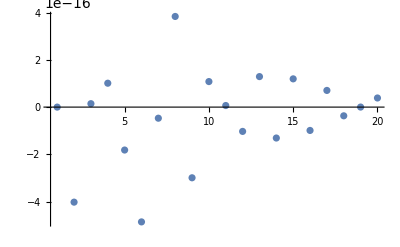

```mathematica
ListPlot[Table[Re[res[[n,20]]],{n,1,20}],PlotRange->All]
```

```mathematica
NIntegrate[(Subscript[A, v,III][10,a1,b0/2]*Subscript[A, v,III][a1,30,b1/2]*ϕintegral[10,a1,30,b0/2,b1/2,2,4,0.05]/.{b0->30,b1->40}),{a1,0,Infinity},MaxRecursion->15,Method->"LocalAdaptive"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 15 recursive bisections in a1 near {a1} = {0.743156}. NIntegrate obtained -2.14273×10^-21-1.69969×10^-21 ⅈ and 7.31116×10^-21 for the integral and error estimates.

1.25283×10^-16+3.55393×10^-17 ⅈ

Asymptotic behavior of the path integrand in a1:

```mathematica
Series[N[√((I*Pi)/(w[a0,a1,b0]+w[a1,a2,b1]-M[a0,a1,b0,m]-M[a1,a2,b1,m]))*1/(√DetTLϵ[a0,a1,b0])*1/(√DetTLϵ[a1,a2,b1])*Subscript[A, f,sl][a1]/.{a0->30,a2->30,m->0.05,b0->10,b1->20}],{a1,Infinity,20}]
```

((-0.212081-1.9985 ⅈ) √(-(0.+3394.11 ⅈ)/a1^3) a1^(3/2) (1/a1)^(33/2)+(-210.416-459.245 ⅈ) √(-(0.+3394.11 ⅈ)/a1^3) a1^(3/2) (1/a1)^(35/2)+(-49154.2-43516.2 ⅈ) √(-(0.+3394.11 ⅈ)/a1^3) a1^(3/2) (1/a1)^(37/2)+(-5.85676×10^6-1.30642×10^6 ⅈ) √(-(0.+3394.11 ⅈ)/a1^3) a1^(3/2) (1/a1)^(39/2)+O[1/a1]^(41/2)) Tanh[3.14159 a1+O[1/a1]^21]

## Analysis along structure of the draft

### Varying edge length l_1

#### Convergence of Wynn’s algorithm in III

For the partition sum with varying final spacelike edge length, where do the deviations come from and can the computations be enhanced by varying the range of the partial sums?

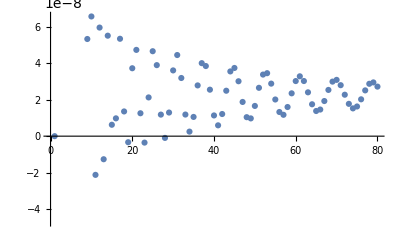
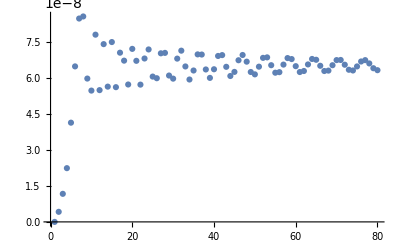
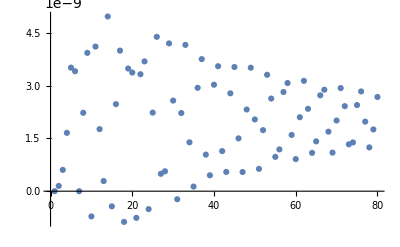
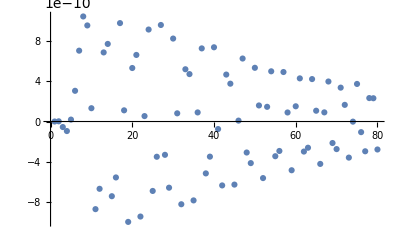
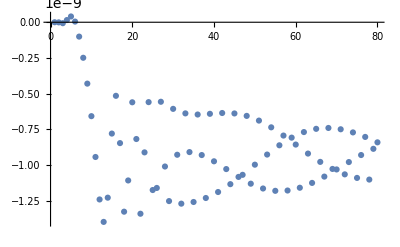
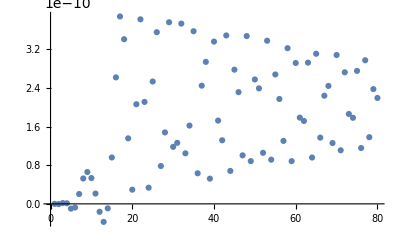
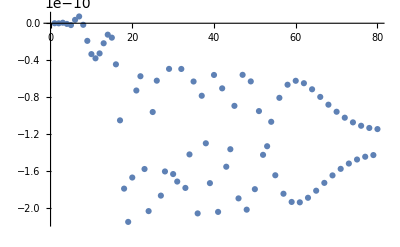
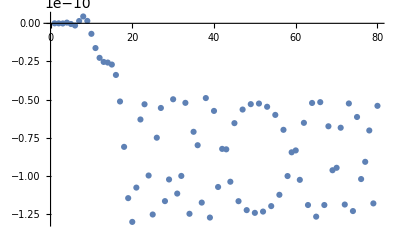

```mathematica
Table[ListPlot[Accumulate[Table[Re[N[(Subscript[A, v,III][a0,10+4n,b/2]*Exp[I*Subscript[S, ϕ,tl][a0,10+4n,b/2,2,4,0.05]]/.{a0->10})]],{b,1,80}]]],{n,0,20}]
```

In fact, the partition sum has nicer convergence properties for smaller length length l_1. Let’s look closer at the first case where l_1 = l_0 = 10:

```mathematica
SequenceLimit[Accumulate[Table[Re[N[(Subscript[A, v,III][a0,10+4n,b/2]*Exp[I*Subscript[S, ϕ,tl][a0,10+4n,b/2,2,4,0.05]]/.{a0->10,n->0})]],{b,1,150}]],Method->"WynnEpsilon"]
```

2.27849×10^-8

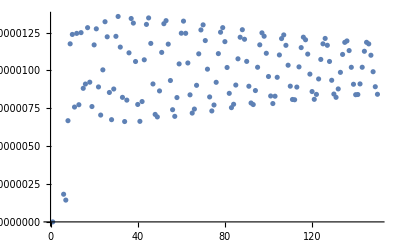

```mathematica
ListPlot[Accumulate[Table[Re[N[(b/2*Subscript[A, v,III][a0,10+4n,b/2]*Exp[I*Subscript[S, ϕ,tl][a0,10+4n,b/2,2,4,0.05]]/.{a0->10,n->0})]],{b,1,150}]]]
```

```mathematica
SequenceLimit[Accumulate[Table[Re[N[(b/2*Subscript[A, v,III][a0,10+4n,b/2]*Exp[I*Subscript[S, ϕ,tl][a0,10+4n,b/2,2,4,0.05]]/.{a0->10,n->0})]],{b,1,150}]],Method->"WynnEpsilon"]
```

1.01289×10^-6

```mathematica
Re[SequenceLimit[Accumulate[Table[N[(b/2*Subscript[A, v,III][a0,10+4n,b/2]*Exp[I*Subscript[S, ϕ,tl][a0,10+4n,b/2,2,4,0.05]]/.{a0->10,n->0})],{b,1,150}]],Method->"WynnEpsilon"]/SequenceLimit[Accumulate[Table[N[(Subscript[A, v,III][a0,10+4n,b/2]*Exp[I*Subscript[S, ϕ,tl][a0,10+4n,b/2,2,4,0.05]]/.{a0->10,n->0})],{b,1,150}]],Method->"WynnEpsilon"]]
```

7.9983

So apparently, the algorithms work very well but the result deviates strongly from the classical result. Is this a consequence of the spectrum? This is the case if the oscillations are very rapid:

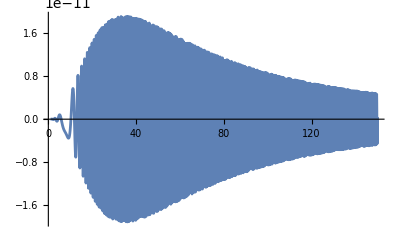

```mathematica
Plot[Re[N[(Subscript[A, v,III][a0,10+4n,b]*Exp[I*Subscript[S, ϕ,tl][a0,10+4n,b,2,4,0.05]]/.{a0->10,n->10})]],{b,1,150}]
```

For n = 0 and 10, the classical solutions are actually smaller than the first non-zero value of b = 0.5. Also, for n = 3, the region of the classical solutions in the path integrand is probed by ~3 points and that may be insufficient. So indeed, the gap of the spectrum seems to be troublesome here.

There is another source of numerical error: if the acceleration is successful, further application of the algorithm  leads to division by small numbers such that the result then deviates from the actual limiting point. As a result, the algorithm depends on the upper cutoff of the partial sums that one plugs in.

What happens under refinement?

```mathematica
bsolsa[[201]]
```

{90.,7.56443}

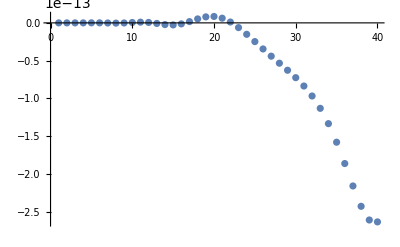
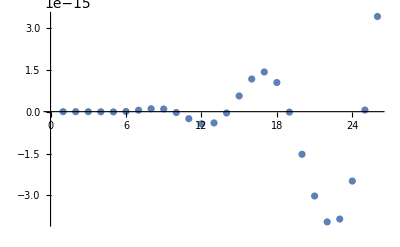
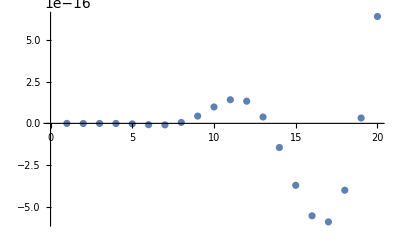
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListPlot[Re[Accumulate[Table[N[(Subscript[A, v,III][a0,10+4n,b/(2m)]*Exp[I*Subscript[S, ϕ,tl][a0,10+4n,b/(2m),2,4,0.05]]/.{a0->10,n->20})],{b,1,80/m}]]]],{m,1,4}]
```

```mathematica
Re[SequenceLimit[Accumulate[Table[N[(b/2*Subscript[A, v,III][a0,10+4n,b/2]*Exp[I*Subscript[S, ϕ,tl][a0,10+4n,b/2,2,4,0.05]]/.{a0->10,n->20})],{b,1,80}]],Method->"WynnEpsilon"]/SequenceLimit[Accumulate[Table[N[(Subscript[A, v,III][a0,10+4n,b/2]*Exp[I*Subscript[S, ϕ,tl][a0,10+4n,b/2,2,4,0.05]]/.{a0->10,n->20})],{b,1,80}]],Method->"WynnEpsilon"]]
```

7.43022

```mathematica
Table[Re[SequenceLimit[Accumulate[Table[N[(b/(2m)*Subscript[A, v,III][a0,10+4n,b/(2m)]*Exp[I*Subscript[S, ϕ,tl][a0,10+4n,b/(2m),2,4,0.05]]/.{a0->10,n->20})],{b,1,50}]],Method->"WynnEpsilon"]/SequenceLimit[Accumulate[Table[N[(Subscript[A, v,III][a0,10+4n,b/(2m)]*Exp[I*Subscript[S, ϕ,tl][a0,10+4n,b/(2m),2,4,0.05]]/.{a0->10,n->20})],{b,1,50}]],Method->"WynnEpsilon"]],{m,1,4}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{8.15486,Indeterminate,Indeterminate,Indeterminate}

#### Behavior of path integrand

In Sector III:

```mathematica
Manipulate[Plot[Subscript[S, III][10,10+4n,b/2]+Subscript[S, ϕ,tl][10,10+4n,b/2,2,4,0.05],{b,1,150},PlotRange->All],{n,0,20}]
```

```mathematica
Manipulate[Plot[Re[Subscript[A, v,III][10,10+4n,b/2]*Exp[I*Subscript[S, ϕ,tl][10,10+4n,b/2,2,4,0.05]]],{b,1,150}],{n,0,20}]
```

For l_0 approx. l_1, the Regge action behaves non-linear in b  for small b and a linear but relatively flat behavior with large values of b . That means for the path integrand rapid oscillations of varying frequency for small b and slow oscillations with constant frequency at larger b. With increasing l_1, the non-linear behavior for small b gets less and the constant freq. oscillations for large b have larger frequency.

In Sector II:

```mathematica
Manipulate[Plot[Subscript[S, II][10,10+4n,b]+Subscript[S, ϕ,sl][10,10+4n,b,2,4,0.05],{b,0,√((4n)^2/4)},PlotRange->All],{n,0,20}]
```

```mathematica
Manipulate[Plot[Re[Subscript[A, v,II][10,10+4n,b]*Exp[I*Subscript[S, ϕ,sl][10,10+4n,b,2,4,0.05]]],{b,0,√((4n)^2/4)}],{n,0,20}]
```

No linear behavior in the range of b. Frequency of oscillations increase non-linearly towards the bound of b. Increasing numerical errors should be expected for larger l_1.

Sector I:

```mathematica
Manipulate[Plot[Subscript[S, I][10,10+4n,b]+Subscript[S, ϕ,sl][10,10+4n,b,2,4,0.05],{b,√((4n)^2/4),√((4n)^2/2)}],{n,0,20}]
```

Divergence of the frequency of oscillations towards the upper bound of b, i.e. towards the Euclidean sector. Also here, the behavior becomes more extreme for larger l_1.

### Varying scalar field value ϕ_1

#### Convergence of Wynn’s algorithm in III

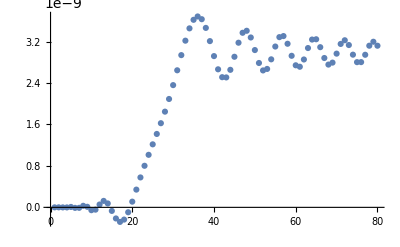
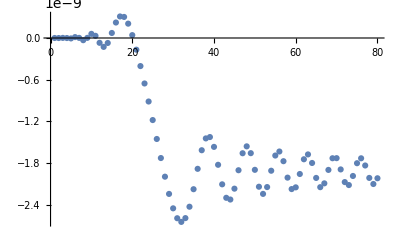
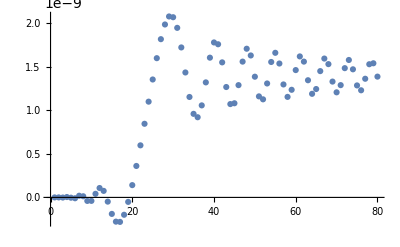
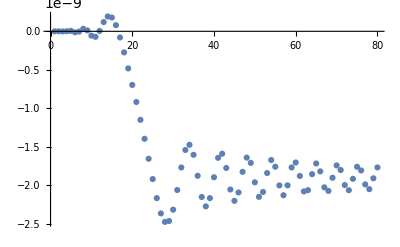
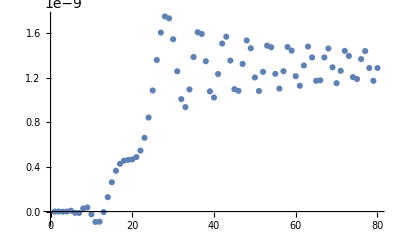
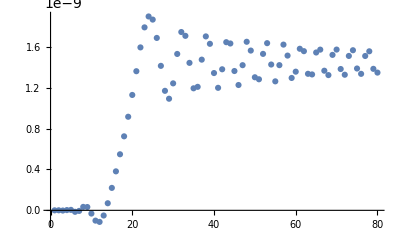
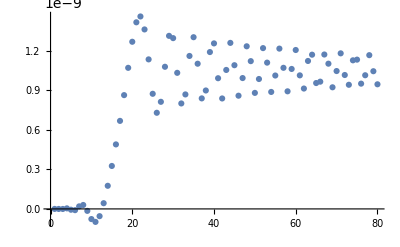
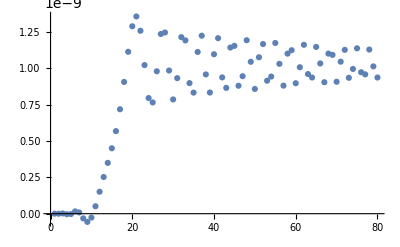
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListPlot[Accumulate[Table[Re[N[(Subscript[A, v,III][a0,a1,b/2]*Exp[I*Subscript[S, ϕ,tl][a0,a1,b/2,2,2+0.2n,0.05]]/.{a0->10,a1->30})]],{b,1,80}]]],{n,0,20}]
```

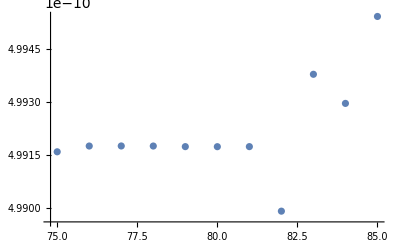

```mathematica
ListPlot[Table[{80+m,SequenceLimit[Accumulate[Table[Re[N[(b/2 Subscript[A, v,III][a0,a1,b/2]*Exp[I*Subscript[S, ϕ,tl][a0,a1,b/2,2,2+0.2n,0.05]]/.{a0->10,a1->30,n->15})]],{b,1,80+m}]],Method->"WynnEpsilon"]},{m,-5,5}]]
```

```mathematica
SequenceLimit[Accumulate[Table[N[(b/2 Subscript[A, v,III][a0,a1,b/2]*Exp[I*Subscript[S, ϕ,tl][a0,a1,b/2,2,2+0.2n,0.05]]/.{a0->10,a1->30,n->15})],{b,1,60}]],Method->"WynnEpsilon"]/SequenceLimit[Accumulate[Table[N[(Subscript[A, v,III][a0,a1,b/2]*Exp[I*Subscript[S, ϕ,tl][a0,a1,b/2,2,2+0.2n,0.05]]/.{a0->10,a1->30,n->15})],{b,1,60}]],Method->"WynnEpsilon"]
```

3.80643-0.503461 ⅈ

#### Behavior of path integrand

In Sector III:

```mathematica
Manipulate[Plot[Subscript[S, III][10,30,b/2]+Subscript[S, ϕ,tl][10,30,b/2,2,2+0.2n,0.05],{b,1,150},PlotRange->All],{n,0,20}]
```

```mathematica
Manipulate[Plot[Re[Subscript[A, v,III][10,30,b/2]*Exp[I*Subscript[S, ϕ,tl][10,30,b/2,2,2+0.2n,0.05]]],{b,1,150}],{n,0,20}]
```

Frequence of oscillations increases for larger scalar field values (and differences). Saddle point moves towards b = 0 which can therefore not be resolved as good. On the other hand, faster oscillations help with smaller deviation w.r.t. the classical value

In  Sector II:

```mathematica
Manipulate[Plot[Subscript[S, II][10,30,b/2]+Subscript[S, ϕ,sl][10,30,b/2,2,2+0.2n,0.05],{b,0,√((4n)^2/4)},PlotRange->All],{n,0,20}]
```

Similar as for increasing l_1.

### Varying mass

#### Convergence of Wynn’s algorithm in III

Worked out fine after studying the two cases above

#### Behavior of path integrand

In Sector III:

```mathematica
Manipulate[Plot[Re[Subscript[A, v,III][10,30,b/2]*Exp[I*Subscript[S, ϕ,tl][10,30,b/2,2,4,10^-3(1+4n)]]],{b,1,150}],{n,0,20}]
```

For small masses, the saddle point is at a large value but the oscillations are slow. This slows down convergence as it takes a large range of b’s for the oscillations to cancel out. At higher mass, the saddle point tends towards b = 0, making its resolution more complicated. The oscillations are faster in this regime, helping with convergence of Wynn’s algorithm.

### Scaling up the boundary length: variance

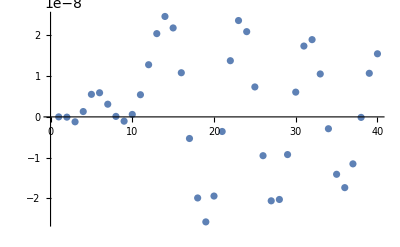
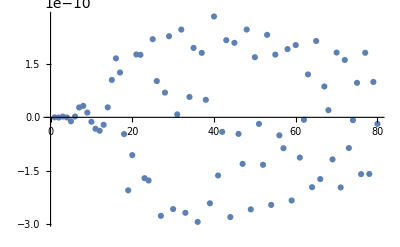
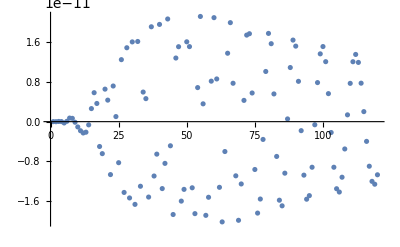
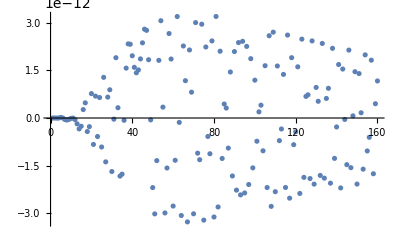
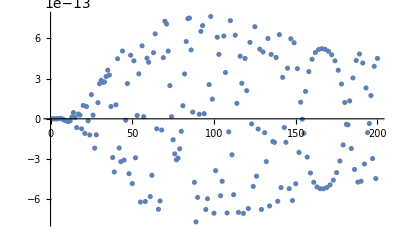
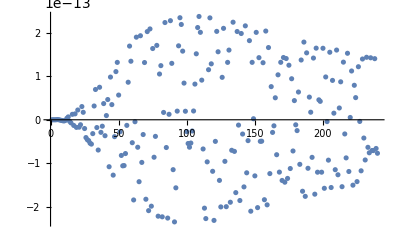
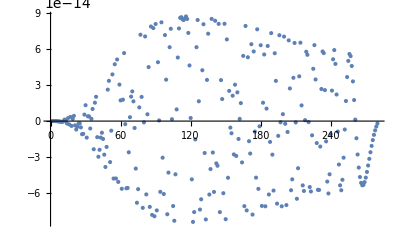
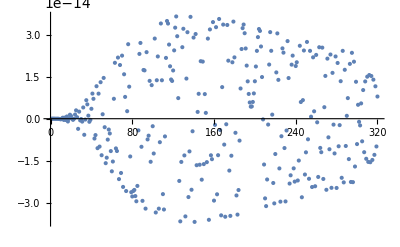
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListPlot[Table[Re[N[(Subscript[A, v,III][a0*0.5n,a1*0.5n,b/2]*Exp[I*Subscript[S, ϕ,tl][a0*0.5n,a1*0.5n,b/2,2,4,0.05]]/.{a0->10,a1->30})]],{b,1,80*0.5n}]],{n,1,20}]
```

```mathematica
Table[ListPlot[Accumulate[Table[Re[N[(Subscript[A, v,III][a0*0.5n,a1*0.5n,b/2]*Exp[I*Subscript[S, ϕ,tl][a0*0.5n,a1*0.5n,b/2,2,4,0.05]]/.{a0->10,a1->30})]],{b,1,60*0.5n}]]],{n,1,20}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

It seems that if we scale up the boundary data, then the exponent that governs the oscillations is non-linear in the summation variable. We see the same behavior that Bianca has reported when considering a square of the summation variable in the exponent. For sufficiently large b, however, the linearity of the oscillations should kick in.

```mathematica
ListPlot[Accumulate[Table[Re[N[(Subscript[A, v,III][a0*0.5n,a1*0.5n,b/2]*Exp[I*Subscript[S, ϕ,tl][a0*0.5n,a1*0.5n,b/2,2,4,0.05]]/.{a0->10,a1->30,n->20})]],{b,1,10000}]]]
```

-Graphics-

So the cutoff in the summation has to be drastically tuned up for scaled boundary data. I think that this has something to do with l_0 l_1 entering with a power such that the linearities only kick in if the upper cutoff is actually scaled up like (b*0.5n)^3or something. This can be checked analytically. 
It is not immediate from the analytical form, why the linearities only come into play so late. Still we can try to figure out the required summation maximum to find convergence. To that end, let’s reduce the maximum value of re-scaling:

```mathematica
Table[ListPlot[Accumulate[Table[Re[N[(Subscript[A, v,III][a0*n/4,a1*n/4,b/2]*Exp[I*Subscript[S, ϕ,tl][a0*n/4,a1*n/4,b/2,2,4,0.05]]/.{a0->10,a1->30})]],{b,1,80}]]],{n,1,20}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Let’s see whether we obtain reasonable results from here:

```mathematica
Table[ListPlot[Accumulate[Table[Re[N[(Subscript[A, v,III][a0*n/10,a1*n/10,b/2]*Exp[I*Subscript[S, ϕ,tl][a0*n/10,a1*n/10,b/2,2,4,0.05]]/.{a0->10,a1->30})]],{b,1,40}]]],{n,20,30}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
bsolsscaled=Table[{n/100,b/.FindRoot[(4*(Pi/2-ArcCos[(a0-a1)^2/(4 b^2+(a0-a1)^2)])+D[Subscript[S, ϕ,tl][a0,a1,b,2,4,0.05],b]/.{a0->1 n/10,a1->3 n/10})==0,{b,0.1}]},{n,1,300}];
```

```mathematica
ListPlot[bsolsscaled]
```

-Graphics-

```mathematica
ZbIIIscaled=Table[SequenceLimit[Accumulate[Table[N[(b/2*Subscript[A, v,III][a0*n/10,a1*n/10,b/2]*Exp[I*Subscript[S, ϕ,tl][a0*n/10,a1*n/10,b/2,2,4,0.05]]/.{a0->10,a1->30})],{b,1,40}]],Method->"WynnEpsilon"],{n,1,20}];
ZbsqIIIscaled=Table[SequenceLimit[Accumulate[Table[N[((b/2)^2*Subscript[A, v,III][a0*n/10,a1*n/10,b/2]*Exp[I*Subscript[S, ϕ,tl][a0*n/10,a1*n/10,b/2,2,4,0.05]]/.{a0->10,a1->30})],{b,1,40}]],Method->"WynnEpsilon"],{n,1,20}];
ZIIIscaled=Table[SequenceLimit[Accumulate[Table[N[(Subscript[A, v,III][a0*n/10,a1*n/10,b/2]*Exp[I*Subscript[S, ϕ,tl][a0*n/10,a1*n/10,b/2,2,4,0.05]]/.{a0->10,a1->30})],{b,1,40}]],Method->"WynnEpsilon"],{n,1,20}];
```

Power::infy: Infinite expression 1/0 encountered.

```mathematica
SequenceLimit[Accumulate[Table[N[(b/2*Subscript[A, v,III][a0*n/10,a1*n/10,b/2]*Exp[I*Subscript[S, ϕ,tl][a0*n/10,a1*n/10,b/2,2,4,0.05]]/.{a0->10,a1->30,n->28})],{b,1,35}]],Method->"WynnEpsilon"]/SequenceLimit[Accumulate[Table[N[(Subscript[A, v,III][a0*n/10,a1*n/10,b/2]*Exp[I*Subscript[S, ϕ,tl][a0*n/10,a1*n/10,b/2,2,4,0.05]]/.{a0->10,a1->30,n->28})],{b,1,35}]],Method->"WynnEpsilon"]
```

4.59046-0.408037 ⅈ

```mathematica
ListPlot[Accumulate[Table[Re[N[(Subscript[A, v,III][a0*n/4,a1*n/4,b/2]*Exp[I*Subscript[S, ϕ,tl][a0*n/4,a1*n/4,b/2,2,4,0.05]]/.{a0->10,a1->30,n->13})]],{b,1,30}]]]
```

-Graphics-

```mathematica
Show[{ListPlot[Re[Table[{i/10,ZbIIIscaled[[i]]/ZIIIscaled[[i]]},{i,1,20}]],PlotStyle->{Red,PointSize[0.01]},PlotRange->All],ListPlot[bsolsscaled[[1;;200]],PlotStyle->{Black,Opacity[0.4]},PlotRange->All,Joined->True]},Frame->True,GridLines->Automatic,FrameLabel->{{Style[MaTeX["\mathfrak{Re}\{<m>_{\mathrm{III}}\}", Magnification->2.5],FontSize->16],"-"},{Style[MaTeX["l_1",Magnification->2.5],FontSize->16],"+"}},ImageSize->650,ImagePadding->{{80,0},{70,1}},FrameTicksStyle->Directive[FontSize->16],PlotRange->All]
```

-Graphics-

```mathematica
Show[ListPlot[Table[{i/10,Sqrt[Abs[Re[ZbsqIIIscaled[[i]]/ZIIIscaled[[i]]]-(Re[ZbIIIscaled[[i]]/ZIIIscaled[[i]]])^2]]/Re[ZbIIIscaled[[i]]/ZIIIscaled[[i]]]},{i,1,20}],PlotStyle->{Red,PointSize[0.01]}],Frame->True,GridLines->Automatic,FrameLabel->{{Style[MaTeX["\mathrm{rVar}(m)_{\mathrm{III}}", Magnification->2.5],FontSize->16],""},{Style[MaTeX["l_1",Magnification->2.5],FontSize->16],""}},ImageSize->650,ImagePadding->{{80,0},{70,1}},FrameTicksStyle->Directive[FontSize->16],PlotRange->{{0,2},{0,0.5}}]
```

-Graphics-

## Plots

#### Measure factors

Timelike measure factor at 1

```mathematica
mu1TL=Show[{Plot[Re[1/Sqrt[DetTLϵ[10,30,b]]],{b,1/2,100},PlotStyle->{Black},PlotRange->All],Plot[Im[1/Sqrt[DetTLϵ[10,30,b]]],{b,1/2,100},PlotStyle->{Black,Dashed}]},Frame->True,GridLines->Automatic,FrameLabel->{{Style[MaTeX["1/\sqrt{\det H_{1}^{\mathrm{tl}}}", Magnification->2.5],FontSize->16],},{Style[MaTeX["m",Magnification->2.5],FontSize->16],}},ImageSize->650,FrameTicksStyle->Directive[FontSize->16],PlotRange->All,Axes->False]
Export["/ssd/ri47hud/Projects/3d Cosmology/plots/mu1_TL.pdf",mu1TL];
```

-Graphics-

Spacelike measure factor at 1

```mathematica
mu1SL=Show[{Plot[Re[1/Sqrt[DetSLIdϵ[10,30,-b]]],{b,-√(20^2/2),0},PlotStyle->{Black},PlotRange->All],Plot[Im[1/Sqrt[DetSLIdϵ[10,30,-b]]],{b,-√(20^2/2),0},PlotStyle->{Black,Dashed},PlotRange->All]},Frame->True,GridLines->Automatic,FrameLabel->{{Style[MaTeX["1/\sqrt{\det H_{1}^{\mathrm{sl}}}", Magnification->2.5],FontSize->16],},{Style[MaTeX["-m",Magnification->2.5],FontSize->16],}},ImageSize->650,FrameTicksStyle->Directive[FontSize->16],PlotRange->{{-√(20^2/2),0},{-1*10^-10,1*10^-10}},Axes->False]
Export["/ssd/ri47hud/Projects/3d Cosmology/plots/mu1_SL.pdf",mu1SL];
```

-Graphics-

Spacelike measure factor at ϑ ≠ 1

```mathematica
bsI=Range[-14.14213562373095,-10.010381513778155,0.010381291733549736];
InvSqtϑRe=Table[{b,Re[1/Sqrt[DetSLϑϵ[10,30,-b]]]},{b,bsI}];
InvSqtϑIm=Table[{b,Im[1/Sqrt[DetSLϑϵ[10,30,-b]]]},{b,bsI}];
```

```mathematica
muvartheta = Show[{ListPlot[InvSqtϑRe,PlotStyle->{Black},PlotRange->All,Joined->True],ListPlot[InvSqtϑIm,Joined->True,PlotStyle->{Black,Dashed},PlotRange->All]},Frame->True,GridLines->Automatic,FrameLabel->{{Style[MaTeX["1/\sqrt{\det H_{\vartheta}^{\mathrm{sl}}}", Magnification->2.5],FontSize->16],},{Style[MaTeX["-m",Magnification->2.5],FontSize->16],}},ImageSize->650,FrameTicksStyle->Directive[FontSize->16],PlotRange->{{-√(20^2/2),-√(20^2/4)},{-3*10^-12,5*10^-11}}]
Export["/ssd/ri47hud/Projects/3d Cosmology/plots/mu_vartheta.pdf",muvartheta]
```

-Graphics-

/ssd/ri47hud/Projects/3d Cosmology/plots/mu_vartheta.pdf

#### Mass-dependence of strut length

```mathematica
bsolsforplot=Table[{10^-3*n,b/.FindRoot[(4*(Pi/2-ArcCos[(a0-a1)^2/(4 b^2+(a0-a1)^2)])+D[Subscript[S, ϕ,tl][a0,a1,b,2,4,10^-3*n],b]/.{a0->10,a1->30})==0,{b,14}]},{n,0,4*10^3}];
```

```mathematica
strutmass=Show[{ListPlot[bsolsforplot,PlotStyle->{Black,PointSize[0.008]},Joined->True,PlotRange->All],Graphics[{Red,PointSize[0.008],Point[bsolsforplot[[1]]]}]},Frame->True,GridLines->Automatic,FrameLabel->{{Style[MaTeX["m_{\mathrm{cl}}", Magnification->2.5],FontSize->16],""},{Style[MaTeX["\mu",Magnification->2.5],FontSize->16],""}},ImageSize->650,FrameTicksStyle->Directive[FontSize->16],PlotRange->{{0,1},{0,13.6}}]
Export["/home/jercheal/Documents/Physics/Articles/3d csomology/plots/strutmass.pdf",strutmass];
```

-Graphics-

#### Freezing oscillations

```mathematica
freezing=Show[{Plot[Re[Subscript[A, v,III][10,30,b]*Exp[I*Subscript[S, ϕ,tl][10,30,b,2,4.1,0]]],{b,1/2,100},PlotStyle->{Gray}],ListPlot[Table[{b/2,Re[Subscript[A, v,III][10,30,b/2]*Exp[I*Subscript[S, ϕ,tl][10,30,b/2,2,4.1,0]]]},{b,1,200}],PlotStyle->{Red,PointSize[0.008]}]},Frame->True,GridLines->Automatic,FrameLabel->{{Style[MaTeX["\mathfrak{Re}\{\hat{\mathcal{A}}_v^{\mathrm{III}}(\mu = 0)\}", Magnification->2.5],FontSize->16],},{Style[MaTeX["m",Magnification->2.5],FontSize->16],}},ImageSize->650,FrameTicksStyle->Directive[FontSize->16],PlotRange->All]
Export["/home/jercheal/Documents/Physics/Articles/3d csomology/plots/freezing.pdf",freezing];
(*Export["/ssd/ri47hud/Projects/3d Cosmology/plots/freezing.pdf",freezing];*)
```

-Graphics-

#### Oscillating amplitude and partial sum

```mathematica
bsolsforplot[[61]]
```

{3/50,4.92768}

```mathematica
oscillatingamplitude=Show[{Plot[Re[Subscript[A, v,III][10,30,b]*Exp[I*Subscript[S, ϕ,tl][10,30,b,2,4,0.06]]],{b,1/2,50},PlotStyle->{Opacity[0.4],Black},PlotRange->All],ListPlot[Table[{b/2,Re[Subscript[A, v,III][10,30,b/2]*Exp[I*Subscript[S, ϕ,tl][10,30,b/2,2,4,0.06]]]},{b,1,100}],PlotStyle->{Red,PointSize[0.01]}]},Frame->True,GridLines->Automatic,FrameLabel->{{Style[MaTeX["\mathfrak{Re}\{\hat{\mathcal{A}}_v^{\mathrm{III}}\}", Magnification->2.5],FontSize->16],},{Style[MaTeX["m",Magnification->2.5],FontSize->16],}},ImageSize->650,FrameTicksStyle->Directive[FontSize->16]]
Export["/home/jercheal/Documents/Physics/Articles/3d csomology/plots/oscillating_amplitude.pdf",oscillatingamplitude];
```

-Graphics-

```mathematica
ZIIIplot=Show[{ListPlot[Re[Accumulate[Table[Subscript[A, v,III][10,30,b/2]*Exp[I*Subscript[S, ϕ,tl][10,30,b/2,2,4,0.06]],{b,1,400}]]],PlotStyle->{Red,PointSize[0.01]}](*,ListPlot[Im[Accumulate[Table[Subscript[A, v,III][10,30,b/2]*Exp[I*Subscript[S, ϕ,tl][10,30,b/2,2,4,0.06]],{b,1,400}]]],PlotStyle->{Blue,PointSize[0.01]}]*)},Frame->True,GridLines->Automatic,FrameLabel->{{Style[MaTeX["\mathfrak{Re}\{Z_{\mathrm{III}}\}", Magnification->2.5],FontSize->16],},{Style[MaTeX["2 m_{\mathrm{max}}",Magnification->2.5],FontSize->16],}},ImageSize->650,FrameTicksStyle->Directive[FontSize->16],PlotRange->All]
Export["/home/jercheal/Documents/Physics/Articles/3d csomology/plots/ZIII_plot.pdf",ZIIIplot];
```

-Graphics-

#### Strut length expectation value and relative error for varying a_1

```mathematica
ZIII=Table[SequenceLimit[Accumulate[Table[N[(Subscript[A, v,III][a0,10+4n,b/2]*Exp[I*Subscript[S, ϕ,tl][a0,10+4n,b/2,2,4,0.05]]/.{a0->10})],{b,1,60+n}]],Method->"WynnEpsilon"],{n,0,20}];
ZbIII=Table[SequenceLimit[Accumulate[Table[N[(b/2*Subscript[A, v,III][a0,10+4n,b/2]*Exp[I*Subscript[S, ϕ,tl][a0,10+4n,b/2,2,4,0.05]]/.{a0->10})],{b,1,60+n}]],Method->"WynnEpsilon"],{n,0,20}];
ZbsqIII=Table[SequenceLimit[Accumulate[Table[N[((b/2)^2*Subscript[A, v,III][a0,10+4n,b/2]*Exp[I*Subscript[S, ϕ,tl][a0,10+4n,b/2,2,4,0.05]]/.{a0->10})],{b,1,60+n}]],Method->"WynnEpsilon"],{n,0,20}];
bsolsa=Table[{(10+0.4n),b/.FindRoot[(4*(Pi/2-ArcCos[(a0-a1)^2/(4 b^2+(a0-a1)^2)])+D[Subscript[S, ϕ,tl][a0,a1,b,2,4,0.05],b]/.{a0->10,a1->(10+0.4n)})==0,{b,0.1}]},{n,0,200}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

Real part of expectation value

```mathematica
bexpvala=Show[{ListPlot[Re[Table[{10+4(i-1),ZbIII[[i]]/ZIII[[i]]},{i,1,21}]],PlotStyle->{Red,PointSize[0.01]},PlotRange->All],ListPlot[bsolsa[[2;;200]],PlotStyle->{Black,Opacity[0.4]},PlotRange->All,Joined->True]},Frame->True,GridLines->{Table[10i,{i,1,9}],Table[i,{i,0,8}]},FrameLabel->{{Style[MaTeX["\mathfrak{Re}\{<m>_{\mathrm{III}}\}", Magnification->2.5],FontSize->16],"-"},{Style[MaTeX["l_1",Magnification->2.5],FontSize->16],"+"}},ImageSize->650,ImagePadding->{{90,0},{70,1}},FrameTicksStyle->Directive[FontSize->16],PlotRange->All]
(*Export["/home/jercheal/Documents/Physics/Articles/3d csomology/plots/b_expval_a.pdf",bexpvala];*)
Export["/ssd/ri47hud/Projects/3d Cosmology/plots/b_expval_a.pdf",bexpvala];
```

-Graphics-

Imaginary part of expectation value

```mathematica
bexpvalaIm=Show[ListPlot[Table[{10+4(i-1),Im[ZbIII[[i]]/ZIII[[i]]]},{i,1,21}],PlotStyle->{Red,PointSize[0.01]},PlotRange->All],Frame->True,GridLines->{Table[10i,{i,1,9}],Table[-i,{i,0,7}]},FrameLabel->{{Style[MaTeX["\mathfrak{Im}\{<m>_{\mathrm{III}}\}", Magnification->2.5],FontSize->16],""},{Style[MaTeX["l_1",Magnification->2.5],FontSize->16],""}},ImageSize->650,ImagePadding->{{90,0},{70,1}},FrameTicksStyle->Directive[FontSize->16],PlotRange->All]
(*Export["/home/jercheal/Documents/Physics/Articles/3d csomology/plots/b_expval_a_Im.pdf",bexpvalaIm];*)
Export["/ssd/ri47hud/Projects/3d Cosmology/plots/b_expval_a_Im.pdf",bexpvalaIm];
```

-Graphics-

```mathematica
relerra=Show[ListLogPlot[Table[{10+4(i-1),Abs[bsolsa[[10i-9,2]]-Re[ZbIII[[i]]/ZIII[[i]]]]/bsolsa[[10i-9,2]]},{i,1,21}],PlotStyle->{Red,PointSize[0.01]},PlotRange->All,Frame->True,GridLines->{Table[10i,{i,1,9}],Join[Table[10^-3 i,{i,1,9}],Table[10^-2 i,{i,1,9}],Table[10^-1 i,{i,1,9}],Table[10^0 i,{i,1,9}]]}],FrameLabel->{{Style[MaTeX["\delta", Magnification->2.5],FontSize->16],""},{Style[MaTeX["l_1",Magnification->2.5],FontSize->16],""}},ImageSize->650,ImagePadding->{{90,0},{70,1}},FrameTicksStyle->Directive[FontSize->16],PlotRange->All]
(*Export["/home/jercheal/Documents/Physics/Articles/3d csomology/plots/relerr_a.pdf",relerra];*)
Export["/ssd/ri47hud/Projects/3d Cosmology/plots/relerr_a.pdf",relerra];
```

-Graphics-

```mathematica
rVara=Show[ListPlot[Table[{10+4(i-1),Sqrt[Abs[Re[ZbsqIII[[i]]/ZIII[[i]]]-(Re[ZbIII[[i]]/ZIII[[i]]])^2]]/Re[ZbIII[[i]]/ZIII[[i]]]},{i,1,21}],PlotStyle->{Red,PointSize[0.01]}],Frame->True,GridLines->{Table[10i,{i,1,9}],Table[0.1i,{i,0,7}]},FrameLabel->{{Style[MaTeX["\mathrm{rVar}(m)_{\mathrm{III}}", Magnification->2.5],FontSize->16],""},{Style[MaTeX["l_1",Magnification->2.5],FontSize->16],""}},ImageSize->650,ImagePadding->{{90,0},{70,1}},FrameTicksStyle->Directive[FontSize->16],PlotRange->All]
Export["/ssd/ri47hud/Projects/3d Cosmology/plots/rVar_a.pdf",rVara];
(*Export["/home/jercheal/Documents/Physics/Articles/3d csomology/plots/rVar_a.pdf",rVara];*)
```

-Graphics-

#### Strut length expectation value and relative error for varying ϕ_1

```mathematica
ZIIIϕ=Table[SequenceLimit[Accumulate[Table[N[(Subscript[A, v,III][a0,a1,b/2]*Exp[I*Subscript[S, ϕ,tl][a0,a1,b/2,2,2+0.2n,0.05]]/.{a0->10,a1->30})],{b,1,60}]],Method->"WynnEpsilon"],{n,0,20}];
ZbIIIϕ=Table[SequenceLimit[Accumulate[Table[N[(b/2*Subscript[A, v,III][a0,a1,b/2]*Exp[I*Subscript[S, ϕ,tl][a0,a1,b/2,2,2+0.2n,0.05]]/.{a0->10,a1->30})],{b,1,60}]],Method->"WynnEpsilon"],{n,0,20}];
ZbsqIIIϕ=Table[SequenceLimit[Accumulate[Table[N[((b/2)^2*Subscript[A, v,III][a0,a1,b/2]*Exp[I*Subscript[S, ϕ,tl][a0,a1,b/2,2,2+0.2n,0.05]]/.{a0->10,a1->30})],{b,1,60}]],Method->"WynnEpsilon"],{n,0,20}];
bsolsϕ=Table[{(2+0.02n),b/.FindRoot[(4*(Pi/2-ArcCos[(a0-a1)^2/(4 b^2+(a0-a1)^2)])+D[Subscript[S, ϕ,tl][a0,a1,b,2,ϕ1,0.05],b]/.{a0->10,a1->30,ϕ1->(2+0.02n)})==0,{b,0.1}]},{n,0,200}];
```

```mathematica
ZIIIϕ[[10]]
```

-4.03796×10^-10-5.09169×10^-10 ⅈ

Real part

```mathematica
bexpvalϕ=Show[{ListPlot[Re[Table[{2+0.2(i-1),ZbIIIϕ[[i]]/ZIIIϕ[[i]]},{i,1,21}]],PlotStyle->{Red,PointSize[0.01]},PlotRange->All,GridLines->{Table[0.5i,{i,4,12}],Table[2i,{i,0,10}]},Frame->True],ListPlot[bsolsϕ[[1;;200]],PlotStyle->{Black,Opacity[0.4]},PlotRange->All,Joined->True]},FrameLabel->{{Style[MaTeX["\mathfrak{Re}\{<m>_{\mathrm{III}}\}", Magnification->2.5],FontSize->16],""},{Style[MaTeX["\phi_1",Magnification->2.5],FontSize->16],""}},ImageSize->650,ImagePadding->{{90,0},{70,1}},FrameTicksStyle->Directive[FontSize->16],PlotRange->All]
Export["/ssd/ri47hud/Projects/3d Cosmology/plots/b_expval_phi.pdf",bexpvalϕ];
(*Export["/home/jercheal/Documents/Physics/Articles/3d csomology/plots/b_expval_phi.pdf",bexpvalϕ];*)
```

-Graphics-

Imaginary part

```mathematica
bexpvalϕIm=Show[ListPlot[Table[{2+0.2(i-1),Im[ZbIIIϕ[[i]]/ZIIIϕ[[i]]]},{i,1,21}],PlotStyle->{Red,PointSize[0.01]},PlotRange->All],Frame->True,GridLines->{Table[0.5i,{i,4,12}],Table[0.5i,{i,-2,8}]},FrameLabel->{{Style[MaTeX["\mathfrak{Im}\{<m>_{\mathrm{III}}\}", Magnification->2.5],FontSize->16],""},{Style[MaTeX["\phi_1",Magnification->2.5],FontSize->16],""}},ImageSize->650,ImagePadding->{{90,0},{70,1}},FrameTicksStyle->Directive[FontSize->16],PlotRange->All,Axes->False]
(*Export["/home/jercheal/Documents/Physics/Articles/3d csomology/plots/b_expval_phi_Im.pdf",bexpvalϕIm]*)
Export["/ssd/ri47hud/Projects/3d Cosmology/plots/b_expval_phi_Im.pdf",bexpvalϕIm];
```

-Graphics-

Relative error

```mathematica
relerrphi=Show[ListLogPlot[Table[{2+0.2(i-1),Abs[bsolsϕ[[10i-9,2]]-Re[ZbIIIϕ[[i]]/ZIIIϕ[[i]]]]/bsolsϕ[[10i-9,2]]},{i,1,21}],PlotStyle->{Red,PointSize[0.01]},PlotRange->All,Frame->True,GridLines->{Table[0.5i,{i,4,12}],Join[Table[10^-5 i,{i,1,9}],Table[10^-4 i,{i,1,9}],Table[10^-3 i,{i,1,9}],Table[10^-2 i,{i,1,9}],Table[10^-1 i,{i,1,9}],Table[10^0 i,{i,1,9}]]}],FrameLabel->{{Style[MaTeX["\delta", Magnification->2.5],FontSize->16],""},{Style[MaTeX["\phi_1",Magnification->2.5],FontSize->16],""}},ImageSize->650,ImagePadding->{{90,0},{70,1}},FrameTicksStyle->Directive[FontSize->16],PlotRange->All]
Export["/ssd/ri47hud/Projects/3d Cosmology/plots/relerr_phi.pdf",relerrphi];
(*Export["/home/jercheal/Documents/Physics/Articles/3d csomology/plots/relerr_phi.pdf",relerrphi];*)
```

-Graphics-

Variance

```mathematica
rVarphi=Show[ListPlot[Table[{2+0.2(i-1),Sqrt[Abs[Re[ZbsqIIIϕ[[i]]/ZIIIϕ[[i]]]-(Re[ZbIIIϕ[[i]]/ZIIIϕ[[i]]])^2]]/Re[ZbIIIϕ[[i]]/ZIIIϕ[[i]]]},{i,1,21}],PlotStyle->{Red,PointSize[0.01]}],Frame->True,GridLines->{Table[0.5i,{i,4,12}],Table[0.05i,{i,1,10}]},FrameLabel->{{Style[MaTeX["\mathrm{rVar}(m)_{\mathrm{III}}", Magnification->2.5],FontSize->16],""},{Style[MaTeX["\phi_1",Magnification->2.5],FontSize->16],""}},ImageSize->650,ImagePadding->{{90,0},{70,1}},FrameTicksStyle->Directive[FontSize->16],PlotRange->All]
Export["/ssd/ri47hud/Projects/3d Cosmology/plots/rVar_phi.pdf",rVarphi];
(*Export["/home/jercheal/Documents/Physics/Articles/3d csomology/plots/rVar_phi.pdf",rVarphi];*)
```

-Graphics-

#### Strut length expectation value and relative error for mass

```mathematica
ZIIIm=Table[SequenceLimit[Accumulate[Table[N[(Subscript[A, v,III][a0,a1,b/2]*Exp[I*Subscript[S, ϕ,tl][a0,a1,b/2,2,4,10^-3(1+4n)]]/.{a0->10,a1->30})],{b,1,60}]],Method->"WynnEpsilon"],{n,0,20}];
ZbIIIm=Table[SequenceLimit[Accumulate[Table[N[(b/2*Subscript[A, v,III][a0,a1,b/2]*Exp[I*Subscript[S, ϕ,tl][a0,a1,b/2,2,4,10^-3(1+4n)]]/.{a0->10,a1->30})],{b,1,60}]],Method->"WynnEpsilon"],{n,0,20}];
ZbIIImsq=Table[SequenceLimit[Accumulate[Table[N[((b/2)^2*Subscript[A, v,III][a0,a1,b/2]*Exp[I*Subscript[S, ϕ,tl][a0,a1,b/2,2,4,10^-3(1+4n)]]/.{a0->10,a1->30})],{b,1,60}]],Method->"WynnEpsilon"],{n,0,20}];
bsolsm=Table[{10^-4(10+4n),b/.FindRoot[(4*(Pi/2-ArcCos[(a0-a1)^2/(4 b^2+(a0-a1)^2)])+D[Subscript[S, ϕ,tl][a0,a1,b,2,4,10^-4(10+4n)],b]/.{a0->10,a1->30})==0,{b,13.1}]},{n,0,200}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

Real part

```mathematica
bexpvalm=Show[{ListPlot[Re[Table[{10^-3*(1+4(i-1)),ZbIIIm[[i]]/ZIIIm[[i]]},{i,1,21}]],PlotStyle->{Red,PointSize[0.01]},PlotRange->All],ListPlot[bsolsm[[1;;201]],PlotStyle->{Black,Opacity[0.4]},PlotRange->All,Joined->True]},Frame->True,GridLines->{Table[0.01i,{i,0,8}],Table[i,{i,0,14}]},FrameLabel->{{Style[MaTeX["\mathfrak{Re}\{<m>_{\mathrm{III}}\}", Magnification->2.5],FontSize->16],""},{Style[MaTeX["\mu",Magnification->2.5],FontSize->16],""}},ImageSize->650,ImagePadding->{{90,0},{70,1}},FrameTicksStyle->Directive[FontSize->16],PlotRange->All]
Export["/ssd/ri47hud/Projects/3d Cosmology/plots/b_expval_m.pdf",bexpvalm];
(*Export["/home/jercheal/Documents/Physics/Articles/3d csomology/plots/b_expval_m.pdf",bexpvalm];*)
```

-Graphics-

Imaginary part

```mathematica
bexpvalmIm=Show[{ListPlot[Table[{10^-3*(1+4(i-1)),Im[ZbIIIm[[i]]/ZIIIm[[i]]]},{i,1,21}],PlotStyle->{Red,PointSize[0.01]},PlotRange->All]},Frame->True,GridLines->{Table[0.01i,{i,0,8}],Table[0.2i,{i,-8,0}]},FrameLabel->{{Style[MaTeX["\mathfrak{Im}\{<m>_{\mathrm{III}}\}", Magnification->2.5],FontSize->16],""},{Style[MaTeX["\mu",Magnification->2.5],FontSize->16],""}},ImageSize->650,ImagePadding->{{90,0},{70,1}},FrameTicksStyle->Directive[FontSize->16],PlotRange->All,Axes->False]
Export["/ssd/ri47hud/Projects/3d Cosmology/plots/b_expval_m_Im.pdf",bexpvalmIm];
(*Export["/home/jercheal/Documents/Physics/Articles/3d csomology/plots/b_expval_m_Im.pdf",bexpvalmIm];*)
```

-Graphics-

```mathematica
relerrm=Show[ListLogPlot[Table[{10^-3(1+4(i-1)),Abs[bsolsm[[10i-9,2]]-Re[ZbIIIm[[i]]/ZIIIm[[i]]]]/bsolsm[[10i-9,2]]},{i,1,21}],PlotStyle->{Red,PointSize[0.01]},PlotRange->All,Frame->True,GridLines->{Table[0.01i,{i,0,8}],Join[Table[10^-3 i,{i,1,9}],Table[10^-2 i,{i,1,9}],Table[10^-1 i,{i,1,9}],Table[10^0 i,{i,1,9}]]}],FrameLabel->{{Style[MaTeX["\delta", Magnification->2.5],FontSize->16],""},{Style[MaTeX["\mu",Magnification->2.5],FontSize->16],""}},ImageSize->650,ImagePadding->{{90,0},{70,1}},FrameTicksStyle->Directive[FontSize->16],PlotRange->All]
(*Export["/home/jercheal/Documents/Physics/Articles/3d csomology/plots/relerr_m.pdf",relerrm];*)
Export["/ssd/ri47hud/Projects/3d Cosmology/plots/relerr_m.pdf",relerrm];
```

-Graphics-

Variance

```mathematica
rVarm=Show[{ListPlot[Re[Table[{10^-3*(1+4(i-1)),√(ZbIIImsq[[i]]/ZIIIm[[i]]-(ZbIIIm[[i]]/ZIIIm[[i]])^2)/(ZbIIIm[[i]]/ZIIIm[[i]])},{i,1,21}]],PlotStyle->{Red,PointSize[0.01]},PlotRange->All]},Frame->True,GridLines->{Table[0.01i,{i,0,8}],Automatic},FrameLabel->{{Style[MaTeX["\mathrm{rVar}(m)_{\mathrm{III}}", Magnification->2.5],FontSize->16],""},{Style[MaTeX["\mu",Magnification->2.5],FontSize->16],""}},ImageSize->650,ImagePadding->{{90,0},{70,1}},FrameTicksStyle->Directive[FontSize->16],PlotRange->All]
(*Export["/home/jercheal/Documents/Physics/Articles/3d csomology/plots/rVar_m.pdf",rVarm];*)
Export["/ssd/ri47hud/Projects/3d Cosmology/plots/rVar_m.pdf",rVarm];
```

-Graphics-

Strut squared

```mathematica
Show[{ListPlot[Re[Table[{10^-3*(1+4(i-1)),ZbIIImsq[[i]]/ZIIIm[[i]]},{i,1,21}]],PlotStyle->{Red,PointSize[0.01]},PlotRange->All],ListPlot[Table[{bsolsm[[i,1]],bsolsm[[i,2]]^2},{i,1,201}],PlotStyle->{Black,Opacity[0.4]},PlotRange->All,Joined->True]},Frame->True,GridLines->Automatic,FrameLabel->{{Style[MaTeX["\mathfrak{Re}\{<m^2>_{\mathrm{III}}\}", Magnification->2.5],FontSize->16],""},{Style[MaTeX["\mu",Magnification->2.5],FontSize->16],""}},ImageSize->650,FrameTicksStyle->Directive[FontSize->16],PlotRange->All]
```

-Graphics-

Something like a variance

```mathematica
ListPlot[Table[Sqrt[Abs[Re[ZbIIImsq[[i]]/ZIIIm[[i]]]-(Re[ZbIIIm[[i]]/ZIIIm[[i]]])^2]]/Re[ZbIIIm[[i]]/ZIIIm[[i]]],{i,1,21}]]
```

-Graphics-

#### Strut length expectation with varying mass in I and II

```mathematica
(*Computation takes a couple of minutes*)
{bmin,bmax}={10.010381513778155,14.14213562373095};
```

Sector I: varying edge length

```mathematica
ZIl=Table[NIntegrate[Av10l1SLId[b,2,4,0.05,n],{b,bsIvaryingl1[[n+1]][[1]],bsIvaryingl1[[n+1]][[398]]},Method->"LocalAdaptive"]+NIntegrate[Av10l1SLϑ[b,2,4,0.05,n],{b,bsIvaryingl1[[n+1]][[1]],bsIvaryingl1[[n+1]][[398]]},Method->"LocalAdaptive"],{n,1,20}];
ZbsqIl=Table[NIntegrate[-b^2*Av10l1SLId[b,2,4,0.05,n],{b,bsIvaryingl1[[n+1]][[1]],bsIvaryingl1[[n+1]][[398]]},Method->"LocalAdaptive"]+NIntegrate[-b^2*Av10l1SLϑ[b,2,4,0.05,n],{b,bsIvaryingl1[[n+1]][[1]],bsIvaryingl1[[n+1]][[398]]},Method->"LocalAdaptive"],{n,1,20}];
```

Sector I: varying scalar field

```mathematica
ZIϕRe=Import["/home/jercheal/Documents/Physics/Articles/3d csomology/code/data/Z_I_phi_Re.txt", "Table"];
ZIϕIm=Import["/home/jercheal/Documents/Physics/Articles/3d csomology/code/data/Z_I_phi_Im.txt", "Table"];
ZIϕ=Table[ZIϕRe[[i]][[1]]+I*ZIϕIm[[i]][[1]],{i,1,21}];
ZbsqIϕRe=Import["/home/jercheal/Documents/Physics/Articles/3d csomology/code/data/Z_bsq_I_phi_Re.txt", "Table"];
ZbsqIϕIm=Import["/home/jercheal/Documents/Physics/Articles/3d csomology/code/data/Z_bsq_I_phi_Im.txt", "Table"];
ZbsqIϕ=Table[ZbsqIϕRe[[i]][[1]]+I*ZbsqIϕIm[[i]][[1]],{i,1,21}];
(*ZIϕ=Table[NIntegrate[Av1030SLId[b,2,2+0.2n,0.05],{b,bmin,bmax},Method->"GaussKronrodRule",MinRecursion->10,MaxRecursion->20]+NIntegrate[Av1030SLϑ[b,2,2+0.2n,0.05],{b,bmin,bmax},Method->"GaussKronrodRule",MinRecursion->10,MaxRecursion->20],{n,0,20}];
ZbsqIϕ=Table[NIntegrate[-b^2*Av1030SLId[b,2,2+0.2n,0.05],{b,bmin,bmax},Method->"GaussKronrodRule"]+NIntegrate[-b^2*Av1030SLϑ[b,2,2+0.2n,0.05],{b,bmin,bmax},Method->"GaussKronrodRule"],{n,0,20}];*)
```

Sector I: varying mass

```mathematica
ZImRe=Import["/home/jercheal/Documents/Physics/Articles/3d csomology/code/data/Z_I_m_Re.txt", "Table"];
ZImIm=Import["/home/jercheal/Documents/Physics/Articles/3d csomology/code/data/Z_I_m_Im.txt", "Table"];
ZIm=Table[ZImRe[[i]][[1]]+I*ZImIm[[i]][[1]],{i,1,21}];
ZbsqImRe=Import["/home/jercheal/Documents/Physics/Articles/3d csomology/code/data/Z_bsq_I_m_Re.txt", "Table"];
ZbsqImIm=Import["/home/jercheal/Documents/Physics/Articles/3d csomology/code/data/Z_bsq_I_m_Im.txt", "Table"];
ZbsqIm=Table[ZbsqImRe[[i]][[1]]+I*ZbsqImIm[[i]][[1]],{i,1,21}];
(*ZIm=Table[NIntegrate[Av1030SLId[b,2,4,10^-3(1+4n)],{b,bmin,bmax},Method->"LocalAdaptive",MinRecursion->4]+NIntegrate[Av1030SLϑ[b,2,4,10^-3(1+4n)],{b,bmin,bmax},Method->"LocalAdaptive",MinRecursion->4],{n,0,20}];
ZbsqIm=Table[NIntegrate[-b^2*Av1030SLId[b,2,4,10^-3(1+4n)],{b,bmin,bmax},Method->"LocalAdaptive",MinRecursion->4]+NIntegrate[-b^2*Av1030SLϑ[b,2,4,10^-3(1+4n)],{b,bmin,bmax},Method->"LocalAdaptive",MinRecursion->4],{n,0,20}];*)
```

Sector II: varying scalar edge length

```mathematica
ZIIl=Table[NIntegrate[Subscript[A, v,II][10,10+4n,b]*Exp[I*Subscript[S, ϕ,sl][10,10+4n,b,2,4,0.05]],{b,0,bsIvaryingl1[[n+1]][[1]]},Method->"GaussKronrodRule"],{n,1,20}];
ZbsqIIl=Table[NIntegrate[-b^2*Subscript[A, v,II][10,10+4n,b]*Exp[I*Subscript[S, ϕ,sl][10,10+4n,b,2,4,0.05]],{b,0,bsIvaryingl1[[n+1]][[1]]},Method->"GaussKronrodRule"],{n,1,20}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in b near {b} = {1.9996086260877560837612154642783934832550585269927978515625}. NIntegrate obtained -4.56881×10^-11-3.07793×10^-11 ⅈ and 1.13225×10^-12 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in b near {b} = {3.999217252175512167522430928556786966510117053985595703125}. NIntegrate obtained -9.07398×10^-12+1.57003×10^-11 ⅈ and 2.86971×10^-13 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in b near {b} = {5.99882587826326913078844871307637731661088764667510986328125}. NIntegrate obtained 4.06478×10^-12-4.45173×10^-12 ⅈ and 1.32829×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in b near {b} = {1.9996086260877560837612154642783934832550585269927978515625}. NIntegrate obtained 2.02816×10^-10+1.18279×10^-10 ⅈ and 3.33942×10^-12 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in b near {b} = {3.999217252175512167522430928556786966510117053985595703125}. NIntegrate obtained 1.77046×10^-10-2.37283×10^-10 ⅈ and 3.47008×10^-12 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in b near {b} = {5.99882587826326913078844871307637731661088764667510986328125}. NIntegrate obtained -1.35537×10^-10+1.75869×10^-10 ⅈ and 4.96725×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Sector II: varying scalar field

```mathematica
ZIIϕRe=Import["/home/jercheal/Documents/Physics/Articles/3d csomology/code/data/Z_II_phi_Re.txt", "Table"];
ZIIϕIm=Import["/home/jercheal/Documents/Physics/Articles/3d csomology/code/data/Z_II_phi_Im.txt", "Table"];
ZIIϕ=Table[ZIIϕRe[[i]][[1]]+I*ZIIϕIm[[i]][[1]],{i,1,21}];
ZbsqIIϕRe=Import["/home/jercheal/Documents/Physics/Articles/3d csomology/code/data/Z_bsq_II_phi_Re.txt", "Table"];
ZbsqIIϕIm=Import["/home/jercheal/Documents/Physics/Articles/3d csomology/code/data/Z_bsq_II_phi_Im.txt", "Table"];
ZbsqIIϕ=Table[ZbsqIIϕRe[[i]][[1]]+I*ZbsqIIϕIm[[i]][[1]],{i,1,21}];
(*ZIIϕ=Table[NIntegrate[Subscript[A, v,II][10,30,b]*Exp[I*Subscript[S, ϕ,sl][10,30,b,2,2+0.2n,0.05]],{b,0,10}],{n,0,20}];
ZbsqIIϕ=Table[NIntegrate[-b^2*Subscript[A, v,II][10,30,b]*Exp[I*Subscript[S, ϕ,sl][10,30,b,2,2+0.2n,0.05]],{b,0,10}],{n,0,20}];*)
```

Sector II: varying mass

```mathematica
ZIImRe=Import["/home/jercheal/Documents/Physics/Articles/3d csomology/code/data/Z_II_m_Re.txt", "Table"];
ZIImIm=Import["/home/jercheal/Documents/Physics/Articles/3d csomology/code/data/Z_II_m_Im.txt", "Table"];
ZIIm=Table[ZIImRe[[i]][[1]]+I*ZIImIm[[i]][[1]],{i,1,21}];
ZbsqIImRe=Import["/home/jercheal/Documents/Physics/Articles/3d csomology/code/data/Z_bsq_II_m_Re.txt", "Table"];
ZbsqIImIm=Import["/home/jercheal/Documents/Physics/Articles/3d csomology/code/data/Z_bsq_II_m_Im.txt", "Table"];
ZbsqIIm=Table[ZbsqIImRe[[i]][[1]]+I*ZbsqIImIm[[i]][[1]],{i,1,21}];
(*ZIIm=Table[NIntegrate[Subscript[A, v,II][10,30,b]*Exp[I*Subscript[S, ϕ,sl][10,30,b,2,4,10^-3(1+4n)]],{b,0,10}],{n,0,20}];
ZbsqIIm=Table[NIntegrate[-b^2*Subscript[A, v,II][10,30,b]*Exp[I*Subscript[S, ϕ,sl][10,30,b,2,4,10^-3(1+4n)]],{b,0,10}],{n,0,20}];*)
```

```mathematica
ZbsqIIϕ=Table[NIntegrate[-(b/2)^2*Subscript[A, v,II][10,30,b]*Exp[I*Subscript[S, ϕ,sl][a0,a1,b/2,2,2+0.2n,0.05]],{b,0,10}],{n,0,20}];
```

```mathematica
Show[{ListPlot[Re[Table[{10^-3*(1+4(i-1)),ZbIIImsq[[i]]/ZIIIm[[i]]},{i,1,21}]],PlotStyle->{Red,PointSize[0.01]},PlotRange->All],ListPlot[Re[Table[{10^-3*(1+4(i-1)),(ZbIIImsq[[i]]+ZbsqIm[[i]]+ZbsqIIm[[i]])/(ZIIIm[[i]]+ZIIm[[i]]+ZIm[[i]])},{i,1,21}]],PlotStyle->{Green,Opacity[0.5],PointSize[0.02]},PlotRange->All],ListPlot[Table[{bsolsm[[i,1]],bsolsm[[i,2]]^2},{i,1,201}],PlotStyle->{Black,Opacity[0.4]},PlotRange->All,Joined->True]},Frame->True,GridLines->Automatic,FrameLabel->{{Style[MaTeX["\mathfrak{Re}\{<m^2>\}", Magnification->2.5],FontSize->16],""},{Style[MaTeX["\mu",Magnification->2.5],FontSize->16],""}},ImageSize->650,FrameTicksStyle->Directive[FontSize->16],PlotRange->All]
```

-Graphics-

```mathematica
Show[{ListPlot[Re[Table[{10^-3*(1+4(i-1)),(ZbIIImsq[[i]]+ZbsqIm[[i]]+ZbsqIIm[[i]])/(ZIIIm[[i]]+ZIIm[[i]]+ZIm[[i]])},{i,1,21}]],PlotStyle->{Green,Opacity[0.5],PointSize[0.02]},PlotRange->All]},Frame->True,GridLines->Automatic,FrameLabel->{{Style[MaTeX["\mathfrak{Re}\{<m^2>\}", Magnification->2.5],FontSize->16],""},{Style[MaTeX["\mu",Magnification->2.5],FontSize->16],""}},ImageSize->650,FrameTicksStyle->Directive[FontSize->16],PlotRange->All]
```

-Graphics-

Relative deviation of III and I+II+III for varying edge length

```mathematica
bexpvalaIIIvstot=Show[{ListLogPlot[Table[{10+4i,Abs[Re[ZbsqIII[[i+1]]/ZIII[[i+1]]]-Re[(ZbsqIII[[i+1]]+ZbsqIIl[[i]]+ZbsqIl[[i]])/(ZIII[[i+1]]+ZIIl[[i]]+ZIl[[i]])]]/Re[(ZbsqIII[[i+1]]/ZIII[[i+1]])]},{i,1,20}],PlotStyle->{Red,,PointSize[0.01]},PlotRange->All,Frame->True,GridLines->{Table[10i,{i,1,90}],Join[Table[10^-5 i,{i,1,9}],Table[10^-4 i,{i,1,9}],Table[10^-3 i,{i,1,9}],Table[10^-2 i,{i,1,9}],Table[10^-1 i,{i,1,9}],Table[10^0 i,{i,1,9}]]}]},FrameLabel->{{Style[MaTeX["\Delta", Magnification->2.5],FontSize->16],""},{Style[MaTeX["l_1",Magnification->2.5],FontSize->16],""}},ImageSize->650,ImagePadding->{{100,0},{70,10}},FrameTicksStyle->Directive[FontSize->16],PlotRange->All]
Export["/ssd/ri47hud/Projects/3d Cosmology/plots/b_expval_a_III_vs_tot.pdf",bexpvalaIIIvstot];
```

-Graphics-

/ssd/ri47hud/Projects/3d Cosmology/plots/b_expval_a_III_vs_tot.pdf

Relative deviation of III and I+II+III for varying scalar field

```mathematica
bexpvalphiIIIvstot=Show[{ListLogPlot[Table[{2+0.2(i-1),Abs[Re[ZbsqIIIϕ[[i]]/ZIIIϕ[[i]]]-Re[(ZbsqIIIϕ[[i]]+ZbsqIIϕ[[i]]+ZbsqIϕ[[i]])/(ZIIIϕ[[i]]+ZIIϕ[[i]]+ZIϕ[[i]])]]/Re[(ZbsqIIIϕ[[i]]/ZIIIϕ[[i]])]},{i,1,21}],PlotStyle->{Red,,PointSize[0.01]},PlotRange->All,Frame->True,GridLines->{Table[0.5i,{i,4,12}],Join[Table[10^-5 i,{i,1,9}],Table[10^-4 i,{i,1,9}],Table[10^-3 i,{i,1,9}],Table[10^-2 i,{i,1,9}],Table[10^-1 i,{i,1,9}],Table[10^0 i,{i,1,9}]]}]},FrameLabel->{{Style[MaTeX["\Delta", Magnification->2.5],FontSize->16],""},{Style[MaTeX["\phi_1",Magnification->2.5],FontSize->16],""}},ImageSize->650,ImagePadding->{{100,0},{70,10}},FrameTicksStyle->Directive[FontSize->16],PlotRange->All]
Export["/home/jercheal/Documents/Physics/Articles/3d csomology/plots/b_expval_phi_III_vs_tot.pdf",bexpvalphiIIIvstot]
(*Export["/ssd/ri47hud/Projects/3d Cosmology/plots/b_expval_phi_III_vs_tot.pdf",bexpvalphiIIIvstot];*)
```

-Graphics-

/home/jercheal/Documents/Physics/Articles/3d csomology/plots/b_expval_phi_III_vs_tot.pdf

Relative deviation of III and I+II+III for varying scalar field

```mathematica
bexpvalmIIIvstot=Show[{ListLogPlot[Table[{10^-3*(1+4(i-1)),Abs[Re[ZbIIImsq[[i]]/ZIIIm[[i]]]-Re[(ZbIIImsq[[i]]+ZbsqIm[[i]]+ZbsqIIm[[i]])/(ZIIIm[[i]]+ZIIm[[i]]+ZIm[[i]])]]/Re[(ZbIIImsq[[i]]/ZIIIm[[i]])]},{i,1,21}],PlotStyle->{Red,,PointSize[0.01]},PlotRange->All,Frame->True,GridLines->{Table[0.01i,{i,0,8}],Join[Table[10^-5 i,{i,1,9}],Table[10^-4 i,{i,1,9}],Table[10^-3 i,{i,1,9}],Table[10^-2 i,{i,1,9}],Table[10^-1 i,{i,1,9}],Table[10^0 i,{i,1,9}]]}]},FrameLabel->{{Style[MaTeX["\Delta", Magnification->2.5],FontSize->16],""},{Style[MaTeX["\mu",Magnification->2.5],FontSize->16],""}},ImageSize->650,ImagePadding->{{100,0},{70,10}},FrameTicksStyle->Directive[FontSize->16],PlotRange->All]
Export["/home/jercheal/Documents/Physics/Articles/3d csomology/plots/b_expval_m_III_vs_tot.pdf",bexpvalmIIIvstot]
(*Export["/ssd/ri47hud/Projects/3d Cosmology/plots/b_expval_m_III_vs_tot.pdf",bexpvalmIIIvstot];*)
```

-Graphics-

/home/jercheal/Documents/Physics/Articles/3d csomology/plots/b_expval_m_III_vs_tot.pdf

#### Variance of strut length expectation value for up-scaled boundary length

```mathematica
ZbIIIscaled=Table[SequenceLimit[Accumulate[Table[N[(b/2*Subscript[A, v,III][a0*n/10,a1*n/10,b/2]*Exp[I*Subscript[S, ϕ,tl][a0*n/10,a1*n/10,b/2,2,4,0.05]]/.{a0->10,a1->30})],{b,1,40}]],Method->"WynnEpsilon"],{n,1,20}];
ZbsqIIIscaled=Table[SequenceLimit[Accumulate[Table[N[((b/2)^2*Subscript[A, v,III][a0*n/10,a1*n/10,b/2]*Exp[I*Subscript[S, ϕ,tl][a0*n/10,a1*n/10,b/2,2,4,0.05]]/.{a0->10,a1->30})],{b,1,40}]],Method->"WynnEpsilon"],{n,1,20}];
ZIIIscaled=Table[SequenceLimit[Accumulate[Table[N[(Subscript[A, v,III][a0*n/10,a1*n/10,b/2]*Exp[I*Subscript[S, ϕ,tl][a0*n/10,a1*n/10,b/2,2,4,0.05]]/.{a0->10,a1->30})],{b,1,40}]],Method->"WynnEpsilon"],{n,1,20}];
```

{0.00479774-0.00193815 ⅈ,0.0000291374+0.0000263962 ⅈ,2.49915×10^-6+1.86628×10^-6 ⅈ,1.13146×10^-7-4.54921×10^-7 ⅈ,7.05812×10^-8+7.15299×10^-8 ⅈ,2.60322×10^-8+7.6826×10^-9 ⅈ,-8.5448×10^-9+1.11854×10^-9 ⅈ,-1.94827×10^-9+2.39018×10^-9 ⅈ,-9.00559×10^-10-8.07701×10^-10 ⅈ,2.06695×10^-10+4.66797×10^-10 ⅈ,2.28372×10^-10-1.11136×10^-11 ⅈ,1.06087×10^-10-1.79906×10^-11 ⅈ,4.94279×10^-11+1.86066×10^-11 ⅈ,1.22728×10^-11+2.39182×10^-11 ⅈ,-4.18057×10^-13+1.4121×10^-11 ⅈ,1.09308×10^-12+7.55161×10^-12 ⅈ,4.19383×10^-12+5.53755×10^-13 ⅈ,-2.20958×10^-12-9.43325×10^-13 ⅈ,3.10216×10^-13-1.35566×10^-12 ⅈ,-6.21762×10^-13-5.3832×10^-13 ⅈ}

```mathematica
bsolsscaled=Table[{n/100,b/.FindRoot[(4*(Pi/2-ArcCos[(a0-a1)^2/(4 b^2+(a0-a1)^2)])+D[Subscript[S, ϕ,tl][a0,a1,b,2,4,0.05],b]/.{a0->1 n/10,a1->3 n/10})==0,{b,0.1}]},{n,1,300}];
```

Real part of expectation value

```mathematica
bexpvalscaled=Show[{ListPlot[Re[Table[{i/10,ZbIIIscaled[[i]]/ZIIIscaled[[i]]},{i,1,20}]],PlotStyle->{Red,PointSize[0.01]},PlotRange->All],ListPlot[bsolsscaled[[1;;200]],PlotStyle->{Black,Opacity[0.4]},PlotRange->All,Joined->True]},Frame->True,GridLines->Automatic,FrameLabel->{{Style[MaTeX["\mathfrak{Re}\{<m>_{\mathrm{III}}\}", Magnification->2.5],FontSize->16],},{Style[MaTeX["\lambda",Magnification->2.5],FontSize->16],}},ImageSize->650,ImagePadding->{{90,0},{70,1}},FrameTicksStyle->Directive[FontSize->16],PlotRange->All]
Export["/ssd/ri47hud/Projects/3d Cosmology/plots/b_expval_scaled.pdf",bexpvalscaled];
```

-Graphics-

Imaginary part of expectation value

```mathematica
bexpvalscaledIm=Show[{ListPlot[Table[{i/10,Im[ZbIIIscaled[[i]]/ZIIIscaled[[i]]]},{i,1,20}],PlotStyle->{Red,PointSize[0.01]},PlotRange->All]},Frame->True,GridLines->Automatic,FrameLabel->{{Style[MaTeX["\mathfrak{Im}\{<m>_{\mathrm{III}}\}", Magnification->2.5],FontSize->16],},{Style[MaTeX["\lambda",Magnification->2.5],FontSize->16],}},ImageSize->650,ImagePadding->{{90,0},{70,1}},FrameTicksStyle->Directive[FontSize->16],PlotRange->All]
Export["/ssd/ri47hud/Projects/3d Cosmology/plots/b_expval_scaled_Im.pdf",bexpvalscaledIm];
```

-Graphics-

Relative deviation to classical solution

```mathematica
relerrscaled=Show[ListLogPlot[Table[{i/10,Abs[bsolsscaled[[10i,2]]-Re[ZbIIIscaled[[i]]/ZIIIscaled[[i]]]]/bsolsscaled[[10i,2]]},{i,1,20}],PlotStyle->{Red,PointSize[0.01]},PlotRange->All],Frame->True,GridLines->Automatic,FrameLabel->{{Style[MaTeX["\delta", Magnification->2.5],FontSize->16],""},{Style[MaTeX["\lambda",Magnification->2.5],FontSize->16],""}},ImageSize->650,ImagePadding->{{90,0},{70,1}},FrameTicksStyle->Directive[FontSize->16],PlotRange->All]
Export["/ssd/ri47hud/Projects/3d Cosmology/plots/relerr_scaled.pdf",relerrscaled];
```

-Graphics-

Variance

```mathematica
rVarscaled=Show[ListLogPlot[Table[{i/10,Sqrt[Abs[Re[ZbsqIIIscaled[[i]]/ZIIIscaled[[i]]]-(Re[ZbIIIscaled[[i]]/ZIIIscaled[[i]]])^2]]/Re[ZbIIIscaled[[i]]/ZIIIscaled[[i]]]},{i,1,20}],PlotStyle->{Red,PointSize[0.01]}],Frame->True,GridLines->Automatic,FrameLabel->{{Style[MaTeX["\mathrm{rVar}(m)_{\mathrm{III}}", Magnification->2.5],FontSize->16],""},{Style[MaTeX["\lambda",Magnification->2.5],FontSize->16],""}},ImageSize->650,ImagePadding->{{90,0},{70,1}},FrameTicksStyle->Directive[FontSize->16],PlotRange->All]
Export["/ssd/ri47hud/Projects/3d Cosmology/plots/rVar_scaled.pdf",rVarscaled];
```

-Graphics-

#### Effective spin foam computations

```mathematica
ZIIImESF=Table[SequenceLimit[Accumulate[Table[N[(Subscript[AmplESF, III][a0,a1,b/2,2,4,10^-3(1+4n)]/.{a0->10,a1->30})],{b,1,60}]],Method->"WynnEpsilon"],{n,0,20}];
ZbIIImESF=Table[SequenceLimit[Accumulate[Table[N[(b/2 Subscript[AmplESF, III][a0,a1,b/2,2,4,10^-3(1+4n)]/.{a0->10,a1->30})],{b,1,60}]],Method->"WynnEpsilon"],{n,0,20}];
ZbsqIIImESF=Table[SequenceLimit[Accumulate[Table[N[((b/2)^2 Subscript[AmplESF, III][a0,a1,b/2,2,4,10^-3(1+4n)]/.{a0->10,a1->30})],{b,1,60}]],Method->"WynnEpsilon"],{n,0,20}];
bsolsm=Table[{10^-4(10+4n),b/.FindRoot[(4*(Pi/2-ArcCos[(a0-a1)^2/(4 b^2+(a0-a1)^2)])+D[Subscript[S, ϕ,tl][a0,a1,b,2,4,10^-4(10+4n)],b]/.{a0->10,a1->30})==0,{b,13.1}]},{n,0,200}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
bexpvalmESF=Show[{ListPlot[Re[Table[{10^-3*(1+4(i-1)),ZbIIImESF[[i]]/ZIIImESF[[i]]},{i,1,21}]],PlotStyle->{Red,PointSize[0.01]},PlotRange->All],ListPlot[bsolsm[[1;;201]],PlotStyle->{Black,Opacity[0.4]},PlotRange->All,Joined->True]},Frame->True,GridLines->{Table[0.01i,{i,0,8}],Table[i,{i,0,14}]},FrameLabel->{{Style[MaTeX["\mathfrak{Re}\{<m>_{\mathrm{III}}^{\mathrm{ESF}}\}", Magnification->2.5],FontSize->16],""},{Style[MaTeX["\mu",Magnification->2.5],FontSize->16],""}},ImageSize->650,ImagePadding->{{90,0},{70,1}},FrameTicksStyle->Directive[FontSize->16],PlotRange->All]
Export["/ssd/ri47hud/Projects/3d Cosmology/plots/b_expval_m_ESF.pdf",bexpvalmESF];
```

-Graphics-

```mathematica
bexpvalmImESF=Show[{ListPlot[Table[{10^-3*(1+4(i-1)),Im[ZbIIImESF[[i]]/ZIIImESF[[i]]]},{i,1,21}],PlotStyle->{Red,PointSize[0.01]},PlotRange->All]},Frame->True,GridLines->{Table[0.01i,{i,0,8}],Table[0.2i,{i,-8,0}]},FrameLabel->{{Style[MaTeX["\mathfrak{Im}\{<m>_{\mathrm{III}}^{\mathrm{ESF}}\}", Magnification->2.5],FontSize->16],""},{Style[MaTeX["\mu",Magnification->2.5],FontSize->16],""}},ImageSize->650,ImagePadding->{{100,0},{70,1}},FrameTicksStyle->Directive[FontSize->16],PlotRange->All,Axes->False]
Export["/ssd/ri47hud/Projects/3d Cosmology/plots/b_expval_m_Im_ESF.pdf",bexpvalmImESF];
(*Export["/home/jercheal/Documents/Physics/Articles/3d csomology/plots/b_expval_m_Im.pdf",bexpvalmIm];*)
```

-Graphics-

```mathematica
relerrmESF=Show[ListLogPlot[Table[{10^-3(1+4(i-1)),Abs[bsolsm[[10i-9,2]]-Re[ZbIIImESF[[i]]/ZIIImESF[[i]]]]/bsolsm[[10i-9,2]]},{i,1,21}],PlotStyle->{Red,PointSize[0.01]},PlotRange->All,Frame->True,GridLines->{Table[0.01i,{i,0,8}],Join[Table[10^-4 i,{i,1,9}],Table[10^-3 i,{i,1,9}],Table[10^-2 i,{i,1,9}],Table[10^-1 i,{i,1,9}]]}],FrameLabel->{{Style[MaTeX["\delta_{\mathrm{ESF}}", Magnification->2.5],FontSize->16],""},{Style[MaTeX["\mu",Magnification->2.5],FontSize->16],""}},ImageSize->650,ImagePadding->{{100,0},{70,1}},FrameTicksStyle->Directive[FontSize->16],PlotRange->All]
(*Export["/home/jercheal/Documents/Physics/Articles/3d csomology/plots/relerr_m.pdf",relerrm];*)
Export["/ssd/ri47hud/Projects/3d Cosmology/plots/relerr_m_ESF.pdf",relerrmESF];
```

-Graphics-

```mathematica
rVarmESF=Show[{ListPlot[Re[Table[{10^-3*(1+4(i-1)),√(ZbsqIIImESF[[i]]/ZIIImESF[[i]]-(ZbIIImESF[[i]]/ZIIImESF[[i]])^2)/(ZbIIImESF[[i]]/ZIIImESF[[i]])},{i,1,21}]],PlotStyle->{Red,PointSize[0.01]},PlotRange->All,]},Frame->True,GridLines->{Table[0.01i,{i,0,8}],Table[0.01i,{i,8,20}]},FrameLabel->{{Style[MaTeX["\mathrm{rVar}(m)_{\mathrm{III}}^{\mathrm{ESF}}", Magnification->2.5],FontSize->16],""},{Style[MaTeX["\mu",Magnification->2.5],FontSize->16],""}},ImageSize->650,ImagePadding->{{90,0},{70,1}},FrameTicksStyle->Directive[FontSize->16],PlotRange->All]
(*Export["/home/jercheal/Documents/Physics/Articles/3d csomology/plots/rVar_m.pdf",rVarm];*)
Export["/ssd/ri47hud/Projects/3d Cosmology/plots/rVar_m_ESF.pdf",rVarmESF];
```

-Graphics-

```mathematica
bexpvalmIIIvstotESF=Show[{ListLogPlot[Table[{10^-3(1+4(i-1)),Abs[Re[ZbsqIIImESF[[i]]/ZIIImESF[[i]]]-Re[(ZbsqIIImESF[[i]]+ZbsqIImESF[[i]]+ZbsqImESF[[i]])/(ZIIImESF[[i]]+ZIImESF[[i]]+ZImESF[[i]])]]/Re[(ZbsqIIImESF[[i]]/ZIIImESF[[i]])]},{i,1,21}],PlotStyle->{Red,,PointSize[0.01]},PlotRange->All,Frame->True,GridLines->{Table[0.01i,{i,0,8}],Join[Table[10^-5 i,{i,1,9}],Table[10^-4 i,{i,1,9}],Table[10^-3 i,{i,1,9}],Table[10^-2 i,{i,1,9}],Table[10^-1 i,{i,1,9}],Table[10^0 i,{i,1,9}]]}]},FrameLabel->{{Style[MaTeX["\Delta_{\mathrm{ESF}}", Magnification->2.5],FontSize->16],""},{Style[MaTeX["\mu",Magnification->2.5],FontSize->16],""}},ImageSize->650,ImagePadding->{{100,0},{70,10}},FrameTicksStyle->Directive[FontSize->16],PlotRange->All]
Export["/ssd/ri47hud/Projects/3d Cosmology/plots/b_expval_m_III_vs_tot_ESF.pdf",bexpvalmIIIvstotESF];
```

-Graphics-